# Equilibration Results

```mathematica
$PlotTheme = "Classic"
```

Classic

All data should be found in Output/Important

### Plot Sizes

#### Large Plots

.75 textwidth {AxesStyle→Directive[18,Black],{Style[“u”,22,Black]},AspectRatio→Full,ImageSize→{{500},{300}}

#### Medium Plots

{Style[“Δ𝒫/κε”,28,Black],AxesStyle→Directive[22,Black],AspectRatio→Full,ImageSize→{{400},{300}}, v 26, ε 28}

#### Small Plots

{Style[“NL”,26,Black]},AxesStyle→Directive[26,Black],AspectRatio→Full,ImageSize→{{300},{200}}, v 24, ε26}

```mathematica
(1.65-1.7)/1.7
```

-0.0294118

## Setup

```mathematica
ScrollingOptions->{"VerticalScrollRange"->FitAll}
```

ScrollingOptions→{VerticalScrollRange→FitAll}

```mathematica
x1 = 0;
x2 = 1;
Clear[m,b]
m = 2/(x2 - x1)
Solve[m x1 + b == -1,b];
b = b/.%[[1]]
Num = 240;(* 240 for gaussianR, 60 for linear*)
T[n_,u_]:=ChebyshevT[n,m u + b]
dT[n_,u_]:=m*Derivative[0,1][ChebyshevT][n,m u+b]
d2T[n_,u_]:=m^2* Derivative[0,2][ChebyshevT][n,m u+b]
c[j_]:= Piecewise[{{2,Abs[j]==Num},{2,j==0},{1,Abs[j]<Num}}]
p[j_]:= Piecewise[{{2,j==0},{2,j==Num},{1,0<j<Num}}]
Gridlist = ConstantArray[0,{Num+1}];
Gridlist =N [1/m(Cos[π#/Num]-b)&/@Range[0,Num],15]
Card[j_,u_]:= If[u==Gridlist[[j+1]],1,(-1)^(j+1)(1-(m u + b)^2)/(c[j] Num^2((m u+b)-(m Gridlist[[j+1]]+b)))1/m dT[Num,u]]
dCardM  =
 ConstantArray[0,{Num+1,Num+1}];
Module[
{i,j},
For[i=1,i≤Num+1,i++,For[j=1,j≤Num+1 ,j++,dCardM[[i,j]]=(-1)^(i+j)(m)p[i-1]/(p[j-1](m Gridlist[[i]]-m Gridlist[[j]]))]];
For[i=2,i≤Num,i++, dCardM[[i,i]]=-(m)(m*Gridlist[[i]]+b)/(2(1-(m*Gridlist[[i]]+b)^2))];
]
dCardM[[1,1]] =(m) (1+2 Num^2)/6;
dCardM[[Num+1,Num+1]] = -dCardM[[1,1]];
d2CardM = dCardM.dCardM;
```

2

-1

SetDelayed::write: Tag Real in 0.277997[n_, u_] is Protected.

$Failed

{1.,0.999957163787004,0.999828662487779,0.999614518120361,0.999314767377287,0.998929461619302,0.998458666866564,0.997902463787331,0.997260947684137,0.996534228477463,0.995722430686905,0.994825693409835,0.993844170297569,0.992778029529039,0.991627453781977,0.990392640201615,0.989073800366903,0.987671160254256,0.986184960198838,0.984615454853377,0.982962913144534,0.981227618226824,0.979409867434097,0.977509972228593,0.975528258147577,0.973465064747553,0.971320745546089,0.969095667961242,0.966790213248601,0.964404776435962,0.961939766255643,0.959395605074449,0.9567727288213,0.954071586912541,0.95129264217493,0.948436370766344,0.945503262094184,0.942493818731521,0.939408556330983,0.936248003536399,0.933012701892219,0.929703205750726,0.926320082177046,0.922863910851987,0.919335283972712,0.915734806151273,0.912063094311008,0.908320777580839,0.904508497187474,0.90062690634553,0.896676670145618,0.892658465440372,0.888572980728485,0.88442091603673,0.880202982800015,0.875919903739489,0.871572412738697,0.867161254717843,0.862687185506144,0.858150971712327,0.853553390593274,0.84889522992084,0.844177287846877,0.839400372766471,0.834565303179429,0.829672907550034,0.824724024165092,0.819719500990292,0.814660195524919,0.809546974654917,0.80438071450436,0.79916230028533,0.793892626146237,0.788572595018617,0.783203118462416,0.777785116509801,0.772319517507514,0.766807257957806,0.761249282357974,0.755646543038526,0.75,0.744310620748477,0.738579380129804,0.732807260162556,0.726995249869773,0.721144345109501,0.715255548404148,0.709329868768714,0.7033683215379,0.697371928192134,0.691341716182545,0.685278718754918,0.67918397477265,0.673058528538746,0.666903429616885,0.660719732651581,0.654508497187474,0.648270787487785,0.642007672351961,0.635720224932537,0.62940952255126,0.623076646514497,0.616722681927953,0.610348717510751,0.60395584540888,0.597545161008064,0.591117762746074,0.584674751924512,0.578217232520115,0.57174631099559,0.565263096110026,0.558768698728919,0.552264231633827,0.545750809331701,0.539229547863922,0.532701564615072,0.526167978121472,0.519629907879534,0.513088474153937,0.506544797785672,0.5,0.493455202214328,0.486911525846063,0.480370092120466,0.473832021878528,0.467298435384928,0.460770452136078,0.454249190668299,0.447735768366173,0.441231301271081,0.434736903889974,0.42825368900441,0.421782767479885,0.415325248075488,0.408882237253926,0.402454838991936,0.39604415459112,0.389651282489249,0.383277318072047,0.376923353485503,0.37059047744874,0.364279775067463,0.357992327648039,0.351729212512215,0.345491502812526,0.339280267348419,0.333096570383115,0.326941471461254,0.32081602522735,0.314721281245082,0.308658283817455,0.302628071807866,0.2966316784621,0.290670131231286,0.284744451595852,0.278855654890499,0.273004750130227,0.267192739837444,0.261420619870196,0.255689379251523,0.25,0.244353456961474,0.238750717642026,0.233192742042194,0.227680482492486,0.222214883490199,0.216796881537584,0.211427404981383,0.206107373853763,0.20083769971467,0.19561928549564,0.190453025345083,0.185339804475081,0.180280499009708,0.175275975834908,0.170327092449966,0.165434696820571,0.160599627233529,0.155822712153123,0.15110477007916,0.146446609406726,0.141849028287673,0.137312814493856,0.132838745282157,0.128427587261303,0.124080096260511,0.119797017199985,0.11557908396327,0.111427019271515,0.107341534559628,0.103323329854382,0.0993730936544697,0.0954915028125263,0.0916792224191605,0.0879369056889922,0.0842651938487274,0.080664716027288,0.0771360891480134,0.0736799178229539,0.0702967942492737,0.0669872981077807,0.0637519964636014,0.0605914436690173,0.0575061812684791,0.0544967379058161,0.0515636292336558,0.0487073578250697,0.0459284130874594,0.0432272711786996,0.0406043949255509,0.0380602337443566,0.0355952235640379,0.0332097867513991,0.0309043320387579,0.0286792544539108,0.0265349352524472,0.0244717418524232,0.0224900277714067,0.0205901325659035,0.0187723817731764,0.0170370868554659,0.0153845451466228,0.0138150398011617,0.0123288397457437,0.0109261996330972,0.00960735979838478,0.00837254621802271,0.00722197047096114,0.00615582970243114,0.00517430659016489,0.00427756931309479,0.00346577152253685,0.00273905231586333,0.00209753621266914,0.00154133313343601,0.00107053838069825,0.000685232622713063,0.000385481879638533,0.00017133751222136,0.0000428362129964839,0}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/(2 SuperscriptBox[x, 2]) + 1/x*radiallamblist[["<>ToString[i+1]<>"]]+1/2(radiallamblist[["<>ToString[i+1]<>"]])^2+ x*"<>"sigmadotsubscale"<>ToString[i]<>"[x]"]
,{i,0,15}];
```

## Initial B Tests

## LINEAR B Doubling amp Non-Linearity Test, Moving into the bulk while keeping inital B the same.

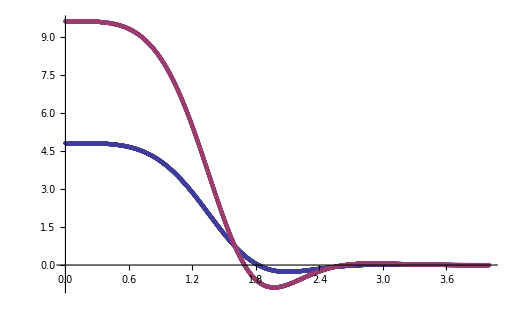
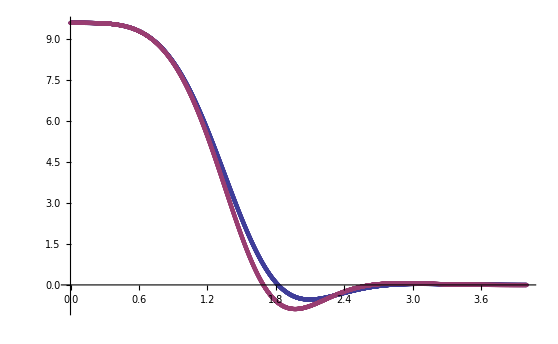
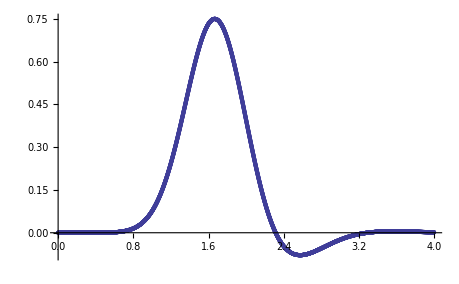

```mathematica
{ListPlot[{pressureLin0pt4,pressureLin0pt8},PlotRange->All],ListPlot[{Table[{pressureLin0pt4[[i,1]],2*pressureLin0pt4[[i,2]]},{i,1,Length[pressureLin0pt4]}],pressureLin0pt8}],ListPlot[Table[{pressureLin0pt4[[i,1]],2*pressureLin0pt4[[i,2]]-pressureLin0pt8[[i,2]]},{i,1,Length[pressureLin0pt4]}],PlotRange->All]}
```

```mathematica
2.1*.318
```

0.6678

```mathematica
1/π^4//N
```

```mathematica
(0.010265982254684336)^(1/4)
```

0.31831

Now we want to make sure our timing matches that seen before.

By setting our mass to 1, I believe that means I am measuring things in terms of m^1/4.  I believe my x axis is reported as (v m^(1/4)).  If I want to compare to Heller, who’s x axis is (v T), then I need to multiply my x axis by T, since my m is one.

The temperature is 0.31831, and this makes sense, since we know  π T = m^1/4 (L?) and

```mathematica
N[1/π]
```

0.31831

```mathematica
pressureLin0pt4T = Table[{(1/π)*pressureLin0pt4[[i,1]],pressureLin0pt4[[i,2]]},{i,1,Length[pressureLin0pt4]}];
pressureLin0pt8T = Table[{(1/π)*pressureLin0pt8[[i,1]],pressureLin0pt8[[i,2]]},{i,1,Length[pressureLin0pt8]}];
```

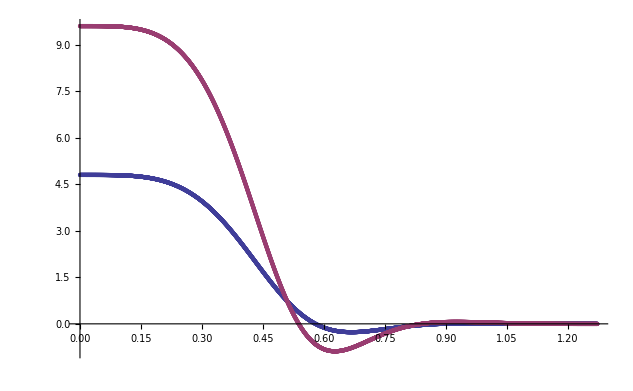
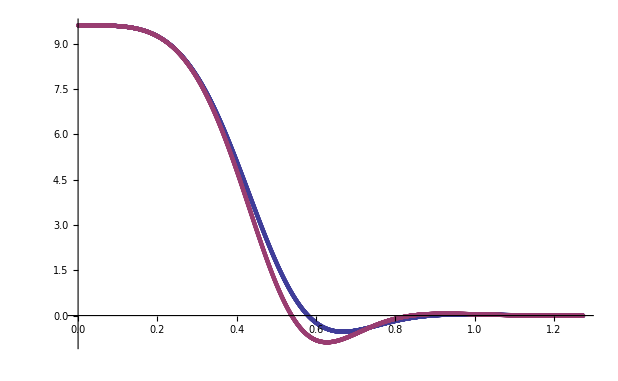
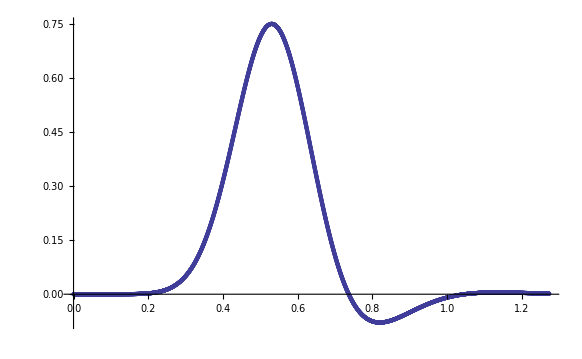

```mathematica
{ListPlot[{pressureLin0pt4T,pressureLin0pt8T},PlotRange->All],ListPlot[{Table[{pressureLin0pt4T[[i,1]],2*pressureLin0pt4T[[i,2]]},{i,1,Length[pressureLin0pt4T]}],pressureLin0pt8T}],ListPlot[Table[{pressureLin0pt4T[[i,1]],2*pressureLin0pt4T[[i,2]]-pressureLin0pt8T[[i,2]]},{i,1,Length[pressureLin0pt4T]}],PlotRange->All]}
```

## SBB

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetuplN60amp0.4wid0.0uave0.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave20.0NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetuplN60amp0.4wid0.0uave0.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave20.0NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.33067×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.4869×10^-14

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.77636×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.6577×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.68434×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.9985×10^-12

### Plots

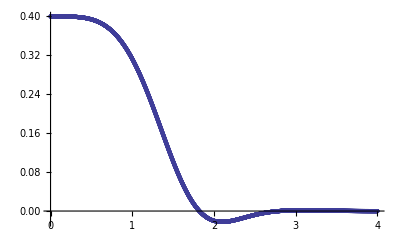

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

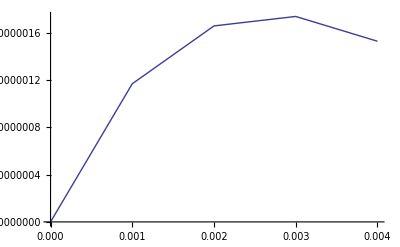

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All,Joined->True]
```

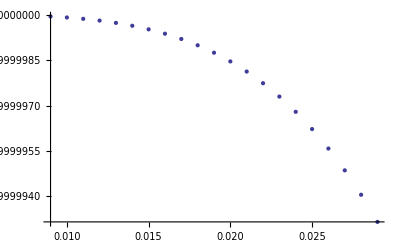

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

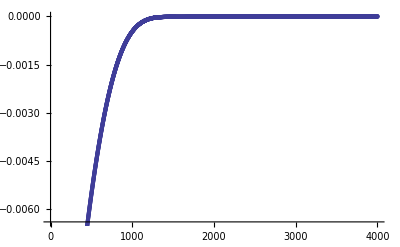

```mathematica
ListPlot[lamblist]
```

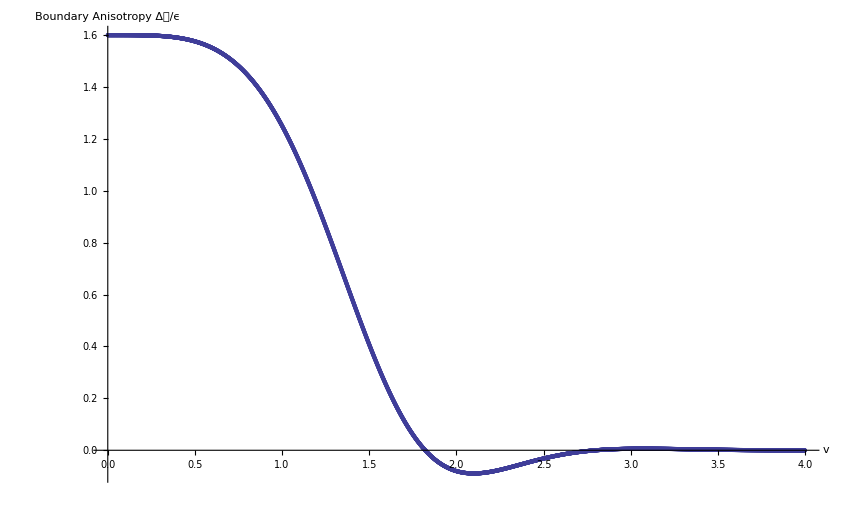

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureLin0pt4= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureLin0pt4,PlotRange->All, AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

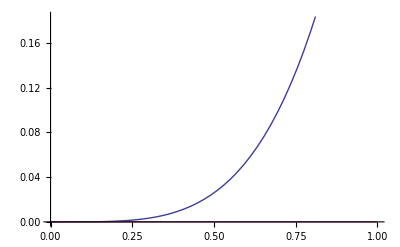

```mathematica
Plot[{B1[x],B80[x]},{x,0,1}]
```

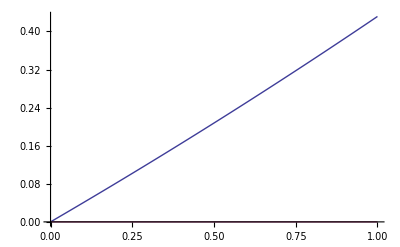

```mathematica
Plot[{Bsub1[x],Bsub80[x]},{x,0,1}]
```

```mathematica
finegrid = Range[0,1,0.01];
```

```mathematica
Bsubevolve= Flatten[Table[{reportfuncttlist[[i]],finegrid[[j]],ToExpression["Bsub"<>ToString[i]<>"[finegrid[[j]]]"]},{i,1,Length[reportfuncttlist]},{j,1,Length[finegrid]}],1];
```

```mathematica
ListPlot3D[Bsubevolve, AxesLabel->{Style["v",25,Bold,Italic, FontFamily->"Times"],Style["u",25,Bold,Italic, FontFamily->"Times"], Style["B/u^3  ",25,Bold,Italic, FontFamily->"Times"]}, AxesStyle->Directive[25],PlotRange->All ,ColorFunction->Function[{x,y,z},Hue[0.6z+0.5]]]
```

-Graphics3D-

```mathematica
finegrid=finegrid[[2;;]];
```

```mathematica
Bevolve= Flatten[Table[{reportfuncttlist[[i]],finegrid[[j]],ToExpression["B"<>ToString[i]<>"[finegrid[[j]]]"]},{i,1,Length[reportfuncttlist]},{j,1,Length[finegrid]}],1];
```

```mathematica
ListPlot3D[Bevolve,AxesLabel->{Style["v",25,Bold,Italic, FontFamily->"Times"],Style["u",25,Bold,Italic, FontFamily->"Times"], Style["B  ",25,Bold,Italic, FontFamily->"Times"]}, AxesStyle->Directive[25],PlotRange->All, ColorFunction->Function[{x,y,z},Hue[0.6z+0.5]]]
```

-Graphics3D-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.276×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.73827

```mathematica
sprod = s - sinitial
```

0.403322

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## SBB double amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetuplN60amp0.8wid0.0uave0.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave20.0NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetuplN60amp0.8wid0.0uave0.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave20.0NS4000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

Part::partw: Part 62 of {-1.00046, -0.999092, -0.994991, -0.988188, -0.978728, -0.966677, -0.952115, -0.935142, -0.915872, -0.894434, -0.870969, -0.845632, -0.818589, -0.790013, -0.760088, -0.729001, -0.696945, -0.664115, -0.630707, -0.596916, -0.562936, -0.528956, -0.495158, -0.461719, -0.428807, -0.396579, -0.365183, -0.334753, -0.305411, -0.277266, -0.250411, -0.224926, -0.200875, -0.178306, -0.157255, -0.13774, -0.119767, -0.103324, -0.0883911, -0.0749319, -0.0628999, -0.052238, -0.0428796, -0.0347501, -0.0277678, -0.0218456, -0.0168926, -0.0128149, -0.00951754, -0.00690569, « 11 »} does not exist.

Part::partw: Part 63 of {-1.00046, -0.999092, -0.994991, -0.988188, -0.978728, -0.966677, -0.952115, -0.935142, -0.915872, -0.894434, -0.870969, -0.845632, -0.818589, -0.790013, -0.760088, -0.729001, -0.696945, -0.664115, -0.630707, -0.596916, -0.562936, -0.528956, -0.495158, -0.461719, -0.428807, -0.396579, -0.365183, -0.334753, -0.305411, -0.277266, -0.250411, -0.224926, -0.200875, -0.178306, -0.157255, -0.13774, -0.119767, -0.103324, -0.0883911, -0.0749319, -0.0628999, -0.052238, -0.0428796, -0.0347501, -0.0277678, -0.0218456, -0.0168926, -0.0128149, -0.00951754, -0.00690569, « 11 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

Part::partw: Part 62 of {-0.0975398, -0.0975004, -0.0973803, -0.0971736, -0.0968706, -0.0964582, -0.0959204, -0.0952388, -0.0943934, -0.0933634, -0.0921284, -0.0906695, -0.0889703, -0.0870184, -0.0848059, -0.0823311, -0.0795984, -0.0766191, -0.073411, -0.0699983, -0.0664106, -0.0626821, -0.05885, -0.0549535, -0.0510323, -« 21 », -« 20 », -0.0394987, -0.0358438, -0.0323311, -0.028983, -0.0258172, -0.0228472, -0.0200824, -0.0175282, -0.0151866, -0.0130562, -0.0111332, -0.00941112, -0.00788163, -0.00653482, -0.00535952, -0.00434369, -0.00347466, -0.00273947, -0.00212506, -0.00161851, -0.00120718, -0.000878904, -0.000622079, « 11 »} does not exist.

Part::partw: Part 63 of {-0.0975398, -0.0975004, -0.0973803, -0.0971736, -0.0968706, -0.0964582, -0.0959204, -0.0952388, -0.0943934, -0.0933634, -0.0921284, -0.0906695, -0.0889703, -0.0870184, -0.0848059, -0.0823311, -0.0795984, -0.0766191, -0.073411, -0.0699983, -0.0664106, -0.0626821, -0.05885, -0.0549535, -0.0510323, -« 21 », -« 20 », -0.0394987, -0.0358438, -0.0323311, -0.028983, -0.0258172, -0.0228472, -0.0200824, -0.0175282, -0.0151866, -0.0130562, -0.0111332, -0.00941112, -0.00788163, -0.00653482, -0.00535952, -0.00434369, -0.00347466, -0.00273947, -0.00212506, -0.00161851, -0.00120718, -0.000878904, -0.000622079, « 11 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

5.91538×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.66454×10^-15

2.66454×10^-15

2.66454×10^-15

3.33067×10^-16

3.33067×10^-16

3.33067×10^-16

1.11022×10^-16

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.13163×10^-14

2.13163×10^-14

2.13163×10^-14

2.84217×10^-14

2.4869×10^-14

2.4869×10^-14

1.56319×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.90799×10^-14

3.90799×10^-14

3.90799×10^-14

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

4.26326×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.33884×10^-11

1.33884×10^-11

1.33884×10^-11

5.1692×10^-13

5.1692×10^-13

5.1692×10^-13

9.14158×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.81899×10^-12

1.81899×10^-12

1.81899×10^-12

8.52651×10^-14

8.52651×10^-14

8.52651×10^-14

9.32622×10^-14

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.995×10^-12

9.995×10^-12

9.995×10^-12

9.99834×10^-12

9.97297×10^-12

9.97297×10^-12

9.94838×10^-12

9.94838×10^-12

### Plots

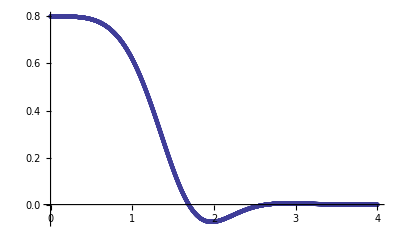

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

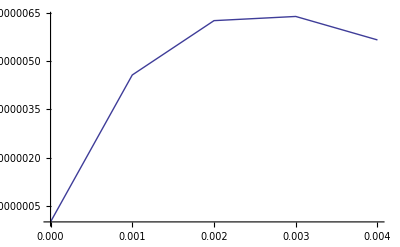

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All,Joined->True]
```

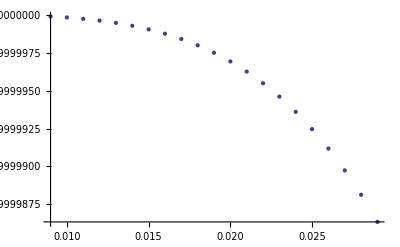

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

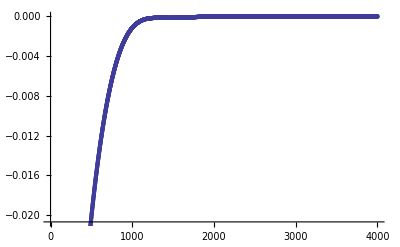

```mathematica
ListPlot[lamblist]
```

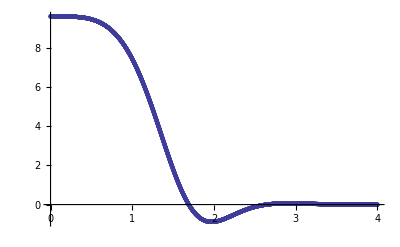

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureLin0pt8= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureLin0pt8,PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.08855×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

0.810242

```mathematica
sprod = s - sinitial
```

2.33135

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## SBB a2=8

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetuplN60amp0.4wid0.0uave0.0a2-8.0f30.0fxy0.0TS0.001amp20.0wid20.0uave20.0NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetuplN60amp0.4wid0.0uave0.0a2-8.0f30.0fxy0.0TS0.001amp20.0wid20.0uave20.0NS4000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

Part::partw: Part 62 of {-2.82843, -2.82612, -2.81921, -2.80771, -2.79163, -2.77102, -2.7459, -2.71633, -2.68237, -2.64409, -2.60156, -2.55489, -2.50417, -2.44952, -2.39108, -2.32899, -2.26342, -2.19453, -2.12254, -2.04765, -1.97009, -1.89011, -1.80799, -1.72401, -1.63848, -1.55173, -1.4641, -1.37596, -1.28769, -1.19969, -1.11235, -1.02608, -0.94132, -0.858474, -0.777958, -0.700177, -0.62552, -0.554354, -0.487014, -0.423803, -0.364977, -0.310745, -0.261258, -0.216606, -0.176813, -0.141835, -0.111558, -0.0857967, -0.0643034, -0.0467687, « 11 »} does not exist.

Part::partw: Part 63 of {-2.82843, -2.82612, -2.81921, -2.80771, -2.79163, -2.77102, -2.7459, -2.71633, -2.68237, -2.64409, -2.60156, -2.55489, -2.50417, -2.44952, -2.39108, -2.32899, -2.26342, -2.19453, -2.12254, -2.04765, -1.97009, -1.89011, -1.80799, -1.72401, -1.63848, -1.55173, -1.4641, -1.37596, -1.28769, -1.19969, -1.11235, -1.02608, -0.94132, -0.858474, -0.777958, -0.700177, -0.62552, -0.554354, -0.487014, -0.423803, -0.364977, -0.310745, -0.261258, -0.216606, -0.176813, -0.141835, -0.111558, -0.0857967, -0.0643034, -0.0467687, « 11 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

Part::partw: Part 62 of {-0.00037342, -0.000373815, -0.000375, -0.000376978, -0.00037975, -0.00038332, -0.000387692, -0.000392869, -0.000398853, -0.000405645, -0.000413244, -0.000421645, -0.000430838, -0.000440806, -0.000451524, -0.000462958, -0.000475059, -0.000487765, -0.000500994, -0.000514646, -0.000528595, -0.000542689, -0.000556746, « 6 », -0.000631982, -0.000635333, -0.000635658, -0.000632565, -0.000625698, -0.000614752, -0.000599498, -0.000579807, -0.000555666, -0.0005272, -0.000494686, -0.000458557, -0.000419404, -0.000377963, -0.000335094, -0.000291751, -0.000248935, -0.000207649, -0.000168843, -0.000133355, -0.000101858, « 11 »} does not exist.

Part::partw: Part 63 of {-0.00037342, -0.000373815, -0.000375, -0.000376978, -0.00037975, -0.00038332, -0.000387692, -0.000392869, -0.000398853, -0.000405645, -0.000413244, -0.000421645, -0.000430838, -0.000440806, -0.000451524, -0.000462958, -0.000475059, -0.000487765, -0.000500994, -0.000514646, -0.000528595, -0.000542689, -0.000556746, « 6 », -0.000631982, -0.000635333, -0.000635658, -0.000632565, -0.000625698, -0.000614752, -0.000599498, -0.000579807, -0.000555666, -0.0005272, -0.000494686, -0.000458557, -0.000419404, -0.000377963, -0.000335094, -0.000291751, -0.000248935, -0.000207649, -0.000168843, -0.000133355, -0.000101858, « 11 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-6.32316×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«7 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.77556×10^-17

2.77556×10^-17

3.33067×10^-16

3.33067×10^-16

3.33067×10^-16

«3 more identical outputs»

1.11022×10^-16

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«7 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

1.42109×10^-13

2.84217×10^-14

2.84217×10^-14

2.84217×10^-14

«1 more identical outputs»

2.4869×10^-14

2.4869×10^-14

1.56319×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«7 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

8.88178×10^-15

8.88178×10^-15

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

«3 more identical outputs»

4.26326×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

7.99361×10^-14

7.99361×10^-14

5.1692×10^-13

5.1692×10^-13

5.1692×10^-13

«3 more identical outputs»

9.14158×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

6.49936×10^-14

6.49936×10^-14

8.52651×10^-14

8.52651×10^-14

8.52651×10^-14

«3 more identical outputs»

9.32622×10^-14

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99534×10^-12

9.99534×10^-12

9.99834×10^-12

9.99834×10^-12

9.99834×10^-12

«1 more identical outputs»

9.97297×10^-12

9.97297×10^-12

9.94838×10^-12

9.94838×10^-12

### Plots

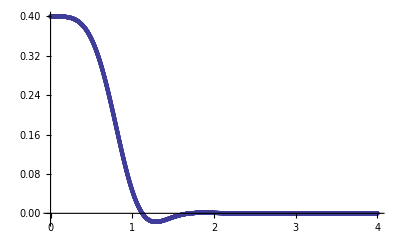

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

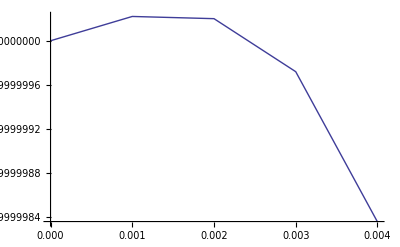

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All,Joined->True]
```

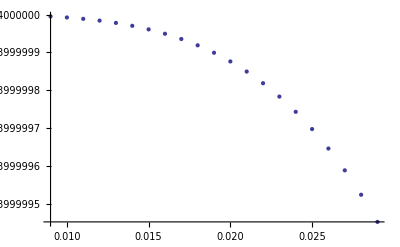

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

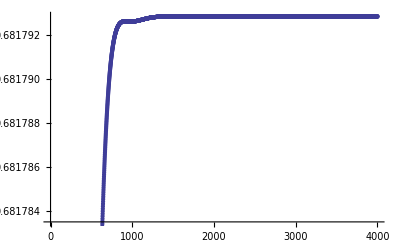

```mathematica
ListPlot[lamblist]
```

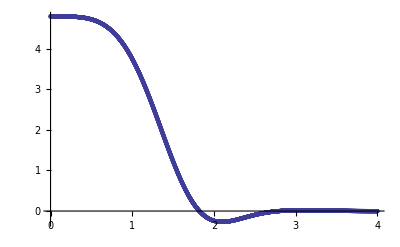

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureLin0pt4a28= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureLin0pt4,PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.535331

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.55979×10^-19

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

14.944

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

14.916

```mathematica
sprod = s - sinitial
```

0.0280472

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-7.25

## SBB double amp a2=8

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetuplN60amp0.8wid0.0uave0.0a2-8.0f30.0fxy0.0TS0.001amp20.0wid20.0uave20.0NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetuplN60amp0.8wid0.0uave0.0a2-8.0f30.0fxy0.0TS0.001amp20.0wid20.0uave20.0NS4000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

Part::partw: Part 62 of {-2.82843, -2.82612, -2.81921, -2.80771, -2.79163, -2.77102, -2.7459, -2.71633, -2.68237, -2.64409, -2.60156, -2.55489, -2.50417, -2.44952, -2.39108, -2.32899, -2.26342, -2.19453, -2.12254, -2.04765, -1.97009, -1.89011, -1.80799, -1.72401, -1.63848, -1.55173, -1.4641, -1.37596, -1.28769, -1.19969, -1.11235, -1.02608, -0.94132, -0.858474, -0.777958, -0.700177, -0.62552, -0.554354, -0.487014, -0.423803, -0.364977, -0.310745, -0.261258, -0.216606, -0.176813, -0.141835, -0.111558, -0.0857967, -0.0643035, -0.0467687, « 11 »} does not exist.

Part::partw: Part 63 of {-2.82843, -2.82612, -2.81921, -2.80771, -2.79163, -2.77102, -2.7459, -2.71633, -2.68237, -2.64409, -2.60156, -2.55489, -2.50417, -2.44952, -2.39108, -2.32899, -2.26342, -2.19453, -2.12254, -2.04765, -1.97009, -1.89011, -1.80799, -1.72401, -1.63848, -1.55173, -1.4641, -1.37596, -1.28769, -1.19969, -1.11235, -1.02608, -0.94132, -0.858474, -0.777958, -0.700177, -0.62552, -0.554354, -0.487014, -0.423803, -0.364977, -0.310745, -0.261258, -0.216606, -0.176813, -0.141835, -0.111558, -0.0857967, -0.0643035, -0.0467687, « 11 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

Part::partw: Part 62 of {-0.00149588, -0.00149746, -0.00150223, -0.00151018, -0.00152132, -0.00153567, -0.00155324, -0.00157405, -0.0015981, -0.0016254, -0.00165594, -0.00168971, -0.00172666, -0.00176672, -0.00180979, -0.00185574, -0.00190436, -0.00195541, -0.00200856, -0.0020634, -0.00211942, -0.00217602, -0.00223246, « 5 », -0.00251021, -0.00253406, -0.00254738, -0.00254854, -0.00253598, -0.00250827, -0.00246419, -0.00240283, -0.00232369, -0.00222672, -0.00211243, -0.00198194, -0.00183699, -0.00167995, -0.00151379, -0.00134194, -0.00116824, -0.000996683, -0.000831296, -0.000675872, -0.00053376, -0.000407655, « 11 »} does not exist.

Part::partw: Part 63 of {-0.00149588, -0.00149746, -0.00150223, -0.00151018, -0.00152132, -0.00153567, -0.00155324, -0.00157405, -0.0015981, -0.0016254, -0.00165594, -0.00168971, -0.00172666, -0.00176672, -0.00180979, -0.00185574, -0.00190436, -0.00195541, -0.00200856, -0.0020634, -0.00211942, -0.00217602, -0.00223246, « 5 », -0.00251021, -0.00253406, -0.00254738, -0.00254854, -0.00253598, -0.00250827, -0.00246419, -0.00240283, -0.00232369, -0.00222672, -0.00211243, -0.00198194, -0.00183699, -0.00167995, -0.00151379, -0.00134194, -0.00116824, -0.000996683, -0.000831296, -0.000675872, -0.00053376, -0.000407655, « 11 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-6.51945×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«7 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

8.32667×10^-17

8.32667×10^-17

2.66454×10^-15

2.66454×10^-15

2.66454×10^-15

3.33067×10^-16

3.33067×10^-16

3.33067×10^-16

1.11022×10^-16

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«7 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.13687×10^-13

1.13687×10^-13

2.13163×10^-14

2.13163×10^-14

2.13163×10^-14

2.84217×10^-14

2.4869×10^-14

2.4869×10^-14

1.56319×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«7 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.77636×10^-14

1.77636×10^-14

3.90799×10^-14

3.90799×10^-14

3.90799×10^-14

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

4.26326×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.18572×10^-13

1.18572×10^-13

1.33884×10^-11

1.33884×10^-11

1.33884×10^-11

5.1692×10^-13

5.1692×10^-13

5.1692×10^-13

9.14158×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.87125×10^-14

5.87125×10^-14

1.81899×10^-12

1.81899×10^-12

1.81899×10^-12

8.52651×10^-14

8.52651×10^-14

8.52651×10^-14

9.32622×10^-14

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99822×10^-12

9.99822×10^-12

9.995×10^-12

9.995×10^-12

9.995×10^-12

9.99834×10^-12

9.97297×10^-12

9.97297×10^-12

9.94838×10^-12

9.94838×10^-12

### Plots

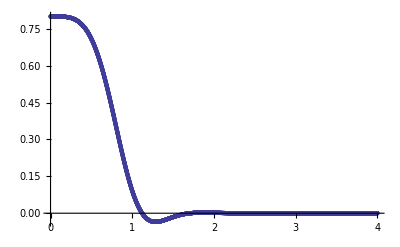

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

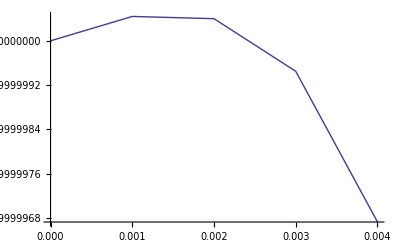

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All,Joined->True]
```

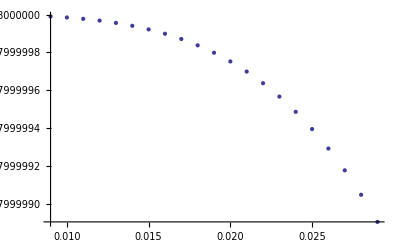

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

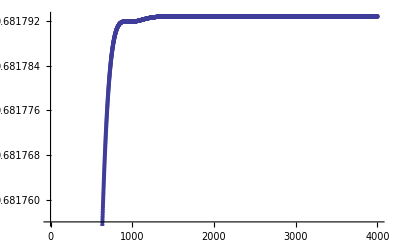

```mathematica
ListPlot[lamblist]
```

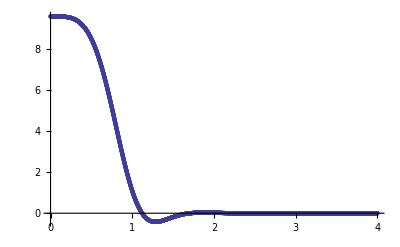

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureLin0pt8a28= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureLin0pt8a28,PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.535331

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-6.32004×10^-19

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

14.944

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

14.8315

```mathematica
sprod = s - sinitial
```

0.112517

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-7.25

## GAUSSIANR Doubling amp Non-Linearity Test, Moving into the bulk while keeping inital B the same.

SBB

In the r coordinate, our three pulses (starting from furthest from the horizon), B, look like this, where the horizon is at r = 1.

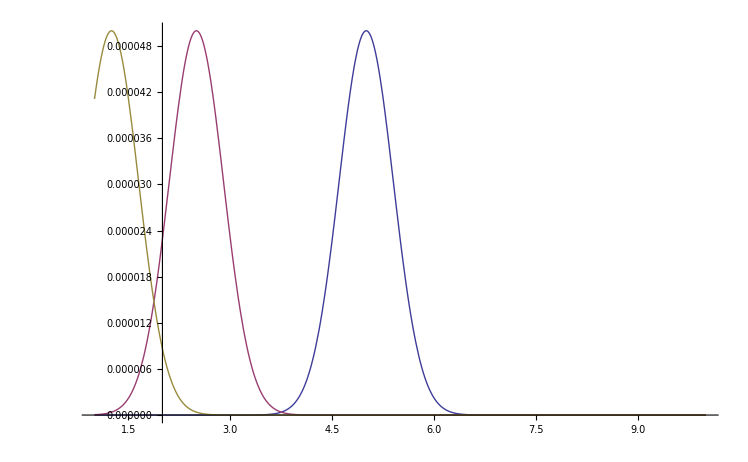

```mathematica
Plot[{0.00005 ⅇ^((-(r-5)^2)/(2*0.4^2)),0.00005 ⅇ^((-(r-2.5)^2)/(2*0.4^2)),0.00005 ⅇ^((-(r-1.25)^2)/(2*0.4^2))},{r,1,10},PlotRange->All]
```

```mathematica
1/2.2
```

0.454545

In the u coordinate, they look like this.

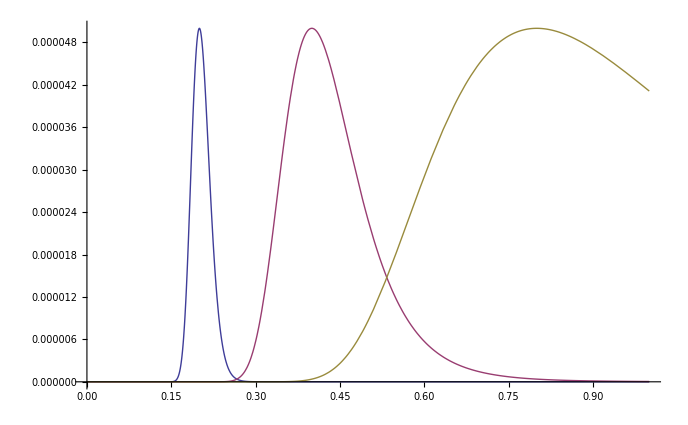

```mathematica
Plot[{0.00005 ⅇ^((-(1/u-5)^2)/(2*0.4^2)),0.00005 ⅇ^((-(1/u-2.5)^2)/(2*0.4^2)),0.00005 ⅇ^((-(1/u-1.25)^2)/(2*0.4^2))},{u,0,1},PlotRange->All]
```

Which checks out from our plot of B.

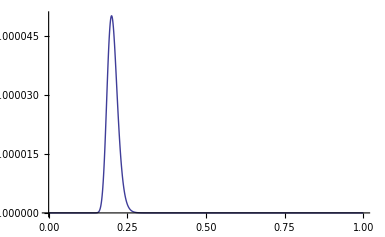
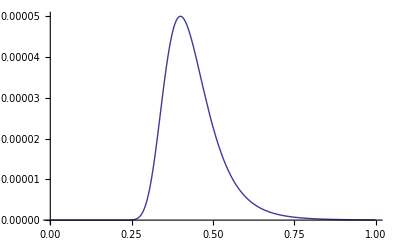
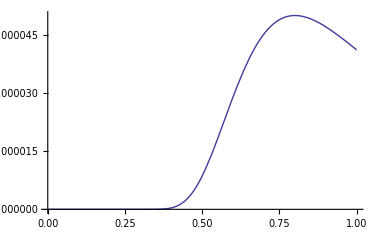

Here we see that as we move our pulses closer to the horizon, our nonlinearties have a relative size of 10^-8.

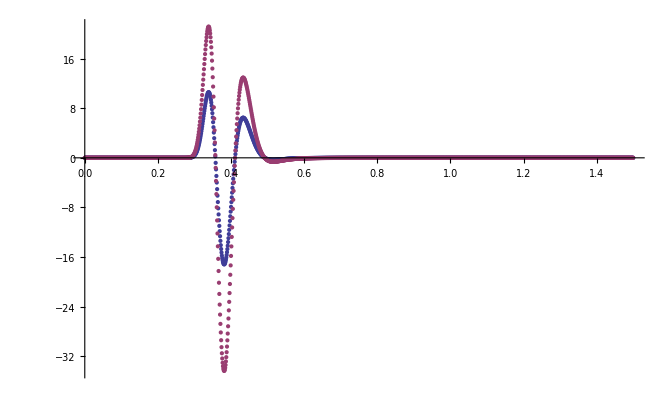
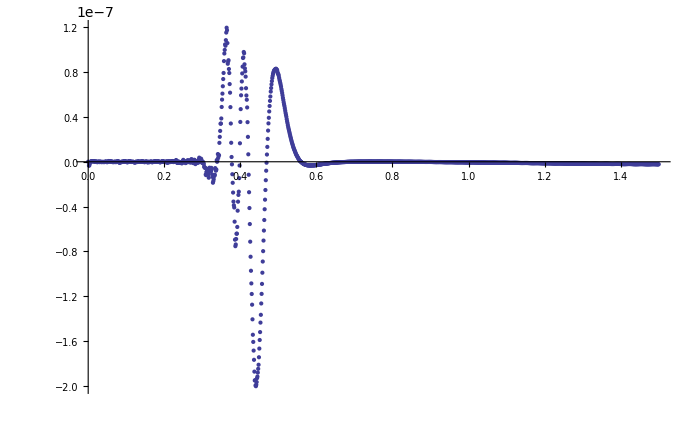

```mathematica
{ListPlot[{pressureuave0pt2base,pressureuave0pt2damp},PlotRange->All],ListPlot[Table[{pressureuave0pt2base[[i,1]],2*pressureuave0pt2base[[i,2]]-pressureuave0pt2damp[[i,2]]},{i,1,Length[pressureuave0pt2base]}],PlotRange->All]}
```

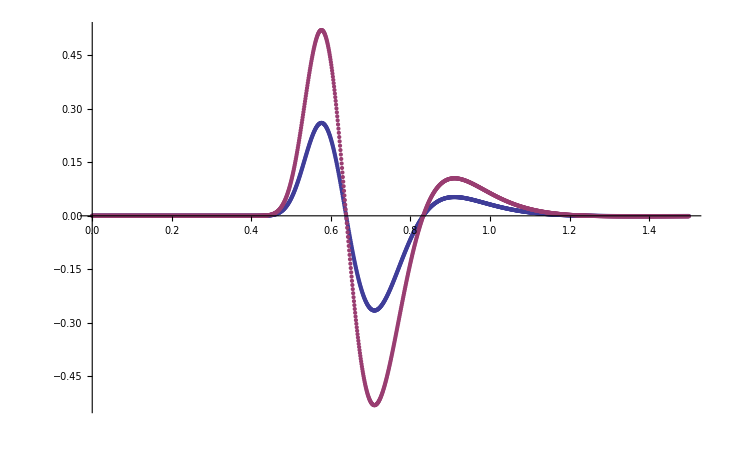
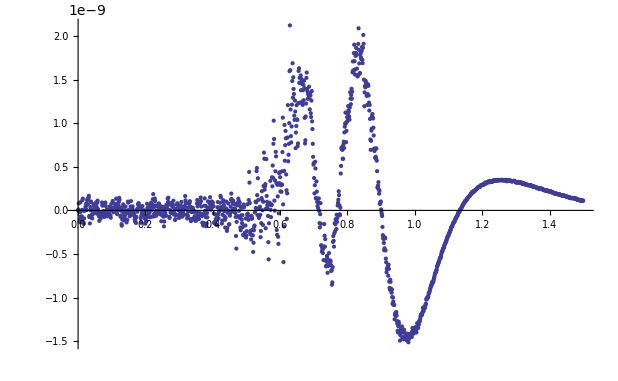

```mathematica
{ListPlot[{pressureuave0pt4base,pressureuave0pt4damp},PlotRange->All],ListPlot[Table[{pressureuave0pt4base[[i,1]],2*pressureuave0pt4base[[i,2]]-pressureuave0pt4damp[[i,2]]},{i,1,Length[pressureuave0pt2base]}],PlotRange->All]}
```

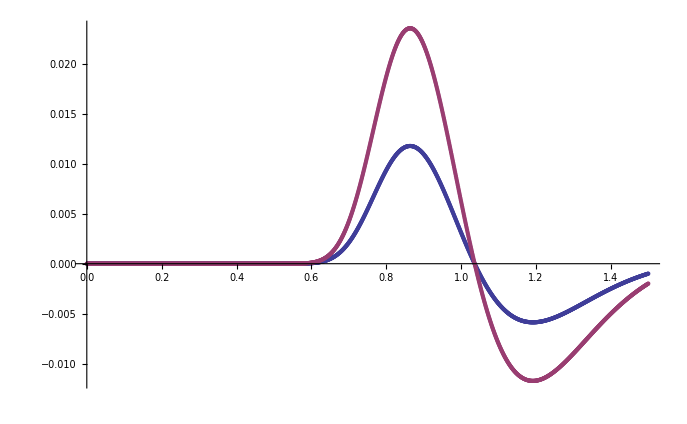
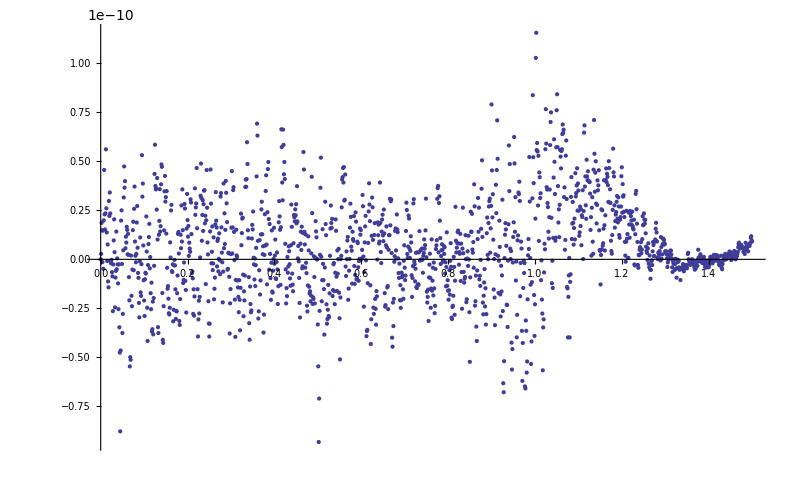

```mathematica
{ListPlot[{pressureuave0pt8base,pressureuave0pt8damp},PlotRange->All],ListPlot[Table[{pressureuave0pt8base[[i,1]],2*pressureuave0pt8base[[i,2]]-pressureuave0pt8damp[[i,2]]},{i,1,Length[pressureuave0pt8base]}],PlotRange->All]}
```

### Comparing uave change only

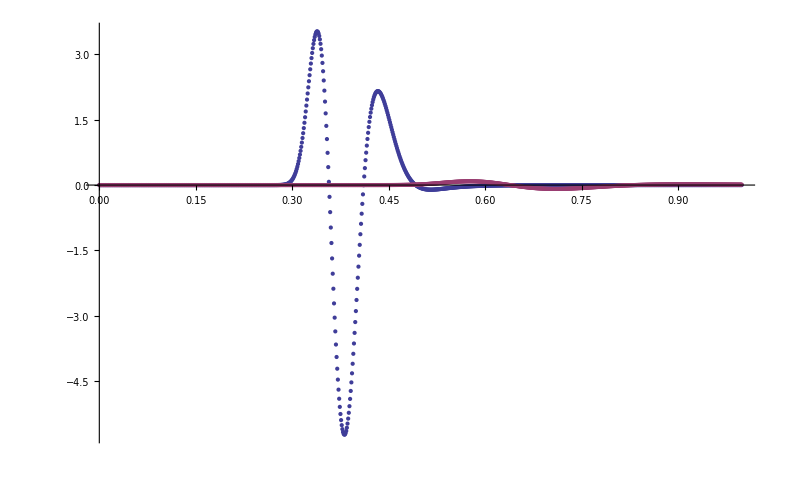

```mathematica
ListPlot[{pressureuave0pt2base[[;;1000]],pressureuave0pt4base[[;;1000]]},PlotRange->All]
```

## SBB at position 1

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp5e-05wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp5e-05wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

$Failed

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«1 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«3 more identical outputs»

```mathematica
sigmadot2[1]
```

9.64345×10^-12

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] $Failed⟦2⟧⟦j⟧+1/2 (1+$Failed⟦2⟧+∑_(j=1)^(1+Num) Card[-1+j,1] $Failed⟦2⟧⟦j⟧)^2

9.64345×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«4 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

Abs[$Failed]

Abs[$Failed]

0.

0.

0.

«1 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.77556×10^-17

Abs[$Failed]

Abs[$Failed]

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

Abs[$Failed]

Abs[$Failed]

0.

0.

0.

«1 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

Abs[$Failed]

Abs[$Failed]

1.7053×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

Abs[$Failed]

Abs[$Failed]

0.

0.

0.

«1 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.42109×10^-14

Abs[$Failed]

Abs[$Failed]

1.42109×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.35509×10^-13

Abs[$Failed]

Abs[$Failed]

3.35509×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.1523×10^-13

Abs[$Failed]

Abs[$Failed]

1.1523×10^-13

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.9864×10^-12

Abs[$Failed]

Abs[$Failed]

9.9864×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

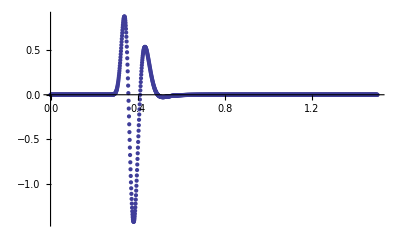

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

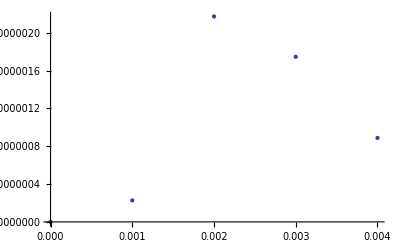

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

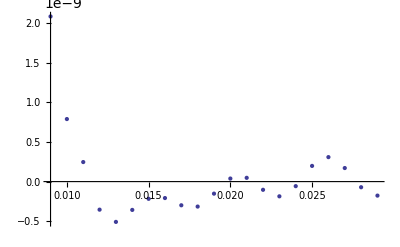

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

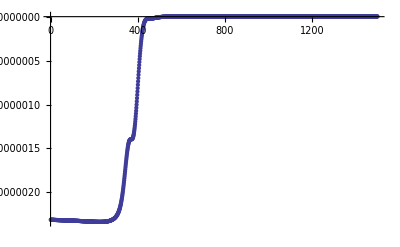

```mathematica
ListPlot[lamblist]
```

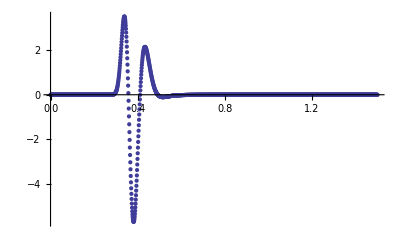

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureuave0pt2base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureuave0pt2base,PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

-(0.-2 (1+Symbol)+$Failed⟦-1⟧)/(4 π)

0.31831

0.31831

0.31831

«1 more identical outputs»

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

0.

0.

«3 more identical outputs»

```mathematica
chem/T
```

0.

0.

0.

«4 more identical outputs»

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

3/4

3/4

«4 more identical outputs»

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.37423×10^-15

$Failed⟦-1⟧

-2.37423×10^-15

-2.37423×10^-15

-2.37423×10^-15

-9.49552×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

π (1+2 $Failed⟦-1⟧)^3

3.14159

3.14159

3.14159

«1 more identical outputs»

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.14157

π (1+2 $Failed⟦1⟧)^3

3.14157

3.14157

3.14157

3.1415

```mathematica
sprod = s - sinitial
```

0.0000223332

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

0.0000223332

0.0000223332

0.0000223332

0.0000893332

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

-0.25

-0.25

-0.25

«1 more identical outputs»

## SBB at position 1 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

```mathematica
sigmadot2[1]
```

-4.61575×10^-13

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.11022×10^-16

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.26326×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

9.14158×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.32622×10^-14

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.94838×10^-12

9.94838×10^-12

### Plots

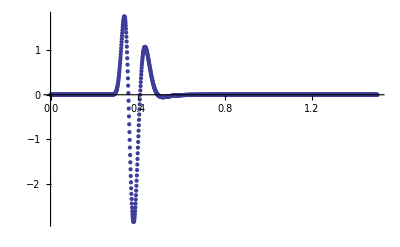

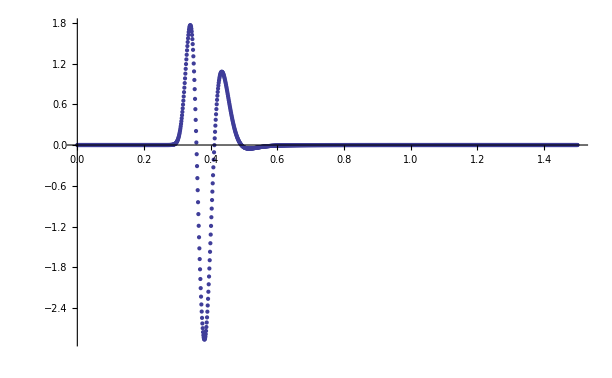

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

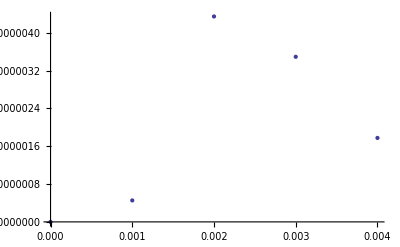

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

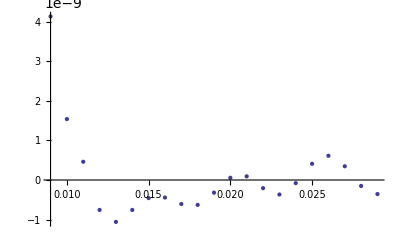

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

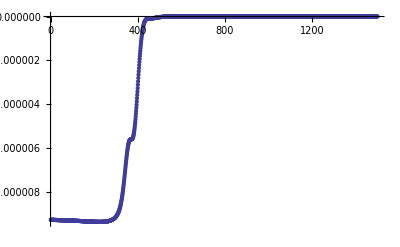

-Graphics-

```mathematica
ListPlot[lamblist]
```

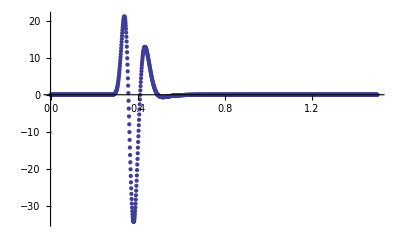

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureuave0pt2damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureuave0pt2damp,PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

0.

```mathematica
chem/T
```

0.

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-9.49552×10^-15

-9.49552×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.1415

3.1415

```mathematica
sprod = s - sinitial
```

0.0000893332

0.0000893332

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

-0.25

## SBB at position 2

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp5e-05wid0.4uave0.4a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp5e-05wid0.4uave0.4a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

$Failed

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«1 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«2 more identical outputs»

```mathematica
sigmadot2[1]
```

6.41409×10^-12

0.+($Failed)/2+1/2 (1+$Failed+$Failed⟦2⟧)^2

6.41409×10^-12

6.41409×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«4 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

Abs[$Failed]

0.

Abs[$Failed]

0.

0.

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.77626×10^-20

Abs[$Failed]

6.77626×10^-20

Abs[$Failed]

6.77626×10^-20

6.77626×10^-20

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

Abs[$Failed]

0.

Abs[$Failed]

0.

0.

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

Abs[$Failed]

1.56319×10^-13

Abs[$Failed]

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

Abs[$Failed]

0.

Abs[$Failed]

0.

0.

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.77156×10^-16

Abs[$Failed]

7.77156×10^-16

Abs[$Failed]

7.77156×10^-16

7.77156×10^-16

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.98619×10^-13

Abs[$Failed]

1.98619×10^-13

Abs[$Failed]

1.98619×10^-13

1.98619×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.70971×10^-14

Abs[$Failed]

9.70971×10^-14

Abs[$Failed]

9.70971×10^-14

9.70971×10^-14

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.76652×10^-12

Abs[$Failed]

9.76652×10^-12

Abs[$Failed]

9.76652×10^-12

9.76652×10^-12

9.94838×10^-12

### Plots

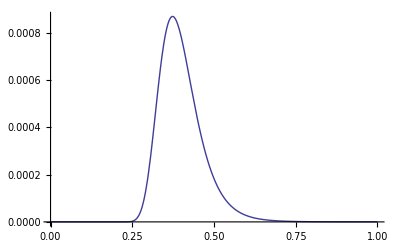

```mathematica
Plot[Bsub1[x],{x,0,1}]
```

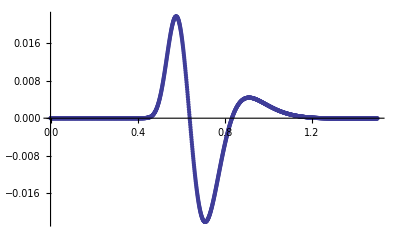

-Graphics-

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

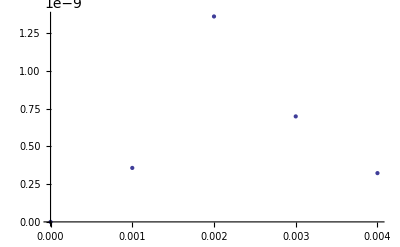

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

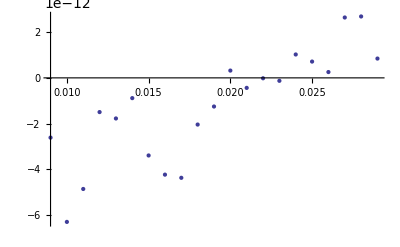

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

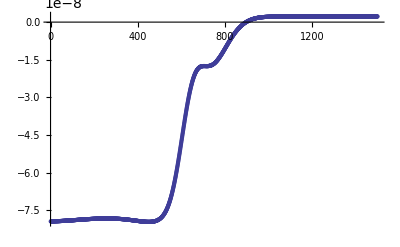

-Graphics-

```mathematica
ListPlot[lamblist]
```

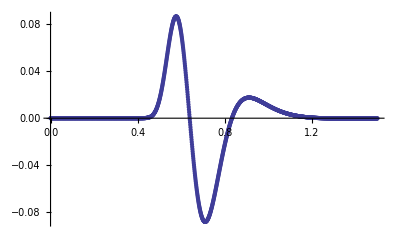

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureuave0pt4base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureuave0pt4base,PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

-(0.-2 (1+Symbol)+$Failed⟦-1⟧)/(4 π)

0.31831

0.31831

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

0.

0.

«2 more identical outputs»

```mathematica
chem/T
```

0.

0.

0.

«4 more identical outputs»

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

3/4

3/4

«4 more identical outputs»

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.30548×10^-12

$Failed⟦-1⟧

-2.30548×10^-12

-2.30548×10^-12

-9.49552×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

π (1+2 $Failed⟦-1⟧)^3

3.14159

3.14159

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.14159

π (1+2 $Failed⟦1⟧)^3

3.14159

3.14159

3.1415

```mathematica
sprod = s - sinitial
```

8.73378×10^-7

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

8.73378×10^-7

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

8.73378×10^-7

8.73378×10^-7

0.0000893332

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

-0.25

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

-0.25

-0.25

-0.25

## SBB at position 2 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.4a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.4a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

$Failed

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

```mathematica
sigmadot2[1]
```

-1.01807×10^-12

0.+($Failed)/2+1/2 (1+$Failed+$Failed⟦2⟧)^2

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«2 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.1684×10^-19

2.1684×10^-19

Abs[$Failed]

Abs[$Failed]

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

1.42109×10^-13

Abs[$Failed]

Abs[$Failed]

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.55431×10^-15

1.55431×10^-15

Abs[$Failed]

Abs[$Failed]

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.11164×10^-13

2.11164×10^-13

Abs[$Failed]

Abs[$Failed]

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.03129×10^-13

1.03129×10^-13

Abs[$Failed]

Abs[$Failed]

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.95626×10^-12

9.95626×10^-12

Abs[$Failed]

Abs[$Failed]

9.94838×10^-12

### Plots

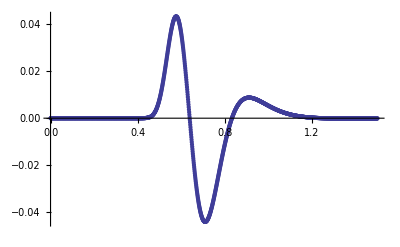

ListPlot[{},PlotRange→All]

-Graphics-

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

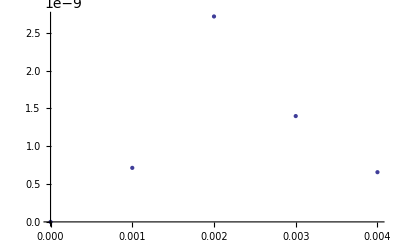

ListPlot[{}⟦1;;5⟧,PlotRange→All]

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

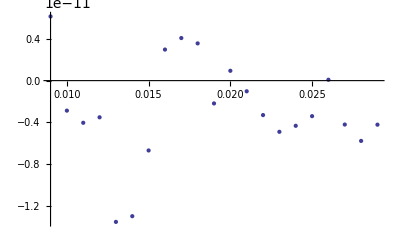

ListPlot[{}⟦10;;30⟧,PlotRange→All]

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

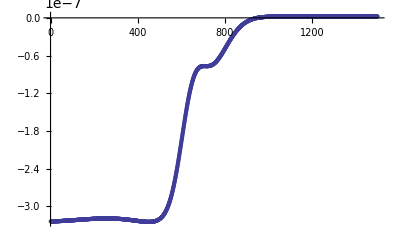

ListPlot[$Failed]

-Graphics-

```mathematica
ListPlot[lamblist]
```

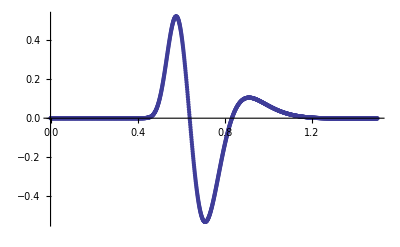

ListPlot[{},PlotRange→All]

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureuave0pt4damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureuave0pt4damp,PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

-(0.-2 (1+Symbol)+$Failed⟦-1⟧)/(4 π)

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

0.

0.

```mathematica
chem/T
```

0.

0.

0.

«2 more identical outputs»

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

3/4

3/4

«2 more identical outputs»

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-9.22191×10^-12

$Failed⟦-1⟧

-9.49552×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

π (1+2 $Failed⟦-1⟧)^3

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.14159

π (1+2 $Failed⟦1⟧)^3

3.1415

```mathematica
sprod = s - sinitial
```

3.49352×10^-6

3.49352×10^-6

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

0.0000893332

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

-0.25

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

-0.25

## SBB at position 3

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp5e-05wid0.4uave0.8a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp5e-05wid0.4uave0.8a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«2 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

```mathematica
sigmadot2[1]
```

3.03146×10^-12

3.03146×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.76456×10^-22

4.76456×10^-22

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

1.98952×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.20417×10^-17

5.20417×10^-17

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.39586×10^-13

2.39586×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

8.42754×10^-14

8.42754×10^-14

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.82026×10^-12

9.82026×10^-12

9.94838×10^-12

### Plots

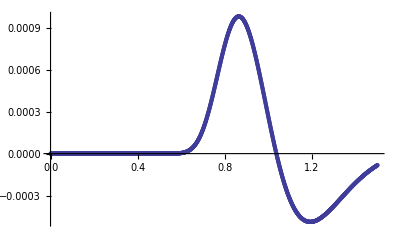

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

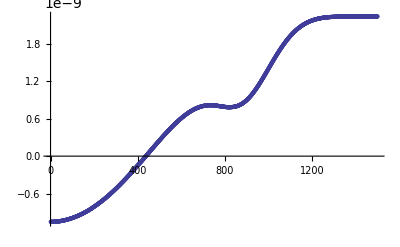

```mathematica
ListPlot[lamblist]
```

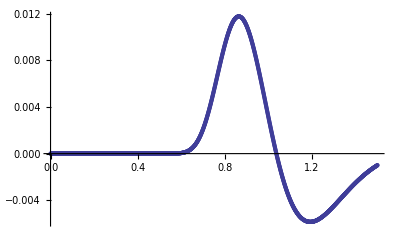

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureuave0pt8base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureuave0pt8base,PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

0.31831

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

0.

0.

```mathematica
chem/T
```

0.

0.

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

3/4

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.24909×10^-11

-1.24909×10^-11

-9.49552×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

3.14159

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.14159

3.14159

3.1415

```mathematica
sprod = s - sinitial
```

4.70378×10^-8

4.70378×10^-8

0.0000893332

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

-0.25

-0.25

## SBB at position 3 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.8a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.8a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0001wid0.8uave0.4a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.0001wid0.8uave0.4a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.4a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

$Failed

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

```mathematica
sigmadot2[1]
```

4.99567×10^-12

0.+($Failed)/2+1/2 (1+$Failed+$Failed⟦2⟧)^2

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«1 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.90582×10^-21

Abs[$Failed]

Abs[$Failed]

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

Abs[$Failed]

Abs[$Failed]

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.31839×10^-16

Abs[$Failed]

Abs[$Failed]

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.01617×10^-13

Abs[$Failed]

Abs[$Failed]

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.77898×10^-14

Abs[$Failed]

Abs[$Failed]

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.73877×10^-12

Abs[$Failed]

Abs[$Failed]

9.94838×10^-12

### Plots

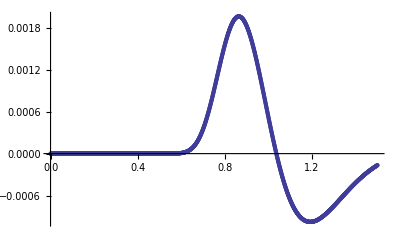

ListPlot[{},PlotRange→All]

-Graphics-

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

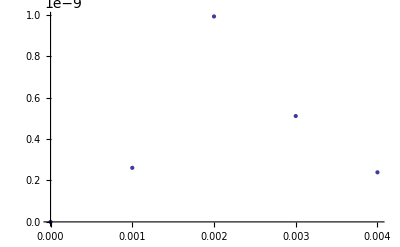

ListPlot[{}⟦1;;5⟧,PlotRange→All]

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

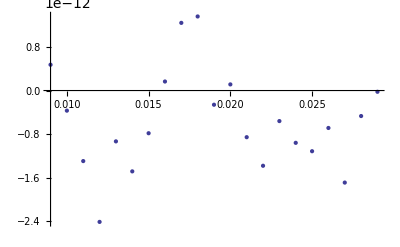

ListPlot[{}⟦10;;30⟧,PlotRange→All]

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

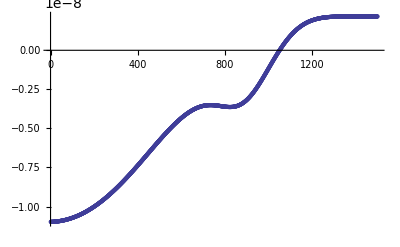

ListPlot[$Failed]

-Graphics-

```mathematica
ListPlot[lamblist]
```

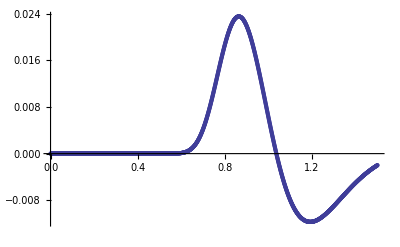

ListPlot[{},PlotRange→All]

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureuave0pt8damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureuave0pt8damp,PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

-(0.-2 (1+Symbol)+$Failed⟦-1⟧)/(4 π)

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

0.

0.

```mathematica
chem/T
```

0.

0.

0.

«1 more identical outputs»

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

3/4

3/4

«1 more identical outputs»

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.99635×10^-11

$Failed⟦-1⟧

-9.49552×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

π (1+2 $Failed⟦-1⟧)^3

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.14159

π (1+2 $Failed⟦1⟧)^3

3.1415

```mathematica
sprod = s - sinitial
```

1.88177×10^-7

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

0.0000893332

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

-0.25

Again with more amplitude.

With a larger initial amplitude, we see a relative size of 10^-5, 10^-5, and 10^-6 when closest to the horizon.  We might have seen this before above, but the numerical noise at 10^-10 didn’t allow us to see smaller relative size of the non-linearity.

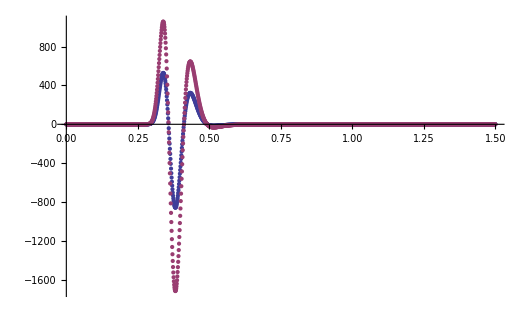
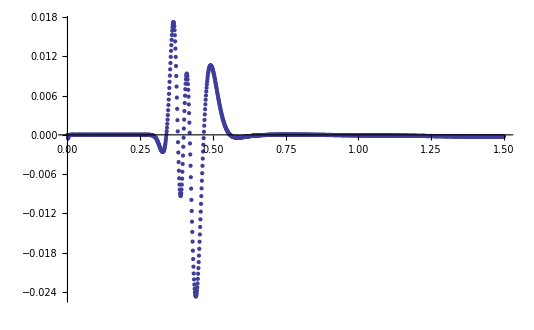

```mathematica
{ListPlot[{pressureset2uave0pt2base,pressureset2uave0pt2damp},PlotRange->All],ListPlot[Table[{pressureset2uave0pt2base[[i,1]],2*pressureset2uave0pt2base[[i,2]]-pressureset2uave0pt2damp[[i,2]]},{i,1,Length[pressureset2uave0pt2base]}],PlotRange->All]}
```

```mathematica
0.022/1700//N
```

0.0000129412

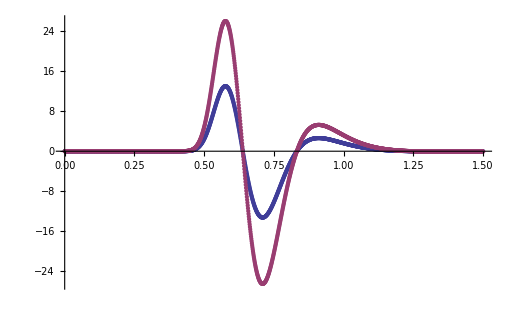
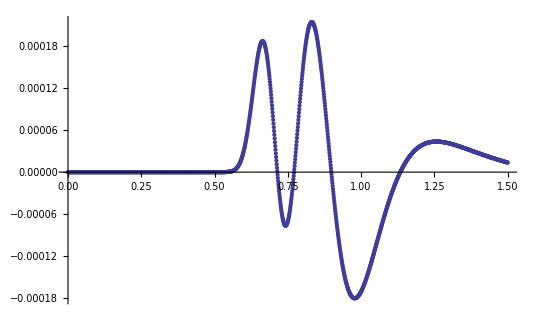

```mathematica
{ListPlot[{pressureset2uave0pt4base,pressureset2uave0pt4damp},PlotRange->All],ListPlot[Table[{pressureset2uave0pt4base[[i,1]],2*pressureset2uave0pt4base[[i,2]]-pressureset2uave0pt4damp[[i,2]]},{i,1,Length[pressureset2uave0pt2base]}],PlotRange->All]}
```

```mathematica
0.0002/26//N
```

7.69231×10^-6

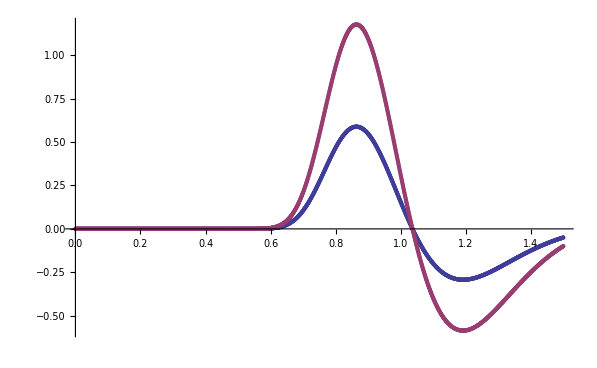
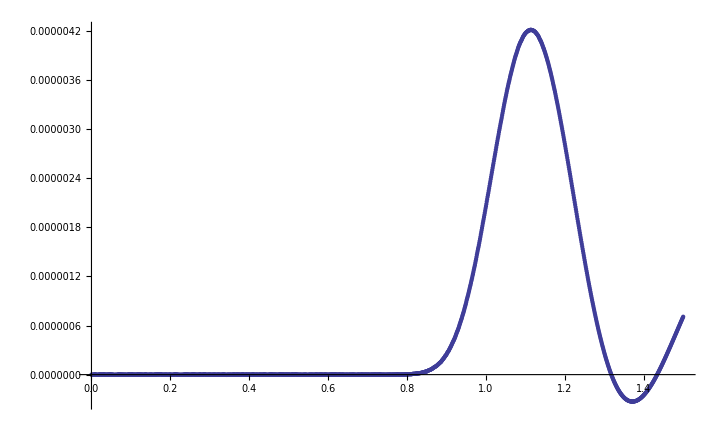

```mathematica
{ListPlot[{pressureset2uave0pt8base,pressureset2uave0pt8damp},PlotRange->All],ListPlot[Table[{pressureset2uave0pt8base[[i,1]],2*pressureset2uave0pt8base[[i,2]]-pressureset2uave0pt8damp[[i,2]]},{i,1,Length[pressureset2uave0pt8base]}],PlotRange->All]}
```

```mathematica
4*10^(-6)/1.2
```

3.33333×10^-6

Moving the source slightly out so not cut by horizon - this means uave = 0.5 instead of 0.8.

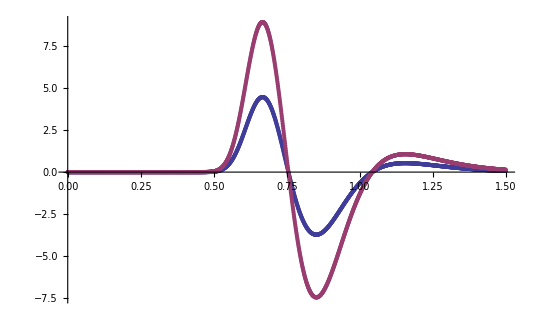
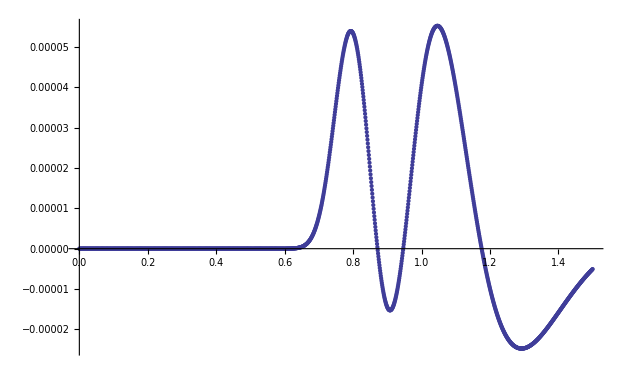

```mathematica
{ListPlot[{pressureset2uave0pt5base,pressureset2uave0pt5damp},PlotRange->All],ListPlot[Table[{pressureset2uave0pt5base[[i,1]],2*pressureset2uave0pt5base[[i,2]]-pressureset2uave0pt5damp[[i,2]]},{i,1,Length[pressureset2uave0pt5base]}],PlotRange->All]}
```

```mathematica
N[0.00005/9]
```

5.55556×10^-6

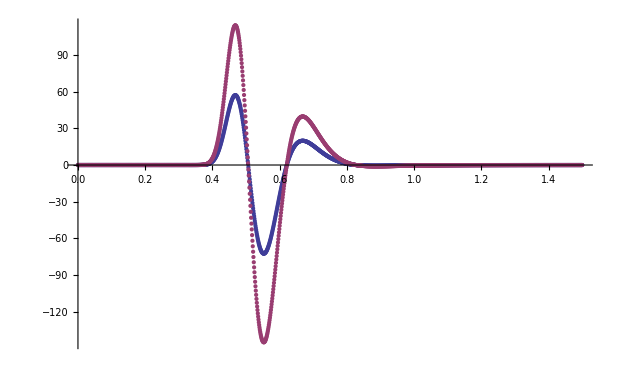
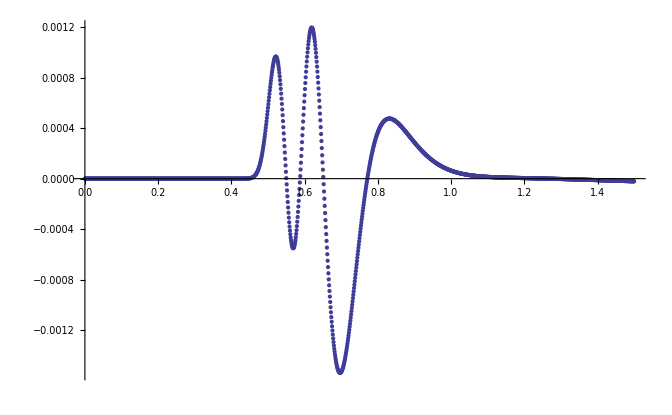

```mathematica
{ListPlot[{pressureset2uave0pt3base,pressureset2uave0pt3damp},PlotRange->All],ListPlot[Table[{pressureset2uave0pt3base[[i,1]],2*pressureset2uave0pt3base[[i,2]]-pressureset2uave0pt3damp[[i,2]]},{i,1,Length[pressureset2uave0pt3base]}],PlotRange->All]}
```

```mathematica
N[0.0012/120]
```

0.00001

```mathematica
Temp={{0.2,0.000012941176470588234},{0.3,9.999999999999999*^-6},{0.4,7.692307692307694*^-6},{0.5,5.555555555555556*^-6},{0.8,3.3333333333333333*^-6}}
```

{{0.2,0.0000129412},{0.3,0.00001},{0.4,7.69231×10^-6},{0.5,5.55556×10^-6},{0.8,3.33333×10^-6}}

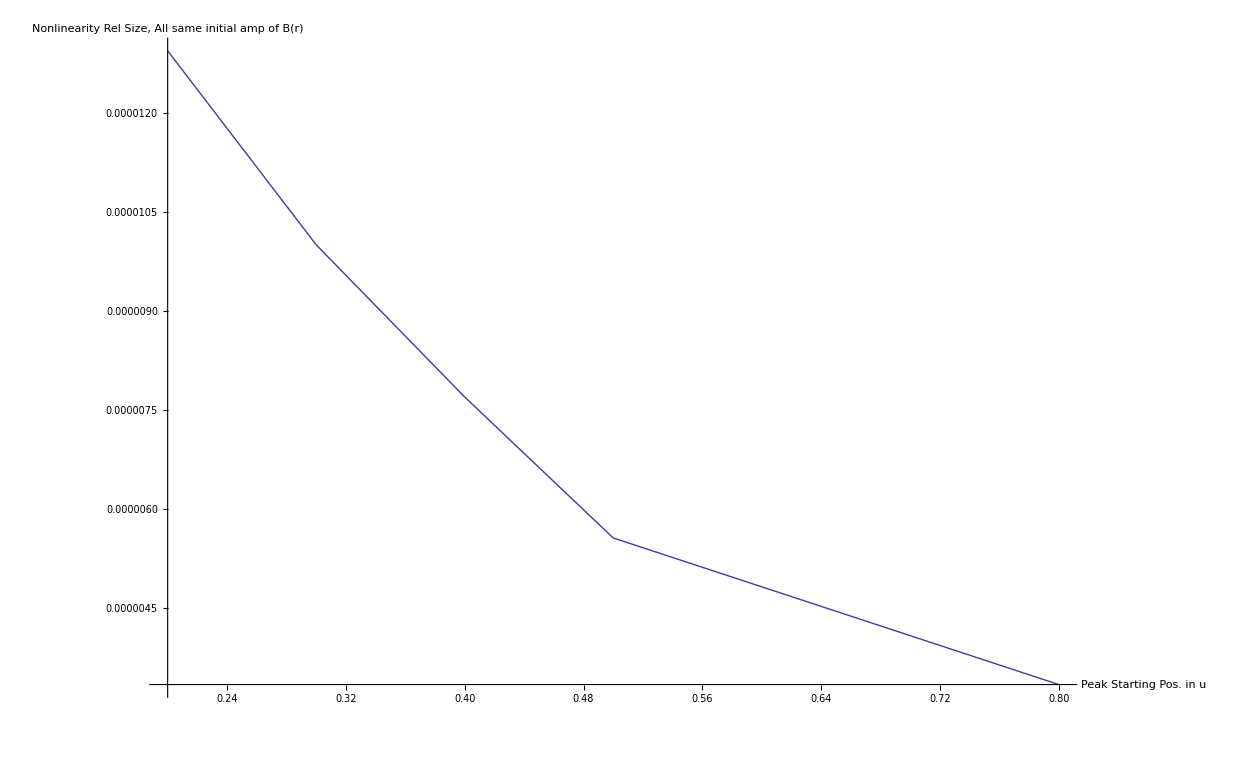

```mathematica
ListPlot[Temp,AxesLabel->{"Peak Starting Pos. in u","Nonlinearity Rel Size, All same initial amp of B(r)"},Joined->True,AxesStyle->Large]
```

```mathematica
A = {{1,2},{1,2},{1,2}}
```

{{1,2},{1,2},{1,2}}

```mathematica
A
```

{{1,2},{1,2},{1,2}}

### Comparing uave change only

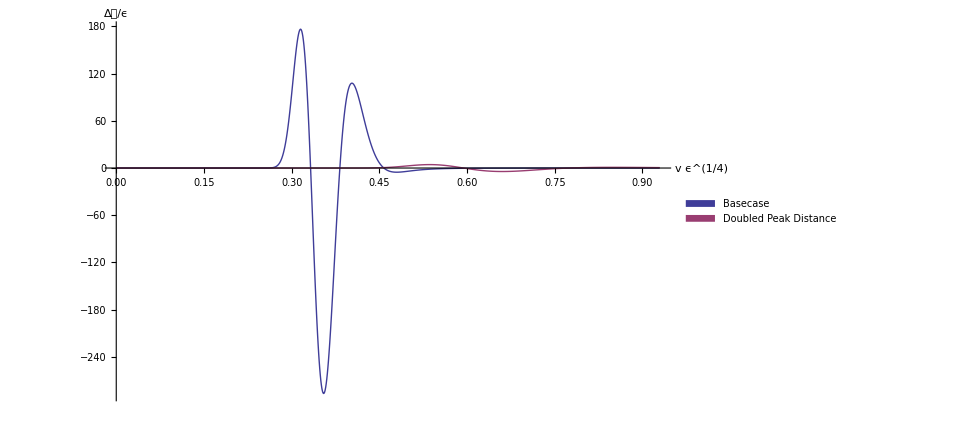

```mathematica
ListPlot[{Table[{pressureset2uave0pt2baseϵ[[i,1]],pressureset2uave0pt2baseϵ[[i,2]]},{i,1,Length[pressureset2uave0pt2base]}][[;;1000]],
pressureset2uave0pt4baseϵ[[;;1000]]},PlotLegends->Placed[SwatchLegend[{Style["Basecase",20],Style["Doubled Peak Distance",20]}],{Right,Top}],AxesStyle->Large,PlotRange->All, AxesLabel ->{"v ϵ^(1/4)","Δ𝒫/ϵ"},Joined->True,PlotStyle->{Directive[Thick]}]
```

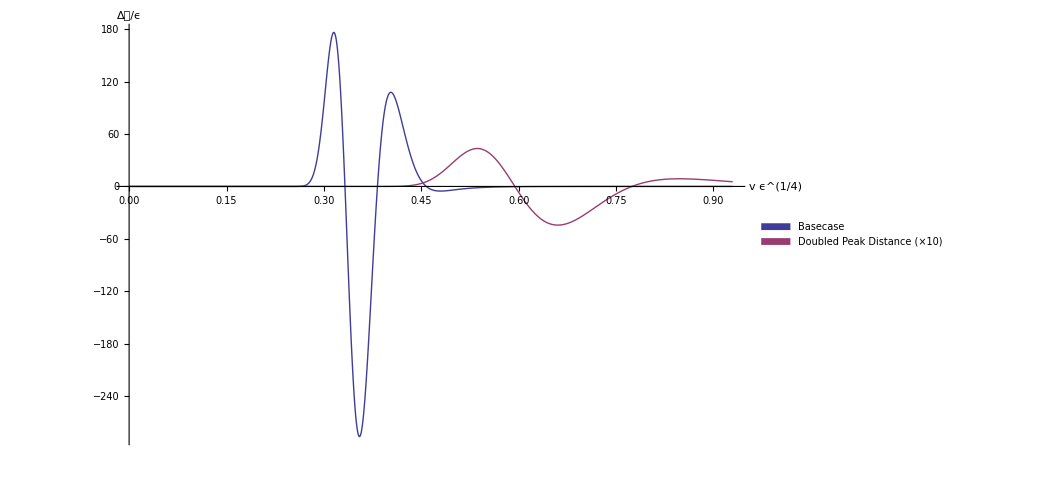

```mathematica
ListPlot[{Table[{pressureset2uave0pt2baseϵ[[i,1]],pressureset2uave0pt2baseϵ[[i,2]]},{i,1,Length[pressureset2uave0pt2base]}][[;;1000]],
Table[{pressureset2uave0pt4baseϵ[[i,1]],10*pressureset2uave0pt4baseϵ[[i,2]]},{i,1,Length[pressureset2uave0pt4base]}][[;;1000]]},PlotLegends->Placed[SwatchLegend[{Style["Basecase",20],Style["Doubled Peak Distance (×10)",20]}],{Right,Top}],AxesStyle->Large,PlotRange->All, AxesLabel ->{"v ϵ^(1/4)","Δ𝒫/ϵ"},Joined->True,PlotStyle->{Directive[Thick]}]
```

## SBB at position 1

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.0025wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.0025wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«5 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«5 more identical outputs»

```mathematica
sigmadot2[1]
```

6.24362×10^-12

6.24362×10^-12

6.24362×10^-12

«2 more identical outputs»

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«5 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.68434×10^-14

5.68434×10^-14

5.68434×10^-14

«2 more identical outputs»

2.77556×10^-17

2.77556×10^-17

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

1.42109×10^-13

1.42109×10^-13

«2 more identical outputs»

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.09495×10^-13

9.09495×10^-13

9.09495×10^-13

«2 more identical outputs»

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

6.21798×10^-10

6.21798×10^-10

6.21798×10^-10

«2 more identical outputs»

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.45697×10^-12

5.45697×10^-12

5.45697×10^-12

«2 more identical outputs»

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96364×10^-12

9.96364×10^-12

9.96364×10^-12

«2 more identical outputs»

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

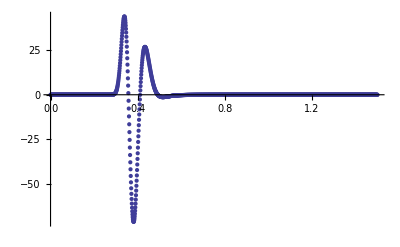

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

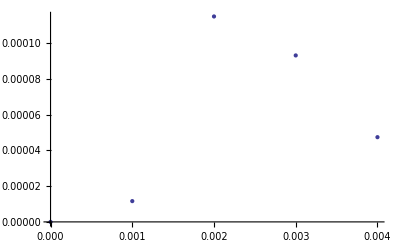

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

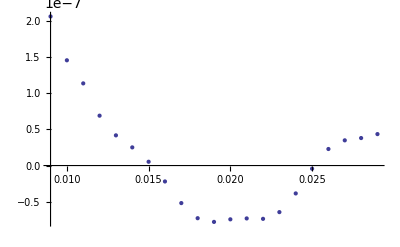

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

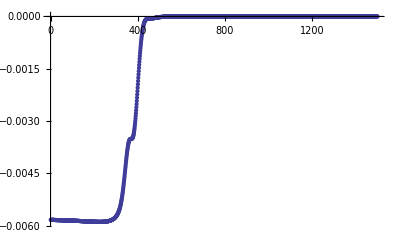

```mathematica
ListPlot[lamblist]
```

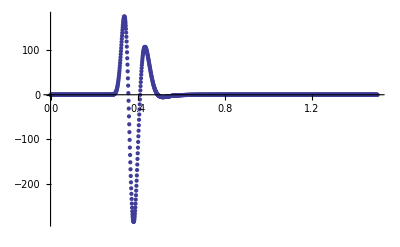

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureset2uave0pt2base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureset2uave0pt2baseϵ= Table[{(3/4(-a2))^(1/4)tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureset2uave0pt2base,PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-5.25559×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.08559

```mathematica
sprod = s - sinitial
```

0.0560003

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## SBB at position 1 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

```mathematica
sigmadot2[1]
```

5.85115×10^-12

-4.61575×10^-13

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.27374×10^-13

1.11022×10^-16

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.50111×10^-12

4.26326×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.50979×10^-9

9.14158×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.18279×10^-11

9.32622×10^-14

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99578×10^-12

9.94838×10^-12

9.94838×10^-12

### Plots

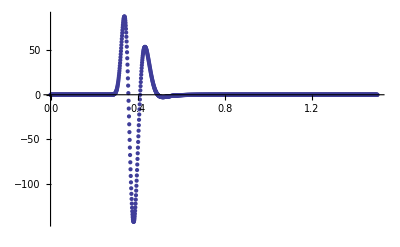

-Graphics-

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

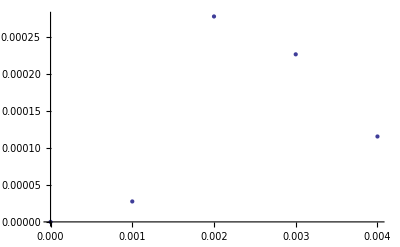

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

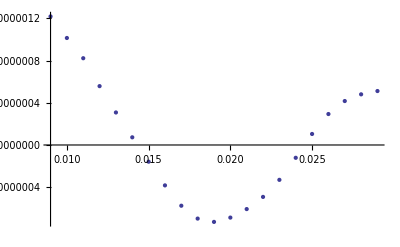

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

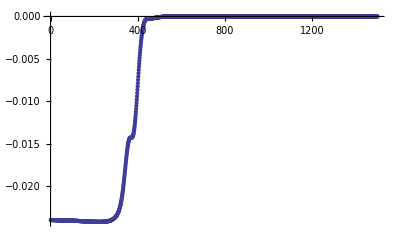

-Graphics-

```mathematica
ListPlot[lamblist]
```

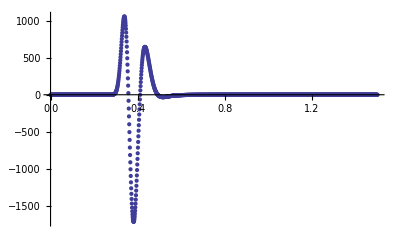

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureset2uave0pt2damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureset2uave0pt2damp,PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

0.31831

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

0.

0.

```mathematica
chem/T
```

0.

0.

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

3/4

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.53675×10^-11

-9.49552×10^-15

-9.49552×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

3.14159

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.9155

3.1415

3.1415

```mathematica
sprod = s - sinitial
```

0.226091

0.0000893332

0.0000893332

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

-0.25

-0.25

## SBB at position 2

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.0025wid0.4uave0.4a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.0025wid0.4uave0.4a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«7 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«6 more identical outputs»

```mathematica
sigmadot2[1]
```

4.59194×10^-12

4.59194×10^-12

4.59194×10^-12

«3 more identical outputs»

6.41409×10^-12

6.41409×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«6 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.66533×10^-16

1.66533×10^-16

1.66533×10^-16

«3 more identical outputs»

6.77626×10^-20

6.77626×10^-20

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

1.7053×10^-13

1.7053×10^-13

«3 more identical outputs»

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.90799×10^-14

3.90799×10^-14

3.90799×10^-14

«3 more identical outputs»

7.77156×10^-16

7.77156×10^-16

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

8.7268×10^-12

8.7268×10^-12

8.7268×10^-12

«3 more identical outputs»

1.98619×10^-13

1.98619×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

«3 more identical outputs»

9.70971×10^-14

9.70971×10^-14

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98479×10^-12

9.98479×10^-12

9.98479×10^-12

«3 more identical outputs»

9.76652×10^-12

9.76652×10^-12

9.94838×10^-12

### Plots

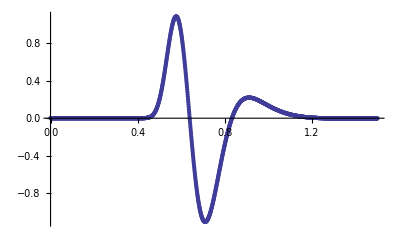

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

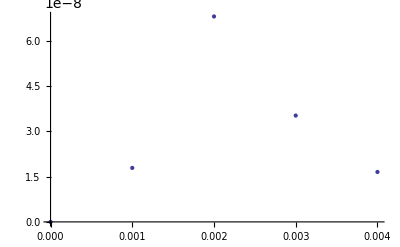

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

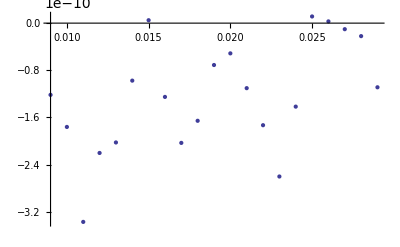

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

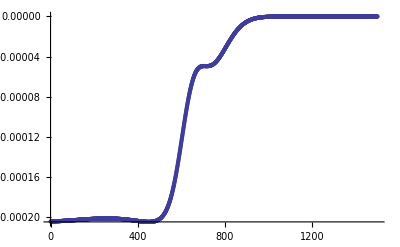

```mathematica
ListPlot[lamblist]
```

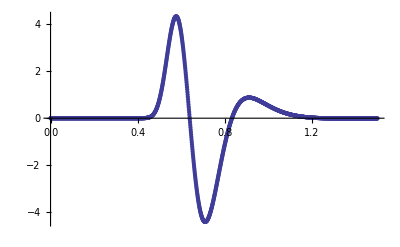

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureset2uave0pt4base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureset2uave0pt4baseϵ= Table[{(3/4(-a2))^(1/4)tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureset2uave0pt4base,PlotRange->All]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-5.76104×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.13941

```mathematica
sprod = s - sinitial
```

0.00218373

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## SBB at position 2 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.4a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.4a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

$Failed

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

```mathematica
sigmadot2[1]
```

-1.93456×10^-12

0.+($Failed)/2+1/2 (1+$Failed+$Failed⟦2⟧)^2

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«3 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.66134×10^-16

2.1684×10^-19

2.1684×10^-19

Abs[$Failed]

Abs[$Failed]

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

1.42109×10^-13

1.42109×10^-13

Abs[$Failed]

Abs[$Failed]

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.23706×10^-14

1.55431×10^-15

1.55431×10^-15

Abs[$Failed]

Abs[$Failed]

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.62255×10^-11

2.11164×10^-13

2.11164×10^-13

Abs[$Failed]

Abs[$Failed]

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.97904×10^-13

1.03129×10^-13

1.03129×10^-13

Abs[$Failed]

Abs[$Failed]

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.83719×10^-12

9.95626×10^-12

9.95626×10^-12

Abs[$Failed]

Abs[$Failed]

9.94838×10^-12

### Plots

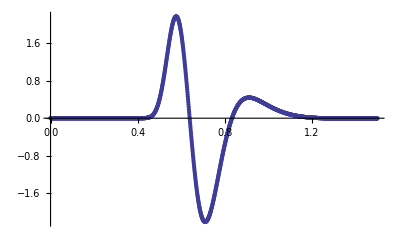

ListPlot[{},PlotRange→All]

-Graphics-

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

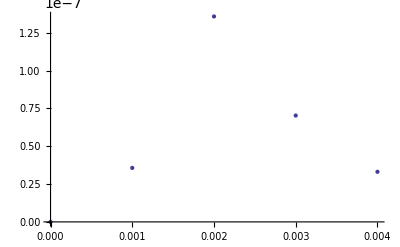

ListPlot[{}⟦1;;5⟧,PlotRange→All]

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

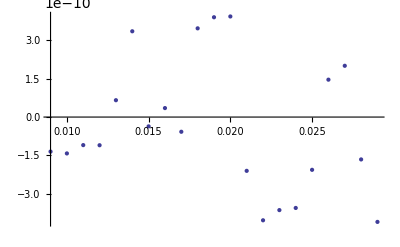

ListPlot[{}⟦10;;30⟧,PlotRange→All]

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

```mathematica
ListPlot[lamblist]
```

-Graphics-

ListPlot[$Failed]

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureset2uave0pt4damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureset2uave0pt4damp,PlotRange->All]
```

-Graphics-

ListPlot[{},PlotRange→All]

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

-(0.-2 (1+Symbol)+$Failed⟦-1⟧)/(4 π)

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

0.

0.

```mathematica
chem/T
```

0.

0.

0.

«3 more identical outputs»

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

3/4

3/4

«3 more identical outputs»

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.30123×10^-8

$Failed⟦-1⟧

-9.49552×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

π (1+2 $Failed⟦-1⟧)^3

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.13285

π (1+2 $Failed⟦1⟧)^3

3.1415

```mathematica
sprod = s - sinitial
```

0.008738

3.49352×10^-6

3.49352×10^-6

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

0.0000893332

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

-0.25

-0.25

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

-0.25

## SBB at position 2.5

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.3a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.3a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

$Failed

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«2 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«3 more identical outputs»

```mathematica
sigmadot2[1]
```

2.8112×10^-12

0.+($Failed)/2+1/2 (1+$Failed+$Failed⟦2⟧)^2

4.59194×10^-12

6.41409×10^-12

6.41409×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«3 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

Abs[$Failed]

0.

0.

0.

«1 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.55431×10^-15

Abs[$Failed]

1.66533×10^-16

6.77626×10^-20

6.77626×10^-20

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

Abs[$Failed]

0.

0.

0.

«1 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

Abs[$Failed]

1.7053×10^-13

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

Abs[$Failed]

0.

0.

0.

«1 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.42109×10^-13

Abs[$Failed]

3.90799×10^-14

7.77156×10^-16

7.77156×10^-16

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.90219×10^-11

Abs[$Failed]

8.7268×10^-12

1.98619×10^-13

1.98619×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.97904×10^-13

Abs[$Failed]

1.56319×10^-13

9.70971×10^-14

9.70971×10^-14

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.84607×10^-12

Abs[$Failed]

9.98479×10^-12

9.76652×10^-12

9.76652×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureset2uave0pt3base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureset2uave0pt3base,PlotRange->All]
```

-Graphics-

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

-(0.-2 (1+Symbol)+$Failed⟦-1⟧)/(4 π)

0.31831

0.31831

0.31831

«1 more identical outputs»

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

0.

0.

«3 more identical outputs»

```mathematica
chem/T
```

0.

0.

0.

«3 more identical outputs»

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

3/4

3/4

«3 more identical outputs»

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.10507×10^-10

$Failed⟦-1⟧

-5.76104×10^-9

-2.30548×10^-12

-2.30548×10^-12

-9.49552×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

π (1+2 $Failed⟦-1⟧)^3

3.14159

3.14159

3.14159

«1 more identical outputs»

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.13345

π (1+2 $Failed⟦1⟧)^3

3.13941

3.14159

3.14159

3.1415

```mathematica
sprod = s - sinitial
```

0.00813868

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

0.00218373

8.73378×10^-7

8.73378×10^-7

0.0000893332

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

-0.25

-0.25

-0.25

«1 more identical outputs»

## SBB at position 2.5 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.005wid0.4uave0.3a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.005wid0.4uave0.3a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

$Failed

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

```mathematica
sigmadot2[1]
```

1.86262×10^-12

0.+($Failed)/2+1/2 (1+$Failed+$Failed⟦2⟧)^2

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«5 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

Abs[$Failed]

0.

0.

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.10543×10^-15

Abs[$Failed]

6.66134×10^-16

2.1684×10^-19

2.1684×10^-19

Abs[$Failed]

Abs[$Failed]

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

Abs[$Failed]

0.

0.

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

Abs[$Failed]

1.7053×10^-13

1.42109×10^-13

1.42109×10^-13

Abs[$Failed]

Abs[$Failed]

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

Abs[$Failed]

0.

0.

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.69482×10^-13

Abs[$Failed]

9.23706×10^-14

1.55431×10^-15

1.55431×10^-15

Abs[$Failed]

Abs[$Failed]

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.70888×10^-10

Abs[$Failed]

3.62255×10^-11

2.11164×10^-13

2.11164×10^-13

Abs[$Failed]

Abs[$Failed]

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.59162×10^-12

Abs[$Failed]

3.97904×10^-13

1.03129×10^-13

1.03129×10^-13

Abs[$Failed]

Abs[$Failed]

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.94349×10^-12

Abs[$Failed]

9.83719×10^-12

9.95626×10^-12

9.95626×10^-12

Abs[$Failed]

Abs[$Failed]

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

ListPlot[{},PlotRange→All]

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

ListPlot[{}⟦1;;5⟧,PlotRange→All]

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

ListPlot[{}⟦10;;30⟧,PlotRange→All]

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

ListPlot[$Failed]

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureset2uave0pt3damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureset2uave0pt3damp,PlotRange->All]
```

-Graphics-

ListPlot[{},PlotRange→All]

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

-(0.-2 (1+Symbol)+$Failed⟦-1⟧)/(4 π)

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

0.

0.

```mathematica
chem/T
```

0.

0.

0.

«5 more identical outputs»

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

3/4

3/4

«5 more identical outputs»

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.24709×10^-10

$Failed⟦-1⟧

-9.49552×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

π (1+2 $Failed⟦-1⟧)^3

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.109

π (1+2 $Failed⟦1⟧)^3

3.1415

```mathematica
sprod = s - sinitial
```

0.0325973

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

0.008738

3.49352×10^-6

3.49352×10^-6

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

0.0000893332

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

-0.25

-0.25

-0.25

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

-0.25

## SBB at position 3

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.8a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.8a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«3 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«1 more identical outputs»

```mathematica
sigmadot2[1]
```

-1.36002×10^-13

3.03146×10^-12

3.03146×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«1 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«1 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.30104×10^-18

4.76456×10^-22

4.76456×10^-22

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«1 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

1.98952×10^-13

1.98952×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«1 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.66454×10^-15

5.20417×10^-17

5.20417×10^-17

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.32481×10^-13

2.39586×10^-13

2.39586×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.31477×10^-14

8.42754×10^-14

8.42754×10^-14

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.75536×10^-12

9.82026×10^-12

9.82026×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureset2uave0pt8base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureset2uave0pt8base,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

0.31831

0.31831

«1 more identical outputs»

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

0.

0.

«1 more identical outputs»

```mathematica
chem/T
```

0.

0.

0.

«1 more identical outputs»

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

3/4

3/4

«1 more identical outputs»

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.1227×10^-8

-1.24909×10^-11

-1.24909×10^-11

-9.49552×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

3.14159

3.14159

«1 more identical outputs»

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.14147

3.14159

3.14159

3.1415

```mathematica
sprod = s - sinitial
```

0.000117641

4.70378×10^-8

4.70378×10^-8

0.0000893332

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

-0.25

-0.25

«1 more identical outputs»

## SBB at position 3 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.8a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.8a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.8a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0001wid0.8uave0.4a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.0001wid0.8uave0.4a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.4a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

$Failed

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

```mathematica
sigmadot2[1]
```

-2.42373×10^-12

0.+($Failed)/2+1/2 (1+$Failed+$Failed⟦2⟧)^2

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«2 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.33681×10^-18

1.90582×10^-21

Abs[$Failed]

Abs[$Failed]

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

1.98952×10^-13

Abs[$Failed]

Abs[$Failed]

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.54952×10^-15

1.31839×10^-16

Abs[$Failed]

Abs[$Failed]

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.33351×10^-13

2.01617×10^-13

Abs[$Failed]

Abs[$Failed]

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

8.63754×10^-14

9.77898×10^-14

Abs[$Failed]

Abs[$Failed]

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96025×10^-12

9.73877×10^-12

Abs[$Failed]

Abs[$Failed]

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

ListPlot[{},PlotRange→All]

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

ListPlot[{}⟦1;;5⟧,PlotRange→All]

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

ListPlot[{}⟦10;;30⟧,PlotRange→All]

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

ListPlot[$Failed]

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureset2uave0pt8damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureset2uave0pt8damp,PlotRange->All]
```

-Graphics-

ListPlot[{},PlotRange→All]

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

-(0.-2 (1+Symbol)+$Failed⟦-1⟧)/(4 π)

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

0.

0.

```mathematica
chem/T
```

0.

0.

0.

«2 more identical outputs»

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

3/4

3/4

«2 more identical outputs»

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.24906×10^-7

$Failed⟦-1⟧

-9.49552×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

π (1+2 $Failed⟦-1⟧)^3

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.14112

π (1+2 $Failed⟦1⟧)^3

3.1415

```mathematica
sprod = s - sinitial
```

0.000470572

1.88177×10^-7

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

0.0000893332

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.249999

-0.25

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

-0.25

## SBB at position 3.5 (B not cut by horizon)

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0025wid0.4uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0025wid0.4uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«4 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«2 more identical outputs»

```mathematica
sigmadot2[1]
```

5.3087×10^-12

-1.36002×10^-13

3.03146×10^-12

3.03146×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«2 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«2 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.08167×10^-17

1.30104×10^-18

4.76456×10^-22

4.76456×10^-22

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«2 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

1.7053×10^-13

1.98952×10^-13

1.98952×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«2 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.77636×10^-14

2.66454×10^-15

5.20417×10^-17

5.20417×10^-17

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.70983×10^-12

2.32481×10^-13

2.39586×10^-13

2.39586×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.13687×10^-13

9.31477×10^-14

8.42754×10^-14

8.42754×10^-14

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.76552×10^-12

9.75536×10^-12

9.82026×10^-12

9.82026×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureset2uave0pt5base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureset2uave0pt5base,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

0.31831

0.31831

«2 more identical outputs»

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

0.

0.

«2 more identical outputs»

```mathematica
chem/T
```

0.

0.

0.

«2 more identical outputs»

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

3/4

3/4

«2 more identical outputs»

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.15927×10^-8

-3.1227×10^-8

-1.24909×10^-11

-1.24909×10^-11

-9.49552×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

3.14159

3.14159

«2 more identical outputs»

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.14077

3.14147

3.14159

3.14159

3.1415

```mathematica
sprod = s - sinitial
```

0.000818106

0.000117641

4.70378×10^-8

4.70378×10^-8

0.0000893332

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

-0.25

-0.25

«2 more identical outputs»

## SBB at position 3.5 (B not cut by horizon) doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.4uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.4uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

$Failed

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

```mathematica
sigmadot2[1]
```

2.39586×10^-13

0.+($Failed)/2+1/2 (1+$Failed+$Failed⟦2⟧)^2

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«3 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.38778×10^-16

4.33681×10^-18

1.90582×10^-21

Abs[$Failed]

Abs[$Failed]

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

1.56319×10^-13

1.98952×10^-13

Abs[$Failed]

Abs[$Failed]

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

Abs[$Failed]

Abs[$Failed]

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.90799×10^-14

7.54952×10^-15

1.31839×10^-16

Abs[$Failed]

Abs[$Failed]

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.0536×10^-11

5.33351×10^-13

2.01617×10^-13

Abs[$Failed]

Abs[$Failed]

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.27898×10^-13

8.63754×10^-14

9.77898×10^-14

Abs[$Failed]

Abs[$Failed]

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98701×10^-12

9.96025×10^-12

9.73877×10^-12

Abs[$Failed]

Abs[$Failed]

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

ListPlot[{},PlotRange→All]

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

ListPlot[{}⟦1;;5⟧,PlotRange→All]

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

ListPlot[{}⟦10;;30⟧,PlotRange→All]

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

ListPlot[$Failed]

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureset2uave0pt5damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureset2uave0pt5damp,PlotRange->All]
```

-Graphics-

ListPlot[{},PlotRange→All]

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

-(0.-2 (1+Symbol)+$Failed⟦-1⟧)/(4 π)

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

0.

0.

```mathematica
chem/T
```

0.

0.

0.

«3 more identical outputs»

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

3/4

3/4

«3 more identical outputs»

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.63649×10^-8

$Failed⟦-1⟧

-9.49552×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

π (1+2 $Failed⟦-1⟧)^3

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.13832

π (1+2 $Failed⟦1⟧)^3

3.1415

```mathematica
sprod = s - sinitial
```

0.00327287

0.000470572

1.88177×10^-7

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

π (1+2 $Failed⟦-1⟧)^3-π (1+2 $Failed⟦1⟧)^3

0.0000893332

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

-0.249999

-0.25

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

3/4+1/4 (0.-2 (1+Symbol)+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

-0.25

RN

We now do the same test pulses again, but with the RN BB at 80 percent of extremality.

Again, we see a relative size of 10^-8, no matter the position in the bulk.

```mathematica
{ListPlot[{pressureRNuave0pt2base,pressureRNuave0pt2damp},PlotRange->All],ListPlot[Table[{pressureRNuave0pt2base[[i,1]],2*pressureRNuave0pt2base[[i,2]]-pressureRNuave0pt2damp[[i,2]]},{i,1,Length[pressureRNuave0pt2base]}],PlotRange->All]}
```

{-Graphics-,-Graphics-}

```mathematica
{ListPlot[{pressureRNuave0pt4base,pressureRNuave0pt4damp},PlotRange->All],ListPlot[Table[{pressureRNuave0pt4base[[i,1]],2*pressureRNuave0pt4base[[i,2]]-pressureRNuave0pt4damp[[i,2]]},{i,1,Length[pressureRNuave0pt4base]}],PlotRange->All]}
```

{-Graphics-,-Graphics-}

```mathematica
{ListPlot[{pressureRNuave0pt8base,pressureRNuave0pt8damp},PlotRange->All],ListPlot[Table[{pressureRNuave0pt8base[[i,1]],2*pressureRNuave0pt8base[[i,2]]-pressureRNuave0pt8damp[[i,2]]},{i,1,Length[pressureRNuave0pt8base]}],PlotRange->All]}
```

{-Graphics-,-Graphics-}

## RN at position 1

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.859655945459;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp5e-05wid0.4uave0.2a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp5e-05wid0.4uave0.2a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«3 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«3 more identical outputs»

```mathematica
sigmadot2[1]
```

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«3 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«3 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«3 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«3 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureRNuave0pt2base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureRNuave0pt2base,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.05384×10^-16

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.4223

```mathematica
sprod = s - sinitial
```

0.0000307199

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## RN at position 1 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.859655945459;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.2a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«5 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«5 more identical outputs»

```mathematica
sigmadot2[1]
```

5.85115×10^-12

2.81108×10^-12

2.81108×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«5 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.27374×10^-13

1.66533×10^-16

1.66533×10^-16

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«1 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.50111×10^-12

3.55271×10^-14

3.55271×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.50979×10^-9

1.50913×10^-12

1.50913×10^-12

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.18279×10^-11

8.70415×10^-14

8.70415×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99578×10^-12

9.9124×10^-12

9.9124×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureRNuave0pt2damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureRNuave0pt2damp,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.429828

```mathematica
chem/T
```

-1.35034

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.53675×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.9155

```mathematica
sprod = s - sinitial
```

0.226091

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## RN at position 2

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.859655945459;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp5e-05wid0.4uave0.4a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp5e-05wid0.4uave0.4a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«4 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«4 more identical outputs»

```mathematica
sigmadot2[1]
```

8.01936×10^-12

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«4 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«4 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.77626×10^-20

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«4 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

«1 more identical outputs»

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«4 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

8.88178×10^-16

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.00395×10^-13

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.47211×10^-14

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.81532×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureRNuave0pt4base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureRNuave0pt4base,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.03292×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.42233

```mathematica
sprod = s - sinitial
```

1.20224×10^-6

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## RN at position 2 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.859655945459;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.4a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.4a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«6 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«6 more identical outputs»

```mathematica
sigmadot2[1]
```

6.0148×10^-12

2.81108×10^-12

2.81108×10^-12

2.81108×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«6 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.71051×10^-19

1.66533×10^-16

1.66533×10^-16

1.66533×10^-16

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«1 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

1.7053×10^-13

1.7053×10^-13

«1 more identical outputs»

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.77636×10^-15

3.55271×10^-14

3.55271×10^-14

3.55271×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.34923×10^-13

1.50913×10^-12

1.50913×10^-12

1.50913×10^-12

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.14439×10^-14

8.70415×10^-14

8.70415×10^-14

8.70415×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.93106×10^-12

9.9124×10^-12

9.9124×10^-12

9.9124×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureRNuave0pt4damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureRNuave0pt4damp,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.13166×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.42233

```mathematica
sprod = s - sinitial
```

4.80911×10^-6

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## RN at position 3

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.859655945459;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp5e-05wid0.4uave0.8a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp5e-05wid0.4uave0.8a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«4 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«4 more identical outputs»

```mathematica
sigmadot2[1]
```

6.80511×10^-13

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«4 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«4 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.76456×10^-22

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«4 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«4 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.85723×10^-17

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.9218×10^-13

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

8.39729×10^-14

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.88171×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureRNuave0pt8base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureRNuave0pt8base,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.37893×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.42233

```mathematica
sprod = s - sinitial
```

6.5648×10^-8

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## RN at position 3 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.859655945459;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.8a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0001wid0.4uave0.8a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«6 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«5 more identical outputs»

```mathematica
sigmadot2[1]
```

1.65268×10^-12

2.81108×10^-12

2.81108×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«5 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.32934×10^-21

1.66533×10^-16

1.66533×10^-16

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«1 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.71445×10^-17

3.55271×10^-14

3.55271×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.92291×10^-13

1.50913×10^-12

1.50913×10^-12

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.48189×10^-14

8.70415×10^-14

8.70415×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.75947×10^-12

9.9124×10^-12

9.9124×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureRNuave0pt8damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureRNuave0pt8damp,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-5.5157×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.42233

```mathematica
sprod = s - sinitial
```

2.62658×10^-7

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

Again with more amplitude

```mathematica
{ListPlot[{pressureRNset2uave0pt2base,pressureRNset2uave0pt2damp},PlotRange->All],ListPlot[Table[{pressureRNset2uave0pt2base[[i,1]],2*pressureRNset2uave0pt2base[[i,2]]-pressureRNset2uave0pt2damp[[i,2]]},{i,1,Length[pressureRNset2uave0pt2base]}],PlotRange->All]}
```

{-Graphics-,-Graphics-}

```mathematica
{ListPlot[{pressureRNset2uave0pt4base,pressureRNset2uave0pt4damp},PlotRange->All],ListPlot[Table[{pressureRNset2uave0pt4base[[i,1]],2*pressureRNset2uave0pt4base[[i,2]]-pressureRNset2uave0pt4damp[[i,2]]},{i,1,Length[pressureRNset2uave0pt4base]}],PlotRange->All]}
```

{-Graphics-,-Graphics-}

```mathematica
{ListPlot[{pressureRNset2uave0pt8base,pressureRNset2uave0pt8damp},PlotRange->All],ListPlot[Table[{pressureRNset2uave0pt8base[[i,1]],2*pressureRNset2uave0pt8base[[i,2]]-pressureRNset2uave0pt8damp[[i,2]]},{i,1,Length[pressureRNset2uave0pt8base]}],PlotRange->All]}
```

{-Graphics-,-Graphics-}

## RN at position 1

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.859655945459;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.2a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.2a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«5 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«5 more identical outputs»

```mathematica
sigmadot2[1]
```

-6.76598×10^-12

-5.78854×10^-12

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«5 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.68434×10^-14

2.27374×10^-13

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

«2 more identical outputs»

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.09495×10^-13

2.27374×10^-12

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.04844×10^-9

4.19981×10^-9

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.09139×10^-11

4.36557×10^-11

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97585×10^-12

9.99956×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureRNset2uave0pt2base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureRNset2uave0pt2base,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.78985×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.34444

```mathematica
sprod = s - sinitial
```

0.0778907

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## RN at position 1 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.859655945459;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.2a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.2a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«6 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«6 more identical outputs»

```mathematica
sigmadot2[1]
```

-5.78854×10^-12

5.85115×10^-12

2.81108×10^-12

2.81108×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«6 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.27374×10^-13

2.27374×10^-13

1.66533×10^-16

1.66533×10^-16

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«1 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.27374×10^-12

2.50111×10^-12

3.55271×10^-14

3.55271×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.19981×10^-9

2.50979×10^-9

1.50913×10^-12

1.50913×10^-12

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

4.36557×10^-11

2.18279×10^-11

8.70415×10^-14

8.70415×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99956×10^-12

9.99578×10^-12

9.9124×10^-12

9.9124×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureRNset2uave0pt2damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureRNset2uave0pt2damp,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-9.85048×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.09454

```mathematica
sprod = s - sinitial
```

0.327791

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## RN at position 2

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.859655945459;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.4a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.4a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«6 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«6 more identical outputs»

```mathematica
sigmadot2[1]
```

7.1082×10^-13

7.1082×10^-13

8.01936×10^-12

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«6 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.66533×10^-16

1.66533×10^-16

6.77626×10^-20

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

«3 more identical outputs»

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.9738×10^-14

4.9738×10^-14

8.88178×10^-16

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.47503×10^-11

1.47503×10^-11

2.00395×10^-13

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.7053×10^-13

1.7053×10^-13

9.47211×10^-14

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96164×10^-12

9.96164×10^-12

9.81532×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureRNset2uave0pt4base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureRNset2uave0pt4base,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-5.08118×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.41932

```mathematica
sprod = s - sinitial
```

0.00300732

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## RN at position 2 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.859655945459;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.4a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.4a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«8 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«8 more identical outputs»

```mathematica
sigmadot2[1]
```

3.12905×10^-12

3.12905×10^-12

6.0148×10^-12

2.81108×10^-12

2.81108×10^-12

2.81108×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«8 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«8 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.66134×10^-16

6.66134×10^-16

2.71051×10^-19

1.66533×10^-16

1.66533×10^-16

1.66533×10^-16

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«1 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«8 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.7053×10^-13

«1 more identical outputs»

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«8 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.06581×10^-13

1.06581×10^-13

1.77636×10^-15

3.55271×10^-14

3.55271×10^-14

3.55271×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.85717×10^-11

5.85717×10^-11

2.34923×10^-13

1.50913×10^-12

1.50913×10^-12

1.50913×10^-12

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.68434×10^-13

5.68434×10^-13

9.14439×10^-14

8.70415×10^-14

8.70415×10^-14

8.70415×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.9829×10^-12

9.9829×10^-12

9.93106×10^-12

9.9124×10^-12

9.9124×10^-12

9.9124×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureRNset2uave0pt4damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureRNset2uave0pt4damp,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.03115×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.41028

```mathematica
sprod = s - sinitial
```

0.0120487

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## RN at position 3

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.859655945459;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.8a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.8a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«5 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«5 more identical outputs»

```mathematica
sigmadot2[1]
```

-1.03362×10^-12

6.80511×10^-13

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«5 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.51788×10^-18

4.76456×10^-22

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

1.7053×10^-13

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.77476×10^-15

4.85723×10^-17

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.0842×10^-13

1.9218×10^-13

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.48321×10^-14

8.39729×10^-14

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.91024×10^-12

9.88171×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureRNset2uave0pt8base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureRNset2uave0pt8base,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.44722×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.42217

```mathematica
sprod = s - sinitial
```

0.000164195

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## RN at position 3 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.859655945459;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.8a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.8a2-1.0f30.859655945459fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«7 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«6 more identical outputs»

```mathematica
sigmadot2[1]
```

6.51312×10^-13

1.65268×10^-12

2.81108×10^-12

2.81108×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«6 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.07153×10^-18

2.32934×10^-21

1.66533×10^-16

1.66533×10^-16

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«1 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.10543×10^-15

9.71445×10^-17

3.55271×10^-14

3.55271×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

8.73523×10^-13

1.92291×10^-13

1.50913×10^-12

1.50913×10^-12

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.14824×10^-14

9.48189×10^-14

8.70415×10^-14

8.70415×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.9516×10^-12

9.75947×10^-12

9.9124×10^-12

9.9124×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureRNset2uave0pt8damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureRNset2uave0pt8damp,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231414

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.37877×10^-7

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.42167

```mathematica
sprod = s - sinitial
```

0.000656838

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189438

```mathematica
0.1894371418290004
```

0.189437

Now we can compare the differences between 80% and 0%

```mathematica
{ListPlot[{pressureRNuave0pt2base,pressureuave0pt2base},PlotRange->All],ListPlot[Table[{pressureRNuave0pt2base[[i,1]],pressureRNuave0pt2base[[i,2]] -pressureuave0pt2base[[i,2]]},{i,1,Length[pressureRNuave0pt2base]}],PlotRange->All]}
```

{-Graphics-,-Graphics-}

```mathematica
{ListPlot[{pressureRNuave0pt4base,pressureuave0pt4base},PlotRange->All],ListPlot[Table[{pressureRNuave0pt4base[[i,1]],pressureRNuave0pt4base[[i,2]]-pressureuave0pt4base[[i,2]]},{i,1,Length[pressureRNuave0pt4base]}],PlotRange->All]}
```

{-Graphics-,-Graphics-}

```mathematica
{ListPlot[{pressureRNuave0pt8base,pressureuave0pt8base},PlotRange->All],ListPlot[Table[{pressureRNuave0pt8base[[i,1]],pressureRNuave0pt8base[[i,2]]-pressureuave0pt8base[[i,2]]},{i,1,Length[pressureRNuave0pt8base]}],PlotRange->All]}
```

{-Graphics-,-Graphics-}

RN 80 vs SBB for both amplitude sizes

MAG (This is broken, since we’d need to double the log terms as well, and yet the log terms are set via asymptotics.  So instead we’ll do the superposition (dual gaussian) test below.

```mathematica
{ListPlot[{pressureMAGuave0pt2base,pressureMAGuave0pt2damp},PlotRange->All],ListPlot[Table[{pressureMAGuave0pt2base[[i,1]],2*pressureMAGuave0pt2base[[i,2]]-pressureMAGuave0pt2damp[[i,2]]},{i,1,Length[pressureMAGuave0pt2base]}],PlotRange->All],
ListPlot[Table[{pressureMAGuave0pt2base[[i,1]],pressureMAGuave0pt2base[[i,2]]-pressureMAGuave0pt2damp[[i,2]]},{i,800,Length[pressureMAGuave0pt2base]}],PlotRange->All]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ListPlot[{pressureMAGuave0pt4base,pressureMAGuave0pt4damp},PlotRange->All],ListPlot[Table[{pressureMAGuave0pt4base[[i,1]],2*pressureMAGuave0pt4base[[i,2]]-pressureMAGuave0pt4damp[[i,2]]},{i,1,Length[pressureMAGuave0pt4base]}],PlotRange->All]}
```

{-Graphics-,-Graphics-}

```mathematica
{ListPlot[{pressureMAGuave0pt8base,pressureMAGuave0pt8damp},PlotRange->All],ListPlot[Table[{pressureMAGuave0pt8base[[i,1]],2*pressureMAGuave0pt8base[[i,2]]-pressureMAGuave0pt8damp[[i,2]]},{i,1,Length[pressureMAGuave0pt8base]}],PlotRange->All]}
```

{-Graphics-,-Graphics-}

## MAG at position 1

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.2a2-1.0f30.0fxy2.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.2a2-1.0f30.0fxy2.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

$Failed

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«5 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«7 more identical outputs»

```mathematica
sigmadot2[1]
```

2.72671×10^-12

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-1.21667,-1.21661,-1.21642,-1.2161,-1.21565,-1.21507,-1.21437,-1.21353,-1.21257,-1.21148,-1.21026,-1.20892,-1.20744,-1.20584,-1.20411,-1.20225,-1.20026,-1.19814,-1.1959,-1.19352,-1.19102,-1.18839,-1.18563,-1.18275,-1.17973,-1.17659,-1.17332,-1.16992,-1.1664,-1.16275,-1.15897,-1.15506,-1.15104,-1.14688,-1.1426,-1.1382,-1.13367,-1.12903,-1.12426,-1.11937,-1.11435,-1.10923,-1.10398,-1.09861,-1.09313,-1.08754,-1.08183,-1.07602,-1.07009,-1.06405,-1.05791,-1.05166,-1.04531,-1.03885,-1.0323,-1.02565,-1.01891,-1.01207,-1.00514,-0.998119,-0.991014,-0.983825,-0.976555,-0.969205,-0.96178,-0.95428,-0.94671,-0.939071,-0.931368,-0.923601,-0.915775,-0.907892,-0.899955,-0.891967,-0.883932,-0.875851,-0.867729,-0.859568,-0.851371,-0.843141,-0.834882,-0.826596,-0.818287,-0.809957,-0.801609,-0.793246,-0.784872,-0.776489,-0.768099,-0.759707,-0.751314,-0.742923,-0.734537,-0.726158,-0.717789,-0.709432,-0.70109,-0.692765,-0.68446,-0.676175,-0.667914,-0.659678,-0.65147,-0.643291,-0.635142,-0.627026,-0.618943,-0.610897,-0.602886,-0.594914,-0.586981,-0.579088,-0.571236,-0.563426,-0.55566,-0.547937,-0.540258,-0.532624,-0.525036,-0.517493,-0.509997,-0.502547,-0.495144,-0.487788,-0.480479,-0.473217,-0.466002,-0.458834,-0.451713,-0.44464,-0.437613,-0.430632,-0.423699,-0.416812,-0.409971,-0.403176,-0.396426,-0.389723,-0.383065,-0.376452,-0.369884,-0.363361,-0.356883,-0.35045,-0.344061,-0.337717,-0.331418,-0.325163,-0.318953,-0.312788,-0.306668,-0.300593,-0.294564,-0.28858,-0.282642,-0.276751,-0.270907,-0.265111,-0.259363,-0.253664,-0.248016,-0.24242,-0.236878,-0.231394,-0.22597,-0.220613,-0.215328,-0.210118,-0.204988,-0.199937,-0.194968,-0.190088,-0.185301,-0.180601,-0.175955,-0.171307,-0.166613,-0.161868,-0.1571,-0.152347,-0.147637,-0.142982,-0.138388,-0.133857,-0.12939,-0.124989,-0.120653,-0.116385,-0.112184,-0.108051,-0.103987,-0.0999925,-0.0960686,-0.0922158,-0.0884347,-0.0847259,-0.0810901,-0.0775278,-0.0740398,-0.0706265,-0.0672886,-0.0640265,-0.0608408,-0.0577319,-0.0547005,-0.0517469,-0.0488716,-0.046075,-0.0433576,-0.0407198,-0.038162,-0.0356845,-0.0332877,-0.030972,-0.0287377,-0.026585,-0.0245144,-0.0225262,-0.0206205,-0.0187976,-0.0170579,-0.0154016,-0.0138288,-0.0123398,-0.0109348,-0.00961403,-0.00837761,-0.00722574,-0.00615857,-0.00517625,-0.0042789,-0.00346664,-0.0027396,-0.00209786,-0.00154151,-0.00107062,-0.000685267,-0.000385493,-0.00017134,-0.0000428363,0.}⟦j⟧+1/2 ((1.10897+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.00594168,-0.00594251,-0.005945,-0.00594915,-0.00595498,-0.00596248,-0.00597168,-0.00598259,-0.00599522,-0.00600959,-0.00602573,-0.00604366,-0.0060634,-0.006085,-0.00610847,-0.00613386,-0.0061612,-0.00619054,-0.0062219,-0.00625534,-0.0062909,-0.00632863,-0.00636858,-0.0064108,-0.00645535,-0.00650227,-0.00655164,-0.0066035,-0.00665792,-0.00671496,-0.00677468,-0.00683715,-0.00690243,-0.00697059,-0.0070417,-0.00711583,-0.00719305,-0.00727342,-0.00735702,-0.00744392,-0.00753418,-0.00762789,-0.00772511,-0.00782592,-0.00793038,-0.00803856,-0.00815054,-0.00826639,-0.00838617,-0.00850994,-0.00863779,-0.00876976,-0.00890592,-0.00904634,-0.00919107,-0.00934017,-0.00949369,-0.00965169,-0.00981421,-0.0099813,-0.010153,-0.0103294,-0.0105104,-0.0106962,-0.0108867,-0.011082,-0.0112821,-0.011487,-0.0116968,-0.0119114,-0.0121308,-0.012355,-0.0125841,-0.0128179,-0.0130566,-0.0133,-0.0135481,-0.0138009,-0.0140584,-0.0143204,-0.014587,-0.0148581,-0.0151336,-0.0154134,-0.0156974,-0.0159856,-0.0162778,-0.016574,-0.016874,-0.0171777,-0.0174851,-0.0177959,-0.01811,-0.0184274,-0.0187478,-0.019071,-0.0193971,-0.0197257,-0.0200567,-0.02039,-0.0207254,-0.0210627,-0.0214017,-0.0217423,-0.0220844,-0.0224276,-0.022772,-0.0231173,-0.0234634,-0.0238101,-0.0241574,-0.0245051,-0.024853,-0.0252013,-0.0255496,-0.0258981,-0.0262468,-0.0265956,-0.0269446,-0.027294,-0.0276438,-0.0279943,-0.0283457,-0.0286983,-0.0290527,-0.0294091,-0.0297682,-0.0301308,-0.0304974,-0.0308692,-0.031247,-0.0316322,-0.032026,-0.0324302,-0.0328464,-0.0332766,-0.0337233,-0.0341889,-0.0346765,-0.0351892,-0.0357308,-0.0363054,-0.0369177,-0.037573,-0.038277,-0.0390364,-0.0398585,-0.0407514,-0.0417244,-0.0427877,-0.0439528,-0.0452323,-0.0466405,-0.0481931,-0.0499076,-0.0518029,-0.0539001,-0.0562211,-0.0587891,-0.0616259,-0.06475,-0.0681708,-0.0718803,-0.0758399,-0.0799637,-0.0841,-0.088021,-0.0914287,-0.0939752,-0.095268,-0.094807,-0.0918717,-0.0855731,-0.0753819,-0.0620247,-0.0478344,-0.0357104,-0.027369,-0.0226334,-0.0202569,-0.019048,-0.018305,-0.0177154,-0.0171649,-0.01662,-0.0160736,-0.0155252,-0.0149755,-0.0144254,-0.0138756,-0.0133271,-0.0127807,-0.0122373,-0.0116977,-0.0111628,-0.0106334,-0.0101104,-0.0095946,-0.00908681,-0.00858782,-0.00809842,-0.00761935,-0.00715135,-0.00669511,-0.0062513,-0.00582055,-0.00540346,-0.00500059,-0.00461245,-0.0042395,-0.00388218,-0.00354084,-0.00321581,-0.00290735,-0.00261565,-0.00234087,-0.00208308,-0.00184228,-0.00161844,-0.00141143,-0.00122106,-0.00104706,-0.00088911,-0.00074679,-0.000619624,-0.000507059,-0.000408469,-0.000323157,-0.000250357,-0.000189234,-0.000138892,-0.0000983729,-0.0000666668,-0.000042717,-0.0000254293,-0.0000136872,-6.36105×10^-6,-2.34556×10^-6,-5.58502×10^-7,-4.15848×10^-8,0.}⟦j⟧))^2

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«8 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

Abs[$Failed]

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.68434×10^-14

5.68434×10^-14

Abs[$Failed]

5.68434×10^-14

5.68434×10^-14

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

Abs[$Failed]

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

1.98952×10^-13

Abs[$Failed]

1.98952×10^-13

1.98952×10^-13

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

Abs[$Failed]

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.0516×10^-12

1.0516×10^-12

Abs[$Failed]

1.0516×10^-12

1.0516×10^-12

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.01125×10^-9

1.01125×10^-9

Abs[$Failed]

1.01125×10^-9

1.01125×10^-9

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.09495×10^-12

9.09495×10^-12

Abs[$Failed]

9.09495×10^-12

9.09495×10^-12

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99378×10^-12

9.99378×10^-12

Abs[$Failed]

9.99378×10^-12

9.99378×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[500;;]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
(*templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureMAGuave0pt2base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];*)
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(-1/4 a2); (* Better for fxy comparison*)
pressureMAGuave0pt2base= Table[{tlist[[i]],templist[[i]]-templist[[1]]},{i,1,Length[tlist]}];
ListPlot[pressureMAGuave0pt2base,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.422196

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0143337

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.42836

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

4.21264

```mathematica
sprod = s - sinitial
```

0.215715

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.11963

## MAG at position 1 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.2a2-1.0f30.0fxy2.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.2a2-1.0f30.0fxy2.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

$Failed

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«7 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«9 more identical outputs»

```mathematica
sigmadot2[1]
```

2.5181×10^-12

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-1.16685,-1.16679,-1.1666,-1.16629,-1.16586,-1.16531,-1.16463,-1.16383,-1.1629,-1.16185,-1.16068,-1.15938,-1.15796,-1.15641,-1.15474,-1.15295,-1.15102,-1.14898,-1.14681,-1.14451,-1.14209,-1.13954,-1.13687,-1.13407,-1.13115,-1.1281,-1.12492,-1.12162,-1.11819,-1.11464,-1.11096,-1.10716,-1.10323,-1.09917,-1.095,-1.0907,-1.08627,-1.08173,-1.07706,-1.07227,-1.06736,-1.06234,-1.05719,-1.05193,-1.04655,-1.04105,-1.03544,-1.02972,-1.02389,-1.01795,-1.0119,-1.00575,-0.999494,-0.993135,-0.986675,-0.980118,-0.973465,-0.966719,-0.959882,-0.952955,-0.945943,-0.938847,-0.931669,-0.924414,-0.917082,-0.909678,-0.902204,-0.894664,-0.887059,-0.879393,-0.871669,-0.863891,-0.856061,-0.848183,-0.840259,-0.832294,-0.82429,-0.81625,-0.808178,-0.800078,-0.791951,-0.783802,-0.775634,-0.76745,-0.759253,-0.751046,-0.742833,-0.734616,-0.726398,-0.718183,-0.709973,-0.701771,-0.69358,-0.685403,-0.677242,-0.669099,-0.660978,-0.65288,-0.644809,-0.636765,-0.628751,-0.62077,-0.612822,-0.604911,-0.597037,-0.589202,-0.581408,-0.573656,-0.565948,-0.558284,-0.550666,-0.543095,-0.535571,-0.528096,-0.52067,-0.513294,-0.505968,-0.498693,-0.49147,-0.484298,-0.477178,-0.470109,-0.463093,-0.456129,-0.449217,-0.442358,-0.43555,-0.428794,-0.422089,-0.415436,-0.408835,-0.402284,-0.395784,-0.389335,-0.382936,-0.376587,-0.370288,-0.364038,-0.357838,-0.351688,-0.345586,-0.339534,-0.33353,-0.327576,-0.321672,-0.315816,-0.310011,-0.304255,-0.29855,-0.292896,-0.287293,-0.281743,-0.276245,-0.270803,-0.265415,-0.260084,-0.254811,-0.249598,-0.244448,-0.239361,-0.234343,-0.229396,-0.224526,-0.21974,-0.215045,-0.21045,-0.205962,-0.201581,-0.197296,-0.193093,-0.18896,-0.184915,-0.181,-0.177233,-0.17354,-0.169746,-0.165682,-0.161308,-0.156715,-0.152035,-0.147357,-0.142721,-0.138143,-0.133627,-0.129175,-0.124787,-0.120464,-0.116208,-0.112019,-0.107897,-0.103844,-0.0998599,-0.0959457,-0.092102,-0.0883296,-0.084629,-0.081001,-0.0774461,-0.073965,-0.0705582,-0.0672263,-0.0639699,-0.0607894,-0.0576855,-0.0546587,-0.0517093,-0.048838,-0.0460451,-0.043331,-0.0406963,-0.0381412,-0.0356663,-0.0332718,-0.0309582,-0.0287258,-0.0265748,-0.0245058,-0.0225188,-0.0206143,-0.0187925,-0.0170537,-0.0153981,-0.013826,-0.0123376,-0.0109331,-0.00961267,-0.00837658,-0.00722497,-0.00615801,-0.00517585,-0.00427863,-0.00346647,-0.00273949,-0.00209779,-0.00154147,-0.0010706,-0.00068526,-0.000385491,-0.000171339,-0.0000428363,0.}⟦j⟧+1/2 ((1.08659+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.00638055,-0.00638137,-0.00638384,-0.00638796,-0.00639373,-0.00640117,-0.0064103,-0.00642113,-0.00643369,-0.006448,-0.00646409,-0.00648199,-0.00650174,-0.00652337,-0.00654693,-0.00657246,-0.00660001,-0.00662962,-0.00666136,-0.00669528,-0.00673144,-0.00676989,-0.00681071,-0.00685395,-0.0068997,-0.00694801,-0.00699897,-0.00705265,-0.00710913,-0.00716848,-0.0072308,-0.00729615,-0.00736464,-0.00743634,-0.00751134,-0.00758974,-0.00767162,-0.00775707,-0.00784619,-0.00793907,-0.0080358,-0.00813647,-0.00824119,-0.00835004,-0.00846312,-0.00858053,-0.00870235,-0.00882868,-0.00895961,-0.00909524,-0.00923566,-0.00938095,-0.00953121,-0.00968652,-0.00984697,-0.0100126,-0.0101836,-0.01036,-0.0105418,-0.0107292,-0.0109222,-0.0111208,-0.0113253,-0.0115355,-0.0117516,-0.0119737,-0.0122018,-0.0124359,-0.0126762,-0.0129226,-0.0131752,-0.013434,-0.0136992,-0.0139706,-0.0142484,-0.0145327,-0.0148233,-0.0151204,-0.0154239,-0.015734,-0.0160506,-0.0163737,-0.0167034,-0.0170396,-0.0173825,-0.017732,-0.0180882,-0.018451,-0.0188206,-0.0191969,-0.01958,-0.01997,-0.0203669,-0.0207707,-0.0211816,-0.0215996,-0.0220249,-0.0224576,-0.0228979,-0.0233458,-0.0238017,-0.0242657,-0.0247381,-0.0252192,-0.0257093,-0.0262089,-0.0267183,-0.027238,-0.0277687,-0.028311,-0.0288654,-0.029433,-0.0300144,-0.0306107,-0.031223,-0.0318526,-0.0325008,-0.0331691,-0.0338591,-0.0345729,-0.0353124,-0.0360799,-0.036878,-0.0377094,-0.0385774,-0.0394852,-0.0404367,-0.041436,-0.0424877,-0.0435968,-0.044769,-0.0460102,-0.0473272,-0.0487274,-0.0502189,-0.0518105,-0.053512,-0.0553339,-0.057288,-0.059387,-0.0616447,-0.0640763,-0.0666983,-0.0695285,-0.0725862,-0.0758924,-0.0794696,-0.0833418,-0.0875348,-0.0920758,-0.0969936,-0.102318,-0.10808,-0.11431,-0.121038,-0.128294,-0.136104,-0.144485,-0.153448,-0.162986,-0.173066,-0.183615,-0.194496,-0.205483,-0.216221,-0.226207,-0.234806,-0.241335,-0.245205,-0.245951,-0.242888,-0.234342,-0.21724,-0.188589,-0.149048,-0.105335,-0.0673781,-0.0417224,-0.0281147,-0.022196,-0.0198269,-0.0187462,-0.0180594,-0.017474,-0.0169079,-0.0163431,-0.0157772,-0.0152106,-0.0146443,-0.014079,-0.0135156,-0.012955,-0.012398,-0.0118456,-0.0112984,-0.0107575,-0.0102236,-0.00969758,-0.00918017,-0.0086722,-0.0081744,-0.00768754,-0.0072123,-0.00674938,-0.00629942,-0.00586303,-0.00544079,-0.00503323,-0.00464084,-0.00426407,-0.0039033,-0.0035589,-0.00323114,-0.00292027,-0.00262646,-0.00234984,-0.00209045,-0.00184829,-0.00162328,-0.00141529,-0.00122409,-0.00104942,-0.000890906,-0.000748139,-0.000620618,-0.000507776,-0.000408973,-0.000323502,-0.000250585,-0.000189379,-0.00013898,-0.0000984235,-0.0000666941,-0.0000427302,-0.0000254354,-0.0000136892,-6.36201×10^-6,-2.34539×10^-6,-5.58806×10^-7,-4.17403×10^-8,0.}⟦j⟧))^2

5.85115×10^-12

2.81108×10^-12

2.81108×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«11 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

Abs[$Failed]

0.

0.

0.

«7 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.7053×10^-13

1.7053×10^-13

1.7053×10^-13

Abs[$Failed]

1.7053×10^-13

1.7053×10^-13

2.27374×10^-13

1.66533×10^-16

1.66533×10^-16

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«1 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

Abs[$Failed]

0.

0.

0.

«7 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

1.7053×10^-13

1.7053×10^-13

Abs[$Failed]

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

Abs[$Failed]

0.

0.

0.

«7 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.50635×10^-12

1.50635×10^-12

1.50635×10^-12

Abs[$Failed]

1.50635×10^-12

1.50635×10^-12

2.50111×10^-12

3.55271×10^-14

3.55271×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.6101×10^-9

2.6101×10^-9

2.6101×10^-9

Abs[$Failed]

2.6101×10^-9

2.6101×10^-9

2.50979×10^-9

1.50913×10^-12

1.50913×10^-12

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.91038×10^-11

2.91038×10^-11

2.91038×10^-11

Abs[$Failed]

2.91038×10^-11

2.91038×10^-11

2.18279×10^-11

8.70415×10^-14

8.70415×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99623×10^-12

9.99623×10^-12

9.99623×10^-12

Abs[$Failed]

9.99623×10^-12

9.99623×10^-12

9.99578×10^-12

9.9124×10^-12

9.9124×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
(*templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureMAGuave0pt2damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];*)
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(-1/4 a2); (* Better for fxy comparison*)
pressureMAGuave0pt2damp= Table[{tlist[[i]],templist[[i]]-templist[[1]]},{i,1,Length[tlist]}];
ListPlot[pressureMAGuave0pt2damp,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.42212

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0143124

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.42836

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.95641

```mathematica
sprod = s - sinitial
```

0.471951

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.1193

## MAG at position 2

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.4a2-1.0f30.0fxy2.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.4a2-1.0f30.0fxy2.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

$Failed

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«6 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«8 more identical outputs»

```mathematica
sigmadot2[1]
```

-2.69895×10^-13

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-1.2312,-1.23114,-1.23094,-1.23062,-1.23017,-1.22958,-1.22887,-1.22803,-1.22706,-1.22596,-1.22473,-1.22337,-1.22189,-1.22027,-1.21852,-1.21665,-1.21464,-1.21251,-1.21024,-1.20785,-1.20532,-1.20267,-1.19989,-1.19698,-1.19394,-1.19078,-1.18748,-1.18406,-1.18051,-1.17683,-1.17303,-1.1691,-1.16504,-1.16086,-1.15655,-1.15212,-1.14757,-1.14289,-1.1381,-1.13318,-1.12814,-1.12298,-1.1177,-1.11231,-1.1068,-1.10118,-1.09544,-1.0896,-1.08364,-1.07758,-1.0714,-1.06513,-1.05874,-1.05226,-1.04568,-1.039,-1.03222,-1.02536,-1.0184,-1.01135,-1.00421,-0.996991,-0.989688,-0.982307,-0.974848,-0.967316,-0.959711,-0.952038,-0.944299,-0.936496,-0.928632,-0.920711,-0.912735,-0.904707,-0.89663,-0.888507,-0.880341,-0.872134,-0.86389,-0.855613,-0.847304,-0.838966,-0.830603,-0.822218,-0.813814,-0.805392,-0.796957,-0.788511,-0.780057,-0.771597,-0.763134,-0.754672,-0.746211,-0.737756,-0.729308,-0.72087,-0.712444,-0.704033,-0.695638,-0.687262,-0.678906,-0.670574,-0.662266,-0.653984,-0.645731,-0.637507,-0.629315,-0.621156,-0.613031,-0.604942,-0.59689,-0.588876,-0.580901,-0.572967,-0.565074,-0.557224,-0.549417,-0.541655,-0.533937,-0.526266,-0.518641,-0.511064,-0.503536,-0.496056,-0.488625,-0.481245,-0.473916,-0.466638,-0.459411,-0.452237,-0.445116,-0.438047,-0.431031,-0.424069,-0.417159,-0.410301,-0.403496,-0.396741,-0.390037,-0.383382,-0.376774,-0.370213,-0.363695,-0.357221,-0.350786,-0.344391,-0.338033,-0.331712,-0.325426,-0.319175,-0.31296,-0.30678,-0.300637,-0.294531,-0.288465,-0.28244,-0.276456,-0.270515,-0.264618,-0.258767,-0.252962,-0.247205,-0.241495,-0.235834,-0.230222,-0.22466,-0.219149,-0.213689,-0.208281,-0.202926,-0.197624,-0.192376,-0.187184,-0.182047,-0.176967,-0.171944,-0.166979,-0.162073,-0.157227,-0.152442,-0.147717,-0.143056,-0.138457,-0.133921,-0.129451,-0.125046,-0.120707,-0.116435,-0.11223,-0.108094,-0.104027,-0.10003,-0.0961036,-0.0922481,-0.0884645,-0.0847534,-0.0811154,-0.0775511,-0.0740611,-0.070646,-0.0673063,-0.0640426,-0.0608554,-0.0577452,-0.0547124,-0.0517576,-0.0488812,-0.0460836,-0.0433652,-0.0407266,-0.0381679,-0.0356897,-0.0332923,-0.0309759,-0.0287411,-0.026588,-0.0245169,-0.0225283,-0.0206223,-0.0187991,-0.0170591,-0.0154026,-0.0138296,-0.0123404,-0.0109353,-0.00961442,-0.00837791,-0.00722596,-0.00615873,-0.00517636,-0.00427897,-0.00346669,-0.00273963,-0.00209787,-0.00154152,-0.00107063,-0.000685269,-0.000385493,-0.00017134,-0.0000428364,0.}⟦j⟧+1/2 ((1.11543+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.00583097,-0.00583181,-0.00583431,-0.00583848,-0.00584434,-0.00585188,-0.00586112,-0.00587207,-0.00588475,-0.00589917,-0.00591537,-0.00593335,-0.00595315,-0.0059748,-0.00599833,-0.00602376,-0.00605113,-0.00608049,-0.00611187,-0.0061453,-0.00618085,-0.00621854,-0.00625843,-0.00630057,-0.006345,-0.00639179,-0.00644098,-0.00649263,-0.0065468,-0.00660355,-0.00666294,-0.00672503,-0.00678988,-0.00685756,-0.00692814,-0.00700167,-0.00707823,-0.00715788,-0.0072407,-0.00732674,-0.00741609,-0.0075088,-0.00760495,-0.00770461,-0.00780785,-0.00791474,-0.00802534,-0.00813973,-0.00825797,-0.00838013,-0.00850627,-0.00863647,-0.00877078,-0.00890926,-0.00905199,-0.00919902,-0.0093504,-0.00950619,-0.00966645,-0.00983123,-0.0100006,-0.0101745,-0.0103532,-0.0105365,-0.0107246,-0.0109174,-0.0111151,-0.0113176,-0.011525,-0.0117372,-0.0119544,-0.0121766,-0.0124036,-0.0126357,-0.0128727,-0.0131147,-0.0133616,-0.0136136,-0.0138705,-0.0141324,-0.0143992,-0.0146711,-0.0149478,-0.0152294,-0.015516,-0.0158075,-0.0161038,-0.016405,-0.016711,-0.0170219,-0.0173375,-0.017658,-0.0179833,-0.0183133,-0.0186481,-0.0189878,-0.0193322,-0.0196814,-0.0200355,-0.0203945,-0.0207583,-0.0211271,-0.021501,-0.0218798,-0.0222638,-0.022653,-0.0230474,-0.0234471,-0.0238522,-0.0242627,-0.0246787,-0.0251,-0.0255268,-0.0259588,-0.026396,-0.0268381,-0.0272847,-0.0277355,-0.0281897,-0.0286466,-0.0291053,-0.0295644,-0.0300225,-0.0304779,-0.0309282,-0.0313711,-0.0318037,-0.0322225,-0.0326239,-0.0330036,-0.0333571,-0.0336795,-0.0339655,-0.0342098,-0.034407,-0.0345518,-0.0346395,-0.034666,-0.0346281,-0.0345241,-0.0343538,-0.034119,-0.0338234,-0.0334732,-0.0330763,-0.0326426,-0.0321833,-0.0317102,-0.0312349,-0.030768,-0.0303183,-0.0298923,-0.0294937,-0.0291235,-0.02878,-0.0284594,-0.0281566,-0.0278656,-0.0275805,-0.0272957,-0.0270064,-0.0267088,-0.0264003,-0.0260791,-0.0257442,-0.0253951,-0.0250317,-0.0246541,-0.0242627,-0.0238578,-0.0234399,-0.0230094,-0.0225669,-0.0221129,-0.0216479,-0.0211725,-0.0206874,-0.0201931,-0.0196905,-0.0191801,-0.0186627,-0.018139,-0.0176098,-0.0170758,-0.0165379,-0.0159968,-0.0154534,-0.0149085,-0.014363,-0.0138176,-0.0132733,-0.012731,-0.0121914,-0.0116555,-0.011124,-0.0105979,-0.010078,-0.00956513,-0.00906008,-0.00856366,-0.00807665,-0.00759982,-0.00713388,-0.00667955,-0.0062375,-0.00580837,-0.00539275,-0.00499122,-0.0046043,-0.00423245,-0.00387611,-0.00353566,-0.00321141,-0.00290364,-0.00261255,-0.00233829,-0.00208095,-0.00184056,-0.00161705,-0.00141032,-0.00122019,-0.00104639,-0.000888593,-0.000746402,-0.000619338,-0.000506853,-0.000408324,-0.000323058,-0.000250291,-0.000189193,-0.000138866,-0.0000983583,-0.0000666588,-0.0000427132,-0.0000254275,-0.0000136868,-6.36069×10^-6,-2.34568×10^-6,-5.58344×10^-7,-4.15023×10^-8,0.}⟦j⟧))^2

8.01936×10^-12

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«11 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«1 more identical outputs»

Abs[$Failed]

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.10543×10^-15

7.10543×10^-15

7.10543×10^-15

«1 more identical outputs»

Abs[$Failed]

7.10543×10^-15

7.10543×10^-15

6.77626×10^-20

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«1 more identical outputs»

Abs[$Failed]

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

1.7053×10^-13

1.7053×10^-13

«1 more identical outputs»

Abs[$Failed]

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

«1 more identical outputs»

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«1 more identical outputs»

Abs[$Failed]

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.04361×10^-13

1.04361×10^-13

1.04361×10^-13

«1 more identical outputs»

Abs[$Failed]

1.04361×10^-13

1.04361×10^-13

8.88178×10^-16

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.48368×10^-10

2.48368×10^-10

2.48368×10^-10

«1 more identical outputs»

Abs[$Failed]

2.48368×10^-10

2.48368×10^-10

2.00395×10^-13

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

2.72848×10^-12

2.72848×10^-12

«1 more identical outputs»

Abs[$Failed]

2.72848×10^-12

2.72848×10^-12

9.47211×10^-14

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99634×10^-12

9.99634×10^-12

9.99634×10^-12

«1 more identical outputs»

Abs[$Failed]

9.99634×10^-12

9.99634×10^-12

9.81532×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
(*templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureMAGuave0pt4base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];*)
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(-1/4 a2); (* Better for fxy comparison*)
pressureMAGuave0pt4base= Table[{tlist[[i]],templist[[i]]-templist[[1]]},{i,1,Length[tlist]}];
ListPlot[pressureMAGuave0pt4base,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.422137

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0143123

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.42837

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

4.28767

```mathematica
sprod = s - sinitial
```

0.140698

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.11938

## MAG at position 2 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.4a2-1.0f30.0fxy2.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.4a2-1.0f30.0fxy2.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

$Failed

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«7 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«10 more identical outputs»

```mathematica
sigmadot2[1]
```

-8.48666×10^-12

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-1.22878,-1.22871,-1.22852,-1.2282,-1.22775,-1.22717,-1.22646,-1.22562,-1.22465,-1.22355,-1.22232,-1.22097,-1.21948,-1.21787,-1.21613,-1.21425,-1.21225,-1.21012,-1.20786,-1.20547,-1.20295,-1.2003,-1.19753,-1.19462,-1.19159,-1.18843,-1.18514,-1.18172,-1.17818,-1.17451,-1.17071,-1.16678,-1.16273,-1.15856,-1.15426,-1.14983,-1.14529,-1.14061,-1.13582,-1.13091,-1.12588,-1.12072,-1.11545,-1.11007,-1.10457,-1.09895,-1.09322,-1.08738,-1.08143,-1.07537,-1.0692,-1.06293,-1.05655,-1.05007,-1.0435,-1.03682,-1.03005,-1.02319,-1.01623,-1.00919,-1.00205,-0.994839,-0.98754,-0.980163,-0.972708,-0.965179,-0.957578,-0.949908,-0.942171,-0.934371,-0.92651,-0.918592,-0.910618,-0.902592,-0.894517,-0.886396,-0.878231,-0.870026,-0.861783,-0.853506,-0.845198,-0.836861,-0.828498,-0.820113,-0.811708,-0.803286,-0.794849,-0.786402,-0.777946,-0.769484,-0.761019,-0.752554,-0.744091,-0.735632,-0.72718,-0.718738,-0.710307,-0.701891,-0.69349,-0.685108,-0.676746,-0.668407,-0.660091,-0.651802,-0.643541,-0.635309,-0.627108,-0.618939,-0.610805,-0.602707,-0.594646,-0.586622,-0.578639,-0.570696,-0.562796,-0.554938,-0.547126,-0.539358,-0.531638,-0.523965,-0.516342,-0.508769,-0.501247,-0.493777,-0.486361,-0.478999,-0.471694,-0.464445,-0.457254,-0.450121,-0.443048,-0.436036,-0.429084,-0.422193,-0.415363,-0.408593,-0.401883,-0.395231,-0.388636,-0.382095,-0.375606,-0.369164,-0.362767,-0.35641,-0.35009,-0.343802,-0.337543,-0.33131,-0.325102,-0.318918,-0.312758,-0.306622,-0.300514,-0.294435,-0.288389,-0.282377,-0.276403,-0.270469,-0.264577,-0.25873,-0.252927,-0.247171,-0.241463,-0.235803,-0.230193,-0.224632,-0.219122,-0.213663,-0.208256,-0.202902,-0.197602,-0.192355,-0.187164,-0.182028,-0.176948,-0.171926,-0.166962,-0.162057,-0.157212,-0.152427,-0.147704,-0.143043,-0.138445,-0.13391,-0.129441,-0.125036,-0.120698,-0.116426,-0.112222,-0.108087,-0.10402,-0.100024,-0.0960976,-0.0922426,-0.0884594,-0.0847487,-0.0811111,-0.0775471,-0.0740575,-0.0706427,-0.0673033,-0.0640399,-0.0608529,-0.0577429,-0.0547104,-0.0517557,-0.0488795,-0.0460821,-0.0433639,-0.0407254,-0.0381669,-0.0356888,-0.0332915,-0.0309753,-0.0287405,-0.0265875,-0.0245165,-0.0225279,-0.0206219,-0.0187989,-0.0170589,-0.0154024,-0.0138294,-0.0123403,-0.0109352,-0.00961435,-0.00837786,-0.00722593,-0.00615871,-0.00517634,-0.00427896,-0.00346668,-0.00273962,-0.00209787,-0.00154151,-0.00107063,-0.000685268,-0.000385493,-0.00017134,-0.0000428364,0.}⟦j⟧+1/2 ((1.11431+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.00581122,-0.00581205,-0.00581456,-0.00581873,-0.00582459,-0.00583214,-0.00584138,-0.00585234,-0.00586503,-0.00587948,-0.00589569,-0.0059137,-0.00593353,-0.00595521,-0.00597877,-0.00600425,-0.00603168,-0.00606111,-0.00609256,-0.00612608,-0.00616172,-0.00619953,-0.00623954,-0.00628183,-0.00632642,-0.00637339,-0.00642279,-0.00647467,-0.0065291,-0.00658613,-0.00664583,-0.00670827,-0.0067735,-0.00684161,-0.00691264,-0.00698668,-0.00706379,-0.00714405,-0.00722752,-0.00731428,-0.00740441,-0.00749797,-0.00759504,-0.0076957,-0.00780002,-0.00790807,-0.00801993,-0.00813568,-0.00825538,-0.00837912,-0.00850697,-0.008639,-0.00877529,-0.0089159,-0.00906091,-0.00921039,-0.00936441,-0.00952304,-0.00968634,-0.00985439,-0.0100272,-0.010205,-0.0103876,-0.0105753,-0.010768,-0.0109658,-0.0111689,-0.0113771,-0.0115906,-0.0118095,-0.0120338,-0.0122635,-0.0124988,-0.0127396,-0.012986,-0.0132381,-0.0134959,-0.0137595,-0.014029,-0.0143043,-0.0145856,-0.014873,-0.0151664,-0.0154661,-0.015772,-0.0160843,-0.016403,-0.0167283,-0.0170603,-0.0173991,-0.0177449,-0.0180977,-0.0184579,-0.0188256,-0.0192009,-0.0195841,-0.0199755,-0.0203754,-0.020784,-0.0212016,-0.0216286,-0.0220654,-0.0225123,-0.0229697,-0.0234381,-0.023918,-0.0244097,-0.0249137,-0.0254305,-0.0259604,-0.0265039,-0.0270614,-0.0276331,-0.0282192,-0.0288197,-0.0294346,-0.0300636,-0.0307061,-0.0313614,-0.0320282,-0.0327051,-0.03339,-0.0340803,-0.0347729,-0.0354638,-0.0361486,-0.0368217,-0.0374768,-0.0381068,-0.0387035,-0.0392578,-0.0397599,-0.0401992,-0.0405646,-0.0408448,-0.0410286,-0.0411055,-0.0410663,-0.0409038,-0.0406136,-0.0401948,-0.0396508,-0.0389898,-0.0382252,-0.0373752,-0.0364623,-0.0355121,-0.0345517,-0.0336077,-0.032704,-0.0318601,-0.03109,-0.0304008,-0.0297934,-0.029263,-0.0288005,-0.0283938,-0.0280298,-0.0276953,-0.0273784,-0.0270692,-0.0267597,-0.0264442,-0.0261189,-0.0257814,-0.0254304,-0.0250656,-0.0246867,-0.0242941,-0.023888,-0.0234689,-0.0230373,-0.0225936,-0.0221383,-0.0216722,-0.0211957,-0.0207095,-0.0202142,-0.0197104,-0.019199,-0.0186806,-0.0181559,-0.0176257,-0.0170908,-0.0165519,-0.01601,-0.0154657,-0.01492,-0.0143737,-0.0138276,-0.0132826,-0.0127395,-0.0121993,-0.0116627,-0.0111307,-0.010604,-0.0100836,-0.0095702,-0.00906468,-0.00856782,-0.0080804,-0.00760318,-0.00713689,-0.00668223,-0.00623987,-0.00581046,-0.0053946,-0.00499283,-0.0046057,-0.00423366,-0.00387715,-0.00353655,-0.00321217,-0.00290427,-0.00261308,-0.00233874,-0.00208132,-0.00184085,-0.00161729,-0.00141052,-0.00122034,-0.0010465,-0.000888682,-0.000746468,-0.000619387,-0.000506888,-0.000408349,-0.000323075,-0.000250303,-0.0001892,-0.000138871,-0.0000983609,-0.0000666602,-0.0000427139,-0.0000254278,-0.0000136869,-6.36073×10^-6,-2.34569×10^-6,-5.58345×10^-7,-4.15023×10^-8,0.}⟦j⟧))^2

6.0148×10^-12

2.81108×10^-12

2.81108×10^-12

2.81108×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«10 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«10 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.10543×10^-15

7.10543×10^-15

7.10543×10^-15

«1 more identical outputs»

2.71051×10^-19

1.66533×10^-16

1.66533×10^-16

1.66533×10^-16

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«1 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«10 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

1.7053×10^-13

1.7053×10^-13

«5 more identical outputs»

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«10 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.75304×10^-13

1.75304×10^-13

1.75304×10^-13

«1 more identical outputs»

1.77636×10^-15

3.55271×10^-14

3.55271×10^-14

3.55271×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.63283×10^-10

3.63283×10^-10

3.63283×10^-10

«1 more identical outputs»

2.34923×10^-13

1.50913×10^-12

1.50913×10^-12

1.50913×10^-12

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.63798×10^-12

3.63798×10^-12

3.63798×10^-12

«1 more identical outputs»

9.14439×10^-14

8.70415×10^-14

8.70415×10^-14

8.70415×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.995×10^-12

9.995×10^-12

9.995×10^-12

«1 more identical outputs»

9.93106×10^-12

9.9124×10^-12

9.9124×10^-12

9.9124×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
(*templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureMAGuave0pt4damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];*)
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(-1/4 a2); (* Better for fxy comparison*)
pressureMAGuave0pt4damp= Table[{tlist[[i]],templist[[i]]-templist[[1]]},{i,1,Length[tlist]}];
ListPlot[pressureMAGuave0pt4damp,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.422053

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0142844

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.42837

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

4.27578

```mathematica
sprod = s - sinitial
```

0.152593

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.11901

## MAG at position 3

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.8a2-1.0f30.0fxy2.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.8a2-1.0f30.0fxy2.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«8 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«8 more identical outputs»

```mathematica
sigmadot2[1]
```

7.79266×10^-13

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-1.23351,-1.23345,-1.23325,-1.23293,-1.23247,-1.23189,-1.23117,-1.23032,-1.22935,-1.22824,-1.22701,-1.22564,-1.22415,-1.22252,-1.22077,-1.21888,-1.21686,-1.21472,-1.21244,-1.21004,-1.2075,-1.20484,-1.20204,-1.19912,-1.19607,-1.19288,-1.18957,-1.18613,-1.18257,-1.17887,-1.17505,-1.1711,-1.16703,-1.16283,-1.1585,-1.15406,-1.14948,-1.14479,-1.13997,-1.13503,-1.12997,-1.12479,-1.11949,-1.11408,-1.10855,-1.1029,-1.09715,-1.09128,-1.0853,-1.07921,-1.07302,-1.06672,-1.06031,-1.05381,-1.0472,-1.0405,-1.0337,-1.02681,-1.01983,-1.01276,-1.0056,-0.998362,-0.991038,-0.983636,-0.976157,-0.968604,-0.96098,-0.953287,-0.945529,-0.937707,-0.929826,-0.921887,-0.913895,-0.905851,-0.897758,-0.889621,-0.881441,-0.873221,-0.864966,-0.856677,-0.848358,-0.840012,-0.831641,-0.82325,-0.81484,-0.806414,-0.797976,-0.789529,-0.781075,-0.772617,-0.764157,-0.755699,-0.747245,-0.738797,-0.730359,-0.721932,-0.713519,-0.705121,-0.696742,-0.688384,-0.680048,-0.671736,-0.66345,-0.655192,-0.646964,-0.638767,-0.630602,-0.622471,-0.614376,-0.606317,-0.598296,-0.590313,-0.58237,-0.574468,-0.566606,-0.558786,-0.551009,-0.543275,-0.535584,-0.527938,-0.520335,-0.512778,-0.505265,-0.497797,-0.490374,-0.482997,-0.475664,-0.468378,-0.461137,-0.453941,-0.44679,-0.439685,-0.432625,-0.42561,-0.41864,-0.411715,-0.404835,-0.397999,-0.391208,-0.384461,-0.377759,-0.3711,-0.364486,-0.357916,-0.35139,-0.344907,-0.338468,-0.332074,-0.325723,-0.319416,-0.313154,-0.306935,-0.300762,-0.294632,-0.288548,-0.282509,-0.276515,-0.270568,-0.264666,-0.258812,-0.253004,-0.247245,-0.241533,-0.23587,-0.230257,-0.224694,-0.219181,-0.21372,-0.20831,-0.202954,-0.197651,-0.192402,-0.187208,-0.18207,-0.176989,-0.171965,-0.166999,-0.162092,-0.157245,-0.152458,-0.147733,-0.143071,-0.138471,-0.133935,-0.129464,-0.125058,-0.120718,-0.116445,-0.11224,-0.108103,-0.104036,-0.100038,-0.0961108,-0.0922548,-0.0884707,-0.0847591,-0.0811207,-0.0775559,-0.0740656,-0.0706501,-0.06731,-0.064046,-0.0608584,-0.0577479,-0.0547149,-0.0517598,-0.0488832,-0.0460853,-0.0433668,-0.0407279,-0.0381691,-0.0356908,-0.0332932,-0.0309768,-0.0287418,-0.0265886,-0.0245175,-0.0225287,-0.0206226,-0.0187994,-0.0170594,-0.0154028,-0.0138298,-0.0123406,-0.0109354,-0.0096145,-0.00837797,-0.00722601,-0.00615877,-0.00517638,-0.00427899,-0.0034667,-0.00273964,-0.00209788,-0.00154152,-0.00107063,-0.000685269,-0.000385493,-0.00017134,-0.0000428364,0.}⟦j⟧+1/2 ((1.11677+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.00613011,-0.00613099,-0.00613362,-0.006138,-0.00614414,-0.00615206,-0.00616176,-0.00617325,-0.00618656,-0.00620169,-0.00621868,-0.00623754,-0.00625831,-0.006281,-0.00630566,-0.00633231,-0.00636098,-0.00639172,-0.00642457,-0.00645956,-0.00649675,-0.00653617,-0.00657787,-0.0066219,-0.00666832,-0.00671718,-0.00676852,-0.00682242,-0.00687891,-0.00693807,-0.00699996,-0.00706463,-0.00713215,-0.00720258,-0.00727599,-0.00735244,-0.007432,-0.00751473,-0.0076007,-0.00768998,-0.00778264,-0.00787874,-0.00797835,-0.00808154,-0.00818838,-0.00829892,-0.00841324,-0.0085314,-0.00865346,-0.00877949,-0.00890954,-0.00904367,-0.00918194,-0.00932441,-0.00947111,-0.00962212,-0.00977746,-0.00993719,-0.0101013,-0.0102699,-0.0104431,-0.0106207,-0.0108028,-0.0109896,-0.0111809,-0.0113768,-0.0115773,-0.0117823,-0.011992,-0.0122062,-0.012425,-0.0126482,-0.012876,-0.0131082,-0.0133447,-0.0135856,-0.0138308,-0.0140801,-0.0143336,-0.014591,-0.0148523,-0.0151174,-0.0153862,-0.0156585,-0.0159341,-0.016213,-0.016495,-0.0167798,-0.0170674,-0.0173575,-0.0176499,-0.0179444,-0.0182407,-0.0185387,-0.0188382,-0.0191387,-0.0194402,-0.0197423,-0.0200448,-0.0203474,-0.0206498,-0.0209518,-0.021253,-0.0215532,-0.021852,-0.0221492,-0.0224445,-0.0227376,-0.0230283,-0.0233161,-0.0236009,-0.0238824,-0.0241603,-0.0244342,-0.024704,-0.0249694,-0.0252301,-0.0254857,-0.0257362,-0.0259811,-0.0262202,-0.0264531,-0.0266797,-0.0268996,-0.0271125,-0.027318,-0.0275157,-0.0277055,-0.0278867,-0.0280591,-0.0282223,-0.0283758,-0.0285191,-0.0286519,-0.0287738,-0.0288841,-0.0289826,-0.0290687,-0.0291421,-0.0292023,-0.0292489,-0.0292815,-0.0292998,-0.0293035,-0.0292923,-0.0292658,-0.0292238,-0.0291661,-0.0290926,-0.0290029,-0.0288971,-0.0287749,-0.0286364,-0.0284813,-0.0283098,-0.0281218,-0.0279172,-0.0276963,-0.027459,-0.0272054,-0.0269357,-0.0266501,-0.0263488,-0.0260319,-0.0256998,-0.0253527,-0.0249909,-0.0246149,-0.024225,-0.0238215,-0.0234051,-0.022976,-0.0225349,-0.0220822,-0.0216186,-0.0211446,-0.0206608,-0.0201679,-0.0196665,-0.0191574,-0.0186412,-0.0181187,-0.0175906,-0.0170578,-0.0165209,-0.0159809,-0.0154385,-0.0148946,-0.01435,-0.0138056,-0.0132622,-0.0127207,-0.0121819,-0.0116467,-0.011116,-0.0105906,-0.0100713,-0.00955903,-0.00905455,-0.00855866,-0.00807215,-0.00759577,-0.00713026,-0.00667633,-0.00623464,-0.00580584,-0.00539053,-0.00498928,-0.00460261,-0.00423099,-0.00387485,-0.00353458,-0.00321049,-0.00290287,-0.0026119,-0.00233776,-0.00208052,-0.0018402,-0.00161676,-0.00141009,-0.00122001,-0.00104625,-0.000888486,-0.000746321,-0.000619279,-0.00050681,-0.000408294,-0.000323038,-0.000250278,-0.000189184,-0.000138861,-0.0000983553,-0.0000666572,-0.0000427124,-0.0000254271,-0.0000136866,-6.36065×10^-6,-2.34567×10^-6,-5.58343×10^-7,-4.15022×10^-8,0.}⟦j⟧))^2

6.80511×10^-13

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«8 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«8 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.10543×10^-15

7.10543×10^-15

7.10543×10^-15

«1 more identical outputs»

4.76456×10^-22

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«8 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

1.98952×10^-13

1.98952×10^-13

«1 more identical outputs»

1.7053×10^-13

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«8 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.81437×10^-14

9.81437×10^-14

9.81437×10^-14

«1 more identical outputs»

4.85723×10^-17

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.53341×10^-10

1.53341×10^-10

1.53341×10^-10

«1 more identical outputs»

1.9218×10^-13

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.59162×10^-12

1.59162×10^-12

1.59162×10^-12

«1 more identical outputs»

8.39729×10^-14

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96037×10^-12

9.96037×10^-12

9.96037×10^-12

«1 more identical outputs»

9.88171×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
Plot[B1[x],{x,0,1}]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
(*templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureMAGuave0pt8base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];*)
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(-1/4 a2); (* Better for fxy comparison*)
pressureMAGuave0pt8base= Table[{tlist[[i]],templist[[i]]-templist[[1]]},{i,1,Length[tlist]}];

ListPlot[pressureMAGuave0pt8base,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.422292

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0143756

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.42834

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

4.29934

```mathematica
sprod = s - sinitial
```

0.128999

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.12005

## MAG at position 3 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.8a2-1.0f30.0fxy2.0TS0.001NS1500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.8a2-1.0f30.0fxy2.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«9 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«8 more identical outputs»

```mathematica
sigmadot2[1]
```

-4.92528×10^-12

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-1.23446,-1.2344,-1.2342,-1.23387,-1.23342,-1.23283,-1.23211,-1.23126,-1.23028,-1.22917,-1.22793,-1.22656,-1.22506,-1.22343,-1.22167,-1.21978,-1.21775,-1.2156,-1.21331,-1.2109,-1.20836,-1.20568,-1.20288,-1.19994,-1.19688,-1.19369,-1.19036,-1.18691,-1.18333,-1.17963,-1.17579,-1.17183,-1.16774,-1.16353,-1.15919,-1.15472,-1.15013,-1.14542,-1.14059,-1.13563,-1.13056,-1.12536,-1.12005,-1.11462,-1.10907,-1.10341,-1.09763,-1.09174,-1.08575,-1.07964,-1.07343,-1.06711,-1.06069,-1.05416,-1.04754,-1.04082,-1.034,-1.02709,-1.02009,-1.013,-1.00582,-0.998561,-0.991218,-0.983796,-0.976298,-0.968726,-0.961083,-0.953372,-0.945595,-0.937756,-0.929857,-0.921901,-0.913891,-0.90583,-0.897722,-0.889568,-0.881373,-0.873139,-0.864869,-0.856567,-0.848235,-0.839876,-0.831494,-0.823092,-0.814672,-0.806237,-0.797791,-0.789336,-0.780875,-0.772411,-0.763947,-0.755485,-0.747028,-0.738579,-0.73014,-0.721713,-0.713301,-0.704905,-0.696529,-0.688175,-0.679843,-0.671537,-0.663257,-0.655006,-0.646786,-0.638597,-0.630441,-0.62232,-0.614234,-0.606185,-0.598174,-0.590202,-0.582269,-0.574377,-0.566526,-0.558716,-0.550949,-0.543224,-0.535543,-0.527905,-0.520311,-0.512761,-0.505255,-0.497794,-0.490377,-0.483005,-0.475677,-0.468395,-0.461157,-0.453965,-0.446817,-0.439714,-0.432655,-0.425642,-0.418673,-0.411749,-0.404869,-0.398033,-0.391242,-0.384495,-0.377793,-0.371134,-0.364519,-0.357948,-0.351421,-0.344938,-0.338499,-0.332104,-0.325752,-0.319445,-0.313182,-0.306962,-0.300788,-0.294658,-0.288573,-0.282533,-0.276539,-0.27059,-0.264688,-0.258833,-0.253025,-0.247264,-0.241552,-0.235888,-0.230274,-0.22471,-0.219197,-0.213735,-0.208325,-0.202968,-0.197664,-0.192415,-0.18722,-0.182082,-0.177,-0.171975,-0.167009,-0.162101,-0.157254,-0.152467,-0.147741,-0.143078,-0.138478,-0.133941,-0.12947,-0.125063,-0.120723,-0.11645,-0.112245,-0.108108,-0.10404,-0.100042,-0.0961143,-0.0922581,-0.0884738,-0.0847619,-0.0811233,-0.0775583,-0.0740677,-0.0706521,-0.0673118,-0.0640476,-0.0608599,-0.0577493,-0.0547161,-0.0517609,-0.0488841,-0.0460862,-0.0433676,-0.0407286,-0.0381698,-0.0356913,-0.0332937,-0.0309772,-0.0287421,-0.0265889,-0.0245177,-0.0225289,-0.0206228,-0.0187996,-0.0170595,-0.0154029,-0.0138298,-0.0123406,-0.0109355,-0.00961454,-0.008378,-0.00722603,-0.00615878,-0.0051764,-0.004279,-0.00346671,-0.00273964,-0.00209788,-0.00154152,-0.00107063,-0.000685269,-0.000385494,-0.00017134,-0.0000428364,0.}⟦j⟧+1/2 ((1.11743+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.00636548,-0.00636639,-0.00636912,-0.00637368,-0.00638007,-0.0063883,-0.00639838,-0.00641034,-0.00642417,-0.00643991,-0.00645757,-0.00647718,-0.00649877,-0.00652235,-0.00654797,-0.00657566,-0.00660546,-0.00663739,-0.00667151,-0.00670785,-0.00674646,-0.00678738,-0.00683067,-0.00687637,-0.00692454,-0.00697522,-0.00702849,-0.00708438,-0.00714297,-0.00720431,-0.00726846,-0.00733548,-0.00740545,-0.00747842,-0.00755446,-0.00763364,-0.00771602,-0.00780168,-0.00789067,-0.00798308,-0.00807896,-0.00817838,-0.00828142,-0.00838814,-0.00849861,-0.0086129,-0.00873107,-0.00885318,-0.0089793,-0.00910949,-0.00924382,-0.00938233,-0.00952508,-0.00967213,-0.00982353,-0.00997932,-0.0101395,-0.0103043,-0.0104735,-0.0106472,-0.0108256,-0.0110085,-0.0111961,-0.0113883,-0.0115851,-0.0117865,-0.0119926,-0.0122033,-0.0124186,-0.0126384,-0.0128628,-0.0130917,-0.013325,-0.0135627,-0.0138047,-0.0140509,-0.0143012,-0.0145555,-0.0148138,-0.0150758,-0.0153415,-0.0156108,-0.0158833,-0.0161591,-0.0164378,-0.0167194,-0.0170036,-0.0172901,-0.0175789,-0.0178696,-0.0181619,-0.0184557,-0.0187507,-0.0190466,-0.0193431,-0.0196399,-0.0199368,-0.0202334,-0.0205294,-0.0208246,-0.0211187,-0.0214114,-0.0217023,-0.0219912,-0.0222778,-0.0225618,-0.022843,-0.0231211,-0.0233959,-0.0236672,-0.0239347,-0.0241983,-0.0244577,-0.0247129,-0.0249635,-0.0252095,-0.0254508,-0.0256871,-0.0259184,-0.0261444,-0.0263651,-0.0265803,-0.0267897,-0.0269933,-0.0271907,-0.0273817,-0.0275661,-0.0277434,-0.0279134,-0.0280758,-0.0282299,-0.0283755,-0.0285121,-0.0286391,-0.028756,-0.0288623,-0.0289575,-0.0290411,-0.0291125,-0.0291713,-0.0292168,-0.0292488,-0.0292668,-0.0292704,-0.0292592,-0.0292329,-0.0291912,-0.0291339,-0.0290608,-0.0289717,-0.0288664,-0.0287448,-0.0286068,-0.0284524,-0.0282815,-0.0280941,-0.0278902,-0.0276699,-0.0274332,-0.0271804,-0.0269114,-0.0266265,-0.0263258,-0.0260097,-0.0256782,-0.0253319,-0.0249708,-0.0245955,-0.0242063,-0.0238036,-0.0233878,-0.0229595,-0.022519,-0.0220671,-0.0216041,-0.0211308,-0.0206476,-0.0201554,-0.0196546,-0.0191461,-0.0186305,-0.0181086,-0.0175811,-0.0170488,-0.0165126,-0.0159731,-0.0154312,-0.0148878,-0.0143437,-0.0137997,-0.0132567,-0.0127156,-0.0121772,-0.0116424,-0.011112,-0.0105869,-0.010068,-0.00955602,-0.00905181,-0.00855618,-0.00806992,-0.00759377,-0.00712847,-0.00667473,-0.00623323,-0.00580459,-0.00538943,-0.00498832,-0.00460177,-0.00423026,-0.00387423,-0.00353405,-0.00321004,-0.00290248,-0.00261158,-0.00233749,-0.0020803,-0.00184002,-0.00161662,-0.00140998,-0.00121992,-0.00104618,-0.000888432,-0.000746281,-0.000619249,-0.000506789,-0.000408279,-0.000323027,-0.000250271,-0.00018918,-0.000138859,-0.0000983538,-0.0000666564,-0.000042712,-0.000025427,-0.0000136866,-6.36063×10^-6,-2.34567×10^-6,-5.58343×10^-7,-4.15022×10^-8,0.}⟦j⟧))^2

1.65268×10^-12

2.81108×10^-12

2.81108×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«8 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«8 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.99361×10^-15

7.99361×10^-15

7.99361×10^-15

2.32934×10^-21

1.66533×10^-16

1.66533×10^-16

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«1 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«8 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«8 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.83817×10^-14

7.83817×10^-14

7.83817×10^-14

9.71445×10^-17

3.55271×10^-14

3.55271×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.6482×10^-10

1.6482×10^-10

1.6482×10^-10

1.92291×10^-13

1.50913×10^-12

1.50913×10^-12

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.59162×10^-12

1.59162×10^-12

1.59162×10^-12

9.48189×10^-14

8.70415×10^-14

8.70415×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.95548×10^-12

9.95548×10^-12

9.95548×10^-12

9.75947×10^-12

9.9124×10^-12

9.9124×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
Plot[sigmadot20[x],{x,.5,1}]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
(*templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureMAGuave0pt8damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];*)
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(-1/4 a2); (* Better for fxy comparison*)
pressureMAGuave0pt8damp= Table[{tlist[[i]],templist[[i]]-templist[[1]]},{i,1,Length[tlist]}];
ListPlot[pressureMAGuave0pt8damp,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.422363

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0144111

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.42832

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

4.30478

```mathematica
sprod = s - sinitial
```

0.12354

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.12036

Dual Gaussians

SBB

```mathematica
ListPlot[{pressureSBBG1,pressureSBBG2},PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{pressureSBBG1,pressureSBBG2,pressureSBBDG},PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[Table[{pressureSBBG1[[i,1]],(pressureSBBG1+pressureSBBG2- pressureSBBDG)[[i,2]]},{i,1,Length[pressureSBBG1]}],PlotRange->All]
```

```mathematica
ListPlot[Table[{pressureSBBG1[[i,1]],(pressureSBBG1+pressureSBBG2- pressureSBBDG)[[i,2]]},{i,20,400}],PlotRange->All]
```

-Graphics-

RN

```mathematica
ListPlot[{pressureRNG1,pressureRNG2,pressureRNDG},PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[Table[{pressureRNG1[[i,1]],(pressureRNG1+pressureRNG2- pressureRNDG)[[i,2]]},{i,1,Length[pressureRNG1]}],PlotRange->All]
```

-Graphics-

MAG

```mathematica
ListPlot[{pressureMAGG1,pressureMAGG2,pressureMAGDG},PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[{pressureMAGG1[[800;;]],pressureMAGG2[[800;;]],pressureMAGDG[[800;;]]},PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[Table[{pressureMAGG1[[i,1]],(pressureMAGG1+pressureMAGG2- pressureMAGDG)[[i,2]]},{i,1,Length[pressureMAGG1]}],PlotRange->All]
```

-Graphics-

## SBB Gaussian 1

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0005wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

$Failed

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«5 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«7 more identical outputs»

```mathematica
sigmadot2[1]
```

5.66197×10^-12

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-1.21667,-1.21661,-1.21642,-1.2161,-1.21565,-1.21507,-1.21437,-1.21353,-1.21257,-1.21148,-1.21026,-1.20892,-1.20744,-1.20584,-1.20411,-1.20225,-1.20026,-1.19814,-1.1959,-1.19352,-1.19102,-1.18839,-1.18563,-1.18275,-1.17973,-1.17659,-1.17332,-1.16992,-1.1664,-1.16275,-1.15897,-1.15506,-1.15104,-1.14688,-1.1426,-1.1382,-1.13367,-1.12903,-1.12426,-1.11937,-1.11435,-1.10923,-1.10398,-1.09861,-1.09313,-1.08754,-1.08183,-1.07602,-1.07009,-1.06405,-1.05791,-1.05166,-1.04531,-1.03885,-1.0323,-1.02565,-1.01891,-1.01207,-1.00514,-0.998119,-0.991014,-0.983825,-0.976555,-0.969205,-0.96178,-0.95428,-0.94671,-0.939071,-0.931368,-0.923601,-0.915775,-0.907892,-0.899955,-0.891967,-0.883932,-0.875851,-0.867729,-0.859568,-0.851371,-0.843141,-0.834882,-0.826596,-0.818287,-0.809957,-0.801609,-0.793246,-0.784872,-0.776489,-0.768099,-0.759707,-0.751314,-0.742923,-0.734537,-0.726158,-0.717789,-0.709432,-0.70109,-0.692765,-0.68446,-0.676175,-0.667914,-0.659678,-0.65147,-0.643291,-0.635142,-0.627026,-0.618943,-0.610897,-0.602886,-0.594914,-0.586981,-0.579088,-0.571236,-0.563426,-0.55566,-0.547937,-0.540258,-0.532624,-0.525036,-0.517493,-0.509997,-0.502547,-0.495144,-0.487788,-0.480479,-0.473217,-0.466002,-0.458834,-0.451713,-0.44464,-0.437613,-0.430632,-0.423699,-0.416812,-0.409971,-0.403176,-0.396426,-0.389723,-0.383065,-0.376452,-0.369884,-0.363361,-0.356883,-0.35045,-0.344061,-0.337717,-0.331418,-0.325163,-0.318953,-0.312788,-0.306668,-0.300593,-0.294564,-0.28858,-0.282642,-0.276751,-0.270907,-0.265111,-0.259363,-0.253664,-0.248016,-0.24242,-0.236878,-0.231394,-0.22597,-0.220613,-0.215328,-0.210118,-0.204988,-0.199937,-0.194968,-0.190088,-0.185301,-0.180601,-0.175955,-0.171307,-0.166613,-0.161868,-0.1571,-0.152347,-0.147637,-0.142982,-0.138388,-0.133857,-0.12939,-0.124989,-0.120653,-0.116385,-0.112184,-0.108051,-0.103987,-0.0999925,-0.0960686,-0.0922158,-0.0884347,-0.0847259,-0.0810901,-0.0775278,-0.0740398,-0.0706265,-0.0672886,-0.0640265,-0.0608408,-0.0577319,-0.0547005,-0.0517469,-0.0488716,-0.046075,-0.0433576,-0.0407198,-0.038162,-0.0356845,-0.0332877,-0.030972,-0.0287377,-0.026585,-0.0245144,-0.0225262,-0.0206205,-0.0187976,-0.0170579,-0.0154016,-0.0138288,-0.0123398,-0.0109348,-0.00961403,-0.00837761,-0.00722574,-0.00615857,-0.00517625,-0.0042789,-0.00346664,-0.0027396,-0.00209786,-0.00154151,-0.00107062,-0.000685267,-0.000385493,-0.00017134,-0.0000428363,0.}⟦j⟧+1/2 ((1.10897+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.00594168,-0.00594251,-0.005945,-0.00594915,-0.00595498,-0.00596248,-0.00597168,-0.00598259,-0.00599522,-0.00600959,-0.00602573,-0.00604366,-0.0060634,-0.006085,-0.00610847,-0.00613386,-0.0061612,-0.00619054,-0.0062219,-0.00625534,-0.0062909,-0.00632863,-0.00636858,-0.0064108,-0.00645535,-0.00650227,-0.00655164,-0.0066035,-0.00665792,-0.00671496,-0.00677468,-0.00683715,-0.00690243,-0.00697059,-0.0070417,-0.00711583,-0.00719305,-0.00727342,-0.00735702,-0.00744392,-0.00753418,-0.00762789,-0.00772511,-0.00782592,-0.00793038,-0.00803856,-0.00815054,-0.00826639,-0.00838617,-0.00850994,-0.00863779,-0.00876976,-0.00890592,-0.00904634,-0.00919107,-0.00934017,-0.00949369,-0.00965169,-0.00981421,-0.0099813,-0.010153,-0.0103294,-0.0105104,-0.0106962,-0.0108867,-0.011082,-0.0112821,-0.011487,-0.0116968,-0.0119114,-0.0121308,-0.012355,-0.0125841,-0.0128179,-0.0130566,-0.0133,-0.0135481,-0.0138009,-0.0140584,-0.0143204,-0.014587,-0.0148581,-0.0151336,-0.0154134,-0.0156974,-0.0159856,-0.0162778,-0.016574,-0.016874,-0.0171777,-0.0174851,-0.0177959,-0.01811,-0.0184274,-0.0187478,-0.019071,-0.0193971,-0.0197257,-0.0200567,-0.02039,-0.0207254,-0.0210627,-0.0214017,-0.0217423,-0.0220844,-0.0224276,-0.022772,-0.0231173,-0.0234634,-0.0238101,-0.0241574,-0.0245051,-0.024853,-0.0252013,-0.0255496,-0.0258981,-0.0262468,-0.0265956,-0.0269446,-0.027294,-0.0276438,-0.0279943,-0.0283457,-0.0286983,-0.0290527,-0.0294091,-0.0297682,-0.0301308,-0.0304974,-0.0308692,-0.031247,-0.0316322,-0.032026,-0.0324302,-0.0328464,-0.0332766,-0.0337233,-0.0341889,-0.0346765,-0.0351892,-0.0357308,-0.0363054,-0.0369177,-0.037573,-0.038277,-0.0390364,-0.0398585,-0.0407514,-0.0417244,-0.0427877,-0.0439528,-0.0452323,-0.0466405,-0.0481931,-0.0499076,-0.0518029,-0.0539001,-0.0562211,-0.0587891,-0.0616259,-0.06475,-0.0681708,-0.0718803,-0.0758399,-0.0799637,-0.0841,-0.088021,-0.0914287,-0.0939752,-0.095268,-0.094807,-0.0918717,-0.0855731,-0.0753819,-0.0620247,-0.0478344,-0.0357104,-0.027369,-0.0226334,-0.0202569,-0.019048,-0.018305,-0.0177154,-0.0171649,-0.01662,-0.0160736,-0.0155252,-0.0149755,-0.0144254,-0.0138756,-0.0133271,-0.0127807,-0.0122373,-0.0116977,-0.0111628,-0.0106334,-0.0101104,-0.0095946,-0.00908681,-0.00858782,-0.00809842,-0.00761935,-0.00715135,-0.00669511,-0.0062513,-0.00582055,-0.00540346,-0.00500059,-0.00461245,-0.0042395,-0.00388218,-0.00354084,-0.00321581,-0.00290735,-0.00261565,-0.00234087,-0.00208308,-0.00184228,-0.00161844,-0.00141143,-0.00122106,-0.00104706,-0.00088911,-0.00074679,-0.000619624,-0.000507059,-0.000408469,-0.000323157,-0.000250357,-0.000189234,-0.000138892,-0.0000983729,-0.0000666668,-0.000042717,-0.0000254293,-0.0000136872,-6.36105×10^-6,-2.34556×10^-6,-5.58502×10^-7,-4.15848×10^-8,0.}⟦j⟧))^2

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«8 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

Abs[$Failed]

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.22045×10^-15

2.22045×10^-15

Abs[$Failed]

5.68434×10^-14

5.68434×10^-14

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

Abs[$Failed]

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

1.84741×10^-13

Abs[$Failed]

1.98952×10^-13

1.98952×10^-13

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

Abs[$Failed]

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.7053×10^-13

1.7053×10^-13

Abs[$Failed]

1.0516×10^-12

1.0516×10^-12

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.63773×10^-11

2.63773×10^-11

Abs[$Failed]

1.01125×10^-9

1.01125×10^-9

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.27374×10^-13

2.27374×10^-13

Abs[$Failed]

9.09495×10^-12

9.09495×10^-12

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.91152×10^-12

9.91152×10^-12

Abs[$Failed]

9.99378×10^-12

9.99378×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[500;;]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureSBBG1= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureSBBG1,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.36266×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.13936

```mathematica
sprod = s - sinitial
```

0.00223359

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## SBB Gaussian II

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.05wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.05wid20.6uave20.6NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«8 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«8 more identical outputs»

```mathematica
sigmadot2[1]
```

-4.01457×10^-13

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-1.21667,-1.21661,-1.21642,-1.2161,-1.21565,-1.21507,-1.21437,-1.21353,-1.21257,-1.21148,-1.21026,-1.20892,-1.20744,-1.20584,-1.20411,-1.20225,-1.20026,-1.19814,-1.1959,-1.19352,-1.19102,-1.18839,-1.18563,-1.18275,-1.17973,-1.17659,-1.17332,-1.16992,-1.1664,-1.16275,-1.15897,-1.15506,-1.15104,-1.14688,-1.1426,-1.1382,-1.13367,-1.12903,-1.12426,-1.11937,-1.11435,-1.10923,-1.10398,-1.09861,-1.09313,-1.08754,-1.08183,-1.07602,-1.07009,-1.06405,-1.05791,-1.05166,-1.04531,-1.03885,-1.0323,-1.02565,-1.01891,-1.01207,-1.00514,-0.998119,-0.991014,-0.983825,-0.976555,-0.969205,-0.96178,-0.95428,-0.94671,-0.939071,-0.931368,-0.923601,-0.915775,-0.907892,-0.899955,-0.891967,-0.883932,-0.875851,-0.867729,-0.859568,-0.851371,-0.843141,-0.834882,-0.826596,-0.818287,-0.809957,-0.801609,-0.793246,-0.784872,-0.776489,-0.768099,-0.759707,-0.751314,-0.742923,-0.734537,-0.726158,-0.717789,-0.709432,-0.70109,-0.692765,-0.68446,-0.676175,-0.667914,-0.659678,-0.65147,-0.643291,-0.635142,-0.627026,-0.618943,-0.610897,-0.602886,-0.594914,-0.586981,-0.579088,-0.571236,-0.563426,-0.55566,-0.547937,-0.540258,-0.532624,-0.525036,-0.517493,-0.509997,-0.502547,-0.495144,-0.487788,-0.480479,-0.473217,-0.466002,-0.458834,-0.451713,-0.44464,-0.437613,-0.430632,-0.423699,-0.416812,-0.409971,-0.403176,-0.396426,-0.389723,-0.383065,-0.376452,-0.369884,-0.363361,-0.356883,-0.35045,-0.344061,-0.337717,-0.331418,-0.325163,-0.318953,-0.312788,-0.306668,-0.300593,-0.294564,-0.28858,-0.282642,-0.276751,-0.270907,-0.265111,-0.259363,-0.253664,-0.248016,-0.24242,-0.236878,-0.231394,-0.22597,-0.220613,-0.215328,-0.210118,-0.204988,-0.199937,-0.194968,-0.190088,-0.185301,-0.180601,-0.175955,-0.171307,-0.166613,-0.161868,-0.1571,-0.152347,-0.147637,-0.142982,-0.138388,-0.133857,-0.12939,-0.124989,-0.120653,-0.116385,-0.112184,-0.108051,-0.103987,-0.0999925,-0.0960686,-0.0922158,-0.0884347,-0.0847259,-0.0810901,-0.0775278,-0.0740398,-0.0706265,-0.0672886,-0.0640265,-0.0608408,-0.0577319,-0.0547005,-0.0517469,-0.0488716,-0.046075,-0.0433576,-0.0407198,-0.038162,-0.0356845,-0.0332877,-0.030972,-0.0287377,-0.026585,-0.0245144,-0.0225262,-0.0206205,-0.0187976,-0.0170579,-0.0154016,-0.0138288,-0.0123398,-0.0109348,-0.00961403,-0.00837761,-0.00722574,-0.00615857,-0.00517625,-0.0042789,-0.00346664,-0.0027396,-0.00209786,-0.00154151,-0.00107062,-0.000685267,-0.000385493,-0.00017134,-0.0000428363,0.}⟦j⟧+1/2 ((1.10897+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.00594168,-0.00594251,-0.005945,-0.00594915,-0.00595498,-0.00596248,-0.00597168,-0.00598259,-0.00599522,-0.00600959,-0.00602573,-0.00604366,-0.0060634,-0.006085,-0.00610847,-0.00613386,-0.0061612,-0.00619054,-0.0062219,-0.00625534,-0.0062909,-0.00632863,-0.00636858,-0.0064108,-0.00645535,-0.00650227,-0.00655164,-0.0066035,-0.00665792,-0.00671496,-0.00677468,-0.00683715,-0.00690243,-0.00697059,-0.0070417,-0.00711583,-0.00719305,-0.00727342,-0.00735702,-0.00744392,-0.00753418,-0.00762789,-0.00772511,-0.00782592,-0.00793038,-0.00803856,-0.00815054,-0.00826639,-0.00838617,-0.00850994,-0.00863779,-0.00876976,-0.00890592,-0.00904634,-0.00919107,-0.00934017,-0.00949369,-0.00965169,-0.00981421,-0.0099813,-0.010153,-0.0103294,-0.0105104,-0.0106962,-0.0108867,-0.011082,-0.0112821,-0.011487,-0.0116968,-0.0119114,-0.0121308,-0.012355,-0.0125841,-0.0128179,-0.0130566,-0.0133,-0.0135481,-0.0138009,-0.0140584,-0.0143204,-0.014587,-0.0148581,-0.0151336,-0.0154134,-0.0156974,-0.0159856,-0.0162778,-0.016574,-0.016874,-0.0171777,-0.0174851,-0.0177959,-0.01811,-0.0184274,-0.0187478,-0.019071,-0.0193971,-0.0197257,-0.0200567,-0.02039,-0.0207254,-0.0210627,-0.0214017,-0.0217423,-0.0220844,-0.0224276,-0.022772,-0.0231173,-0.0234634,-0.0238101,-0.0241574,-0.0245051,-0.024853,-0.0252013,-0.0255496,-0.0258981,-0.0262468,-0.0265956,-0.0269446,-0.027294,-0.0276438,-0.0279943,-0.0283457,-0.0286983,-0.0290527,-0.0294091,-0.0297682,-0.0301308,-0.0304974,-0.0308692,-0.031247,-0.0316322,-0.032026,-0.0324302,-0.0328464,-0.0332766,-0.0337233,-0.0341889,-0.0346765,-0.0351892,-0.0357308,-0.0363054,-0.0369177,-0.037573,-0.038277,-0.0390364,-0.0398585,-0.0407514,-0.0417244,-0.0427877,-0.0439528,-0.0452323,-0.0466405,-0.0481931,-0.0499076,-0.0518029,-0.0539001,-0.0562211,-0.0587891,-0.0616259,-0.06475,-0.0681708,-0.0718803,-0.0758399,-0.0799637,-0.0841,-0.088021,-0.0914287,-0.0939752,-0.095268,-0.094807,-0.0918717,-0.0855731,-0.0753819,-0.0620247,-0.0478344,-0.0357104,-0.027369,-0.0226334,-0.0202569,-0.019048,-0.018305,-0.0177154,-0.0171649,-0.01662,-0.0160736,-0.0155252,-0.0149755,-0.0144254,-0.0138756,-0.0133271,-0.0127807,-0.0122373,-0.0116977,-0.0111628,-0.0106334,-0.0101104,-0.0095946,-0.00908681,-0.00858782,-0.00809842,-0.00761935,-0.00715135,-0.00669511,-0.0062513,-0.00582055,-0.00540346,-0.00500059,-0.00461245,-0.0042395,-0.00388218,-0.00354084,-0.00321581,-0.00290735,-0.00261565,-0.00234087,-0.00208308,-0.00184228,-0.00161844,-0.00141143,-0.00122106,-0.00104706,-0.00088911,-0.00074679,-0.000619624,-0.000507059,-0.000408469,-0.000323157,-0.000250357,-0.000189234,-0.000138892,-0.0000983729,-0.0000666668,-0.000042717,-0.0000254293,-0.0000136872,-6.36105×10^-6,-2.34556×10^-6,-5.58502×10^-7,-4.15848×10^-8,0.}⟦j⟧))^2

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«8 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«8 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.10862×10^-15

3.10862×10^-15

3.10862×10^-15

5.68434×10^-14

5.68434×10^-14

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«8 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

1.7053×10^-13

1.7053×10^-13

1.98952×10^-13

1.98952×10^-13

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«8 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.98952×10^-13

1.98952×10^-13

1.98952×10^-13

1.0516×10^-12

1.0516×10^-12

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.062×10^-10

3.062×10^-10

3.062×10^-10

1.01125×10^-9

1.01125×10^-9

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

2.72848×10^-12

2.72848×10^-12

9.09495×10^-12

9.09495×10^-12

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96764×10^-12

9.96764×10^-12

9.96764×10^-12

9.99378×10^-12

9.99378×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[500;;]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureSBBG2= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureSBBG2,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.62557×10^-6

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14148

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.96436

```mathematica
sprod = s - sinitial
```

0.177119

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.249966

## SBB Dual Gaussians

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.05wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0005wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.05wid20.6uave20.6NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«6 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«6 more identical outputs»

```mathematica
sigmadot2[1]
```

9.27591×10^-12

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-1.21667,-1.21661,-1.21642,-1.2161,-1.21565,-1.21507,-1.21437,-1.21353,-1.21257,-1.21148,-1.21026,-1.20892,-1.20744,-1.20584,-1.20411,-1.20225,-1.20026,-1.19814,-1.1959,-1.19352,-1.19102,-1.18839,-1.18563,-1.18275,-1.17973,-1.17659,-1.17332,-1.16992,-1.1664,-1.16275,-1.15897,-1.15506,-1.15104,-1.14688,-1.1426,-1.1382,-1.13367,-1.12903,-1.12426,-1.11937,-1.11435,-1.10923,-1.10398,-1.09861,-1.09313,-1.08754,-1.08183,-1.07602,-1.07009,-1.06405,-1.05791,-1.05166,-1.04531,-1.03885,-1.0323,-1.02565,-1.01891,-1.01207,-1.00514,-0.998119,-0.991014,-0.983825,-0.976555,-0.969205,-0.96178,-0.95428,-0.94671,-0.939071,-0.931368,-0.923601,-0.915775,-0.907892,-0.899955,-0.891967,-0.883932,-0.875851,-0.867729,-0.859568,-0.851371,-0.843141,-0.834882,-0.826596,-0.818287,-0.809957,-0.801609,-0.793246,-0.784872,-0.776489,-0.768099,-0.759707,-0.751314,-0.742923,-0.734537,-0.726158,-0.717789,-0.709432,-0.70109,-0.692765,-0.68446,-0.676175,-0.667914,-0.659678,-0.65147,-0.643291,-0.635142,-0.627026,-0.618943,-0.610897,-0.602886,-0.594914,-0.586981,-0.579088,-0.571236,-0.563426,-0.55566,-0.547937,-0.540258,-0.532624,-0.525036,-0.517493,-0.509997,-0.502547,-0.495144,-0.487788,-0.480479,-0.473217,-0.466002,-0.458834,-0.451713,-0.44464,-0.437613,-0.430632,-0.423699,-0.416812,-0.409971,-0.403176,-0.396426,-0.389723,-0.383065,-0.376452,-0.369884,-0.363361,-0.356883,-0.35045,-0.344061,-0.337717,-0.331418,-0.325163,-0.318953,-0.312788,-0.306668,-0.300593,-0.294564,-0.28858,-0.282642,-0.276751,-0.270907,-0.265111,-0.259363,-0.253664,-0.248016,-0.24242,-0.236878,-0.231394,-0.22597,-0.220613,-0.215328,-0.210118,-0.204988,-0.199937,-0.194968,-0.190088,-0.185301,-0.180601,-0.175955,-0.171307,-0.166613,-0.161868,-0.1571,-0.152347,-0.147637,-0.142982,-0.138388,-0.133857,-0.12939,-0.124989,-0.120653,-0.116385,-0.112184,-0.108051,-0.103987,-0.0999925,-0.0960686,-0.0922158,-0.0884347,-0.0847259,-0.0810901,-0.0775278,-0.0740398,-0.0706265,-0.0672886,-0.0640265,-0.0608408,-0.0577319,-0.0547005,-0.0517469,-0.0488716,-0.046075,-0.0433576,-0.0407198,-0.038162,-0.0356845,-0.0332877,-0.030972,-0.0287377,-0.026585,-0.0245144,-0.0225262,-0.0206205,-0.0187976,-0.0170579,-0.0154016,-0.0138288,-0.0123398,-0.0109348,-0.00961403,-0.00837761,-0.00722574,-0.00615857,-0.00517625,-0.0042789,-0.00346664,-0.0027396,-0.00209786,-0.00154151,-0.00107062,-0.000685267,-0.000385493,-0.00017134,-0.0000428363,0.}⟦j⟧+1/2 ((1.10897+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.00594168,-0.00594251,-0.005945,-0.00594915,-0.00595498,-0.00596248,-0.00597168,-0.00598259,-0.00599522,-0.00600959,-0.00602573,-0.00604366,-0.0060634,-0.006085,-0.00610847,-0.00613386,-0.0061612,-0.00619054,-0.0062219,-0.00625534,-0.0062909,-0.00632863,-0.00636858,-0.0064108,-0.00645535,-0.00650227,-0.00655164,-0.0066035,-0.00665792,-0.00671496,-0.00677468,-0.00683715,-0.00690243,-0.00697059,-0.0070417,-0.00711583,-0.00719305,-0.00727342,-0.00735702,-0.00744392,-0.00753418,-0.00762789,-0.00772511,-0.00782592,-0.00793038,-0.00803856,-0.00815054,-0.00826639,-0.00838617,-0.00850994,-0.00863779,-0.00876976,-0.00890592,-0.00904634,-0.00919107,-0.00934017,-0.00949369,-0.00965169,-0.00981421,-0.0099813,-0.010153,-0.0103294,-0.0105104,-0.0106962,-0.0108867,-0.011082,-0.0112821,-0.011487,-0.0116968,-0.0119114,-0.0121308,-0.012355,-0.0125841,-0.0128179,-0.0130566,-0.0133,-0.0135481,-0.0138009,-0.0140584,-0.0143204,-0.014587,-0.0148581,-0.0151336,-0.0154134,-0.0156974,-0.0159856,-0.0162778,-0.016574,-0.016874,-0.0171777,-0.0174851,-0.0177959,-0.01811,-0.0184274,-0.0187478,-0.019071,-0.0193971,-0.0197257,-0.0200567,-0.02039,-0.0207254,-0.0210627,-0.0214017,-0.0217423,-0.0220844,-0.0224276,-0.022772,-0.0231173,-0.0234634,-0.0238101,-0.0241574,-0.0245051,-0.024853,-0.0252013,-0.0255496,-0.0258981,-0.0262468,-0.0265956,-0.0269446,-0.027294,-0.0276438,-0.0279943,-0.0283457,-0.0286983,-0.0290527,-0.0294091,-0.0297682,-0.0301308,-0.0304974,-0.0308692,-0.031247,-0.0316322,-0.032026,-0.0324302,-0.0328464,-0.0332766,-0.0337233,-0.0341889,-0.0346765,-0.0351892,-0.0357308,-0.0363054,-0.0369177,-0.037573,-0.038277,-0.0390364,-0.0398585,-0.0407514,-0.0417244,-0.0427877,-0.0439528,-0.0452323,-0.0466405,-0.0481931,-0.0499076,-0.0518029,-0.0539001,-0.0562211,-0.0587891,-0.0616259,-0.06475,-0.0681708,-0.0718803,-0.0758399,-0.0799637,-0.0841,-0.088021,-0.0914287,-0.0939752,-0.095268,-0.094807,-0.0918717,-0.0855731,-0.0753819,-0.0620247,-0.0478344,-0.0357104,-0.027369,-0.0226334,-0.0202569,-0.019048,-0.018305,-0.0177154,-0.0171649,-0.01662,-0.0160736,-0.0155252,-0.0149755,-0.0144254,-0.0138756,-0.0133271,-0.0127807,-0.0122373,-0.0116977,-0.0111628,-0.0106334,-0.0101104,-0.0095946,-0.00908681,-0.00858782,-0.00809842,-0.00761935,-0.00715135,-0.00669511,-0.0062513,-0.00582055,-0.00540346,-0.00500059,-0.00461245,-0.0042395,-0.00388218,-0.00354084,-0.00321581,-0.00290735,-0.00261565,-0.00234087,-0.00208308,-0.00184228,-0.00161844,-0.00141143,-0.00122106,-0.00104706,-0.00088911,-0.00074679,-0.000619624,-0.000507059,-0.000408469,-0.000323157,-0.000250357,-0.000189234,-0.000138892,-0.0000983729,-0.0000666668,-0.000042717,-0.0000254293,-0.0000136872,-6.36105×10^-6,-2.34556×10^-6,-5.58502×10^-7,-4.15848×10^-8,0.}⟦j⟧))^2

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«6 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.44089×10^-15

5.68434×10^-14

5.68434×10^-14

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

1.98952×10^-13

1.98952×10^-13

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«6 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.27374×10^-13

1.0516×10^-12

1.0516×10^-12

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.98706×10^-10

1.01125×10^-9

1.01125×10^-9

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.18323×10^-12

9.09495×10^-12

9.09495×10^-12

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99401×10^-12

9.99378×10^-12

9.99378×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[500;;]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureSBBDG= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureSBBDG,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.62442×10^-6

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14148

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.96212

```mathematica
sprod = s - sinitial
```

0.179358

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.249966

## RN Gaussian 1

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.859655945459;
numfunctreports = 40;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.4uave0.2a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0005wid0.4uave0.2a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

$Failed

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«5 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«7 more identical outputs»

```mathematica
sigmadot2[1]
```

-9.72056×10^-12

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-1.21667,-1.21661,-1.21642,-1.2161,-1.21565,-1.21507,-1.21437,-1.21353,-1.21257,-1.21148,-1.21026,-1.20892,-1.20744,-1.20584,-1.20411,-1.20225,-1.20026,-1.19814,-1.1959,-1.19352,-1.19102,-1.18839,-1.18563,-1.18275,-1.17973,-1.17659,-1.17332,-1.16992,-1.1664,-1.16275,-1.15897,-1.15506,-1.15104,-1.14688,-1.1426,-1.1382,-1.13367,-1.12903,-1.12426,-1.11937,-1.11435,-1.10923,-1.10398,-1.09861,-1.09313,-1.08754,-1.08183,-1.07602,-1.07009,-1.06405,-1.05791,-1.05166,-1.04531,-1.03885,-1.0323,-1.02565,-1.01891,-1.01207,-1.00514,-0.998119,-0.991014,-0.983825,-0.976555,-0.969205,-0.96178,-0.95428,-0.94671,-0.939071,-0.931368,-0.923601,-0.915775,-0.907892,-0.899955,-0.891967,-0.883932,-0.875851,-0.867729,-0.859568,-0.851371,-0.843141,-0.834882,-0.826596,-0.818287,-0.809957,-0.801609,-0.793246,-0.784872,-0.776489,-0.768099,-0.759707,-0.751314,-0.742923,-0.734537,-0.726158,-0.717789,-0.709432,-0.70109,-0.692765,-0.68446,-0.676175,-0.667914,-0.659678,-0.65147,-0.643291,-0.635142,-0.627026,-0.618943,-0.610897,-0.602886,-0.594914,-0.586981,-0.579088,-0.571236,-0.563426,-0.55566,-0.547937,-0.540258,-0.532624,-0.525036,-0.517493,-0.509997,-0.502547,-0.495144,-0.487788,-0.480479,-0.473217,-0.466002,-0.458834,-0.451713,-0.44464,-0.437613,-0.430632,-0.423699,-0.416812,-0.409971,-0.403176,-0.396426,-0.389723,-0.383065,-0.376452,-0.369884,-0.363361,-0.356883,-0.35045,-0.344061,-0.337717,-0.331418,-0.325163,-0.318953,-0.312788,-0.306668,-0.300593,-0.294564,-0.28858,-0.282642,-0.276751,-0.270907,-0.265111,-0.259363,-0.253664,-0.248016,-0.24242,-0.236878,-0.231394,-0.22597,-0.220613,-0.215328,-0.210118,-0.204988,-0.199937,-0.194968,-0.190088,-0.185301,-0.180601,-0.175955,-0.171307,-0.166613,-0.161868,-0.1571,-0.152347,-0.147637,-0.142982,-0.138388,-0.133857,-0.12939,-0.124989,-0.120653,-0.116385,-0.112184,-0.108051,-0.103987,-0.0999925,-0.0960686,-0.0922158,-0.0884347,-0.0847259,-0.0810901,-0.0775278,-0.0740398,-0.0706265,-0.0672886,-0.0640265,-0.0608408,-0.0577319,-0.0547005,-0.0517469,-0.0488716,-0.046075,-0.0433576,-0.0407198,-0.038162,-0.0356845,-0.0332877,-0.030972,-0.0287377,-0.026585,-0.0245144,-0.0225262,-0.0206205,-0.0187976,-0.0170579,-0.0154016,-0.0138288,-0.0123398,-0.0109348,-0.00961403,-0.00837761,-0.00722574,-0.00615857,-0.00517625,-0.0042789,-0.00346664,-0.0027396,-0.00209786,-0.00154151,-0.00107062,-0.000685267,-0.000385493,-0.00017134,-0.0000428363,0.}⟦j⟧+1/2 ((1.10897+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.00594168,-0.00594251,-0.005945,-0.00594915,-0.00595498,-0.00596248,-0.00597168,-0.00598259,-0.00599522,-0.00600959,-0.00602573,-0.00604366,-0.0060634,-0.006085,-0.00610847,-0.00613386,-0.0061612,-0.00619054,-0.0062219,-0.00625534,-0.0062909,-0.00632863,-0.00636858,-0.0064108,-0.00645535,-0.00650227,-0.00655164,-0.0066035,-0.00665792,-0.00671496,-0.00677468,-0.00683715,-0.00690243,-0.00697059,-0.0070417,-0.00711583,-0.00719305,-0.00727342,-0.00735702,-0.00744392,-0.00753418,-0.00762789,-0.00772511,-0.00782592,-0.00793038,-0.00803856,-0.00815054,-0.00826639,-0.00838617,-0.00850994,-0.00863779,-0.00876976,-0.00890592,-0.00904634,-0.00919107,-0.00934017,-0.00949369,-0.00965169,-0.00981421,-0.0099813,-0.010153,-0.0103294,-0.0105104,-0.0106962,-0.0108867,-0.011082,-0.0112821,-0.011487,-0.0116968,-0.0119114,-0.0121308,-0.012355,-0.0125841,-0.0128179,-0.0130566,-0.0133,-0.0135481,-0.0138009,-0.0140584,-0.0143204,-0.014587,-0.0148581,-0.0151336,-0.0154134,-0.0156974,-0.0159856,-0.0162778,-0.016574,-0.016874,-0.0171777,-0.0174851,-0.0177959,-0.01811,-0.0184274,-0.0187478,-0.019071,-0.0193971,-0.0197257,-0.0200567,-0.02039,-0.0207254,-0.0210627,-0.0214017,-0.0217423,-0.0220844,-0.0224276,-0.022772,-0.0231173,-0.0234634,-0.0238101,-0.0241574,-0.0245051,-0.024853,-0.0252013,-0.0255496,-0.0258981,-0.0262468,-0.0265956,-0.0269446,-0.027294,-0.0276438,-0.0279943,-0.0283457,-0.0286983,-0.0290527,-0.0294091,-0.0297682,-0.0301308,-0.0304974,-0.0308692,-0.031247,-0.0316322,-0.032026,-0.0324302,-0.0328464,-0.0332766,-0.0337233,-0.0341889,-0.0346765,-0.0351892,-0.0357308,-0.0363054,-0.0369177,-0.037573,-0.038277,-0.0390364,-0.0398585,-0.0407514,-0.0417244,-0.0427877,-0.0439528,-0.0452323,-0.0466405,-0.0481931,-0.0499076,-0.0518029,-0.0539001,-0.0562211,-0.0587891,-0.0616259,-0.06475,-0.0681708,-0.0718803,-0.0758399,-0.0799637,-0.0841,-0.088021,-0.0914287,-0.0939752,-0.095268,-0.094807,-0.0918717,-0.0855731,-0.0753819,-0.0620247,-0.0478344,-0.0357104,-0.027369,-0.0226334,-0.0202569,-0.019048,-0.018305,-0.0177154,-0.0171649,-0.01662,-0.0160736,-0.0155252,-0.0149755,-0.0144254,-0.0138756,-0.0133271,-0.0127807,-0.0122373,-0.0116977,-0.0111628,-0.0106334,-0.0101104,-0.0095946,-0.00908681,-0.00858782,-0.00809842,-0.00761935,-0.00715135,-0.00669511,-0.0062513,-0.00582055,-0.00540346,-0.00500059,-0.00461245,-0.0042395,-0.00388218,-0.00354084,-0.00321581,-0.00290735,-0.00261565,-0.00234087,-0.00208308,-0.00184228,-0.00161844,-0.00141143,-0.00122106,-0.00104706,-0.00088911,-0.00074679,-0.000619624,-0.000507059,-0.000408469,-0.000323157,-0.000250357,-0.000189234,-0.000138892,-0.0000983729,-0.0000666668,-0.000042717,-0.0000254293,-0.0000136872,-6.36105×10^-6,-2.34556×10^-6,-5.58502×10^-7,-4.15848×10^-8,0.}⟦j⟧))^2

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«10 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«1 more identical outputs»

Abs[$Failed]

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.22045×10^-15

2.22045×10^-15

2.22045×10^-15

«1 more identical outputs»

Abs[$Failed]

5.68434×10^-14

5.68434×10^-14

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«1 more identical outputs»

Abs[$Failed]

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

1.56319×10^-13

1.84741×10^-13

1.84741×10^-13

Abs[$Failed]

1.98952×10^-13

1.98952×10^-13

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«1 more identical outputs»

Abs[$Failed]

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.27374×10^-13

2.27374×10^-13

1.7053×10^-13

1.7053×10^-13

Abs[$Failed]

1.0516×10^-12

1.0516×10^-12

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.88582×10^-11

3.88582×10^-11

2.63773×10^-11

2.63773×10^-11

Abs[$Failed]

1.01125×10^-9

1.01125×10^-9

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

4.54747×10^-13

4.54747×10^-13

2.27374×10^-13

2.27374×10^-13

Abs[$Failed]

9.09495×10^-12

9.09495×10^-12

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97352×10^-12

9.97352×10^-12

9.91152×10^-12

9.91152×10^-12

Abs[$Failed]

9.99378×10^-12

9.99378×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[500;;]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureRNG1= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureRNG1,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-7.99819×10^-14

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.41926

```mathematica
sprod = s - sinitial
```

0.00307365

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## RN Gaussian II

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.859655945459;
numfunctreports = 40;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0wid0.4uave0.2a2-1.0f30.859655945459fxy0.0TS0.001amp20.05wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0wid0.4uave0.2a2-1.0f30.859655945459fxy0.0TS0.001amp20.05wid20.6uave20.6NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«9 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«9 more identical outputs»

```mathematica
sigmadot2[1]
```

-5.68812×10^-12

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-1.21667,-1.21661,-1.21642,-1.2161,-1.21565,-1.21507,-1.21437,-1.21353,-1.21257,-1.21148,-1.21026,-1.20892,-1.20744,-1.20584,-1.20411,-1.20225,-1.20026,-1.19814,-1.1959,-1.19352,-1.19102,-1.18839,-1.18563,-1.18275,-1.17973,-1.17659,-1.17332,-1.16992,-1.1664,-1.16275,-1.15897,-1.15506,-1.15104,-1.14688,-1.1426,-1.1382,-1.13367,-1.12903,-1.12426,-1.11937,-1.11435,-1.10923,-1.10398,-1.09861,-1.09313,-1.08754,-1.08183,-1.07602,-1.07009,-1.06405,-1.05791,-1.05166,-1.04531,-1.03885,-1.0323,-1.02565,-1.01891,-1.01207,-1.00514,-0.998119,-0.991014,-0.983825,-0.976555,-0.969205,-0.96178,-0.95428,-0.94671,-0.939071,-0.931368,-0.923601,-0.915775,-0.907892,-0.899955,-0.891967,-0.883932,-0.875851,-0.867729,-0.859568,-0.851371,-0.843141,-0.834882,-0.826596,-0.818287,-0.809957,-0.801609,-0.793246,-0.784872,-0.776489,-0.768099,-0.759707,-0.751314,-0.742923,-0.734537,-0.726158,-0.717789,-0.709432,-0.70109,-0.692765,-0.68446,-0.676175,-0.667914,-0.659678,-0.65147,-0.643291,-0.635142,-0.627026,-0.618943,-0.610897,-0.602886,-0.594914,-0.586981,-0.579088,-0.571236,-0.563426,-0.55566,-0.547937,-0.540258,-0.532624,-0.525036,-0.517493,-0.509997,-0.502547,-0.495144,-0.487788,-0.480479,-0.473217,-0.466002,-0.458834,-0.451713,-0.44464,-0.437613,-0.430632,-0.423699,-0.416812,-0.409971,-0.403176,-0.396426,-0.389723,-0.383065,-0.376452,-0.369884,-0.363361,-0.356883,-0.35045,-0.344061,-0.337717,-0.331418,-0.325163,-0.318953,-0.312788,-0.306668,-0.300593,-0.294564,-0.28858,-0.282642,-0.276751,-0.270907,-0.265111,-0.259363,-0.253664,-0.248016,-0.24242,-0.236878,-0.231394,-0.22597,-0.220613,-0.215328,-0.210118,-0.204988,-0.199937,-0.194968,-0.190088,-0.185301,-0.180601,-0.175955,-0.171307,-0.166613,-0.161868,-0.1571,-0.152347,-0.147637,-0.142982,-0.138388,-0.133857,-0.12939,-0.124989,-0.120653,-0.116385,-0.112184,-0.108051,-0.103987,-0.0999925,-0.0960686,-0.0922158,-0.0884347,-0.0847259,-0.0810901,-0.0775278,-0.0740398,-0.0706265,-0.0672886,-0.0640265,-0.0608408,-0.0577319,-0.0547005,-0.0517469,-0.0488716,-0.046075,-0.0433576,-0.0407198,-0.038162,-0.0356845,-0.0332877,-0.030972,-0.0287377,-0.026585,-0.0245144,-0.0225262,-0.0206205,-0.0187976,-0.0170579,-0.0154016,-0.0138288,-0.0123398,-0.0109348,-0.00961403,-0.00837761,-0.00722574,-0.00615857,-0.00517625,-0.0042789,-0.00346664,-0.0027396,-0.00209786,-0.00154151,-0.00107062,-0.000685267,-0.000385493,-0.00017134,-0.0000428363,0.}⟦j⟧+1/2 ((1.10897+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.00594168,-0.00594251,-0.005945,-0.00594915,-0.00595498,-0.00596248,-0.00597168,-0.00598259,-0.00599522,-0.00600959,-0.00602573,-0.00604366,-0.0060634,-0.006085,-0.00610847,-0.00613386,-0.0061612,-0.00619054,-0.0062219,-0.00625534,-0.0062909,-0.00632863,-0.00636858,-0.0064108,-0.00645535,-0.00650227,-0.00655164,-0.0066035,-0.00665792,-0.00671496,-0.00677468,-0.00683715,-0.00690243,-0.00697059,-0.0070417,-0.00711583,-0.00719305,-0.00727342,-0.00735702,-0.00744392,-0.00753418,-0.00762789,-0.00772511,-0.00782592,-0.00793038,-0.00803856,-0.00815054,-0.00826639,-0.00838617,-0.00850994,-0.00863779,-0.00876976,-0.00890592,-0.00904634,-0.00919107,-0.00934017,-0.00949369,-0.00965169,-0.00981421,-0.0099813,-0.010153,-0.0103294,-0.0105104,-0.0106962,-0.0108867,-0.011082,-0.0112821,-0.011487,-0.0116968,-0.0119114,-0.0121308,-0.012355,-0.0125841,-0.0128179,-0.0130566,-0.0133,-0.0135481,-0.0138009,-0.0140584,-0.0143204,-0.014587,-0.0148581,-0.0151336,-0.0154134,-0.0156974,-0.0159856,-0.0162778,-0.016574,-0.016874,-0.0171777,-0.0174851,-0.0177959,-0.01811,-0.0184274,-0.0187478,-0.019071,-0.0193971,-0.0197257,-0.0200567,-0.02039,-0.0207254,-0.0210627,-0.0214017,-0.0217423,-0.0220844,-0.0224276,-0.022772,-0.0231173,-0.0234634,-0.0238101,-0.0241574,-0.0245051,-0.024853,-0.0252013,-0.0255496,-0.0258981,-0.0262468,-0.0265956,-0.0269446,-0.027294,-0.0276438,-0.0279943,-0.0283457,-0.0286983,-0.0290527,-0.0294091,-0.0297682,-0.0301308,-0.0304974,-0.0308692,-0.031247,-0.0316322,-0.032026,-0.0324302,-0.0328464,-0.0332766,-0.0337233,-0.0341889,-0.0346765,-0.0351892,-0.0357308,-0.0363054,-0.0369177,-0.037573,-0.038277,-0.0390364,-0.0398585,-0.0407514,-0.0417244,-0.0427877,-0.0439528,-0.0452323,-0.0466405,-0.0481931,-0.0499076,-0.0518029,-0.0539001,-0.0562211,-0.0587891,-0.0616259,-0.06475,-0.0681708,-0.0718803,-0.0758399,-0.0799637,-0.0841,-0.088021,-0.0914287,-0.0939752,-0.095268,-0.094807,-0.0918717,-0.0855731,-0.0753819,-0.0620247,-0.0478344,-0.0357104,-0.027369,-0.0226334,-0.0202569,-0.019048,-0.018305,-0.0177154,-0.0171649,-0.01662,-0.0160736,-0.0155252,-0.0149755,-0.0144254,-0.0138756,-0.0133271,-0.0127807,-0.0122373,-0.0116977,-0.0111628,-0.0106334,-0.0101104,-0.0095946,-0.00908681,-0.00858782,-0.00809842,-0.00761935,-0.00715135,-0.00669511,-0.0062513,-0.00582055,-0.00540346,-0.00500059,-0.00461245,-0.0042395,-0.00388218,-0.00354084,-0.00321581,-0.00290735,-0.00261565,-0.00234087,-0.00208308,-0.00184228,-0.00161844,-0.00141143,-0.00122106,-0.00104706,-0.00088911,-0.00074679,-0.000619624,-0.000507059,-0.000408469,-0.000323157,-0.000250357,-0.000189234,-0.000138892,-0.0000983729,-0.0000666668,-0.000042717,-0.0000254293,-0.0000136872,-6.36105×10^-6,-2.34556×10^-6,-5.58502×10^-7,-4.15848×10^-8,0.}⟦j⟧))^2

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«9 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«9 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.55271×10^-15

3.10862×10^-15

3.10862×10^-15

3.10862×10^-15

5.68434×10^-14

5.68434×10^-14

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«9 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.7053×10^-13

1.98952×10^-13

1.98952×10^-13

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«9 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.56319×10^-13

1.98952×10^-13

1.98952×10^-13

1.98952×10^-13

1.0516×10^-12

1.0516×10^-12

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.52649×10^-10

3.062×10^-10

3.062×10^-10

3.062×10^-10

1.01125×10^-9

1.01125×10^-9

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.45697×10^-12

2.72848×10^-12

2.72848×10^-12

2.72848×10^-12

9.09495×10^-12

9.09495×10^-12

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99817×10^-12

9.96764×10^-12

9.96764×10^-12

9.96764×10^-12

9.99378×10^-12

9.99378×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[500;;]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureRNG2= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureRNG2,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231412

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511196

```mathematica
chem/T
```

-2.20903

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.07936×10^-6

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42219

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.16801

```mathematica
sprod = s - sinitial
```

0.254177

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189477

## RN Dual Gaussians

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.4uave0.2a2-1.0f30.859655945459fxy0.0TS0.001amp20.05wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0005wid0.4uave0.2a2-1.0f30.859655945459fxy0.0TS0.001amp20.05wid20.6uave20.6NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«7 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«7 more identical outputs»

```mathematica
sigmadot2[1]
```

-5.97361×10^-12

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-1.21667,-1.21661,-1.21642,-1.2161,-1.21565,-1.21507,-1.21437,-1.21353,-1.21257,-1.21148,-1.21026,-1.20892,-1.20744,-1.20584,-1.20411,-1.20225,-1.20026,-1.19814,-1.1959,-1.19352,-1.19102,-1.18839,-1.18563,-1.18275,-1.17973,-1.17659,-1.17332,-1.16992,-1.1664,-1.16275,-1.15897,-1.15506,-1.15104,-1.14688,-1.1426,-1.1382,-1.13367,-1.12903,-1.12426,-1.11937,-1.11435,-1.10923,-1.10398,-1.09861,-1.09313,-1.08754,-1.08183,-1.07602,-1.07009,-1.06405,-1.05791,-1.05166,-1.04531,-1.03885,-1.0323,-1.02565,-1.01891,-1.01207,-1.00514,-0.998119,-0.991014,-0.983825,-0.976555,-0.969205,-0.96178,-0.95428,-0.94671,-0.939071,-0.931368,-0.923601,-0.915775,-0.907892,-0.899955,-0.891967,-0.883932,-0.875851,-0.867729,-0.859568,-0.851371,-0.843141,-0.834882,-0.826596,-0.818287,-0.809957,-0.801609,-0.793246,-0.784872,-0.776489,-0.768099,-0.759707,-0.751314,-0.742923,-0.734537,-0.726158,-0.717789,-0.709432,-0.70109,-0.692765,-0.68446,-0.676175,-0.667914,-0.659678,-0.65147,-0.643291,-0.635142,-0.627026,-0.618943,-0.610897,-0.602886,-0.594914,-0.586981,-0.579088,-0.571236,-0.563426,-0.55566,-0.547937,-0.540258,-0.532624,-0.525036,-0.517493,-0.509997,-0.502547,-0.495144,-0.487788,-0.480479,-0.473217,-0.466002,-0.458834,-0.451713,-0.44464,-0.437613,-0.430632,-0.423699,-0.416812,-0.409971,-0.403176,-0.396426,-0.389723,-0.383065,-0.376452,-0.369884,-0.363361,-0.356883,-0.35045,-0.344061,-0.337717,-0.331418,-0.325163,-0.318953,-0.312788,-0.306668,-0.300593,-0.294564,-0.28858,-0.282642,-0.276751,-0.270907,-0.265111,-0.259363,-0.253664,-0.248016,-0.24242,-0.236878,-0.231394,-0.22597,-0.220613,-0.215328,-0.210118,-0.204988,-0.199937,-0.194968,-0.190088,-0.185301,-0.180601,-0.175955,-0.171307,-0.166613,-0.161868,-0.1571,-0.152347,-0.147637,-0.142982,-0.138388,-0.133857,-0.12939,-0.124989,-0.120653,-0.116385,-0.112184,-0.108051,-0.103987,-0.0999925,-0.0960686,-0.0922158,-0.0884347,-0.0847259,-0.0810901,-0.0775278,-0.0740398,-0.0706265,-0.0672886,-0.0640265,-0.0608408,-0.0577319,-0.0547005,-0.0517469,-0.0488716,-0.046075,-0.0433576,-0.0407198,-0.038162,-0.0356845,-0.0332877,-0.030972,-0.0287377,-0.026585,-0.0245144,-0.0225262,-0.0206205,-0.0187976,-0.0170579,-0.0154016,-0.0138288,-0.0123398,-0.0109348,-0.00961403,-0.00837761,-0.00722574,-0.00615857,-0.00517625,-0.0042789,-0.00346664,-0.0027396,-0.00209786,-0.00154151,-0.00107062,-0.000685267,-0.000385493,-0.00017134,-0.0000428363,0.}⟦j⟧+1/2 ((1.10897+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.00594168,-0.00594251,-0.005945,-0.00594915,-0.00595498,-0.00596248,-0.00597168,-0.00598259,-0.00599522,-0.00600959,-0.00602573,-0.00604366,-0.0060634,-0.006085,-0.00610847,-0.00613386,-0.0061612,-0.00619054,-0.0062219,-0.00625534,-0.0062909,-0.00632863,-0.00636858,-0.0064108,-0.00645535,-0.00650227,-0.00655164,-0.0066035,-0.00665792,-0.00671496,-0.00677468,-0.00683715,-0.00690243,-0.00697059,-0.0070417,-0.00711583,-0.00719305,-0.00727342,-0.00735702,-0.00744392,-0.00753418,-0.00762789,-0.00772511,-0.00782592,-0.00793038,-0.00803856,-0.00815054,-0.00826639,-0.00838617,-0.00850994,-0.00863779,-0.00876976,-0.00890592,-0.00904634,-0.00919107,-0.00934017,-0.00949369,-0.00965169,-0.00981421,-0.0099813,-0.010153,-0.0103294,-0.0105104,-0.0106962,-0.0108867,-0.011082,-0.0112821,-0.011487,-0.0116968,-0.0119114,-0.0121308,-0.012355,-0.0125841,-0.0128179,-0.0130566,-0.0133,-0.0135481,-0.0138009,-0.0140584,-0.0143204,-0.014587,-0.0148581,-0.0151336,-0.0154134,-0.0156974,-0.0159856,-0.0162778,-0.016574,-0.016874,-0.0171777,-0.0174851,-0.0177959,-0.01811,-0.0184274,-0.0187478,-0.019071,-0.0193971,-0.0197257,-0.0200567,-0.02039,-0.0207254,-0.0210627,-0.0214017,-0.0217423,-0.0220844,-0.0224276,-0.022772,-0.0231173,-0.0234634,-0.0238101,-0.0241574,-0.0245051,-0.024853,-0.0252013,-0.0255496,-0.0258981,-0.0262468,-0.0265956,-0.0269446,-0.027294,-0.0276438,-0.0279943,-0.0283457,-0.0286983,-0.0290527,-0.0294091,-0.0297682,-0.0301308,-0.0304974,-0.0308692,-0.031247,-0.0316322,-0.032026,-0.0324302,-0.0328464,-0.0332766,-0.0337233,-0.0341889,-0.0346765,-0.0351892,-0.0357308,-0.0363054,-0.0369177,-0.037573,-0.038277,-0.0390364,-0.0398585,-0.0407514,-0.0417244,-0.0427877,-0.0439528,-0.0452323,-0.0466405,-0.0481931,-0.0499076,-0.0518029,-0.0539001,-0.0562211,-0.0587891,-0.0616259,-0.06475,-0.0681708,-0.0718803,-0.0758399,-0.0799637,-0.0841,-0.088021,-0.0914287,-0.0939752,-0.095268,-0.094807,-0.0918717,-0.0855731,-0.0753819,-0.0620247,-0.0478344,-0.0357104,-0.027369,-0.0226334,-0.0202569,-0.019048,-0.018305,-0.0177154,-0.0171649,-0.01662,-0.0160736,-0.0155252,-0.0149755,-0.0144254,-0.0138756,-0.0133271,-0.0127807,-0.0122373,-0.0116977,-0.0111628,-0.0106334,-0.0101104,-0.0095946,-0.00908681,-0.00858782,-0.00809842,-0.00761935,-0.00715135,-0.00669511,-0.0062513,-0.00582055,-0.00540346,-0.00500059,-0.00461245,-0.0042395,-0.00388218,-0.00354084,-0.00321581,-0.00290735,-0.00261565,-0.00234087,-0.00208308,-0.00184228,-0.00161844,-0.00141143,-0.00122106,-0.00104706,-0.00088911,-0.00074679,-0.000619624,-0.000507059,-0.000408469,-0.000323157,-0.000250357,-0.000189234,-0.000138892,-0.0000983729,-0.0000666668,-0.000042717,-0.0000254293,-0.0000136872,-6.36105×10^-6,-2.34556×10^-6,-5.58502×10^-7,-4.15848×10^-8,0.}⟦j⟧))^2

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«7 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«7 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.32907×10^-15

4.44089×10^-15

5.68434×10^-14

5.68434×10^-14

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«7 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

1.56319×10^-13

1.98952×10^-13

1.98952×10^-13

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«7 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.98428×10^-13

2.27374×10^-13

1.0516×10^-12

1.0516×10^-12

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.67239×10^-10

2.98706×10^-10

1.01125×10^-9

1.01125×10^-9

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.45697×10^-12

3.18323×10^-12

9.09495×10^-12

9.09495×10^-12

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96325×10^-12

9.99401×10^-12

9.99378×10^-12

9.99378×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[500;;]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureRNDG= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureRNDG,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231412

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.07758×10^-6

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42219

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.16466

```mathematica
sprod = s - sinitial
```

0.25753

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189477

## MAG Gaussian 1

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.4uave0.2a2-1.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0005wid0.4uave0.2a2-1.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

$Failed

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«5 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«7 more identical outputs»

```mathematica
sigmadot2[1]
```

7.2129×10^-12

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-1.21667,-1.21661,-1.21642,-1.2161,-1.21565,-1.21507,-1.21437,-1.21353,-1.21257,-1.21148,-1.21026,-1.20892,-1.20744,-1.20584,-1.20411,-1.20225,-1.20026,-1.19814,-1.1959,-1.19352,-1.19102,-1.18839,-1.18563,-1.18275,-1.17973,-1.17659,-1.17332,-1.16992,-1.1664,-1.16275,-1.15897,-1.15506,-1.15104,-1.14688,-1.1426,-1.1382,-1.13367,-1.12903,-1.12426,-1.11937,-1.11435,-1.10923,-1.10398,-1.09861,-1.09313,-1.08754,-1.08183,-1.07602,-1.07009,-1.06405,-1.05791,-1.05166,-1.04531,-1.03885,-1.0323,-1.02565,-1.01891,-1.01207,-1.00514,-0.998119,-0.991014,-0.983825,-0.976555,-0.969205,-0.96178,-0.95428,-0.94671,-0.939071,-0.931368,-0.923601,-0.915775,-0.907892,-0.899955,-0.891967,-0.883932,-0.875851,-0.867729,-0.859568,-0.851371,-0.843141,-0.834882,-0.826596,-0.818287,-0.809957,-0.801609,-0.793246,-0.784872,-0.776489,-0.768099,-0.759707,-0.751314,-0.742923,-0.734537,-0.726158,-0.717789,-0.709432,-0.70109,-0.692765,-0.68446,-0.676175,-0.667914,-0.659678,-0.65147,-0.643291,-0.635142,-0.627026,-0.618943,-0.610897,-0.602886,-0.594914,-0.586981,-0.579088,-0.571236,-0.563426,-0.55566,-0.547937,-0.540258,-0.532624,-0.525036,-0.517493,-0.509997,-0.502547,-0.495144,-0.487788,-0.480479,-0.473217,-0.466002,-0.458834,-0.451713,-0.44464,-0.437613,-0.430632,-0.423699,-0.416812,-0.409971,-0.403176,-0.396426,-0.389723,-0.383065,-0.376452,-0.369884,-0.363361,-0.356883,-0.35045,-0.344061,-0.337717,-0.331418,-0.325163,-0.318953,-0.312788,-0.306668,-0.300593,-0.294564,-0.28858,-0.282642,-0.276751,-0.270907,-0.265111,-0.259363,-0.253664,-0.248016,-0.24242,-0.236878,-0.231394,-0.22597,-0.220613,-0.215328,-0.210118,-0.204988,-0.199937,-0.194968,-0.190088,-0.185301,-0.180601,-0.175955,-0.171307,-0.166613,-0.161868,-0.1571,-0.152347,-0.147637,-0.142982,-0.138388,-0.133857,-0.12939,-0.124989,-0.120653,-0.116385,-0.112184,-0.108051,-0.103987,-0.0999925,-0.0960686,-0.0922158,-0.0884347,-0.0847259,-0.0810901,-0.0775278,-0.0740398,-0.0706265,-0.0672886,-0.0640265,-0.0608408,-0.0577319,-0.0547005,-0.0517469,-0.0488716,-0.046075,-0.0433576,-0.0407198,-0.038162,-0.0356845,-0.0332877,-0.030972,-0.0287377,-0.026585,-0.0245144,-0.0225262,-0.0206205,-0.0187976,-0.0170579,-0.0154016,-0.0138288,-0.0123398,-0.0109348,-0.00961403,-0.00837761,-0.00722574,-0.00615857,-0.00517625,-0.0042789,-0.00346664,-0.0027396,-0.00209786,-0.00154151,-0.00107062,-0.000685267,-0.000385493,-0.00017134,-0.0000428363,0.}⟦j⟧+1/2 ((1.10897+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.00594168,-0.00594251,-0.005945,-0.00594915,-0.00595498,-0.00596248,-0.00597168,-0.00598259,-0.00599522,-0.00600959,-0.00602573,-0.00604366,-0.0060634,-0.006085,-0.00610847,-0.00613386,-0.0061612,-0.00619054,-0.0062219,-0.00625534,-0.0062909,-0.00632863,-0.00636858,-0.0064108,-0.00645535,-0.00650227,-0.00655164,-0.0066035,-0.00665792,-0.00671496,-0.00677468,-0.00683715,-0.00690243,-0.00697059,-0.0070417,-0.00711583,-0.00719305,-0.00727342,-0.00735702,-0.00744392,-0.00753418,-0.00762789,-0.00772511,-0.00782592,-0.00793038,-0.00803856,-0.00815054,-0.00826639,-0.00838617,-0.00850994,-0.00863779,-0.00876976,-0.00890592,-0.00904634,-0.00919107,-0.00934017,-0.00949369,-0.00965169,-0.00981421,-0.0099813,-0.010153,-0.0103294,-0.0105104,-0.0106962,-0.0108867,-0.011082,-0.0112821,-0.011487,-0.0116968,-0.0119114,-0.0121308,-0.012355,-0.0125841,-0.0128179,-0.0130566,-0.0133,-0.0135481,-0.0138009,-0.0140584,-0.0143204,-0.014587,-0.0148581,-0.0151336,-0.0154134,-0.0156974,-0.0159856,-0.0162778,-0.016574,-0.016874,-0.0171777,-0.0174851,-0.0177959,-0.01811,-0.0184274,-0.0187478,-0.019071,-0.0193971,-0.0197257,-0.0200567,-0.02039,-0.0207254,-0.0210627,-0.0214017,-0.0217423,-0.0220844,-0.0224276,-0.022772,-0.0231173,-0.0234634,-0.0238101,-0.0241574,-0.0245051,-0.024853,-0.0252013,-0.0255496,-0.0258981,-0.0262468,-0.0265956,-0.0269446,-0.027294,-0.0276438,-0.0279943,-0.0283457,-0.0286983,-0.0290527,-0.0294091,-0.0297682,-0.0301308,-0.0304974,-0.0308692,-0.031247,-0.0316322,-0.032026,-0.0324302,-0.0328464,-0.0332766,-0.0337233,-0.0341889,-0.0346765,-0.0351892,-0.0357308,-0.0363054,-0.0369177,-0.037573,-0.038277,-0.0390364,-0.0398585,-0.0407514,-0.0417244,-0.0427877,-0.0439528,-0.0452323,-0.0466405,-0.0481931,-0.0499076,-0.0518029,-0.0539001,-0.0562211,-0.0587891,-0.0616259,-0.06475,-0.0681708,-0.0718803,-0.0758399,-0.0799637,-0.0841,-0.088021,-0.0914287,-0.0939752,-0.095268,-0.094807,-0.0918717,-0.0855731,-0.0753819,-0.0620247,-0.0478344,-0.0357104,-0.027369,-0.0226334,-0.0202569,-0.019048,-0.018305,-0.0177154,-0.0171649,-0.01662,-0.0160736,-0.0155252,-0.0149755,-0.0144254,-0.0138756,-0.0133271,-0.0127807,-0.0122373,-0.0116977,-0.0111628,-0.0106334,-0.0101104,-0.0095946,-0.00908681,-0.00858782,-0.00809842,-0.00761935,-0.00715135,-0.00669511,-0.0062513,-0.00582055,-0.00540346,-0.00500059,-0.00461245,-0.0042395,-0.00388218,-0.00354084,-0.00321581,-0.00290735,-0.00261565,-0.00234087,-0.00208308,-0.00184228,-0.00161844,-0.00141143,-0.00122106,-0.00104706,-0.00088911,-0.00074679,-0.000619624,-0.000507059,-0.000408469,-0.000323157,-0.000250357,-0.000189234,-0.000138892,-0.0000983729,-0.0000666668,-0.000042717,-0.0000254293,-0.0000136872,-6.36105×10^-6,-2.34556×10^-6,-5.58502×10^-7,-4.15848×10^-8,0.}⟦j⟧))^2

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«11 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«2 more identical outputs»

Abs[$Failed]

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.10543×10^-15

2.22045×10^-15

2.22045×10^-15

2.22045×10^-15

«1 more identical outputs»

Abs[$Failed]

5.68434×10^-14

5.68434×10^-14

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«2 more identical outputs»

Abs[$Failed]

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.27374×10^-13

1.56319×10^-13

1.56319×10^-13

1.84741×10^-13

1.84741×10^-13

Abs[$Failed]

1.98952×10^-13

1.98952×10^-13

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«2 more identical outputs»

Abs[$Failed]

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.66454×10^-13

2.27374×10^-13

2.27374×10^-13

1.7053×10^-13

1.7053×10^-13

Abs[$Failed]

1.0516×10^-12

1.0516×10^-12

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.48873×10^-10

3.88582×10^-11

3.88582×10^-11

2.63773×10^-11

2.63773×10^-11

Abs[$Failed]

1.01125×10^-9

1.01125×10^-9

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.27374×10^-12

4.54747×10^-13

4.54747×10^-13

2.27374×10^-13

2.27374×10^-13

Abs[$Failed]

9.09495×10^-12

9.09495×10^-12

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98324×10^-12

9.97352×10^-12

9.97352×10^-12

9.91152×10^-12

9.91152×10^-12

Abs[$Failed]

9.99378×10^-12

9.99378×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[500;;]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureMAGG1= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureMAGG1,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.42222

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0143399

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.42835

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

4.29026

```mathematica
sprod = s - sinitial
```

0.138092

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.11974

## MAG Gaussian II

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.859655945459;
numfunctreports = 40;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0wid0.4uave0.2a2-1.0f30.0fxy2.0TS0.001amp20.05wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0wid0.4uave0.2a2-1.0f30.0fxy2.0TS0.001amp20.05wid20.6uave20.6NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«10 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«10 more identical outputs»

```mathematica
sigmadot2[1]
```

7.27285×10^-12

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-1.21667,-1.21661,-1.21642,-1.2161,-1.21565,-1.21507,-1.21437,-1.21353,-1.21257,-1.21148,-1.21026,-1.20892,-1.20744,-1.20584,-1.20411,-1.20225,-1.20026,-1.19814,-1.1959,-1.19352,-1.19102,-1.18839,-1.18563,-1.18275,-1.17973,-1.17659,-1.17332,-1.16992,-1.1664,-1.16275,-1.15897,-1.15506,-1.15104,-1.14688,-1.1426,-1.1382,-1.13367,-1.12903,-1.12426,-1.11937,-1.11435,-1.10923,-1.10398,-1.09861,-1.09313,-1.08754,-1.08183,-1.07602,-1.07009,-1.06405,-1.05791,-1.05166,-1.04531,-1.03885,-1.0323,-1.02565,-1.01891,-1.01207,-1.00514,-0.998119,-0.991014,-0.983825,-0.976555,-0.969205,-0.96178,-0.95428,-0.94671,-0.939071,-0.931368,-0.923601,-0.915775,-0.907892,-0.899955,-0.891967,-0.883932,-0.875851,-0.867729,-0.859568,-0.851371,-0.843141,-0.834882,-0.826596,-0.818287,-0.809957,-0.801609,-0.793246,-0.784872,-0.776489,-0.768099,-0.759707,-0.751314,-0.742923,-0.734537,-0.726158,-0.717789,-0.709432,-0.70109,-0.692765,-0.68446,-0.676175,-0.667914,-0.659678,-0.65147,-0.643291,-0.635142,-0.627026,-0.618943,-0.610897,-0.602886,-0.594914,-0.586981,-0.579088,-0.571236,-0.563426,-0.55566,-0.547937,-0.540258,-0.532624,-0.525036,-0.517493,-0.509997,-0.502547,-0.495144,-0.487788,-0.480479,-0.473217,-0.466002,-0.458834,-0.451713,-0.44464,-0.437613,-0.430632,-0.423699,-0.416812,-0.409971,-0.403176,-0.396426,-0.389723,-0.383065,-0.376452,-0.369884,-0.363361,-0.356883,-0.35045,-0.344061,-0.337717,-0.331418,-0.325163,-0.318953,-0.312788,-0.306668,-0.300593,-0.294564,-0.28858,-0.282642,-0.276751,-0.270907,-0.265111,-0.259363,-0.253664,-0.248016,-0.24242,-0.236878,-0.231394,-0.22597,-0.220613,-0.215328,-0.210118,-0.204988,-0.199937,-0.194968,-0.190088,-0.185301,-0.180601,-0.175955,-0.171307,-0.166613,-0.161868,-0.1571,-0.152347,-0.147637,-0.142982,-0.138388,-0.133857,-0.12939,-0.124989,-0.120653,-0.116385,-0.112184,-0.108051,-0.103987,-0.0999925,-0.0960686,-0.0922158,-0.0884347,-0.0847259,-0.0810901,-0.0775278,-0.0740398,-0.0706265,-0.0672886,-0.0640265,-0.0608408,-0.0577319,-0.0547005,-0.0517469,-0.0488716,-0.046075,-0.0433576,-0.0407198,-0.038162,-0.0356845,-0.0332877,-0.030972,-0.0287377,-0.026585,-0.0245144,-0.0225262,-0.0206205,-0.0187976,-0.0170579,-0.0154016,-0.0138288,-0.0123398,-0.0109348,-0.00961403,-0.00837761,-0.00722574,-0.00615857,-0.00517625,-0.0042789,-0.00346664,-0.0027396,-0.00209786,-0.00154151,-0.00107062,-0.000685267,-0.000385493,-0.00017134,-0.0000428363,0.}⟦j⟧+1/2 ((1.10897+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.00594168,-0.00594251,-0.005945,-0.00594915,-0.00595498,-0.00596248,-0.00597168,-0.00598259,-0.00599522,-0.00600959,-0.00602573,-0.00604366,-0.0060634,-0.006085,-0.00610847,-0.00613386,-0.0061612,-0.00619054,-0.0062219,-0.00625534,-0.0062909,-0.00632863,-0.00636858,-0.0064108,-0.00645535,-0.00650227,-0.00655164,-0.0066035,-0.00665792,-0.00671496,-0.00677468,-0.00683715,-0.00690243,-0.00697059,-0.0070417,-0.00711583,-0.00719305,-0.00727342,-0.00735702,-0.00744392,-0.00753418,-0.00762789,-0.00772511,-0.00782592,-0.00793038,-0.00803856,-0.00815054,-0.00826639,-0.00838617,-0.00850994,-0.00863779,-0.00876976,-0.00890592,-0.00904634,-0.00919107,-0.00934017,-0.00949369,-0.00965169,-0.00981421,-0.0099813,-0.010153,-0.0103294,-0.0105104,-0.0106962,-0.0108867,-0.011082,-0.0112821,-0.011487,-0.0116968,-0.0119114,-0.0121308,-0.012355,-0.0125841,-0.0128179,-0.0130566,-0.0133,-0.0135481,-0.0138009,-0.0140584,-0.0143204,-0.014587,-0.0148581,-0.0151336,-0.0154134,-0.0156974,-0.0159856,-0.0162778,-0.016574,-0.016874,-0.0171777,-0.0174851,-0.0177959,-0.01811,-0.0184274,-0.0187478,-0.019071,-0.0193971,-0.0197257,-0.0200567,-0.02039,-0.0207254,-0.0210627,-0.0214017,-0.0217423,-0.0220844,-0.0224276,-0.022772,-0.0231173,-0.0234634,-0.0238101,-0.0241574,-0.0245051,-0.024853,-0.0252013,-0.0255496,-0.0258981,-0.0262468,-0.0265956,-0.0269446,-0.027294,-0.0276438,-0.0279943,-0.0283457,-0.0286983,-0.0290527,-0.0294091,-0.0297682,-0.0301308,-0.0304974,-0.0308692,-0.031247,-0.0316322,-0.032026,-0.0324302,-0.0328464,-0.0332766,-0.0337233,-0.0341889,-0.0346765,-0.0351892,-0.0357308,-0.0363054,-0.0369177,-0.037573,-0.038277,-0.0390364,-0.0398585,-0.0407514,-0.0417244,-0.0427877,-0.0439528,-0.0452323,-0.0466405,-0.0481931,-0.0499076,-0.0518029,-0.0539001,-0.0562211,-0.0587891,-0.0616259,-0.06475,-0.0681708,-0.0718803,-0.0758399,-0.0799637,-0.0841,-0.088021,-0.0914287,-0.0939752,-0.095268,-0.094807,-0.0918717,-0.0855731,-0.0753819,-0.0620247,-0.0478344,-0.0357104,-0.027369,-0.0226334,-0.0202569,-0.019048,-0.018305,-0.0177154,-0.0171649,-0.01662,-0.0160736,-0.0155252,-0.0149755,-0.0144254,-0.0138756,-0.0133271,-0.0127807,-0.0122373,-0.0116977,-0.0111628,-0.0106334,-0.0101104,-0.0095946,-0.00908681,-0.00858782,-0.00809842,-0.00761935,-0.00715135,-0.00669511,-0.0062513,-0.00582055,-0.00540346,-0.00500059,-0.00461245,-0.0042395,-0.00388218,-0.00354084,-0.00321581,-0.00290735,-0.00261565,-0.00234087,-0.00208308,-0.00184228,-0.00161844,-0.00141143,-0.00122106,-0.00104706,-0.00088911,-0.00074679,-0.000619624,-0.000507059,-0.000408469,-0.000323157,-0.000250357,-0.000189234,-0.000138892,-0.0000983729,-0.0000666668,-0.000042717,-0.0000254293,-0.0000136872,-6.36105×10^-6,-2.34556×10^-6,-5.58502×10^-7,-4.15848×10^-8,0.}⟦j⟧))^2

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«10 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«10 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.42109×10^-14

3.55271×10^-15

3.10862×10^-15

3.10862×10^-15

3.10862×10^-15

5.68434×10^-14

5.68434×10^-14

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«10 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.7053×10^-13

1.98952×10^-13

1.98952×10^-13

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«10 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.08389×10^-13

1.56319×10^-13

1.98952×10^-13

1.98952×10^-13

1.98952×10^-13

1.0516×10^-12

1.0516×10^-12

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.01959×10^-9

5.52649×10^-10

3.062×10^-10

3.062×10^-10

3.062×10^-10

1.01125×10^-9

1.01125×10^-9

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.09139×10^-11

5.45697×10^-12

2.72848×10^-12

2.72848×10^-12

2.72848×10^-12

9.09495×10^-12

9.09495×10^-12

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.92528×10^-12

9.99817×10^-12

9.96764×10^-12

9.96764×10^-12

9.96764×10^-12

9.99378×10^-12

9.99378×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[500;;]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureMAGG2= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureMAGG2,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.423499

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.333212

```mathematica
chem/T
```

-0.786808

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.014544

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.42811

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

4.09309

```mathematica
sprod = s - sinitial
```

0.335022

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.1253

## MAG Dual Gaussians

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.4uave0.2a2-1.0f30.0fxy2.0TS0.001amp20.05wid20.6uave20.6NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0005wid0.4uave0.2a2-1.0f30.0fxy2.0TS0.001amp20.05wid20.6uave20.6NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«9 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«9 more identical outputs»

```mathematica
sigmadot2[1]
```

8.61067×10^-12

0.+1/2 ∑_(j=1)^(1+Num) Card[-1+j,1] {-1.21667,-1.21661,-1.21642,-1.2161,-1.21565,-1.21507,-1.21437,-1.21353,-1.21257,-1.21148,-1.21026,-1.20892,-1.20744,-1.20584,-1.20411,-1.20225,-1.20026,-1.19814,-1.1959,-1.19352,-1.19102,-1.18839,-1.18563,-1.18275,-1.17973,-1.17659,-1.17332,-1.16992,-1.1664,-1.16275,-1.15897,-1.15506,-1.15104,-1.14688,-1.1426,-1.1382,-1.13367,-1.12903,-1.12426,-1.11937,-1.11435,-1.10923,-1.10398,-1.09861,-1.09313,-1.08754,-1.08183,-1.07602,-1.07009,-1.06405,-1.05791,-1.05166,-1.04531,-1.03885,-1.0323,-1.02565,-1.01891,-1.01207,-1.00514,-0.998119,-0.991014,-0.983825,-0.976555,-0.969205,-0.96178,-0.95428,-0.94671,-0.939071,-0.931368,-0.923601,-0.915775,-0.907892,-0.899955,-0.891967,-0.883932,-0.875851,-0.867729,-0.859568,-0.851371,-0.843141,-0.834882,-0.826596,-0.818287,-0.809957,-0.801609,-0.793246,-0.784872,-0.776489,-0.768099,-0.759707,-0.751314,-0.742923,-0.734537,-0.726158,-0.717789,-0.709432,-0.70109,-0.692765,-0.68446,-0.676175,-0.667914,-0.659678,-0.65147,-0.643291,-0.635142,-0.627026,-0.618943,-0.610897,-0.602886,-0.594914,-0.586981,-0.579088,-0.571236,-0.563426,-0.55566,-0.547937,-0.540258,-0.532624,-0.525036,-0.517493,-0.509997,-0.502547,-0.495144,-0.487788,-0.480479,-0.473217,-0.466002,-0.458834,-0.451713,-0.44464,-0.437613,-0.430632,-0.423699,-0.416812,-0.409971,-0.403176,-0.396426,-0.389723,-0.383065,-0.376452,-0.369884,-0.363361,-0.356883,-0.35045,-0.344061,-0.337717,-0.331418,-0.325163,-0.318953,-0.312788,-0.306668,-0.300593,-0.294564,-0.28858,-0.282642,-0.276751,-0.270907,-0.265111,-0.259363,-0.253664,-0.248016,-0.24242,-0.236878,-0.231394,-0.22597,-0.220613,-0.215328,-0.210118,-0.204988,-0.199937,-0.194968,-0.190088,-0.185301,-0.180601,-0.175955,-0.171307,-0.166613,-0.161868,-0.1571,-0.152347,-0.147637,-0.142982,-0.138388,-0.133857,-0.12939,-0.124989,-0.120653,-0.116385,-0.112184,-0.108051,-0.103987,-0.0999925,-0.0960686,-0.0922158,-0.0884347,-0.0847259,-0.0810901,-0.0775278,-0.0740398,-0.0706265,-0.0672886,-0.0640265,-0.0608408,-0.0577319,-0.0547005,-0.0517469,-0.0488716,-0.046075,-0.0433576,-0.0407198,-0.038162,-0.0356845,-0.0332877,-0.030972,-0.0287377,-0.026585,-0.0245144,-0.0225262,-0.0206205,-0.0187976,-0.0170579,-0.0154016,-0.0138288,-0.0123398,-0.0109348,-0.00961403,-0.00837761,-0.00722574,-0.00615857,-0.00517625,-0.0042789,-0.00346664,-0.0027396,-0.00209786,-0.00154151,-0.00107062,-0.000685267,-0.000385493,-0.00017134,-0.0000428363,0.}⟦j⟧+1/2 ((1.10897+∑_(j=1)^(1+Num) Card[-1+j,1] {-0.00594168,-0.00594251,-0.005945,-0.00594915,-0.00595498,-0.00596248,-0.00597168,-0.00598259,-0.00599522,-0.00600959,-0.00602573,-0.00604366,-0.0060634,-0.006085,-0.00610847,-0.00613386,-0.0061612,-0.00619054,-0.0062219,-0.00625534,-0.0062909,-0.00632863,-0.00636858,-0.0064108,-0.00645535,-0.00650227,-0.00655164,-0.0066035,-0.00665792,-0.00671496,-0.00677468,-0.00683715,-0.00690243,-0.00697059,-0.0070417,-0.00711583,-0.00719305,-0.00727342,-0.00735702,-0.00744392,-0.00753418,-0.00762789,-0.00772511,-0.00782592,-0.00793038,-0.00803856,-0.00815054,-0.00826639,-0.00838617,-0.00850994,-0.00863779,-0.00876976,-0.00890592,-0.00904634,-0.00919107,-0.00934017,-0.00949369,-0.00965169,-0.00981421,-0.0099813,-0.010153,-0.0103294,-0.0105104,-0.0106962,-0.0108867,-0.011082,-0.0112821,-0.011487,-0.0116968,-0.0119114,-0.0121308,-0.012355,-0.0125841,-0.0128179,-0.0130566,-0.0133,-0.0135481,-0.0138009,-0.0140584,-0.0143204,-0.014587,-0.0148581,-0.0151336,-0.0154134,-0.0156974,-0.0159856,-0.0162778,-0.016574,-0.016874,-0.0171777,-0.0174851,-0.0177959,-0.01811,-0.0184274,-0.0187478,-0.019071,-0.0193971,-0.0197257,-0.0200567,-0.02039,-0.0207254,-0.0210627,-0.0214017,-0.0217423,-0.0220844,-0.0224276,-0.022772,-0.0231173,-0.0234634,-0.0238101,-0.0241574,-0.0245051,-0.024853,-0.0252013,-0.0255496,-0.0258981,-0.0262468,-0.0265956,-0.0269446,-0.027294,-0.0276438,-0.0279943,-0.0283457,-0.0286983,-0.0290527,-0.0294091,-0.0297682,-0.0301308,-0.0304974,-0.0308692,-0.031247,-0.0316322,-0.032026,-0.0324302,-0.0328464,-0.0332766,-0.0337233,-0.0341889,-0.0346765,-0.0351892,-0.0357308,-0.0363054,-0.0369177,-0.037573,-0.038277,-0.0390364,-0.0398585,-0.0407514,-0.0417244,-0.0427877,-0.0439528,-0.0452323,-0.0466405,-0.0481931,-0.0499076,-0.0518029,-0.0539001,-0.0562211,-0.0587891,-0.0616259,-0.06475,-0.0681708,-0.0718803,-0.0758399,-0.0799637,-0.0841,-0.088021,-0.0914287,-0.0939752,-0.095268,-0.094807,-0.0918717,-0.0855731,-0.0753819,-0.0620247,-0.0478344,-0.0357104,-0.027369,-0.0226334,-0.0202569,-0.019048,-0.018305,-0.0177154,-0.0171649,-0.01662,-0.0160736,-0.0155252,-0.0149755,-0.0144254,-0.0138756,-0.0133271,-0.0127807,-0.0122373,-0.0116977,-0.0111628,-0.0106334,-0.0101104,-0.0095946,-0.00908681,-0.00858782,-0.00809842,-0.00761935,-0.00715135,-0.00669511,-0.0062513,-0.00582055,-0.00540346,-0.00500059,-0.00461245,-0.0042395,-0.00388218,-0.00354084,-0.00321581,-0.00290735,-0.00261565,-0.00234087,-0.00208308,-0.00184228,-0.00161844,-0.00141143,-0.00122106,-0.00104706,-0.00088911,-0.00074679,-0.000619624,-0.000507059,-0.000408469,-0.000323157,-0.000250357,-0.000189234,-0.000138892,-0.0000983729,-0.0000666668,-0.000042717,-0.0000254293,-0.0000136872,-6.36105×10^-6,-2.34556×10^-6,-5.58502×10^-7,-4.15848×10^-8,0.}⟦j⟧))^2

7.8903×10^-12

7.8903×10^-12

7.8903×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«9 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«9 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.24345×10^-14

1.24345×10^-14

5.32907×10^-15

4.44089×10^-15

5.68434×10^-14

5.68434×10^-14

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«2 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«9 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

1.84741×10^-13

1.42109×10^-13

1.56319×10^-13

1.98952×10^-13

1.98952×10^-13

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«9 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.46914×10^-13

2.46914×10^-13

2.98428×10^-13

2.27374×10^-13

1.0516×10^-12

1.0516×10^-12

1.77636×10^-14

1.77636×10^-14

1.77636×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.00112×10^-9

1.00112×10^-9

5.67239×10^-10

2.98706×10^-10

1.01125×10^-9

1.01125×10^-9

4.51972×10^-13

4.51972×10^-13

4.51972×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.09495×10^-12

9.09495×10^-12

5.45697×10^-12

3.18323×10^-12

9.09495×10^-12

9.09495×10^-12

9.49718×10^-14

9.49718×10^-14

9.49718×10^-14

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99523×10^-12

9.99523×10^-12

9.96325×10^-12

9.99401×10^-12

9.99378×10^-12

9.99378×10^-12

9.80221×10^-12

9.80221×10^-12

9.80221×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[500;;]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressureMAGDG= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressureMAGDG,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.423498

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0145439

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.42811

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

4.08979

```mathematica
sprod = s - sinitial
```

0.338319

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.1253

## GAUSSIANR Doubling amp Non-Linearity Test, Widening the width.

SBB

```mathematica
Plot[{0.05 ⅇ^((-(r-5)^2)/(2*0.4^2)),0.05 ⅇ^((-(r-5)^2)/(2*0.8^2)),0.05 ⅇ^((-(r-5)^2)/(2*1.6^2))},{r,1,10},PlotRange->All]
```

-Graphics-

```mathematica
{ListPlot[{pressurewid0pt4base,pressurewid0pt4damp},PlotRange->All],ListPlot[Table[{pressurewid0pt4base[[i,1]],2*pressurewid0pt4base[[i,2]]-pressurewid0pt4damp[[i,2]]},{i,1,Length[pressurewid0pt4base]}],PlotRange->All]}
```

{-Graphics-,-Graphics-}

```mathematica
{ListPlot[{pressurewid0pt8base,pressurewid0pt8damp},PlotRange->All],ListPlot[Table[{pressurewid0pt8base[[i,1]],2*pressurewid0pt8base[[i,2]]-pressurewid0pt8damp[[i,2]]},{i,1,Length[pressurewid0pt8base]}],PlotRange->All]}
```

{-Graphics-,-Graphics-}

```mathematica
{ListPlot[{pressurewid1pt6base,pressurewid1pt6damp},PlotRange->All],ListPlot[Table[{pressurewid1pt6base[[i,1]],2*pressurewid1pt6base[[i,2]]-pressurewid1pt6damp[[i,2]]},{i,1,Length[pressurewid1pt6base]}],PlotRange->All]}
```

{-Graphics-,-Graphics-}

```mathematica
-Graphics--Graphics-
```

## SBB width 1

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«4 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«4 more identical outputs»

```mathematica
sigmadot2[1]
```

-5.74679×10^-12

-5.74679×10^-12

-7.21612×10^-12

9.64345×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«4 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«4 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.68434×10^-14

5.68434×10^-14

3.10862×10^-15

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«4 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

1.84741×10^-13

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.7053×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«4 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.09495×10^-13

9.09495×10^-13

1.7053×10^-13

1.42109×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

6.96216×10^-10

6.96216×10^-10

2.74813×10^-10

3.35509×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

7.27596×10^-12

7.27596×10^-12

2.72848×10^-12

1.1523×10^-13

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.9889×10^-12

9.9889×10^-12

9.9934×10^-12

9.9864×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressurewid0pt4base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressurewid0pt4base,PlotRange->All]
```

-Graphics-

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-5.61064×10^-17

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.08559

```mathematica
sprod = s - sinitial
```

0.0560003

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## SBB width 1 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«3 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«3 more identical outputs»

```mathematica
sigmadot2[1]
```

-9.25343×10^-12

-8.16108×10^-12

-8.16108×10^-12

-8.16108×10^-12

-4.61575×10^-13

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«3 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«3 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.27374×10^-13

1.24345×10^-14

1.24345×10^-14

1.24345×10^-14

1.11022×10^-16

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«3 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

1.84741×10^-13

1.84741×10^-13

1.84741×10^-13

1.56319×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«3 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.81899×10^-12

3.41061×10^-13

3.41061×10^-13

3.41061×10^-13

4.26326×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.4319×10^-9

1.15155×10^-9

1.15155×10^-9

1.15155×10^-9

9.14158×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.54659×10^-11

1.09139×10^-11

1.09139×10^-11

1.09139×10^-11

9.32622×10^-14

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98684×10^-12

9.99484×10^-12

9.99484×10^-12

9.99484×10^-12

9.94838×10^-12

9.94838×10^-12

### Plots

```mathematica
Plot[B1[x],{x,0,1}]
```

-Graphics-

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressurewid0pt4damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressurewid0pt4damp,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.94968×10^-16

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.9155

```mathematica
sprod = s - sinitial
```

0.226091

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## SBB width 2

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.8uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid0.8uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«5 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«5 more identical outputs»

```mathematica
sigmadot2[1]
```

-4.79206×10^-12

-3.34477×10^-12

-3.34477×10^-12

-3.34477×10^-12

9.64345×10^-12

9.64345×10^-12

9.64345×10^-12

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«5 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

8.88178×10^-15

3.10862×10^-15

3.10862×10^-15

3.10862×10^-15

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

1.7053×10^-13

1.7053×10^-13

1.7053×10^-13

«3 more identical outputs»

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.68434×10^-13

1.56319×10^-13

1.56319×10^-13

1.56319×10^-13

1.42109×10^-14

1.42109×10^-14

1.42109×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.06318×10^-10

2.05296×10^-10

2.05296×10^-10

2.05296×10^-10

3.35509×10^-13

3.35509×10^-13

3.35509×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

2.27374×10^-12

2.27374×10^-12

2.27374×10^-12

1.1523×10^-13

1.1523×10^-13

1.1523×10^-13

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.90746×10^-12

9.93711×10^-12

9.93711×10^-12

9.93711×10^-12

9.9864×10^-12

9.9864×10^-12

9.9864×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressurewid0pt8base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressurewid0pt8base,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

0.31831

0.31831

«5 more identical outputs»

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

0.

0.

«5 more identical outputs»

```mathematica
chem/T
```

0.

0.

0.

«5 more identical outputs»

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

3/4

3/4

«5 more identical outputs»

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.72436×10^-16

-8.52056×10^-13

-8.52056×10^-13

-8.52056×10^-13

-2.37423×10^-15

-2.37423×10^-15

-2.37423×10^-15

-9.49552×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

3.14159

3.14159

«5 more identical outputs»

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.10597

3.04134

3.04134

3.04134

3.14157

3.14157

3.14157

3.1415

```mathematica
sprod = s - sinitial
```

0.0356178

0.100248

0.100248

0.100248

0.0000223332

0.0000223332

0.0000223332

0.0000893332

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

-0.25

-0.25

«5 more identical outputs»

## SBB width 2 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.8uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid0.8uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«3 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«3 more identical outputs»

```mathematica
sigmadot2[1]
```

-7.11903×10^-12

-8.13938×10^-12

-8.13938×10^-12

-8.13938×10^-12

-4.61575×10^-13

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«3 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«3 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.55271×10^-14

1.24345×10^-14

1.24345×10^-14

1.24345×10^-14

1.11022×10^-16

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«3 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

1.7053×10^-13

1.7053×10^-13

«1 more identical outputs»

1.56319×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«3 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.09495×10^-13

3.41061×10^-13

3.41061×10^-13

3.41061×10^-13

4.26326×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.17029×10^-9

8.51401×10^-10

8.51401×10^-10

8.51401×10^-10

9.14158×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.27329×10^-11

1.09139×10^-11

1.09139×10^-11

1.09139×10^-11

9.32622×10^-14

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99167×10^-12

9.96914×10^-12

9.96914×10^-12

9.96914×10^-12

9.94838×10^-12

9.94838×10^-12

### Plots

```mathematica
Plot[B1[x],{x,0,1}]
```

-Graphics-

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressurewid0pt8damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressurewid0pt8damp,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.08303×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

2.99829

```mathematica
sprod = s - sinitial
```

0.143303

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## SBB width 3

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid1.6uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0025wid1.6uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«5 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«5 more identical outputs»

```mathematica
sigmadot2[1]
```

2.97767×10^-12

2.97767×10^-12

-5.14777×10^-12

9.64345×10^-12

9.64345×10^-12

9.64345×10^-12

«1 more identical outputs»

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«5 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.10543×10^-15

7.10543×10^-15

1.06581×10^-14

2.77556×10^-17

2.77556×10^-17

2.77556×10^-17

«1 more identical outputs»

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

1.84741×10^-13

1.98952×10^-13

1.7053×10^-13

1.7053×10^-13

1.7053×10^-13

«1 more identical outputs»

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«5 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.84217×10^-13

2.84217×10^-13

2.84217×10^-13

1.42109×10^-14

1.42109×10^-14

1.42109×10^-14

«1 more identical outputs»

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.28565×10^-10

2.28565×10^-10

7.06863×10^-10

3.35509×10^-13

3.35509×10^-13

3.35509×10^-13

«1 more identical outputs»

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.27374×10^-12

2.27374×10^-12

7.27596×10^-12

1.1523×10^-13

1.1523×10^-13

1.1523×10^-13

«1 more identical outputs»

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.91301×10^-12

9.91301×10^-12

9.98956×10^-12

9.9864×10^-12

9.9864×10^-12

9.9864×10^-12

«1 more identical outputs»

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressurewid1pt6base= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressurewid1pt6base,PlotRange->All]
```

-Graphics-

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.1366×10^-16

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.10672

```mathematica
sprod = s - sinitial
```

0.0348711

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

-0.25

-0.25

«5 more identical outputs»

## SBB width 3 doubled amp

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0;
numfunctreports = 40;
```

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid1.6uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.005wid1.6uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

«1 more identical outputs»

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfunctreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfunctreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfunctreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfunctreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfunctreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

0.

0.

«1 more identical outputs»

```mathematica
sigmadot2[1]
```

-7.39236×10^-12

-5.61562×10^-12

-4.61575×10^-13

-4.61575×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«1 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

0.

0.

«1 more identical outputs»

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.13163×10^-14

5.68434×10^-14

1.11022×10^-16

1.11022×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

0.

0.

«1 more identical outputs»

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.13163×10^-13

1.7053×10^-13

1.56319×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

0.

0.

«1 more identical outputs»

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.68434×10^-13

8.52651×10^-13

4.26326×10^-14

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

9.55036×10^-10

4.08495×10^-9

9.14158×10^-13

9.14158×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.09139×10^-11

3.63798×10^-11

9.32622×10^-14

9.32622×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99134×10^-12

9.97186×10^-12

9.94838×10^-12

9.94838×10^-12

### Plots

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressurewid1pt6damp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[pressurewid1pt6damp,PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.70472×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

```mathematica
sinitial= π(1/1+lamblist[[1]] + sigmasubscaleathorlist[[1]])^3
```

3.00131

```mathematica
sprod = s - sinitial
```

0.140281

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## (Doubling Uave. Non-linearties from Doubled Amp depend on starting position?)

```mathematica
Max[pressurelist0pt0]
```

```mathematica
849.3677084727389/41
```

20.7163

```mathematica
ListPlot[{pressure0pt0bndrysetbase[[1;;1000]],pressure0pt0doubleuave},PlotLegends->Placed[SwatchLegend[{Style["Basecase",20],Style["Doubled Peak Distance",20]}],{Right,Top}],AxesStyle->Large,PlotRange->All, AxesLabel ->{"v","(T_xx - T_zz)/T_ave"},Joined->True,PlotStyle->{Directive[Thick]}]
```

-Graphics-

```mathematica
ListPlot[{pressure0pt0uave0pt2,pressure0pt0doubleuave},PlotLegends->Placed[SwatchLegend[{Style["Basecase",20],Style["Doubled Peak Distance",20]}],{Right,Top}],AxesStyle->Large,PlotRange->{{0,1},{-40,50}}, AxesLabel ->{"v","(T_xx - T_zz)/T_ave"},Joined->True,PlotStyle->{Directive[Thick]}]
```

-Graphics-

```mathematica
ListPlot[{pressure0pt0doubleuave,pressure0pt0doubleuavedoubleamp[[1;;1000]]},PlotLegends->Placed[SwatchLegend[{Style["Basecase",20],Style["Doubled Peak Distance",20]}],{Right,Top}],AxesStyle->Large,PlotRange->All, AxesLabel ->{"v","(T_xx - T_zz)/T_ave"},Joined->True,PlotStyle->{Directive[Thick]}]
```

-Graphics-

```mathematica
ListPlot[Table[{tlist[[i]],2*pressure0pt0doubleuave[[i,2]]- pressure0pt0doubleuavedoubleamp[[i,2]]},{i,1,Length[tlist[[1;;1000]]]}],PlotLegends->Placed[SwatchLegend[{Style["twice 'Basecase' minus 'Doubled'",20]}],{Right,Top}],AxesStyle->Large,PlotRange->All, AxesLabel ->{"v","Abs. Difference"},Joined->True,PlotStyle->{Directive[Thick]}]
```

-Graphics-

```mathematica
ListPlot[{pressure0pt0quaduave,pressure0pt0quaduavedoubleamp[[1;;1000]]},PlotLegends->Placed[SwatchLegend[{Style["Basecase",20],Style["Doubled Peak Distance",20]}],{Right,Top}],AxesStyle->Large,PlotRange->All, AxesLabel ->{"v","(T_xx - T_zz)/T_ave"},Joined->True,PlotStyle->{Directive[Thick]}]
```

-Graphics-

```mathematica
ListPlot[Table[{tlist[[i]],2*pressure0pt0quaduave[[i,2]]- pressure0pt0quaduavedoubleamp[[i,2]]},{i,1,Length[tlist]}],PlotLegends->Placed[SwatchLegend[{Style["twice 'Basecase' minus 'Doubled'",20]}],{Right,Top}],AxesStyle->Large,PlotRange->All, AxesLabel ->{"v","Abs. Difference"},Joined->True,PlotStyle->{Directive[Thick]}]
```

-Graphics-

```mathematica
ListPlot[{pressure0pt0bndrysetwidebase,pressure0pt0bndrysetwidedoubleamp[[1;;1000]]},PlotLegends->Placed[SwatchLegend[{Style["Basecase",20],Style["Doubled Peak Distance",20]}],{Right,Top}],AxesStyle->Large,PlotRange->All, AxesLabel ->{"v","(T_xx - T_zz)/T_ave"},Joined->True,PlotStyle->{Directive[Thick]}]
```

-Graphics-

```mathematica
ListPlot[Table[{tlist[[i]],2*pressure0pt0bndrysetwidebase[[i,2]]- pressure0pt0bndrysetwidedoubleamp[[i,2]]},{i,1,Length[tlist]}],PlotLegends->Placed[SwatchLegend[{Style["twice 'Basecase' minus 'Doubled'",20]}],{Right,Top}],AxesStyle->Large,PlotRange->All, AxesLabel ->{"v","Abs. Difference"},Joined->True,PlotStyle->{Directive[Thick]}]
```

-Graphics-

## GaussianR Bsub (amp 0.00125), f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 * s (doubleuave)

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0
```

0.

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.00125714wid0.8uave0.4a2-8.0f30.0fxy0.0TS0.001NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.00125714wid0.8uave0.4a2-8.0f30.0fxy0.0TS0.001NS1000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

-1.30274×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.04083×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

6.82121×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.06581×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.26921×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.52385×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.89231×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0 = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
ListPlot[b4plotlist[[1;;1000]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Bsub1[1]
```

0.000745135

```mathematica
Max[b4plotlist]
```

1.

```mathematica
ListPlot[b4plotlist[[1000;;]],PlotRange->All]
```

-Graphics-

```mathematica
b4list[[-1]]
```

0.0132776

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressure0pt0doubleuave = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[templist,PlotRange->All]
```

-Graphics-

```mathematica
pressurelist0pt0doubleuave = templist;
```

```mathematica
Max[Abs[lambshiftlist]]
```

2.29705×10^-12

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.535331

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.10533×10^-10

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

14.944

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-7.25

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

## GaussianR Bsub (amp 0.0025), f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 * s (bndry set Doubled) (doubleuave)

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0
```

0.

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.00251428wid0.8uave0.4a2-8.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.00251428wid0.8uave0.4a2-8.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

2.4738×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.55112×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

7.95808×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.66454×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.83897×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.57652×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.82636×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0 = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;1000]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Bsub1[1]
```

0.00149022

```mathematica
Max[b4plotlist]
```

1.5

```mathematica
ListPlot[b4plotlist[[1000;;]],PlotRange->All]
```

-Graphics-

```mathematica
b4list[[-1]]
```

-0.000846427

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressure0pt0doubleuavedoubleamp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[templist,PlotRange->All]
```

-Graphics-

```mathematica
Plot[sigmadot2[x],{x,0.5,1}]
```

-Graphics-

```mathematica
pressurelist0pt0doubleuave = templist;
```

```mathematica
Max[Abs[lambshiftlist]]
```

2.28895×10^-12

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.535331

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.81854×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

14.944

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-7.25

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

## GaussianR Bsub (amp 0.00125), f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 * s (quaduave)

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0
```

0.

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.00125714wid0.8uave0.8a2-8.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.00125714wid0.8uave0.8a2-8.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

-1.43863×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.33681×10^-19

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

7.95808×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.22045×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.28519×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.65939×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98401×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0 = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
ListPlot[b4plotlist[[1;;1000]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Bsub1[1]
```

0.00108674

```mathematica
Max[b4plotlist]
```

1.5

```mathematica
ListPlot[b4plotlist[[1000;;]],PlotRange->All]
```

-Graphics-

```mathematica
b4list[[-1]]
```

0.000475421

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressure0pt0quaduave = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[templist,PlotRange->All]
```

-Graphics-

```mathematica
pressurelist0pt0doubleuave = templist;
```

```mathematica
Max[Abs[lambshiftlist]]
```

1.7345×10^-12

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.535331

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-6.66031×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

14.944

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-7.25

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

## GaussianR Bsub (amp 0.0025), f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 * s (bndry set Doubled) (quaduave)

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0
```

0.

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.00251428wid0.8uave0.8a2-8.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.00251428wid0.8uave0.8a2-8.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

-3.07887×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.0842×10^-18

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

7.95808×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.44089×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.02007×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.51127×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98468×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0 = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;1000]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Bsub1[1]
```

0.00217348

```mathematica
Max[b4plotlist]
```

1.5

```mathematica
ListPlot[b4plotlist[[1000;;]],PlotRange->All]
```

-Graphics-

```mathematica
b4list[[-1]]
```

0.000950841

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressure0pt0quaduavedoubleamp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[templist,PlotRange->All]
```

-Graphics-

```mathematica
Plot[sigmadot2[x],{x,0.5,1}]
```

-Graphics-

```mathematica
pressurelist0pt0doubleuave = templist;
```

```mathematica
Max[Abs[lambshiftlist]]
```

2.57686×10^-11

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.535331

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.66413×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

14.944

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-7.25

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

## GaussianR Bsub (amp 0.00125), f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 * s (bndry wide set Base)

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0
```

0.

```mathematica
0.01*17/70*1/2*8.8/8.5
```

0.00125714

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.00127414wid1.6uave0.2a2-8.0f30.0fxy0.0TS0.001NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.00127414wid1.6uave0.2a2-8.0f30.0fxy0.0TS0.001NS1000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

-1.58784×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.11022×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

6.82121×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.3042×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.19744×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99245×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0 = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
Max[b4plotlist]
```

7.08231

```mathematica
ListPlot[b4plotlist[[1;;1000]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Bsub1[1]
```

0.000148308

```mathematica
Max[b4plotlist]
```

7.08231

```mathematica
ListPlot[b4plotlist[[1000;;]],PlotRange->All]
```

-Graphics-

```mathematica
b4list[[-1]]
```

-0.00139311

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressure0pt0bndrysetwidebase= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[templist,PlotRange->All]
```

-Graphics-

```mathematica
Plot[B1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
pressurelist0pt0doubleuave = templist;
```

```mathematica
Max[Abs[lambshiftlist]]
```

2.49045×10^-12

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.535331

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-5.91786×10^-10

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

14.944

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-7.25

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

## GaussianR Bsub (amp 0.0025), f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 * s (bndry wide set Doubled)

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0
```

0.

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.00254828wid1.6uave0.2a2-8.0f30.0fxy0.0TS0.001NS1000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.00254828wid1.6uave0.2a2-8.0f30.0fxy0.0TS0.001NS1000FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

-4.64095×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.44089×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

7.95808×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.55795×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.19629×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

6.82121×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.92229×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0 = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;1000]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Bsub1[1]
```

0.000296395

```mathematica
Max[b4plotlist]
```

14.1646

```mathematica
ListPlot[b4plotlist[[1000;;]],PlotRange->All]
```

-Graphics-

```mathematica
b4list[[-1]]
```

-0.00278744

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressure0pt0bndrysetwidedoubleamp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[templist,PlotRange->All]
```

-Graphics-

```mathematica
Plot[sigmadot2[x],{x,0.5,1}]
```

-Graphics-

```mathematica
pressurelist0pt0doubleuave = templist;
```

```mathematica
Max[Abs[lambshiftlist]]
```

1.49214×10^-12

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.535331

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.36615×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

14.944

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-7.25

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

## (Non-linearities when moving into the bulk, but matching anisotropy seen in bndry theory.)

```mathematica
ListPlot[{pressure0pt0bndrysetbase,pressure0pt0bndrysetdoubleamp,pressure0pt0midsetbase, pressure0pt0midsetdoubleamp},PlotLegends->Placed[SwatchLegend[{Style["Boundary Base",20],Style["Boundary Doubled Amp",20],Style["Middle Base",20], Style["Middle Doubled Amp",20],Style["Horizon Base",20], Style["Horizon Doubled Amp",20]}],{Right,Top}],AxesStyle->Large,PlotRange->All, AxesLabel ->{"v","(T_xx - T_zz)/T_ave"},Joined->True,PlotStyle->{{Directive[Thick],ColorData[1,1]},{Directive[Thick],ColorData[1,2]},{Directive[Thick],ColorData[1,3]},{Directive[Thick],ColorData[1,4]},{Directive[Thick],ColorData[1,14]},{Directive[Thick],ColorData[1,15]}}]
```

-Graphics-

```mathematica
ListPlot[{pressure0pt0bndrysetbase,pressure0pt0bndrysetdoubleamp,pressure0pt0midsetbase, pressure0pt0midsetdoubleamp,pressure0pt0horsetbase,pressure0pt0horsetdoubleamp},PlotLegends->Placed[SwatchLegend[{Style["Boundary Base",20],Style["Boundary Doubled Amp",20],Style["Middle Base",20], Style["Middle Doubled Amp",20],Style["Horizon Base",20], Style["Horizon Doubled Amp",20]}],{Right,Top}],AxesStyle->Large,PlotRange->All, AxesLabel ->{"v","(T_xx - T_zz)/T_ave"},Joined->True,PlotStyle->{{Directive[Thick],ColorData[1,1]},{Directive[Thick],ColorData[1,2]},{Directive[Thick],ColorData[1,3]},{Directive[Thick],ColorData[1,4]},{Directive[Thick],ColorData[1,14]},{Directive[Thick],ColorData[1,15]}}]
```

-Graphics-

```mathematica
ListPlot[Table[{tlist[[i]],2*pressure0pt0bndrysetbase[[i,2]]- pressure0pt0bndrysetdoubleamp[[i,2]]},{i,1,Length[tlist]}],PlotLegends->Placed[SwatchLegend[{Style["twice 'Basecase' minus 'Doubled'",20]}],{Right,Top}],AxesStyle->Large,PlotRange->All, AxesLabel ->{"v","Abs. Difference: Boundary Pair"},Joined->True,PlotStyle->{Directive[Thick]}]
```

-Graphics-

```mathematica
ListPlot[Table[{tlist[[i]],2*pressure0pt0midsetbase[[i,2]]- pressure0pt0midsetdoubleamp[[i,2]]},{i,1,Length[tlist]}],AxesStyle->Large,PlotRange->All, AxesLabel ->{"v","Abs. Difference: Middle Pair"},Joined->True,PlotStyle->{Directive[Thick]}]
```

-Graphics-

```mathematica
ListPlot[Table[{tlist[[i]],2*pressure0pt0horsetbase[[i,2]]- pressure0pt0horsetdoubleamp[[i,2]]},{i,1,Length[tlist]}],PlotLegends->Placed[SwatchLegend[{Style["twice 'Basecase' minus 'Doubled'",20]}],{Right,Top}],AxesStyle->Large,PlotRange->All, AxesLabel ->{"v","Abs. Difference: Horizon Pair"},Joined->True,PlotStyle->{Directive[Thick]}]
```

-Graphics-

## GaussianR Bsub (amp 0.026), f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 * s (mid set Base)

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0
```

0.

```mathematica
0.01*17/70*1/2*8.8/8.5
```

0.00125714

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.026657426506wid0.8uave0.4a2-8.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.026657426506wid0.8uave0.4a2-8.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

4.49196×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.32907×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

9.09495×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.27374×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.11492×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.93561×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0 = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
Max[b4plotlist]
```

8.82096

```mathematica
ListPlot[b4plotlist[[1;;1000]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Bsub1[1]
```

0.0157212

```mathematica
Max[b4plotlist]
```

8.82096

```mathematica
ListPlot[b4plotlist[[1000;;]],PlotRange->All]
```

-Graphics-

```mathematica
b4list[[-1]]
```

-0.00893629

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressure0pt0midsetbase= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[templist,PlotRange->All]
```

-Graphics-

```mathematica
Plot[B1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
pressurelist0pt0doubleuave = templist;
```

```mathematica
Max[Abs[lambshiftlist]]
```

5.13511×10^-12

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.535331

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-9.92769×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

14.944

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-7.25

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

## GaussianR Bsub (amp 0.053), f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 * s (mid set Doubled)

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0
```

0.

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.053314853012wid0.8uave0.4a2-8.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.053314853012wid0.8uave0.4a2-8.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

3.13527×10^-13

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.13163×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

7.95808×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.68434×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.61283×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

4.54747×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.95404×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0 = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;1000]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Bsub1[1]
```

0.030956

```mathematica
Max[b4plotlist]
```

17.6418

```mathematica
ListPlot[b4plotlist[[1000;;]],PlotRange->All]
```

-Graphics-

```mathematica
b4list[[-1]]
```

-0.0176419

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressure0pt0midsetdoubleamp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[templist,PlotRange->All]
```

-Graphics-

```mathematica
Plot[sigmadot2[x],{x,0.5,1}]
```

-Graphics-

```mathematica
pressurelist0pt0doubleuave = templist;
```

```mathematica
Max[Abs[lambshiftlist]]
```

3.55715×10^-12

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.535331

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.98834×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

14.944

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-7.25

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

## GaussianR Bsub (amp 0.25), f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 * s (horizon set Base)

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0
```

0.

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.25wid0.8uave0.8a2-8.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.25wid0.8uave0.8a2-8.0f30.0fxy0.0TS0.001NS1500FF.h5

```mathematica
N[1/0.8]
```

1.25

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

-9.85234×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.24345×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

7.95808×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.97904×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.92046×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.45697×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.9909×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0 = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
Max[b4plotlist]
```

8.81615

```mathematica
ListPlot[b4plotlist[[1;;1000]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Bsub1[1]
```

0.219315

```mathematica
Max[b4plotlist]
```

8.81615

```mathematica
ListPlot[b4plotlist[[1000;;]],PlotRange->All]
```

-Graphics-

```mathematica
b4list[[-1]]
```

0.0948405

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressure0pt0horsetbase= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[templist,PlotRange->All]
```

-Graphics-

```mathematica
Plot[{B1[x]},{x,0,1}]
```

-Graphics-

```mathematica
pressurelist0pt0doubleuave = templist;
```

```mathematica
Max[Abs[lambshiftlist]]
```

1.28572×10^-11

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.535331

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.65726×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

14.944

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-7.24999

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

## GaussianR Bsub (amp 0.5), f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 * s (horizon set Doubled)

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0
```

0.

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.5wid0.8uave0.8a2-8.0f30.0fxy0.0TS0.001NS1500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.5wid0.8uave0.8a2-8.0f30.0fxy0.0TS0.001NS1500FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

-6.60583×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.26326×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

7.95808×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.82121×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.96519×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.81899×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96758×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0 = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;1000]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Bsub1[1]
```

0.460674

```mathematica
Max[b4plotlist]
```

17.6299

```mathematica
ListPlot[b4plotlist[[1000;;]],PlotRange->All]
```

-Graphics-

```mathematica
b4list[[-1]]
```

0.190703

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
pressure0pt0horsetdoubleamp= Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
ListPlot[templist,PlotRange->All]
```

-Graphics-

```mathematica
Plot[sigmadot1[x],{x,0.5,1}]
```

-Graphics-

```mathematica
pressurelist0pt0doubleuave = templist;
```

```mathematica
Max[Abs[lambshiftlist]]
```

6.4113×10^-11

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.53533

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.08202×10^-7

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

14.944

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-7.24998

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

## GAUSSIAN R knobs analysis.

## GaussianR Moving Rave Only (width 0.4)

Larry, here we see everything working fine. See below, I change rave, and we see Bsub move into the bulk.

### rave = 5

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid0.4uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Bsub

```mathematica
lamblist
```

{-0.110031}

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
finegrid = Range[0,1,0.01];
templist = Map[Bsub1,finegrid];
ytemp = Interpolation[Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}]];
FindMaximum[ytemp[x],{x,0.2}]
```

InterpolatingFunction::dmval: Input value {-0.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{1.36295,{x→0.191703}}

### rave = 2

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid0.4uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid0.4uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Bsub

```mathematica
lamblist
```

{-0.00114371}

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
finegrid = Range[0,1,0.01];
templist = Map[Bsub1,finegrid];
ytemp = Interpolation[Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}]];
FindMaximum[ytemp[x],{x,0.5}]
```

{0.094202,{x→0.450919}}

### rave = 1.0

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid0.4uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid0.4uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Bsub

```mathematica
lamblist
```

{-0.0000475524}

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
finegrid = Range[0,1,0.01];
templist = Map[Bsub1,finegrid];
ytemp = Interpolation[Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}]];
FindMaximum[ytemp[x],{x,0.7}]
```

{0.0167813,{x→0.738315}}

### rave = 0.5

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid0.4uave5.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid0.4uave5.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Bsub

```mathematica
lamblist
```

{-9.75511×10^-8}

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
finegrid = Range[0,1,0.01];
templist = Map[Bsub1,finegrid];
ytemp = Interpolation[Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}]];
FindMaximum[ytemp[x],{x,0.7}]
```

InterpolatingFunction::dmval: Input value {1.20615} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{0.00161585,{x→1.18538}}

## GaussianR Moving Rave Only (for width of 1.6)

Larry,  Here is where the original problem was  - where I told you the pulse wouldn’t move deeper,  Note: now the width is 1.6.

### rave = 5

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid1.6uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid1.6uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Bsub

```mathematica
lamblist
```

{-0.0645246}

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
finegrid = Range[0,1,0.01];
templist = Map[Bsub1,finegrid];
ytemp = Interpolation[Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}]];
FindMaximum[ytemp[x],{x,0.2}]
```

InterpolatingFunction::dmval: Input value {-0.3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{1.8558,{x→0.159209}}

### rave = 2

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid1.6uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid1.6uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Bsub

```mathematica
lamblist
```

{-0.003907}

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
finegrid = Range[0,1,0.01];
templist = Map[Bsub1,finegrid];
ytemp = Interpolation[Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}]];
FindMaximum[ytemp[x],{x,0.5}]
```

InterpolatingFunction::dmval: Input value {-0.00792796} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.00792795} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{0.294133,{x→0.253244}}

### rave = 1.0

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid1.6uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid1.6uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Bsub

```mathematica
lamblist
```

{-0.00107286}

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
finegrid = Range[0,1,0.01];
templist = Map[Bsub1,finegrid];
ytemp = Interpolation[Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}]];
FindMaximum[ytemp[x],{x,0.7}]
```

InterpolatingFunction::dmval: Input value {-0.465295} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{0.128022,{x→0.301514}}

### rave = 0.25

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid1.6uave5.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid1.6uave5.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Bsub

```mathematica
lamblist
```

{-0.000301962}

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
finegrid = Range[0,1,0.01];
templist = Map[Bsub1,finegrid];
ytemp = Interpolation[Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}]];
FindMaximum[ytemp[x],{x,0.7}]
```

InterpolatingFunction::dmval: Input value {-0.0538794} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {-0.0538793} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{0.0587609,{x→0.348035}}

Now you see my problem, at this stage, the other pulse had already hit the horizon.  I will go super close to zero.

### rave = 0.01

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid1.6uave100.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid1.6uave100.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Bsub

```mathematica
lamblist
```

{-0.000215189}

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
finegrid = Range[0,1,0.01];
templist = Map[Bsub1,finegrid];
ytemp = Interpolation[Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}]];
FindMaximum[ytemp[x],{x,0.7}]
```

{0.0480174,{x→0.360186}}

This was what I mean beforehand, about the pulse getting stuck.  BEFORE, I had to lower the width to get it to move closer to the horizon, as seen in the above section.   But now, I have tried letting rave go negative.  I have no justification for this, in the lambda = 0, r should be
defined starting from zero.    At least thats how I’m used to thinking of it.  But rethinking... since lambda can make r anything, and the lambda = 0 gauge was only dictated by making sure certain near-boundary terms went to zero, there is no reason to assume that r horizon is greater than zero (in the lambda = 0 gauge) - I guess.  And so, if we let rave be negative.

### rave = -5.0

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid1.6uave-0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid1.6uave-0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Bsub

```mathematica
lamblist
```

{2.23534×10^-9}

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
finegrid = Range[0,1,0.01];
templist = Map[Bsub1,finegrid];
ytemp = Interpolation[Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}]];
FindMaximum[ytemp[x],{x,0.7}]
```

{9.4948×10^-6,{x→0.811497}}

### rave = -10.0

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid1.6uave-0.1a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.01wid1.6uave-0.1a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.53uave210000.8NS0FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Bsub

```mathematica
lamblist
```

{2.25137×10^-9}

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
finegrid = Range[0,1,0.01];
templist = Map[Bsub1,finegrid];
ytemp = Interpolation[Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}]];
FindMaximum[ytemp[x],{x,0.7}]
```

{2.43089×10^-13,{x→0.7}}

Larry,   Now there is a story I can tell.

This explains why I didn’t see the huge increase in nonlinearity size from moving deeper into the bulk!    This is because I was “doubling the distance away from the boundary”.     I was using a width of 1.6, and you see that you need to go negative to get the pulse to move further than u = 0.36.   BUT!  You can’t DOUBLE YOUR WAY to negatives.  So no matter how many times I doubled, I was at this fixed spot in the computational domain.  Thoughts??

## GAUSSIANR knobs Doubling amp Non-Linearity Test, Moving into the deeper into the bulk while keeping inital B the same.

SBB

Quick doubling test on pos1. (use the 0% extremality data from RN branes)

```mathematica
ListPlot[{pressureRN0listϵ [[;;1000]],pressureRN0halfamplistϵ [[;;1000]]},PlotRange->{Automatic,{-11,11}},AxesLabel->{"vε^(1/4)", Style["Δ𝒫/κε",28,Black]},AxesStyle->Large,Joined->True, PlotStyle->{AbsoluteThickness[3]},AxesStyle->Directive[22,Black],AspectRatio->Full,ImageSize->{{400},{300}}]
```

-Graphics-

```mathematica
ListPlot[Table[{pressureRN0listϵ[[i,1]],2*pressureRN0halfamplistϵ[[i,2]]-pressureRN0listϵ[[i,2]]},{i,1,Length[pressureRN0listϵ[[;;1000]]]}],PlotRange->{Automatic,{-1.2*10^-6,1.2*10^-6}},AxesLabel->{"vε^(1/4)", Style["NL",28,Black]},AxesStyle->Large,Joined->True, PlotStyle->{AbsoluteThickness[3]},AxesStyle->Directive[22,Black],AspectRatio->Full,ImageSize->{{400},{300}}]
```

-Graphics-

Knob Bulk Placement Test.

```mathematica
PlotNLpos1 = ListPlot[Table[{pressurepos1alistϵ[[i,1]],2*pressurepos1alistϵ[[i,2]]-pressurepos1blistϵ[[i,2]]},{i,1,Length[pressurepos1alistϵ]}],PlotRange->All,AxesLabel->{"vε^(1/4)",Style["NL",26,Black]},AxesStyle->Directive[26,Black],Joined->True, PlotStyle->{AbsoluteThickness[3]},Ticks->{{1.0,2.0},{-0.05,-0.025,0.025}},ImageSize->{{300},{200}},AspectRatio->Full]
PlotNLpos2 =ListPlot[Table[{pressurepos2alistϵ[[i,1]],2*pressurepos2alistϵ[[i,2]]-pressurepos2blistϵ[[i,2]]},{i,1,Length[pressurepos2alistϵ]}],PlotRange->All,AxesLabel->{"vε^(1/4)",Style["NL",26,Black]},AxesStyle->Directive[26,Black],Joined->True, PlotStyle->{AbsoluteThickness[3]},Ticks->{{1.0,2.0},{0.0004,0.0008}},ImageSize->{{300},{200}},AspectRatio->Full]
PlotNLpos3 =ListPlot[Table[{pressurepos3alistϵ[[i,1]],2*pressurepos3alistϵ[[i,2]]-pressurepos3blistϵ[[i,2]]},{i,1,Length[pressurepos3alistϵ]}],PlotRange->All, AxesLabel->{"vε^(1/4)",Style["NL",26,Black]},AxesStyle->Directive[26,Black],Joined->True, PlotStyle->{AbsoluteThickness[3]},Ticks->{{1.0,2.0},{0.00001,0.00002,0.00003}},ImageSize->{{300},{200}},AspectRatio->Full]
PlotNLpos4 =ListPlot[Table[{pressurepos4alistϵ[[i,1]],2*pressurepos4alistϵ[[i,2]]-pressurepos4blistϵ[[i,2]]},{i,1,Length[pressurepos4alistϵ]}],PlotRange->All, AxesLabel->{"vε^(1/4)",Style["NL",26,Black]},AxesStyle->Directive[26,Black],Joined->True, PlotStyle->{AbsoluteThickness[3]},Ticks->{{1.0,2.0},{0.0000005,0.000001,0.0000015}},ImageSize->{{300},{200}},AspectRatio->Full]
PlotNLpos5 =ListPlot[Table[{pressurepos5alistϵ[[i,1]],2*pressurepos5alistϵ[[i,2]]-pressurepos5blistϵ[[i,2]]},{i,1,Length[pressurepos5alistϵ]}],PlotRange->All,AxesLabel->{"vε^(1/4)",Style["NL",26,Black]},AxesStyle->Directive[26,Black],Joined->True, PlotStyle->{AbsoluteThickness[3]},Ticks->{{1.0,2.0},{0.0000001,0.0000002}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

```mathematica
ListPlot[{{4,0.00013333333333333334},{2,0.00008},{1,0.00003571428571428572},{1/2, 9.999999999999999*^-6},{1/4,3.3333333333333333*^-6}},Joined->True]
```

-Graphics-

```mathematica
ListPlot[Table[{pressureMatchAnispos1alistϵ[[i,1]],pressureMatchAnispos1alistϵ[[i,2]]-2*pressureMatchAnispos1blistϵ[[i,2]]},{i,1,Length[pressureMatchAnispos1alistϵ]}],PlotRange->All,AxesLabel->{"vε^(1/4)",Style["NL",28,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[22,Black],ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics-

```mathematica
ListPlot[Table[{pressureMatchAnispos5alistϵ[[i,1]],pressureMatchAnispos5alistϵ[[i,2]]-2*pressureMatchAnispos5blistϵ[[i,2]]},{i,1,Length[pressureMatchAnispos5alistϵ]}],PlotRange->All,AxesLabel->{"vε^(1/4)",Style["NL",28,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[22,Black],ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics-

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 4 (zoomed in)(old)

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.02wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.02wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.97904×10^-13

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.27374×10^-12

```mathematica
Max[Abs[ABCcheckDlist]]
```

7.77207×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

7.27596×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99184×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.133607,-9.80288×10^-7}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All,AxesLabel->{Style["u",24],Style["B_s",24]},AxesStyle->Large,PlotStyle->{Directive[Thick]}]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
(*pressurepos1blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];*)
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ϵ",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

```mathematica
finegrid = Range[0,1,0.01];
```

```mathematica
Bsubevolve= Flatten[Table[{reportfuncttlist[[i]](3/4(-a2))^(1/4),finegrid[[j]],ToExpression["Bsub"<>ToString[i]<>"[finegrid[[j]]]"]},{i,1,Length[reportfuncttlist]},{j,1,Length[finegrid]}],1];
```

```mathematica
ListPlot3D[Bsubevolve, AxesLabel->{Style["vε^(1/4)",35,Bold,Italic, FontFamily->"Times"],Style["u",35,Bold,Italic, FontFamily->"Times"], Style["   B_s",35,Bold,Italic, FontFamily->"Times"]}, AxesStyle->Directive[25],PlotRange->All ,ColorFunction->Function[{x,y,z},Hue[1.15z+0.06]]]
```

-Graphics3D-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.318311

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.26924×10^-7

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14158

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.249999

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 4

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.02wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.02wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.41061×10^-13

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.81899×10^-12

```mathematica
Max[Abs[ABCcheckDlist]]
```

7.92928×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

8.73115×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99534×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.133607,2.25218×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
PlotBsubpos1b = Plot[Bsub1[x],{x,0,1},PlotRange->All,AxesLabel->{Style["u",26,Black],Style["B_s",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]},Ticks->{{0.2,0.4,0.6,0.8,1.0},{0.5,1.0,1.5}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos1blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos1blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos1bϵ = ListPlot[pressurepos1blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-300,-150,150,300}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.02299×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 4 Half Amp

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.01wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.01wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.68434×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.08002×10^-12

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.67165×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.81899×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98396×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0281751,2.25438×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos1alist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos1alistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ϵ",25]}]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.07003×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.02wid0.5uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.02wid0.5uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.55431×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.5181×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.59162×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.88692×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.00472683,1.60751×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
PlotBsubpos2b=Plot[Bsub1[x],{x,0,1},PlotRange->All,AxesLabel->{Style["u",26,Black],Style["B_s",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]},Ticks->{{0.2,0.4,0.6,0.8,1.0},{0.05,0.10,0.15,0.20}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos2blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos2blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos2bϵ = ListPlot[pressurepos2blistϵ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-5,5,10}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.65795×10^-10

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 2 Half amp

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.01wid0.5uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.01wid0.5uave0.5a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.88578×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.10543×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.71227×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.97904×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.90064×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.00117345,2.0941×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos2alist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos2alistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ϵ",25]}, AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-6.6617×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.02wid0.5uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.02wid0.5uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.46945×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.13163×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.59872×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.27138×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.1724×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96814×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.000286243,1.93102×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
PlotBsubpos3b=Plot[Bsub1[x],{x,0,1},PlotRange->All,AxesLabel->{Style["u",26,Black],Style["B_s",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]},Ticks->{{0.2,0.4,0.6,0.8,1.0},{0.01,0.02,0.03,0.04}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos3blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos3blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos3bϵ = ListPlot[pressurepos3blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{-0.25,0.25,0.75}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.06606×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1 Half Amp

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.01wid0.5uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.01wid0.5uave1.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.12757×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.10543×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

8.67084×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.76996×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97208×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0000715136,2.17427×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos3alist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos3alistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ϵ",25]}, AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.01602×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/2

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.02wid0.5uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.02wid0.5uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.81893×10^-18

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.9968×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.47864×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.61592×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99478×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0000248854,2.2363×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
PlotBsubpos4b =Plot[Bsub1[x],{x,0,1},PlotRange->All,AxesLabel->{Style["u",26,Black],Style["B_s",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]}, Ticks->{{0.2,0.4,0.6,0.8,1.0},{0.004,0.008,0.012}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos4blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos4blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos4bϵ = ListPlot[pressurepos4blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{0.05,0.10,0.15}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.57327×10^-11

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/2 Half Amp

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.01wid0.5uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.01wid0.5uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.58942×10^-19

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.22045×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.33591×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.06661×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.90197×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-6.21912×10^-6,2.25204×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos4alist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos4alistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ϵ",25]}, AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.93285×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/4

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.02wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.02wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.50521×10^-19

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.22045×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.38254×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.00278×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.91385×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-4.4961×10^-6,2.25397×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
PlotBsubpos5b = Plot[Bsub1[x],{x,0,1},PlotRange->All,AxesLabel->{Style["u",26,Black],Style["B_s",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]},Ticks->{{0.2,0.4,0.6,0.8,1.0},{0.002,0.004,0.006}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos5blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos5blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
Plotpressurepos5bϵ = ListPlot[pressurepos5blistϵ ,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[26,Black],Ticks->{{1.0,2.0},{0.02,0.04,0.06}},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
0
```

0

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.1602×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/4 Half Amp

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.01wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.01wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.49078×10^-19

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

8.88178×10^-16

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.23155×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.0357×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96564×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-1.12232×10^-6,2.25621×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressurepos5alist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressurepos5alistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ϵ",25]}, AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.90031×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 4 Matched Anis

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.66533×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.10543×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.83937×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.69944×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.94499×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0000673133,2.25416×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
tlist[[-1]]
```

3.

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMatchAnispos1alist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureMatchAnispos1alistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}],PlotRange->{Automatic,{-11,11}},AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",28,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[22,Black],AspectRatio->Full,ImageSize->{{400},{300}}]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.82315×10^-15

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 4 Matched Anis (half amp)

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.00025wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.00025wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.55112×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.84217×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.1493×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.23803×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.67393×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0000168253,2.25412×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMatchAnispos1blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureMatchAnispos1blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-7.05868×10^-16

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/4 Matched Anis

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp2.5wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp2.5wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.77636×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.2685×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.09012×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.18279×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99961×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.154198,-5.61624×10^-8}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMatchAnispos5alist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureMatchAnispos5alistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",28,Black]}, Joined->True, PlotStyle->{AbsoluteThickness[3]} ,AxesStyle->Directive[22,Black],AspectRatio->Full,ImageSize->{{400},{300}}]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.3425×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.249999

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** rave = 1/4 Matched Anis (half amp)

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.33067×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.48592×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98623×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0196318,-9.30859×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMatchAnispos5blist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureMatchAnispos5blistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-6.06874×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## Isotropization Results

...

## GAUSSIANR RN Brane

```mathematica
ListPlot[{pressureRN0listT,pressureRN80listT},PlotLegends->{Placed[LineLegend[{Directive[Blue,Thick],Directive[Red,Thick,Dotted]},{Style["0%",22], Style["80%",22]}],{{.69,.84}}]},AxesStyle->Directive[22,Black],PlotRange->{{0,1.3},{-11,11}}, AxesLabel ->{"v π T",Style["Δ𝒫/κε",28,Black]},Joined->True,PlotStyle->{{Blue,Thick},{Red,Thick,Dotted}},ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics-

```mathematica
Solve[1.25/1 == x/3.577442,x]
```

{{x→4.4718}}

Deep Set

```mathematica
ListPlot[pressureDeep2RN0listϵ ]
```

-Graphics-

```mathematica
ListPlot[{pressureDeep2RN0listϵ,pressureDeep2RN20listϵ,pressureDeep2RN40listϵ,pressureDeep2RN60listϵ,pressureDeep2RN80listϵ},PlotLegends->Placed[LineLegend[{Directive[Blue,Thick],Directive[Lighter[Purple], Thick, Dashed],Directive[Red,Thick,Dotted],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["0%",22],Style["20%",22],Style["40%",22], Style["60%",22], Style["80%",22]}],{.76,.68}],AxesStyle->Directive[22,Black],PlotRange->All, AxesLabel ->{"vε^(1/4)",Style["Δ𝒫/κε",28]},Joined->True,PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics-

```mathematica
ListPlot[Table[{pressureDeep2RN0listϵ[[i,1]],pressureDeep2RN0listϵ[[i,2]]-pressureDeep2RN80listϵ[[i,2]]},{i,1,Length[pressureDeep2RN0listϵ]}],AxesLabel ->{"vε^(1/4)",Style["δ(Δ𝒫/κε)",28,Black]},Joined->True,PlotStyle->{AbsoluteThickness[3]},AxesStyle->Large,PlotLegends->Placed[SwatchLegend[{Style["80% vs. 0%",22]}],{{.17,.87},{.01,.02}}],ImageSize->{{400},{300}},AspectRatio->Full,PlotRange->All]
```

-Graphics-

Equilibration Time Differences.

```mathematica
perc = 0.05
tempy = Interpolation[pressureDeep2RN0listϵ]
tempmax = Max[Abs[Table[pressureDeep2RN0listϵ[[i,2]],{i,1,Length[pressureDeep2RN0listϵ]}]]]
```

0.05

InterpolatingFunction[{{0.,2.79181}},<>]

3.71146

```mathematica
Plot[{tempy[x],perc tempmax,-perc tempmax},{x,0,2.5}]
```

-Graphics-

```mathematica
t1 = FindRoot[tempy[x]+perc tempmax,{x,2.0}][[1,2]]
```

1.98648

```mathematica
tempy = Interpolation[pressureDeep2RN80listϵ]
tempmax = Max[Abs[Table[pressureDeep2RN80listϵ[[i,2]],{i,1,Length[pressureDeep2RN80listϵ]}]]]
```

InterpolatingFunction[{{0.,2.79181}},<>]

3.79485

```mathematica
Plot[{tempy[x],perc tempmax,-perc tempmax},{x,0,3}]
```

-Graphics-

```mathematica
t2 = FindRoot[tempy[x]+perc tempmax,{x,2.0}][[1,2]]
```

2.01497

```mathematica
(t1-t2)/t1
```

-0.0143404

Deeper Set

## Boundary Set

```mathematica
ListPlot[{pressureRN0listϵ,pressureRN20listϵ,pressureRN40listϵ,pressureRN60listϵ,pressureRN80listϵ},PlotLegends->{Placed[LineLegend[{Directive[Blue,Thick],Directive[Red,Thick,Dotted],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["0%",22],Style["40%",22], Style["80%",22]}],{{.69,.84}}], Placed[LineLegend[{Directive[Lighter[Purple], Thick, Dashed],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["20%",22],Style["60%",22]}],{{.69,.84}}]},AxesStyle->Directive[22,Black],PlotRange->{{0,1.3},{-11,11}}, AxesLabel ->{"vε^(1/4)",Style["Δ𝒫/κε",28,Black]},Joined->True,PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics-

```mathematica
"(μ/T = 0.00)(μ/T = 0.18) (μ/T = 0.73) (μ/T = 1.25) (μ/T = 2.20)"
```

```mathematica
ListPlot[Table[{pressureRN0listϵ[[i,1]],(pressureRN0listϵ[[i,2]]-pressureRN80listϵ[[i,2]])},{i,1,Length[tlist[[1;;1350]]]}],AxesStyle->Directive[22,Black],PlotRange->All, AxesLabel ->{"vε^(1/4)",Style["δ(Δ𝒫/κε)",28,Black]},Joined->True,PlotStyle->{AbsoluteThickness[3]},PlotLegends->Placed[SwatchLegend[{Style["80% vs. 0%",22]}],{Right,Top}],ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics-

```mathematica
ListPlot[{pressureRN0listT,pressureRN20listT,pressureRN40listT,pressureRN60listT,pressureRN80listT},PlotLegends->{Placed[LineLegend[{Directive[Blue,Thick],Directive[Red,Thick,Dotted],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["0%",22],Style["40%",22], Style["80%",22]}],{{.69,.84}}], Placed[LineLegend[{Directive[Lighter[Purple], Thick, Dashed],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["20%",22],Style["60%",22]}],{{.69,.84}}]},AxesStyle->Directive[22,Black],PlotRange->{{0,1.3},{-11,11}}, AxesLabel ->{"vπT",Style["Δ𝒫/κε",28,Black]},Joined->True,PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics-

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.94289×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.68434×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.93552×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.94882×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN0list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
pressureRN0listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
π*T
```

1.

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-5.89347×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** (half amp)

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.00025wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.00025wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.46945×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.84217×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.10978×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.01536×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.35652×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN0halfamplist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN0halfamplistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.47354×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** (zoomed in)

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1600FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS1600FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.38778×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.10543×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.06408×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.09468×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.44483×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
ListPlot[Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}],AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",28,Black]},AxesStyle->Directive[22,Black],PlotRange->{{0,1.1},{-11,11}},Joined->True,PlotStyle->{AbsoluteThickness[3]},AspectRatio->Full,ImageSize->{{400},{300}}]
```

-Graphics-

```mathematica
finegrid = Range[0,1,0.01];
```

```mathematica
Bsubevolve= Flatten[Table[{reportfuncttlist[[i]](3/4(-a2))^(1/4),finegrid[[j]],ToExpression["Bsub"<>ToString[i]<>"[finegrid[[j]]]"]},{i,1,Length[reportfuncttlist]},{j,1,Length[finegrid]}],1];
```

```mathematica
Bsubevolve[[6002]]
```

{0.878491,0.42,-0.0000871995}

```mathematica
ListPlot3D[Bsubevolve[[;;5302]], 
AxesLabel->{"      vε^(1/4)",Style["u",28,Italic, FontFamily->"Times",Black], Style["       B_s",28,Italic, FontFamily->"Times",Black]}, AxesStyle->Directive[22,Black],PlotRange->All,ColorFunction->Function[{x,y,z},Hue[1.1z+0.1]],ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics3D-

```mathematica
tlist
```

{0.,0.001,0.002,0.003,0.004,0.005,0.006,0.007,0.008,0.009,0.01,0.011,0.012,0.013,0.014,0.015,0.016,0.017,0.018,0.019,0.02,0.021,0.022,0.023,0.024,0.025,0.026,0.027,0.028,0.029,0.03,0.031,0.032,0.033,0.034,0.035,0.036,0.037,0.038,0.039,0.04,0.041,0.042,0.043,0.044,0.045,0.046,0.047,0.048,0.049,0.05,0.051,0.052,0.053,0.054,0.055,0.056,0.057,0.058,0.059,0.06,0.061,0.062,0.063,0.064,0.065,0.066,0.067,0.068,0.069,0.07,0.071,0.072,0.073,0.074,0.075,0.076,0.077,0.078,0.079,0.08,0.081,0.082,0.083,0.084,0.085,0.086,0.087,0.088,0.089,0.09,0.091,0.092,0.093,0.094,0.095,0.096,0.097,0.098,0.099,0.1,0.101,0.102,0.103,0.104,0.105,0.106,0.107,0.108,0.109,0.11,0.111,0.112,0.113,0.114,0.115,0.116,0.117,0.118,0.119,0.12,0.121,0.122,0.123,0.124,0.125,0.126,0.127,0.128,0.129,0.13,0.131,0.132,0.133,0.134,0.135,0.136,0.137,0.138,0.139,0.14,0.141,0.142,0.143,0.144,0.145,0.146,0.147,0.148,0.149,0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.161,0.162,0.163,0.164,0.165,0.166,0.167,0.168,0.169,0.17,0.171,0.172,0.173,0.174,0.175,0.176,0.177,0.178,0.179,0.18,0.181,0.182,0.183,0.184,0.185,0.186,0.187,0.188,0.189,0.19,0.191,0.192,0.193,0.194,0.195,0.196,0.197,0.198,0.199,0.2,0.201,0.202,0.203,0.204,0.205,0.206,0.207,0.208,0.209,0.21,0.211,0.212,0.213,0.214,0.215,0.216,0.217,0.218,0.219,0.22,0.221,0.222,0.223,0.224,0.225,0.226,0.227,0.228,0.229,0.23,0.231,0.232,0.233,0.234,0.235,0.236,0.237,0.238,0.239,0.24,0.241,0.242,0.243,0.244,0.245,0.246,0.247,0.248,0.249,0.25,0.251,0.252,0.253,0.254,0.255,0.256,0.257,0.258,0.259,0.26,0.261,0.262,0.263,0.264,0.265,0.266,0.267,0.268,0.269,0.27,0.271,0.272,0.273,0.274,0.275,0.276,0.277,0.278,0.279,0.28,0.281,0.282,0.283,0.284,0.285,0.286,0.287,0.288,0.289,0.29,0.291,0.292,0.293,0.294,0.295,0.296,0.297,0.298,0.299,0.3,0.301,0.302,0.303,0.304,0.305,0.306,0.307,0.308,0.309,0.31,0.311,0.312,0.313,0.314,0.315,0.316,0.317,0.318,0.319,0.32,0.321,0.322,0.323,0.324,0.325,0.326,0.327,0.328,0.329,0.33,0.331,0.332,0.333,0.334,0.335,0.336,0.337,0.338,0.339,0.34,0.341,0.342,0.343,0.344,0.345,0.346,0.347,0.348,0.349,0.35,0.351,0.352,0.353,0.354,0.355,0.356,0.357,0.358,0.359,0.36,0.361,0.362,0.363,0.364,0.365,0.366,0.367,0.368,0.369,0.37,0.371,0.372,0.373,0.374,0.375,0.376,0.377,0.378,0.379,0.38,0.381,0.382,0.383,0.384,0.385,0.386,0.387,0.388,0.389,0.39,0.391,0.392,0.393,0.394,0.395,0.396,0.397,0.398,0.399,0.4,0.401,0.402,0.403,0.404,0.405,0.406,0.407,0.408,0.409,0.41,0.411,0.412,0.413,0.414,0.415,0.416,0.417,0.418,0.419,0.42,0.421,0.422,0.423,0.424,0.425,0.426,0.427,0.428,0.429,0.43,0.431,0.432,0.433,0.434,0.435,0.436,0.437,0.438,0.439,0.44,0.441,0.442,0.443,0.444,0.445,0.446,0.447,0.448,0.449,0.45,0.451,0.452,0.453,0.454,0.455,0.456,0.457,0.458,0.459,0.46,0.461,0.462,0.463,0.464,0.465,0.466,0.467,0.468,0.469,0.47,0.471,0.472,0.473,0.474,0.475,0.476,0.477,0.478,0.479,0.48,0.481,0.482,0.483,0.484,0.485,0.486,0.487,0.488,0.489,0.49,0.491,0.492,0.493,0.494,0.495,0.496,0.497,0.498,0.499,0.5,0.501,0.502,0.503,0.504,0.505,0.506,0.507,0.508,0.509,0.51,0.511,0.512,0.513,0.514,0.515,0.516,0.517,0.518,0.519,0.52,0.521,0.522,0.523,0.524,0.525,0.526,0.527,0.528,0.529,0.53,0.531,0.532,0.533,0.534,0.535,0.536,0.537,0.538,0.539,0.54,0.541,0.542,0.543,0.544,0.545,0.546,0.547,0.548,0.549,0.55,0.551,0.552,0.553,0.554,0.555,0.556,0.557,0.558,0.559,0.56,0.561,0.562,0.563,0.564,0.565,0.566,0.567,0.568,0.569,0.57,0.571,0.572,0.573,0.574,0.575,0.576,0.577,0.578,0.579,0.58,0.581,0.582,0.583,0.584,0.585,0.586,0.587,0.588,0.589,0.59,0.591,0.592,0.593,0.594,0.595,0.596,0.597,0.598,0.599,0.6,0.601,0.602,0.603,0.604,0.605,0.606,0.607,0.608,0.609,0.61,0.611,0.612,0.613,0.614,0.615,0.616,0.617,0.618,0.619,0.62,0.621,0.622,0.623,0.624,0.625,0.626,0.627,0.628,0.629,0.63,0.631,0.632,0.633,0.634,0.635,0.636,0.637,0.638,0.639,0.64,0.641,0.642,0.643,0.644,0.645,0.646,0.647,0.648,0.649,0.65,0.651,0.652,0.653,0.654,0.655,0.656,0.657,0.658,0.659,0.66,0.661,0.662,0.663,0.664,0.665,0.666,0.667,0.668,0.669,0.67,0.671,0.672,0.673,0.674,0.675,0.676,0.677,0.678,0.679,0.68,0.681,0.682,0.683,0.684,0.685,0.686,0.687,0.688,0.689,0.69,0.691,0.692,0.693,0.694,0.695,0.696,0.697,0.698,0.699,0.7,0.701,0.702,0.703,0.704,0.705,0.706,0.707,0.708,0.709,0.71,0.711,0.712,0.713,0.714,0.715,0.716,0.717,0.718,0.719,0.72,0.721,0.722,0.723,0.724,0.725,0.726,0.727,0.728,0.729,0.73,0.731,0.732,0.733,0.734,0.735,0.736,0.737,0.738,0.739,0.74,0.741,0.742,0.743,0.744,0.745,0.746,0.747,0.748,0.749,0.75,0.751,0.752,0.753,0.754,0.755,0.756,0.757,0.758,0.759,0.76,0.761,0.762,0.763,0.764,0.765,0.766,0.767,0.768,0.769,0.77,0.771,0.772,0.773,0.774,0.775,0.776,0.777,0.778,0.779,0.78,0.781,0.782,0.783,0.784,0.785,0.786,0.787,0.788,0.789,0.79,0.791,0.792,0.793,0.794,0.795,0.796,0.797,0.798,0.799,0.8,0.801,0.802,0.803,0.804,0.805,0.806,0.807,0.808,0.809,0.81,0.811,0.812,0.813,0.814,0.815,0.816,0.817,0.818,0.819,0.82,0.821,0.822,0.823,0.824,0.825,0.826,0.827,0.828,0.829,0.83,0.831,0.832,0.833,0.834,0.835,0.836,0.837,0.838,0.839,0.84,0.841,0.842,0.843,0.844,0.845,0.846,0.847,0.848,0.849,0.85,0.851,0.852,0.853,0.854,0.855,0.856,0.857,0.858,0.859,0.86,0.861,0.862,0.863,0.864,0.865,0.866,0.867,0.868,0.869,0.87,0.871,0.872,0.873,0.874,0.875,0.876,0.877,0.878,0.879,0.88,0.881,0.882,0.883,0.884,0.885,0.886,0.887,0.888,0.889,0.89,0.891,0.892,0.893,0.894,0.895,0.896,0.897,0.898,0.899,0.9,0.901,0.902,0.903,0.904,0.905,0.906,0.907,0.908,0.909,0.91,0.911,0.912,0.913,0.914,0.915,0.916,0.917,0.918,0.919,0.92,0.921,0.922,0.923,0.924,0.925,0.926,0.927,0.928,0.929,0.93,0.931,0.932,0.933,0.934,0.935,0.936,0.937,0.938,0.939,0.94,0.941,0.942,0.943,0.944,0.945,0.946,0.947,0.948,0.949,0.95,0.951,0.952,0.953,0.954,0.955,0.956,0.957,0.958,0.959,0.96,0.961,0.962,0.963,0.964,0.965,0.966,0.967,0.968,0.969,0.97,0.971,0.972,0.973,0.974,0.975,0.976,0.977,0.978,0.979,0.98,0.981,0.982,0.983,0.984,0.985,0.986,0.987,0.988,0.989,0.99,0.991,0.992,0.993,0.994,0.995,0.996,0.997,0.998,0.999,1.,1.001,1.002,1.003,1.004,1.005,1.006,1.007,1.008,1.009,1.01,1.011,1.012,1.013,1.014,1.015,1.016,1.017,1.018,1.019,1.02,1.021,1.022,1.023,1.024,1.025,1.026,1.027,1.028,1.029,1.03,1.031,1.032,1.033,1.034,1.035,1.036,1.037,1.038,1.039,1.04,1.041,1.042,1.043,1.044,1.045,1.046,1.047,1.048,1.049,1.05,1.051,1.052,1.053,1.054,1.055,1.056,1.057,1.058,1.059,1.06,1.061,1.062,1.063,1.064,1.065,1.066,1.067,1.068,1.069,1.07,1.071,1.072,1.073,1.074,1.075,1.076,1.077,1.078,1.079,1.08,1.081,1.082,1.083,1.084,1.085,1.086,1.087,1.088,1.089,1.09,1.091,1.092,1.093,1.094,1.095,1.096,1.097,1.098,1.099,1.1,1.101,1.102,1.103,1.104,1.105,1.106,1.107,1.108,1.109,1.11,1.111,1.112,1.113,1.114,1.115,1.116,1.117,1.118,1.119,1.12,1.121,1.122,1.123,1.124,1.125,1.126,1.127,1.128,1.129,1.13,1.131,1.132,1.133,1.134,1.135,1.136,1.137,1.138,1.139,1.14,1.141,1.142,1.143,1.144,1.145,1.146,1.147,1.148,1.149,1.15,1.151,1.152,1.153,1.154,1.155,1.156,1.157,1.158,1.159,1.16,1.161,1.162,1.163,1.164,1.165,1.166,1.167,1.168,1.169,1.17,1.171,1.172,1.173,1.174,1.175,1.176,1.177,1.178,1.179,1.18,1.181,1.182,1.183,1.184,1.185,1.186,1.187,1.188,1.189,1.19,1.191,1.192,1.193,1.194,1.195,1.196,1.197,1.198,1.199,1.2,1.201,1.202,1.203,1.204,1.205,1.206,1.207,1.208,1.209,1.21,1.211,1.212,1.213,1.214,1.215,1.216,1.217,1.218,1.219,1.22,1.221,1.222,1.223,1.224,1.225,1.226,1.227,1.228,1.229,1.23,1.231,1.232,1.233,1.234,1.235,1.236,1.237,1.238,1.239,1.24,1.241,1.242,1.243,1.244,1.245,1.246,1.247,1.248,1.249,1.25,1.251,1.252,1.253,1.254,1.255,1.256,1.257,1.258,1.259,1.26,1.261,1.262,1.263,1.264,1.265,1.266,1.267,1.268,1.269,1.27,1.271,1.272,1.273,1.274,1.275,1.276,1.277,1.278,1.279,1.28,1.281,1.282,1.283,1.284,1.285,1.286,1.287,1.288,1.289,1.29,1.291,1.292,1.293,1.294,1.295,1.296,1.297,1.298,1.299,1.3,1.301,1.302,1.303,1.304,1.305,1.306,1.307,1.308,1.309,1.31,1.311,1.312,1.313,1.314,1.315,1.316,1.317,1.318,1.319,1.32,1.321,1.322,1.323,1.324,1.325,1.326,1.327,1.328,1.329,1.33,1.331,1.332,1.333,1.334,1.335,1.336,1.337,1.338,1.339,1.34,1.341,1.342,1.343,1.344,1.345,1.346,1.347,1.348,1.349,1.35,1.351,1.352,1.353,1.354,1.355,1.356,1.357,1.358,1.359,1.36,1.361,1.362,1.363,1.364,1.365,1.366,1.367,1.368,1.369,1.37,1.371,1.372,1.373,1.374,1.375,1.376,1.377,1.378,1.379,1.38,1.381,1.382,1.383,1.384,1.385,1.386,1.387,1.388,1.389,1.39,1.391,1.392,1.393,1.394,1.395,1.396,1.397,1.398,1.399,1.4,1.401,1.402,1.403,1.404,1.405,1.406,1.407,1.408,1.409,1.41,1.411,1.412,1.413,1.414,1.415,1.416,1.417,1.418,1.419,1.42,1.421,1.422,1.423,1.424,1.425,1.426,1.427,1.428,1.429,1.43,1.431,1.432,1.433,1.434,1.435,1.436,1.437,1.438,1.439,1.44,1.441,1.442,1.443,1.444,1.445,1.446,1.447,1.448,1.449,1.45,1.451,1.452,1.453,1.454,1.455,1.456,1.457,1.458,1.459,1.46,1.461,1.462,1.463,1.464,1.465,1.466,1.467,1.468,1.469,1.47,1.471,1.472,1.473,1.474,1.475,1.476,1.477,1.478,1.479,1.48,1.481,1.482,1.483,1.484,1.485,1.486,1.487,1.488,1.489,1.49,1.491,1.492,1.493,1.494,1.495,1.496,1.497,1.498,1.499,1.5,1.501,1.502,1.503,1.504,1.505,1.506,1.507,1.508,1.509,1.51,1.511,1.512,1.513,1.514,1.515,1.516,1.517,1.518,1.519,1.52,1.521,1.522,1.523,1.524,1.525,1.526,1.527,1.528,1.529,1.53,1.531,1.532,1.533,1.534,1.535,1.536,1.537,1.538,1.539,1.54,1.541,1.542,1.543,1.544,1.545,1.546,1.547,1.548,1.549,1.55,1.551,1.552,1.553,1.554,1.555,1.556,1.557,1.558,1.559,1.56,1.561,1.562,1.563,1.564,1.565,1.566,1.567,1.568,1.569,1.57,1.571,1.572,1.573,1.574,1.575,1.576,1.577,1.578,1.579,1.58,1.581,1.582,1.583,1.584,1.585,1.586,1.587,1.588,1.589,1.59,1.591,1.592,1.593,1.594,1.595,1.596,1.597,1.598,1.599,1.6}

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.70078×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (20%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.214913986365fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.214913986365fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.38778×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.79663×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.57885×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96664×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN20list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN20listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.314569

```mathematica
π*0.31456912164838347
```

0.988248

```mathematica
pressureRN20listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
3/(4*π T)
```

0.758919

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.108301

```mathematica
chem/T
```

-0.344282

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-5.52574×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.10496

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.226725

## GaussianR Bsub, f3 = (40%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.429827972729fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.429827972729fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.22045×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.68434×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.62108×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

8.85726×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.79139×10^-12

### Plots

```mathematica
f3
```

```mathematica
(-3/4a2)/(f3)^(4/3)
```

2.31207

```mathematica
(π T)^4/f3^(4/3)
```

2.51373

```mathematica
{{2.513733646997412,2.3120738196848154}}
```

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN40list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN40listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.302479

```mathematica
pressureRN40listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
3/(4π T)
```

0.789254

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.222098

```mathematica
chem/T
```

-0.734259

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.48558×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.99041

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.154536

## GaussianR Bsub, f3 = (60%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.644741959094fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.644741959094fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.22045×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.39488×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.77718×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.05766×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96447×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN60list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN60listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.278574

```mathematica
pressureRN60listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
sigma20[1]
```

0.960094

```mathematica
π T
```

0.875165

```mathematica
1+lamblist[[-1]]
```

0.960094

```mathematica
sigma20[1]
```

0.960094

```mathematica
sigma20[1](1 - 1/6(f3)^2 1/sigma20[1]^6)
```

0.875165

```mathematica
3/(4π T)
```

0.856981

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.349727

```mathematica
chem/T
```

-1.25542

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.05558×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.78029

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0245165

## NL size

```mathematica
ListPlot[{pressureRN80listϵ,pressureRN80halfamplistϵ},PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[Table[{pressureRN80listϵ[[i,1]],pressureRN80listϵ[[i,2]]-2*pressureRN80halfamplistϵ[[i,2]]},{i,1,Length[pressureRN80listϵ]}],PlotRange->All]
```

-Graphics-

```mathematica
1*10^-6/8//N
```

1.25×10^-7

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.22045×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

6.43319×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.67398×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
pressureRN80listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
3/(4π T)
```

1.03162

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.1242×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** (Half Amp)

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.00025wid0.5uave0.25a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.00025wid0.5uave0.25a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.16334×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.55271×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.69809×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

8.82072×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.75409×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN80halfamplist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN80halfamplistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
pressureRN80listT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
3/(4π T)
```

1.03162

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.1242×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

Deep Horizon Set (Matched Amp as Boundary Set)

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.00015wid0.5uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.00015wid0.5uave2.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.85288×10^-22

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.46945×10^-17

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.99174×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.36166×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.92084×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepRN0list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepRN0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.84866×10^-16

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (20%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.00015wid0.5uave2.0a2-1.0f30.214913986365fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.00015wid0.5uave2.0a2-1.0f30.214913986365fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.58819×10^-22

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.1225×10^-17

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.98286×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.1045×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.9345×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepRN20list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepRN20listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.314569

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.108301

```mathematica
chem/T
```

-0.344282

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.25393×10^-16

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.10496

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.226725

## GaussianR Bsub, f3 = (40%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.00015wid0.5uave2.0a2-1.0f30.429827972729fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.00015wid0.5uave2.0a2-1.0f30.429827972729fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.72054×10^-22

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.16334×10^-17

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.26597×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.15525×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96864×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepRN40list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepRN40listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.302479

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.222098

```mathematica
chem/T
```

-0.734259

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-6.24956×10^-16

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.99041

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.154536

## GaussianR Bsub, f3 = (60%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.00015wid0.5uave2.0a2-1.0f30.644741959094fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.00015wid0.5uave2.0a2-1.0f30.644741959094fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.72054×10^-22

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.81639×10^-17

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.0195×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.48617×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.91657×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepRN60list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepRN60listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.278574

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.349727

```mathematica
chem/T
```

-1.25542

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.80757×10^-16

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.78029

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0245165

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.00015wid0.5uave2.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.00015wid0.5uave2.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.44107×10^-22

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.16334×10^-17

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.367×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.11136×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.57256×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepRN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepRN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.06042×10^-16

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

Deep Horizon Set (Matched Boundary Anisotropy with Boundary Set)

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.44249×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.9476×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.52355×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99273×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeep2RN0list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeep2RN0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

```mathematica
ListPlot[pressureDeep2RN0listϵ ]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
pressureDeep2RN0listT = Table[{tlist[[i]] π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-6.06874×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (20%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-1.0f30.214913986365fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-1.0f30.214913986365fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.66454×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.9476×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.63604×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98263×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeep2RN20list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeep2RN20listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.314569

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.108301

```mathematica
chem/T
```

-0.344282

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-5.25532×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.10496

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.226725

## GaussianR Bsub, f3 = (40%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-1.0f30.429827972729fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-1.0f30.429827972729fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.44249×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.01686×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.18323×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99367×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeep2RN40list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeep2RN40listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.302479

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.222098

```mathematica
chem/T
```

-0.734259

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.21103×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.99041

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.154536

## GaussianR Bsub, f3 = (60%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-1.0f30.644741959094fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-1.0f30.644741959094fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.66454×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.66675×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

4.54747×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99856×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeep2RN60list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeep2RN60listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.278574

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.349727

```mathematica
chem/T
```

-1.25542

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.80776×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.78029

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0245164

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.77316×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.10701×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.27329×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99389×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeep2RN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeep2RN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231414

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-9.07329×10^-10

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

Deeper Horizon Set (Matched Boundary Anisotropy with Boundary Set)

```mathematica
ListPlot[{Bfuncfxy1pt0,Bfuncfxy1pt5,Bfuncfxy2pt5,Bfuncfxy3pt5,Bfuncfxy4pt5},PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},PlotLegends->Placed[LineLegend[{Directive[Blue,Thick],Directive[Lighter[Purple], Thick, Dashed],Directive[Red,Thick,Dotted],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["ℬ = 1.0     ℬ/T^2 = 12.9",20],Style["ℬ = 1.5     ℬ/T^2 = 22.8",20],Style["ℬ = 2.5     ℬ/T^2 = 31.9",20], Style["ℬ = 3.5     ℬ/T^2 = 28.4",20],Style["ℬ = 4.5     ℬ/T^2 = 24.5",20]}],{Scaled[{0.01,0.5}],{-0.1,0.2}}],TicksStyle->Thick,AxesStyle->30,PlotRange->All, AxesLabel ->{"u","B(u)"},Joined->True]
```

```mathematica
ListPlot[{pressureDeeperRN0listϵ,pressureDeeperRN20listϵ,pressureDeeperRN40listϵ,pressureDeeperRN60listϵ,pressureDeeperRN80listϵ},PlotLegends->Placed[LineLegend[{Directive[Blue,Thick],Directive[Lighter[Purple], Thick, Dashed],Directive[Red,Thick,Dotted],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["0%",22],Style["20%",22],Style["40%",22], Style["60%",22], Style["80%",22]}],{.76,.68}],AxesStyle->Directive[22,Black],PlotRange->All, AxesLabel ->{"vε^(1/4)",Style["Δ𝒫/κε",28]},Joined->True,PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics-

```mathematica
ListPlot[Table[{pressureDeeperRN0listϵ[[i,1]],pressureDeeperRN0listϵ[[i,2]]-pressureDeeperRN80listϵ[[i,2]]},{i,1,Length[pressureDeeperRN0listϵ]}],PlotRange->All,AxesLabel ->{"vε^(1/4)",Style["δ(Δ𝒫/κε)",28,Black]},Joined->True,PlotStyle->{AbsoluteThickness[3]},AxesStyle->Large,PlotLegends->Placed[SwatchLegend[{Style["80% vs. 0%",22]}],{{.17,.87},{.01,.02}}],ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics-

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp2.5wid0.5uave20.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp2.5wid0.5uave20.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

Import::nffil: File not found during Import.

$Failed

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

Import::nffil: File not found during Import.

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

Table::iterb: Iterator {i, 1, $Failed} does not have appropriate bounds.

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

Table::iterb: Iterator {i, 1, $Failed} does not have appropriate bounds.

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

Table::iterb: Iterator {i, 1, $Failed} does not have appropriate bounds.

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

Abs[$Failed]

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

Abs[$Failed]

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

Abs[$Failed]

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

Abs[$Failed]

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

Abs[$Failed]

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

Abs[$Failed]

```mathematica
Max[Abs[ABCcheckDlist]]
```

Abs[$Failed]

```mathematica
Max[Abs[ABCcheckNlist]]
```

Abs[$Failed]

```mathematica
Max[Abs[sigmadotathorlist]]
```

Abs[$Failed]

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1}]
```

-Graphics-

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

Part::take: Cannot take positions 1 through 5 in {}.

ListPlot::lpn: {} ⟦ 1 ;; 5 ⟧ is not a list of numbers or pairs of numbers.

ListPlot[{}⟦1;;5⟧,PlotRange→All]

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

Part::take: Cannot take positions 10 through 30 in {}.

ListPlot::lpn: {} ⟦ 10 ;; 30 ⟧ is not a list of numbers or pairs of numbers.

ListPlot[{}⟦10;;30⟧,PlotRange→All]

```mathematica
ListPlot[lamblist,PlotRange->All]
```

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

ListPlot[$Failed,PlotRange→All]

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

ListPlot[{},PlotRange→All]

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeeperRN0list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeeperRN0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

ListPlot::argx: ListPlot called with 0 arguments; 1 argument is expected.

ListPlot[{},PlotRange→All,AxesLabel→{v,Boundary Anisotropy Δ𝒫/ϵ}]

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

Part::partd: Part specification $Failed ⟦ -1 ⟧ is longer than depth of object.

-(-2 (1+Symbol)+2/3 (1-2 Symbol+3 Symbol^2-4 Symbol^3) ($Failed)^2+$Failed⟦-1⟧)/(4 π)

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

Part::partd: Part specification $Failed ⟦ -1 ⟧ is longer than depth of object.

-($Failed)/(2 (1+$Failed⟦-1⟧)^2)

```mathematica
chem/T
```

(2 π $Failed)/((1+$Failed⟦-1⟧)^2 (-2 (1+Symbol)+2/3 (1-2 Symbol+3 Symbol^2-4 Symbol^3) ($Failed)^2+$Failed⟦-1⟧))

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

-(3 $Failed)/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

Part::partd: Part specification $Failed ⟦ -1 ⟧ is longer than depth of object.

$Failed⟦-1⟧

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

Part::partd: Part specification $Failed ⟦ -1 ⟧ is longer than depth of object.

π (1+2 $Failed⟦-1⟧)^3

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-(3 $Failed)/4+1/4 (-2 (1+Symbol)+2/3 (1-2 Symbol+3 Symbol^2-4 Symbol^3) ($Failed)^2+$Failed⟦-1⟧) (1+2 $Failed⟦-1⟧)^3

## GaussianR Bsub, f3 = (20%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp2.5wid0.5uave20.0a2-1.0f30.214913986365fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp2.5wid0.5uave20.0a2-1.0f30.214913986365fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.10862×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.27898×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.12627×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.27374×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96914×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeeperRN20list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeeperRN20listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.314569

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.108301

```mathematica
chem/T
```

-0.344282

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.6575×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.10496

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.226725

## GaussianR Bsub, f3 = (40%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp2.5wid0.5uave20.0a2-1.0f30.429827972729fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp2.5wid0.5uave20.0a2-1.0f30.429827972729fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.44249×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.13163×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.38696×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98046×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeeperRN40list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeeperRN40listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.302479

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.222098

```mathematica
chem/T
```

-0.734259

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.85568×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.99041

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.154536

## GaussianR Bsub, f3 = (60%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp2.5wid0.5uave20.0a2-1.0f30.644741959094fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp2.5wid0.5uave20.0a2-1.0f30.644741959094fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.10862×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.27898×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.15596×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.63798×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99351×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeeperRN60list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeeperRN60listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.278574

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.349727

```mathematica
chem/T
```

-1.25542

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.28997×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.78029

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0245164

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp2.5wid0.5uave20.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp2.5wid0.5uave20.0a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.77316×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

6.53164×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

6.36646×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98829×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeeperRN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeeperRN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.88156×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

Deep and Sharp Horizon Set 2

```mathematica
ListPlot[{pressureDeepSharpRN0listϵ},Joined->True,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]},AxesStyle->Directive[26,Black],AspectRatio->Full,ImageSize->{{300},{200}},Ticks->{{1,2,3},Automatic}]
```

-Graphics-

```mathematica
ListPlot[Table[{pressureDeepSharpRN0listϵ[[i,1]],pressureDeepSharpRN0listϵ[[i,2]]-2*pressureDeepSharpRN0HalfAmplistϵ[[i,2]]},{i,1,Length[pressureDeepSharpRN0listϵ]}],Joined->True,PlotRange->All,AxesLabel->{"vε^(1/4)",Style["NL",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]},Ticks->{{1,2,3},Automatic},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
ListPlot[{pressureDeepSharpRN0listϵ,pressureDeepSharpRN80listϵ},PlotRange->All, AxesStyle->Large,PlotLegends->Placed[LineLegend[{Style["0%",20],Style["80%",20]}],{.8,.8}]]
```

-Graphics-

```mathematica
ListPlot[{pressureDeepSharpRN0listϵ,pressureDeepSharpRN20listϵ,pressureDeepSharpRN40listϵ,pressureDeepSharpRN60listϵ,pressureDeepSharpRN80listϵ},PlotLegends->{Placed[LineLegend[{Directive[Blue,Thick],Directive[Red,Thick,Dotted],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["0%",22],Style["40%",22], Style["80%",22]}],{{.29,.84}}], Placed[LineLegend[{Directive[Lighter[Purple], Thick, Dashed],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed],Directive[Darker[Green],AbsoluteThickness[2],Dashing[{0.1,.015}]]},{Style["20%",22],Style["60%",22]}],{{.8,.84}}]},AxesStyle->Directive[22,Black],PlotRange->{{0,3.0},{-20,15}}, AxesLabel ->{"vε^(1/4)",Style["Δ𝒫/κε",28]},Joined->True,PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[{0.1,.015}]}},ImageSize->{{400},{300}},AspectRatio->Full]
```

```mathematica
ListPlot[Table[{pressureDeepSharpRN0listϵ[[i,1]],(pressureDeepSharpRN0listϵ[[i,2]]-pressureDeepSharpRN80listϵ[[i,2]])},{i,1,Length[pressureDeepSharpRN0listϵ]}],AxesStyle->Directive[22,Black],PlotRange->All, AxesLabel ->{"vε^(1/4)",Style["δ(Δ𝒫/κε)",28,Black]},Joined->True,PlotStyle->{AbsoluteThickness[3]},PlotLegends->Placed[SwatchLegend[{Style["80% vs. 0%",22]}],{Right,Top}],ImageSize->{{400},{300}},AspectRatio->Full]
```

```mathematica
ListPlot[Table[{pressureDeepSharpRN0listϵ[[i,1]],(pressureDeepSharpRN0listϵ[[i,2]]-pressureDeepSharpRN80listϵ[[i,2]])},{i,1,Length[pressureDeepSharpRN0listϵ]}],PlotRange->All,AxesStyle->Large,AxesLabel->{"v ε^(1/4)","Abs. diff"}]
```

-Graphics-

```mathematica
ListPlot[{pressureDeepSharpRN0listϵ,pressureDeepSharpRN0HalfAmplistϵ},PlotRange->All, AxesStyle->Large,PlotLegends->Placed[LineLegend[{Style["0%",20],Style["HalfAmp",20]}],{.8,.8}]]
```

-Graphics-

```mathematica
0.04/3
```

0.0133333

```mathematica
ListPlot[Table[{pressureDeepSharpRN80listϵ[[i,1]],pressureDeepSharpRN80listϵ[[i,2]]-2*pressureDeepSharpRN80HalfAmplistϵ[[i,2]]},{i,1,Length[pressureDeepSharpRN80listϵ]}],PlotRange->All,AxesLabel->{"vε^(1/4)",Style["NL",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]},Ticks->{{1,2,3},Automatic},ImageSize->{{300},{200}},AspectRatio->Full]
```

-Graphics-

```mathematica
ListPlot[{pressureDeepSharpRN80listϵ,pressureDeepSharpRN80HalfAmplistϵ},PlotRange->All, AxesStyle->Large,PlotLegends->Placed[LineLegend[{Style["0%",20],Style["HalfAmp",20]}],{.8,.8}]]
```

-Graphics-

```mathematica
0.06/13
```

0.00461538

```mathematica
10/11//N
```

0.909091

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.77636×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.84443×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99434×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All,AxesLabel->{Style[" u",26,Black],Style["B_s",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]},AxesStyle->Directive[26,Black],AspectRatio->Full,ImageSize->{{300},{200}},Ticks->{Automatic,{0.04,0.08,0.12}}]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepSharpRN0list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepSharpRN0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-6.4585×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (20%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.214913986365fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.214913986365fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.10862×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.76972×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99745×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All,AxesLabel->{Style[" u",26,Black],Style["B_s",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]},AxesStyle->Directive[26,Black],AspectRatio->Full,ImageSize->{{300},{200}},Ticks->{Automatic,{0.04,0.08,0.12}}]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepSharpRN20list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepSharpRN20listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.314569

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.108301

```mathematica
chem/T
```

-0.344282

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-6.36158×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.10496

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.226725

## GaussianR Bsub, f3 = (40%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.429827972729fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.429827972729fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.44089×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.57785×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

4.09273×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99406×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepSharpRN40list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepSharpRN40listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.302479

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.222098

```mathematica
chem/T
```

-0.734259

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-5.79019×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.99041

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.154536

## GaussianR Bsub, f3 = (60%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.644741959094fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.644741959094fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.55271×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.54194×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

4.54747×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99445×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepSharpRN60list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepSharpRN60listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.278574

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.349727

```mathematica
chem/T
```

-1.25542

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.05205×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.78029

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0245165

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.10543×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.84217×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

7.27506×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.09495×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.9995×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All,AxesLabel->{Style["u",26,Black],Style["B_s",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]}]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepSharpRN80list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepSharpRN80listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511178

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.61285×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42233

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189437

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 ** (half amp)

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.05wid0.05uave0.909090909091a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.05wid0.05uave0.909090909091a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.996×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.39488×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

6.97249×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

6.82121×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.94821×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All,AxesLabel->{Style["u",26,Black],Style["B_s",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]}]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepSharpRN0HalfAmplist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepSharpRN0HalfAmplistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.59838×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (80%), fxy = 0.0 tstep = 0.001 N = 240 ** (half amp)

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.05wid0.05uave0.909090909091a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.05wid0.05uave0.909090909091a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.996×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.39488×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

6.97249×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

6.82121×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.94821×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All,AxesLabel->{Style["u",26,Black],Style["B_s",26,Black]},AxesStyle->Directive[26,Black],PlotStyle->{AbsoluteThickness[3]}]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
(3/4)^(-1/4)//N
```

1.07457

```mathematica
.35*%
```

0.376099

```mathematica
(0.8 4/3)^(-4/3)
```

0.917547

```mathematica
(0.6 4/3)^(-4/3)
```

1.34652

```mathematica
(0.2 4/3)^(-4/3)
```

5.82606

```mathematica
(0.1 4/3)^(-4/3)
```

14.6808

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepSharpRN80HalfAmplist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepSharpRN80HalfAmplistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.59838×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

Blank

```mathematica
1/200//N
```

0.005

## GaussianR Bsub (amp 0.01), f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 * s (zoomed in)(old)

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.00117785630153wid0.8uave0.2a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS600FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.00117785630153wid0.8uave0.2a2-1.0f30.859655945459fxy0.0TS0.001amp20.0wid20.0uave21.0NS600FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.22045×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

9.09209×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.13687×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98968×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0 = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
Max[b4plotlist]
```

8.33701

```mathematica
b4list[[-1]]
```

0.0265613

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
ListPlot[Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",28,Black]},AxesStyle->Directive[22,Black],PlotRange->All,Joined->True,PlotStyle->{AbsoluteThickness[3]},AspectRatio->Full,ImageSize->{{400},{300}}]
```

-Graphics-

```mathematica
BsubevolveSBBAnisPlot = ListPlot[Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["V",30],Style["p",30]},AxesStyle->Large,PlotRange->All,Joined->True,PlotStyle->{AbsoluteThickness[3]},ImageSize->{550,300}];
Export["C:\\Users\\johnf_000\\Dropbox\\Yaffe\\IsoChemPotMagPrerint\\"<>"BsubevolveSBBAnisPlot.eps",BsubevolveSBBAnisPlot]
"C:\\Users\\johnf_000\\Dropbox\\Yaffe\\IsoChemPotMagPrerint\\BsubevolveSBBAnisPlot.eps"
```

```mathematica
Max[Abs[lambshiftlist]]
```

5.80971×10^-12

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

```mathematica
finegrid = Range[0,1,0.01];
```

```mathematica
Bsubevolve= Flatten[Table[{reportfuncttlist[[i]](3/4(-a2))^(1/4),finegrid[[j]],ToExpression["Bsub"<>ToString[i]<>"[finegrid[[j]]]"]},{i,1,Length[reportfuncttlist]},{j,1,Length[finegrid]}],1];
```

```mathematica
ListPlot3D[Bsubevolve, 
AxesLabel->{"    vε^(1/4)",Style["u",28,Italic, FontFamily->"Times",Black], Style["     B_s",28,Italic, FontFamily->"Times",Black]}, AxesStyle->Directive[22,Black],PlotRange->All ,ColorFunction->Function[{x,y,z},Hue[1.15z+0.1]],ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics3D-

```mathematica
finegrid=finegrid[[2;;100]];
```

```mathematica
Bevolve= Flatten[Table[{reportfuncttlist[[i]],finegrid[[j]],ToExpression["B"<>ToString[i]<>"[finegrid[[j]]]"]},{i,1,Length[reportfuncttlist]},{j,1,Length[finegrid]}],1];
```

```mathematica
ListPlot3D[Bevolve,AxesLabel->{Style["v",25,Bold,Italic, FontFamily->"Times"],Style["u",25,Bold,Italic, FontFamily->"Times"], Style["B  ",25,Bold,Italic, FontFamily->"Times"]}, AxesStyle->Directive[25],PlotRange->All, ColorFunction->Function[{x,y,z},Hue[0.6z+0.5]]]
```

-Graphics3D-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.231415

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.511179

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.41682×10^-7

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.42232

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.189439

## RN Iso Again, TEMP CONSTANT. T = 0.31831 (1/π)

```mathematica
ListPlot[{pressureRN0pos1ConTlistT,pressureRN80pos1ConTlistT},PlotRange->{{0,1.5},Full},AxesLabel->{"v π T","A = 0.0005, r_0 = 4, σ = 1/2"},AxesStyle->Large,PlotLegends->Placed[SwatchLegend[{Style["0%, ε = 0.75, π T = 1",22],Style["80%, ε = 2.68, π T = 1",22]}],{Right,Top}]]
```

-Graphics-

```mathematica
ListPlot[{pressureRN0pos1ConTlistϵ,pressureRN80pos1ConTlistϵ},PlotRange->{{0,1.5},Full},AxesLabel->{"v ε^(1/4)","A = 0.0005, r_0 = 4, σ = 1/2"},AxesStyle->Large,PlotLegends->Placed[SwatchLegend[{Style["0%, ε = 0.75, π T = 1",22],Style["80%, ε = 2.68, π T = 1",22]}],{Right,Top}]]
```

-Graphics-

Boundary Set (same guassian, same temp)

```mathematica
ListPlot[{pressureRN0pos1ConTlistT,pressureRN80pos1ConTlistT},PlotLegends->{Placed[LineLegend[{Directive[Blue,Thick],Directive[Red,Thick,Dotted]},{Style["0%",22], Style["80%",22]}],{{.69,.84}}]},AxesStyle->Directive[22,Black],PlotRange->{{0,1.3},{-10,10}}, AxesLabel ->{"vπT",Style["Δ𝒫/κε",28,Black]},Joined->True,PlotStyle->{{Blue,Thick},{Red,Thick,Dotted}},ImageSize->{{400},{300}},AspectRatio->Full]
```

-Graphics-

```mathematica
ListPlot[pressureRN80pos1ConTlistT[[1]],PlotRange->All]
```

-Graphics-

```mathematica
pressureRN80pos1ConTlistT[[2992]]
```

{2.99054,-2.00493×10^-7}

```mathematica
Max[Table[pressureRN80pos1ConTlistT[[i,2]],{i,1,Length[pressureRN80pos1ConTlistT]}]]
```

2.08273

```mathematica
Position[pressureRN0pos1ConTlistT,Max[pressureRN0pos1ConTlistT]]
pressureRN0pos1ConTlistT[[%[[1,1]]]]
```

{{387,2}}

{0.386,7.52466}

```mathematica
Position[Table[pressureRN80pos1ConTlistT[[i,2]],{i,1,Length[pressureRN80pos1ConTlistT]}],Max[Table[pressureRN80pos1ConTlistT[[i,2]],{i,1,Length[pressureRN80pos1ConTlistT]}]]]
(pressureRN80pos1ConTlistT)[[%[[1,1]]]]
```

{{387}}

{0.385941,2.08273}

```mathematica
(0.3859409887424781-0.38600000087618713)/0.38600000087618713
```

-0.000152881

```mathematica
Position[pressureRN0pos1ConTlistϵ,Max[pressureRN0pos1ConTlistϵ]]
```

## GaussianR Bsub, (using boundary set from above 0%)

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x]((-2)/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.94289×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

5.68434×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.93552×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.94882×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN0pos1ConTlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN0pos1ConTlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];

ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
π*T
```

1.

```mathematica
pressureRN0pos1ConTlistT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-5.89347×10^-13

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

```mathematica
|
```

## GaussianR Bsub, f3 = (80%), a2 = -3.577442444170634`;

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-3.577442f32.23616642366fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-3.577442f32.23616642366fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x]((-2)/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.38778×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

4.73843×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.9281×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.14398×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.84191×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN80pos1ConTlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN80pos1ConTlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.318261

```mathematica
pressureRN80pos1ConTlistT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
π*T
```

0.999847

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.703016

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

2.68308

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-4.84903×10^-19

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

6.30105

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.6777

Horizon Set (same guassian, same temp) matching boundary anisotropy of the horizon set

```mathematica
ListPlot[{pressureRN0pos5ConTlistT,pressureRN80pos5ConTlistT},PlotRange->All,AxesLabel->{"v π T","A = 1.25, r_0 = 1/4, σ = 1/2"},AxesStyle->Large,PlotLegends->Placed[SwatchLegend[{Style["0%, ε = 0.75, π T = 1",22],Style["80%, ε = 2.68, π T = 1",22]}],{Right,Top}]]
```

-Graphics-

```mathematica
AMPpressureRN80pos5ConTlistT = Table[{pressureRN80pos5ConTlistT[[i,1]],6*pressureRN80pos5ConTlistT[[i,2]]},{i,1,Length[pressureRN80pos5ConTlistT]}];
```

```mathematica
ListPlot[{pressureRN0pos5ConTlistT,AMPpressureRN80pos5ConTlistT},PlotRange->All,AxesLabel->{"v π T","A = 1.25, r_0 = 1/4, σ = 1/2, 80% has Fake Magnification by 6"},AxesStyle->Large,PlotLegends->Placed[SwatchLegend[{Style["0%, ε = 0.75, π T = 1",22],Style["80%, ε = 2.68, π T = 1",22]}],{Right,Top}]]
```

-Graphics-

```mathematica
ListPlot[{pressureRN0pos5ConTlistϵ,pressureRN80pos5ConTlistϵ},PlotRange->All,AxesLabel->{"v ε^(1/4)","A = 1.25, r_0 = 1/4, σ = 1/2"},AxesStyle->Large,PlotLegends->Placed[SwatchLegend[{Style["0%, ε = 0.75, π T = 1",22],Style["80%, ε = 2.68, π T = 1",22]}],{Right,Top}]]
```

-Graphics-

```mathematica
perc = 0.05
tempy = Interpolation[pressureRN0pos5ConTlistT]
tempmax = Max[Abs[Table[pressureRN0pos5ConTlistT[[i,2]],{i,1,Length[pressureRN0pos5ConTlistT]}]]]
```

0.05

InterpolatingFunction[{{0.,3.}},<>]

3.71146

3.71146

```mathematica
Plot[{tempy[x],+perc tempmax,-perc tempmax},{x,0,3.0},PlotRange->All]
```

-Graphics-

```mathematica
t1 = FindRoot[tempy[x]+perc tempmax,{x,0,2.14}][[1,2]]
```

2.13461

```mathematica
tempy = Interpolation[pressureRN80pos5ConTlistT]
tempmax = Max[Abs[Table[pressureRN80pos5ConTlistT[[i,2]],{i,1,Length[pressureRN80pos5ConTlistT]}]]]
```

InterpolatingFunction[{{0.,2.99954}},<>]

0.614134

```mathematica
Plot[{tempy[x],perc tempmax, -perc tempmax},{x,0,3},PlotRange->All]
```

-Graphics-

```mathematica
{FindRoot[tempy[x] +perc tempmax,{x,1.5}],FindRoot[tempy[x] +perc tempmax,{x,2.0}]}
t2= %[[2,1,2]]
```

{{x→1.64602},{x→1.77383}}

1.77383

```mathematica
(t1-t2)/t1
```

0.169017

## GaussianR Bsub, (using boundary match ANIS set 0%)

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x]((-2)/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.66454×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.53891×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99695×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN0pos5ConTlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN0pos5ConTlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];

ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
π*T
```

1.

```mathematica
pressureRN0pos5ConTlistT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-6.06874×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = (80%), a2 = -3.577442444170634`;

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-3.577442f32.23616642366fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp1.25wid0.5uave4.0a2-3.577442f32.23616642366fxy0.0TS0.001amp20.0wid20.0uave21.0NS3000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x]((-2)/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.16334×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

4.17×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.39488×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.64089×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.11591×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97924×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureRN80pos5ConTlist = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureRN80pos5ConTlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.318261

```mathematica
pressureRN80pos5ConTlistT = Table[{tlist[[i]]π T,templist[[i]]},{i,1,Length[tlist]}];
```

```mathematica
π*T
```

0.999847

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.703016

```mathematica
chem/T
```

-2.20893

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

2.68308

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-1.82899×10^-12

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

6.30105

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

0.6777

## (Lower Amp)

```mathematica
(Max[blist0pt0h-2*blisthalfamp])/Max[blist0pt0h]
```

3.0887×10^-7

```mathematica
ListPlot[blist0pt0hLA,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[Table[blist0pt0hLA[[i,2]] -2blisthalfamp[[i,2]],{i,1,Length[blist0pt0hLA]}]]
```

-Graphics-

```mathematica
ListPlot[blist0pt0h,PlotRange->All]
```

-Graphics-

## GaussianR Bsub (amp 0.001), f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0
```

0.

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.001wid0.8uave0.2a2-1.0f30.0fxy0.0TS0.001NS600FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.001wid0.8uave0.2a2-1.0f30.0fxy0.0TS0.001NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

4.10888×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.77636×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.97491×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

4.54747×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.94121×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0hLA = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
lamblist[[1]]//InputForm
```

-0.0005924543459139811

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Max[b4plotlist]
```

7.07807

```mathematica
Bsub1[0.18445]
```

0.138755

```mathematica
b4list[[-1]]
```

0.0225665

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
ListPlot[templist,PlotRange->All]
```

-Graphics-

```mathematica
pressurelist0pt0 = templist;
```

```mathematica
Max[Abs[lambshiftlist]]
```

1.15188×10^-11

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.32449×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub (amp 0.0005), f3 = 0, fxy = 0.0 tstep = 0.001 N = 240 *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0
```

0.

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.8uave0.2a2-1.0f30.0fxy0.0TS0.001NS600FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0005wid0.8uave0.2a2-1.0f30.0fxy0.0TS0.001NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,20}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,20}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,20}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,20}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,20}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

-1.04194×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.66134×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

8.52651×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.01361×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.42109×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.51383×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blisthalfampLA = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
lamblist[[1]]//InputForm
```

-0.00014800954606163008

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Max[b4plotlist]
```

3.53904

```mathematica
FindMaximum[Bsub1[x],{x,.1}]//InputForm
```

{0.06958715250366504, {x -> 0.18662077835967136}}

```mathematica
Bsub1[0.18445]
```

0.069357

```mathematica
b4list[[-1]]
```

0.0112835

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
ListPlot[templist,PlotRange->All]
```

-Graphics-

```mathematica
pressurelist0pt0 = templist;
```

```mathematica
Max[Abs[lambshiftlist]]
```

3.74136×10^-12

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.08099×10^-8

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## (Check All of B for RN)

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
Table[ToExpression["ListPlot[Bsub"<>ToString[i]<>"list[[2;;]],PlotRange->All]"],{i,21,31}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ToExpression["ListPlot[B"<>ToString[i]<>"list[[2;;]]]"],{i,28,31}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ToExpression["ListPlot[BRN60"<>ToString[i]<>"list[[2;;]]]"],{i,28,31}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ToExpression["ListPlot[B"<>ToString[i]<>"list[[2;;]]-BRN60"<>ToString[i]<>"list,PlotRange→All]"],{i,21,31}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## GaussianR Bsub (amp 0.01), f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0
```

0.

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.01wid0.8uave0.2a2-1.0f30.0fxy0.0TS0.001NS600FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.01wid0.8uave0.2a2-1.0f30.0fxy0.0TS0.001NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
numfuncreports = 60;
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

-8.63926×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.81899×10^-12

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.5667×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.82077×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98845×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0h = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
lamblist[[1]]//InputForm
```

-0.06556416144716697

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Max[b4plotlist]
```

70.7806

```mathematica
reportfuncttlist[[21;;31]]
```

{0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3}

```mathematica
finegrid = Range[0.001,1,0.001];
```

```mathematica
ListPlot[{B31list},PlotRange->All]
```

-Graphics-

```mathematica
Table[ToExpression["Bsub"<>ToString[i]<>"list = Map[Bsub"<>ToString[i]<>",finegrid]"],{i,21,31}];
Table[ToExpression["B"<>ToString[i]<>"list = Map[B"<>ToString[i]<>",finegrid]"],{i,21,31}];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ∞ encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ∞ encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0.\ ∞ encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
ListPlot[templist,PlotRange->All]
```

-Graphics-

```mathematica
pressurelist0pt0 = templist;
```

```mathematica
Max[Abs[lambshiftlist]]
```

2.68703×10^-11

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.318343

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.42487×10^-6

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14117

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.249972

## GaussianR Bsub (amp 0.01), f3 = 0.64474195 (60%), fxy = 0.0 tstep = 0.001 N = 240 *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.64474195
```

0.644742

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.01wid0.8uave0.2a2-1.0f30.644741959094fxy0.0TS0.001NS600FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.01wid0.8uave0.2a2-1.0f30.644741959094fxy0.0TS0.001NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
numfuncreports = 60;
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

-6.69836×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.27898×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.81899×10^-12

```mathematica
Max[Abs[ABCcheckDlist]]
```

6.2426×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.82077×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98601×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0h = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
lamblist[[1]]//InputForm
```

-0.12762390490339617

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Max[b4plotlist]
```

70.7809

```mathematica
FindMaximum[Bsub1[x],{x,.1}]//InputForm
```

{1.4935280262902162, {x -> 0.18254471028019364}}

```mathematica
(*Table[ToExpression["BsubRN60"<>ToString[i]<>"list = Map[Bsub"<>ToString[i]<>",finegrid]"],{i,21,31}];*)
Table[ToExpression["BRN60"<>ToString[i]<>"list = Map[B"<>ToString[i]<>",finegrid]"],{i,21,31}];
```

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
ListPlot[templist,PlotRange->All]
```

-Graphics-

```mathematica
pressurelist0pt0 = templist;
```

```mathematica
Max[Abs[lambshiftlist]]
```

5.60512×10^-11

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.278603

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.349761

```mathematica
chem/T
```

-1.25541

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-9.35672×10^-6

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

2.77981

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.0244615

## (Check all of B for double amp)

```mathematica
ListPlot[B21list-2*Bhalfamp21list]
```

-Graphics-

```mathematica
ToExpression["ListPlot[B"<>ToString[i]<>"-2*Bhalfamp"<>ToString[i]<>"list,PlotRange→All]"]
```

ListPlot::lpn: -2\ Bhalfampilist + Bi is not a list of numbers or pairs of numbers.

ListPlot[-2 Bhalfampilist+Bi,PlotRange→All]

```mathematica
Table[ToExpression["ListPlot[B"<>ToString[i]<>"list]"],{i,21,31}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ToExpression["ListPlot[Bhalfamp"<>ToString[i]<>"list]"],{i,21,31}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ToExpression["ListPlot[B"<>ToString[i]<>"list-2*Bhalfamp"<>ToString[i]<>"list,PlotRange→All]"],{i,21,31}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## GaussianR Bsub (amp 0.01), f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0
```

0.

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.01wid0.8uave0.2a2-1.0f30.0fxy0.0TS0.001NS600FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.01wid0.8uave0.2a2-1.0f30.0fxy0.0TS0.001NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
numfuncreports = 60;
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

-8.63926×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.81899×10^-12

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.5667×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.82077×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98845×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0h = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
lamblist[[1]]//InputForm
```

-0.06556416144716697

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Max[b4plotlist]
```

70.7806

```mathematica
reportfuncttlist[[21;;31]]
```

{0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.27,0.28,0.29,0.3}

```mathematica
finegrid = Range[0.001,1,0.001];
```

```mathematica
ListPlot[{B31list},PlotRange->All]
```

-Graphics-

```mathematica
Table[ToExpression["Bsub"<>ToString[i]<>"list = Map[Bsub"<>ToString[i]<>",finegrid]"],{i,21,31}];
Table[ToExpression["B"<>ToString[i]<>"list = Map[B"<>ToString[i]<>",finegrid]"],{i,21,31}];
```

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
ListPlot[templist,PlotRange->All]
```

-Graphics-

```mathematica
pressurelist0pt0 = templist;
```

```mathematica
Max[Abs[lambshiftlist]]
```

2.68703×10^-11

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.318343

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-8.42487×10^-6

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14117

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.249972

## GaussianR Bsub (amp 0.01), f3 = 0.64474195 (60%), fxy = 0.0 tstep = 0.001 N = 240 *

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=0.0
```

0.

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.005wid0.8uave0.2a2-1.0f30.0fxy0.0TS0.001NS600FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.005wid0.8uave0.2a2-1.0f30.0fxy0.0TS0.001NS600FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
numfuncreports = 60;
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

-6.27881×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.26326×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.09495×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.17192×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.27329×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96653×10^-12

### Plots

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0h = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
lamblist[[1]]//InputForm
```

-0.015150843278380574

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Max[b4plotlist]
```

35.3904

```mathematica
FindMaximum[Bsub1[x],{x,.1}]//InputForm
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.701733407882329, {x -> 0.1861322203671013}}

```mathematica
(*Table[ToExpression["Bsubhalfamp"<>ToString[i]<>"list = Map[Bsub"<>ToString[i]<>",finegrid]"],{i,21,31}];*)
Table[ToExpression["Bhalfamp"<>ToString[i]<>"list = Map[B"<>ToString[i]<>",finegrid]"],{i,21,31}];
```

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(1/3(2*(-fxy^2/(4 g^2)-1/4 a2+b4list) + (-1/4 a2-2 b4list)));
ListPlot[templist,PlotRange->All]
```

-Graphics-

```mathematica
pressurelist0pt0 = templist;
```

```mathematica
Max[Abs[lambshiftlist]]
```

4.22372×10^-11

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.318318

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.0857×10^-6

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14149

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.249993

## GAUSSIANR MAG EQ SOLNS

```mathematica
Equilibrium B
```

```mathematica
{Style["Δ𝒫/κε",28,Black],AxesStyle->Directive[22,Black],AspectRatio->Full,ImageSize->{{400},{300}}, v 26, ε 28}
```

```mathematica
ListPlot[{Bfuncfxy1pt0,Bfuncfxy1pt5,Bfuncfxy2pt5,Bfuncfxy3pt5,Bfuncfxy4pt5},PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},PlotLegends->Placed[LineLegend[{Directive[Blue,Thick],Directive[Lighter[Purple], Thick, Dashed],Directive[Red,Thick,Dotted],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["ℬL^2 = 1.0",20],Style["ℬL^2 = 1.5",20],Style["ℬL^2 = 2.5",20], Style["ℬL^2 = 3.5",20],Style["ℬL^2 = 4.5",20]}],{Scaled[{0.01,0.5}],{-0.2
,0.25}}],TicksStyle->Thick,AxesStyle->Directive[22,Black],PlotRange->All, AxesLabel ->{Style[" u",28,Black],Style["B",28,Black]},Joined->True,AspectRatio->Full,ImageSize->{{400},{300}}]
```

-Graphics-

```mathematica
ListPlot[Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}],AxesLabel->{"vε^(1/4)",Style["Δ𝒫/κε",25]},AxesStyle->Directive[20,Black],Joined->True,PlotStyle->{AbsoluteThickness[3]},ImageSize->{550,300},PlotRange->{{0,.55},{-35,35}}]
```

```mathematica
εB[a2_,B_] := -3/4 a2 + 1/4 B^2 Log[B]
```

```mathematica
fxy^2/εB[a2,fxy]
```

2.42098

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.0 tstep = 0.001 N = 240 * s B/T^2 = 12.9396

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0wid0.8uave0.2a2-1.0f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0wid0.8uave0.2a2-1.0f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

8.88178×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.43336×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.90266×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

4.54747×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.88987×10^-12

### Plots

```mathematica
Print["a2 = "<>ToString[a2]]
Print["f3 = "<>ToString[f3]]
Print["fxy = "<>ToString[fxy]]
Print["numfuncreports = "<>ToString[numfuncreports]]
```

a2 = -1.

f3 = 0.

fxy = 1.

numfuncreports = 20

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
finegrid = Range[0.001,1,0.001];
templist = Map[B20,finegrid];
Bfuncfxy1pt0 = Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}];
```

```mathematica
Plot[{B1[x],B20[x]},{x,0,1}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.277997

```mathematica
fxy/T^2
```

12.9396

```mathematica
0.27799702804353266*π
```

0.873353

```mathematica
fxy/%^2
```

1.31105

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00244053

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.22464

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.146441

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

### Fitting Yaffe’s Horizon Expansion

We want to fit our ending profile, B20, sigma20, and A20 near the horizon.  In an expansion about the horizon, we should find,
A ~2(a0 δr - (1 - 5/6 fxy^2 β^4 s0^-4)δr^2), Σ ~ s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1 δr ),  B~(-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1 δr )

```mathematica
{Plot[B20[x],{x,.5,1}],Plot[A20[x],{x,.5,1}],Plot[sigma20[x],{x,.5,1}]}
```

{-Graphics-,-Graphics-,-Graphics-}

We will do a least squares minimization on the following u grid points.

```mathematica
finegrid = Range[.95,1,0.001]
```

{0.95,0.951,0.952,0.953,0.954,0.955,0.956,0.957,0.958,0.959,0.96,0.961,0.962,0.963,0.964,0.965,0.966,0.967,0.968,0.969,0.97,0.971,0.972,0.973,0.974,0.975,0.976,0.977,0.978,0.979,0.98,0.981,0.982,0.983,0.984,0.985,0.986,0.987,0.988,0.989,0.99,0.991,0.992,0.993,0.994,0.995,0.996,0.997,0.998,0.999,1.}

Note, I’m switching the coordinate to δr.  (lambda doesn’t matter in this expansion).

```mathematica
Blist = Table[{1/finegrid[[i]]-1, Map[B20,finegrid][[i]]},{i,1,Length[finegrid]}]
Σlist = Table[{1/finegrid[[i]]-1, Map[sigma20,finegrid][[i]]},{i,1,Length[finegrid]}]
Alist = Table[{1/finegrid[[i]]-1, Map[A20,finegrid][[i]]},{i,1,Length[finegrid]}]
fineδrgrid = Table[Blist[[i,1]],{i,1,Length[Blist]}]
```

{{0.0526316,0.107696},{0.0515247,0.107974},{0.0504202,0.108252},{0.0493179,0.10853},{0.048218,0.108809},{0.0471204,0.109088},{0.0460251,0.109367},{0.0449321,0.109647},{0.0438413,0.109927},{0.0427529,0.110207},{0.0416667,0.110487},{0.0405827,0.110768},{0.039501,0.111049},{0.0384216,0.111331},{0.0373444,0.111612},{0.0362694,0.111894},{0.0351967,0.112177},{0.0341262,0.112459},{0.0330579,0.112742},{0.0319917,0.113026},{0.0309278,0.113309},{0.0298661,0.113593},{0.0288066,0.113877},{0.0277492,0.114161},{0.026694,0.114446},{0.025641,0.114731},{0.0245902,0.115016},{0.0235415,0.115302},{0.0224949,0.115588},{0.0214505,0.115874},{0.0204082,0.116161},{0.019368,0.116448},{0.0183299,0.116735},{0.017294,0.117022},{0.0162602,0.11731},{0.0152284,0.117598},{0.0141988,0.117886},{0.0131712,0.118175},{0.0121457,0.118463},{0.0111223,0.118753},{0.010101,0.119042},{0.00908174,0.119332},{0.00806452,0.119622},{0.00704935,0.119912},{0.00603622,0.120203},{0.00502513,0.120494},{0.00401606,0.120785},{0.00300903,0.121076},{0.00200401,0.121368},{0.001001,0.12166},{0.,0.121953}}

{{0.0526316,1.06182},{0.0515247,1.06071},{0.0504202,1.05959},{0.0493179,1.05848},{0.048218,1.05737},{0.0471204,1.05627},{0.0460251,1.05516},{0.0449321,1.05406},{0.0438413,1.05296},{0.0427529,1.05186},{0.0416667,1.05077},{0.0405827,1.04968},{0.039501,1.04859},{0.0384216,1.0475},{0.0373444,1.04641},{0.0362694,1.04533},{0.0351967,1.04425},{0.0341262,1.04317},{0.0330579,1.04209},{0.0319917,1.04102},{0.0309278,1.03994},{0.0298661,1.03887},{0.0288066,1.0378},{0.0277492,1.03674},{0.026694,1.03567},{0.025641,1.03461},{0.0245902,1.03355},{0.0235415,1.03249},{0.0224949,1.03144},{0.0214505,1.03038},{0.0204082,1.02933},{0.019368,1.02828},{0.0183299,1.02723},{0.017294,1.02619},{0.0162602,1.02515},{0.0152284,1.02411},{0.0141988,1.02307},{0.0131712,1.02203},{0.0121457,1.02099},{0.0111223,1.01996},{0.010101,1.01893},{0.00908174,1.0179},{0.00806452,1.01688},{0.00704935,1.01585},{0.00603622,1.01483},{0.00502513,1.01381},{0.00401606,1.01279},{0.00300903,1.01177},{0.00200401,1.01076},{0.001001,1.00975},{0.,1.00873}}

$Aborted

{0.0526316,0.0515247,0.0504202,0.0493179,0.048218,0.0471204,0.0460251,0.0449321,0.0438413,0.0427529,0.0416667,0.0405827,0.039501,0.0384216,0.0373444,0.0362694,0.0351967,0.0341262,0.0330579,0.0319917,0.0309278,0.0298661,0.0288066,0.0277492,0.026694,0.025641,0.0245902,0.0235415,0.0224949,0.0214505,0.0204082,0.019368,0.0183299,0.017294,0.0162602,0.0152284,0.0141988,0.0131712,0.0121457,0.0111223,0.010101,0.00908174,0.00806452,0.00704935,0.00603622,0.00502513,0.00401606,0.00300903,0.00200401,0.001001,0.}

Now I’m going to numerically minimize A and Σ, least squares style, w.r.t. a0, s0, and β.   Remember that Larry’s A is my A/2.

```mathematica
fitrule = NMinimize[{Sum[(Alist[[i,2]] -((2(a0 # - (1 - 5/6 fxy^2 β^4 s0^-4)#^2))&)[fineδrgrid[[i]]] )^2 ,{i,1,Length[fineδrgrid]}]  +Sum[(Σlist[[j,2]] -((s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1#)&)[fineδrgrid[[j]]]))^2,{j,1 ,Length[fineδrgrid]}]+Sum[(Blist[[j,2]] -(((-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1#)&)[fineδrgrid[[j]]]))^2,{j,1 ,Length[fineδrgrid]}],β>0},{a0,s0,β}]
```

{4.22194×10^-6,{a0→1.74851,s0→1.00875,β→0.940716}}

Now the fit seems ok.  And a0 is supposed to be 2π T

```mathematica
2π T
```

1.74671

```mathematica
1.7467068420427159/2
```

0.873353

Lets see how well the fits did.

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((2(a0 # - (1 - 5/6 fxy^2 β^4 s0^-4)#^2)/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Alist}]
```

-Graphics-

Looks great!

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1#)/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Σlist}]
```

-Graphics-

Looks good!

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1#/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Blist}]
```

-Graphics-

Looks worse!   Either my solution is wrong OR Larry’s B expansion about the horizon is wrong. I don’t think closeness to the horizon is the issue.

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.5 tstep = 0.001 N = 240 * s B/T^2 = 22.7668

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0wid0.8uave0.2a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0wid0.8uave0.2a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.55271×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.01661×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.28439×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.59162×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96769×10^-12

### Plots

```mathematica
Print["a2 = "<>ToString[a2]]
Print["f3 = "<>ToString[f3]]
Print["fxy = "<>ToString[fxy]]
Print["numfuncreports = "<>ToString[numfuncreports]]
```

a2 = -1.

f3 = 0.

fxy = 1.5

numfuncreports = 20

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
finegrid = Range[0.001,1,0.001];
templist = Map[B20,finegrid];
Bfuncfxy1pt5 = Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}];
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256682

```mathematica
0.25668163947937545*π
```

0.806389

```mathematica
fxy/%^2
```

22.7668

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00823595

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.56898

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.166092

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

### Fitting Yaffe’s Horizon Expansion

We want to fit our ending profile, B20, sigma20, and A20 near the horizon.  In an expansion about the horizon, we should find,
A ~2(a0 δr - (1 - 5/6 fxy^2 β^4 s0^-4)δr^2), Σ ~ s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1 δr ),  B~(-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1 δr )

```mathematica
{Plot[B20[x],{x,.5,1}],Plot[A20[x],{x,.5,1}],Plot[sigma20[x],{x,.5,1}]}
```

{-Graphics-,-Graphics-,-Graphics-}

We will do a least squares minimization on the following u grid points.

```mathematica
finegrid = Range[.95,1,0.001]
```

{0.95,0.951,0.952,0.953,0.954,0.955,0.956,0.957,0.958,0.959,0.96,0.961,0.962,0.963,0.964,0.965,0.966,0.967,0.968,0.969,0.97,0.971,0.972,0.973,0.974,0.975,0.976,0.977,0.978,0.979,0.98,0.981,0.982,0.983,0.984,0.985,0.986,0.987,0.988,0.989,0.99,0.991,0.992,0.993,0.994,0.995,0.996,0.997,0.998,0.999,1.}

Note, I’m switching the coordinate to δr.  (lambda doesn’t matter in this expansion).

```mathematica
Blist = Table[{1/finegrid[[i]]-1, Map[B20,finegrid][[i]]},{i,1,Length[finegrid]}]
Σlist = Table[{1/finegrid[[i]]-1, Map[sigma20,finegrid][[i]]},{i,1,Length[finegrid]}]
Alist = Table[{1/finegrid[[i]]-1, Map[A20,finegrid][[i]]},{i,1,Length[finegrid]}]
fineδrgrid = Table[Blist[[i,1]],{i,1,Length[Blist]}]
```

{{0.0526316,0.195172},{0.0515247,0.195659},{0.0504202,0.196146},{0.0493179,0.196634},{0.048218,0.197123},{0.0471204,0.197612},{0.0460251,0.198102},{0.0449321,0.198592},{0.0438413,0.199082},{0.0427529,0.199574},{0.0416667,0.200065},{0.0405827,0.200557},{0.039501,0.20105},{0.0384216,0.201543},{0.0373444,0.202037},{0.0362694,0.202531},{0.0351967,0.203026},{0.0341262,0.203521},{0.0330579,0.204017},{0.0319917,0.204513},{0.0309278,0.20501},{0.0298661,0.205507},{0.0288066,0.206004},{0.0277492,0.206503},{0.026694,0.207001},{0.025641,0.2075},{0.0245902,0.208},{0.0235415,0.2085},{0.0224949,0.209001},{0.0214505,0.209502},{0.0204082,0.210004},{0.019368,0.210506},{0.0183299,0.211009},{0.017294,0.211512},{0.0162602,0.212016},{0.0152284,0.21252},{0.0141988,0.213025},{0.0131712,0.21353},{0.0121457,0.214035},{0.0111223,0.214542},{0.010101,0.215048},{0.00908174,0.215555},{0.00806452,0.216063},{0.00704935,0.216571},{0.00603622,0.21708},{0.00502513,0.217589},{0.00401606,0.218098},{0.00300903,0.218608},{0.00200401,0.219119},{0.001001,0.21963},{0.,0.220142}}

{{0.0526316,1.09754},{0.0515247,1.09641},{0.0504202,1.09528},{0.0493179,1.09415},{0.048218,1.09302},{0.0471204,1.09189},{0.0460251,1.09077},{0.0449321,1.08965},{0.0438413,1.08853},{0.0427529,1.08741},{0.0416667,1.0863},{0.0405827,1.08519},{0.039501,1.08408},{0.0384216,1.08297},{0.0373444,1.08186},{0.0362694,1.08076},{0.0351967,1.07966},{0.0341262,1.07856},{0.0330579,1.07746},{0.0319917,1.07636},{0.0309278,1.07527},{0.0298661,1.07418},{0.0288066,1.07309},{0.0277492,1.072},{0.026694,1.07092},{0.025641,1.06984},{0.0245902,1.06876},{0.0235415,1.06768},{0.0224949,1.0666},{0.0214505,1.06553},{0.0204082,1.06445},{0.019368,1.06338},{0.0183299,1.06232},{0.017294,1.06125},{0.0162602,1.06019},{0.0152284,1.05912},{0.0141988,1.05806},{0.0131712,1.05701},{0.0121457,1.05595},{0.0111223,1.0549},{0.010101,1.05384},{0.00908174,1.05279},{0.00806452,1.05175},{0.00704935,1.0507},{0.00603622,1.04966},{0.00502513,1.04861},{0.00401606,1.04757},{0.00300903,1.04654},{0.00200401,1.0455},{0.001001,1.04446},{0.,1.04343}}

{{0.0526316,0.170015},{0.0515247,0.166432},{0.0504202,0.162857},{0.0493179,0.15929},{0.048218,0.15573},{0.0471204,0.152179},{0.0460251,0.148635},{0.0449321,0.145099},{0.0438413,0.141571},{0.0427529,0.13805},{0.0416667,0.134537},{0.0405827,0.131032},{0.039501,0.127534},{0.0384216,0.124044},{0.0373444,0.120562},{0.0362694,0.117087},{0.0351967,0.113619},{0.0341262,0.110159},{0.0330579,0.106707},{0.0319917,0.103262},{0.0309278,0.0998237},{0.0298661,0.0963932},{0.0288066,0.09297},{0.0277492,0.0895541},{0.026694,0.0861454},{0.025641,0.082744},{0.0245902,0.0793497},{0.0235415,0.0759627},{0.0224949,0.0725827},{0.0214505,0.0692099},{0.0204082,0.0658441},{0.019368,0.0624854},{0.0183299,0.0591337},{0.017294,0.0557891},{0.0162602,0.0524514},{0.0152284,0.0491206},{0.0141988,0.0457967},{0.0131712,0.0424797},{0.0121457,0.0391696},{0.0111223,0.0358663},{0.010101,0.0325699},{0.00908174,0.0292802},{0.00806452,0.0259972},{0.00704935,0.022721},{0.00603622,0.0194515},{0.00502513,0.0161886},{0.00401606,0.0129324},{0.00300903,0.00968281},{0.00200401,0.00643981},{0.001001,0.00320339},{0.,-0.0000264966}}

{0.0526316,0.0515247,0.0504202,0.0493179,0.048218,0.0471204,0.0460251,0.0449321,0.0438413,0.0427529,0.0416667,0.0405827,0.039501,0.0384216,0.0373444,0.0362694,0.0351967,0.0341262,0.0330579,0.0319917,0.0309278,0.0298661,0.0288066,0.0277492,0.026694,0.025641,0.0245902,0.0235415,0.0224949,0.0214505,0.0204082,0.019368,0.0183299,0.017294,0.0162602,0.0152284,0.0141988,0.0131712,0.0121457,0.0111223,0.010101,0.00908174,0.00806452,0.00704935,0.00603622,0.00502513,0.00401606,0.00300903,0.00200401,0.001001,0.}

Now I’m going to numerically minimize A and Σ, least squares style, w.r.t. a0, s0, and β.   Remember that Larry’s A is my A/2.

```mathematica
fitrule=NMinimize[{Sum[(Alist[[i,2]] -((2(a0 # - (1 - 5/6 fxy^2 β^4 s0^-4)#^2))&)[fineδrgrid[[i]]] )^2 ,{i,1,Length[fineδrgrid]}]  +Sum[(Σlist[[j,2]] -((s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1#)&)[fineδrgrid[[j]]]))^2,{j,1 ,Length[fineδrgrid]}]+Sum[(Blist[[j,2]] -(((-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1#)&)[fineδrgrid[[j]]]))^2,{j,1 ,Length[fineδrgrid]}],β>0},{a0,s0,β}]
```

{0.0000121536,{a0→1.61435,s0→1.04343,β→0.895562}}

Now the fit seems ok.  And a0 is supposed to be 2π T

```mathematica
2π T
```

1.61278

```mathematica
1.6127783057995795/2
```

0.806389

Lets see how well the fits did.

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((2(a0 # - (1 - 5/6 fxy^2 β^4 s0^-4)#^2)/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Alist}]
```

-Graphics-

Looks great!

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1#)/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Σlist}]
```

-Graphics-

Looks good!

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1#/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Blist}]
```

-Graphics-

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 2.0 tstep = 0.001 N = 240 * s B/T^2 = 30.0747

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0wid0.8uave0.2a2-1.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0wid0.8uave0.2a2-1.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.10543×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

8.34888×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.65832×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.81899×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98401×10^-12

### Plots

```mathematica
Print["a2 = "<>ToString[a2]]
Print["f3 = "<>ToString[f3]]
Print["fxy = "<>ToString[fxy]]
Print["numfuncreports = "<>ToString[numfuncreports]]
```

a2 = -1.

f3 = 0.

fxy = 2.

numfuncreports = 20

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
finegrid = Range[0.001,1,0.001];
templist = Map[B20,finegrid];
Bfuncfxy2pt5 = Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}];
```

```mathematica
Plot[B20[x],{x,0,1}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.257878

```mathematica
fxy/%^2
```

30.0747

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0140897

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.42843

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.391994

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

### Fitting Yaffe’s Horizon Expansion

We want to fit our ending profile, B20, sigma20, and A20 near the horizon.  In an expansion about the horizon, we should find,
A ~2(a0 δr - (1 - 5/6 fxy^2 β^4 s0^-4)δr^2), Σ ~ s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1 δr ),  B~(-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1 δr )

```mathematica
{Plot[B20[x],{x,.5,1}],Plot[A20[x],{x,.5,1}],Plot[sigma20[x],{x,.5,1}]}
```

{-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

We will do a least squares minimization on the following u grid points.

```mathematica
finegrid = Range[.99,1,0.0005]
```

{0.99,0.9905,0.991,0.9915,0.992,0.9925,0.993,0.9935,0.994,0.9945,0.995,0.9955,0.996,0.9965,0.997,0.9975,0.998,0.9985,0.999,0.9995,1.}

{0.99,0.9905,0.991,0.9915,0.992,0.9925,0.993,0.9935,0.994,0.9945,0.995,0.9955,0.996,0.9965,0.997,0.9975,0.998,0.9985,0.999,0.9995,1.}

Note, I’m switching the coordinate to δr.  (lambda doesn’t matter in this expansion).

```mathematica
Blist = Table[{1/finegrid[[i]]-1, Map[B20,finegrid][[i]]},{i,1,Length[finegrid]}];
Σlist = Table[{1/finegrid[[i]]-1, Map[sigma20,finegrid][[i]]},{i,1,Length[finegrid]}];
Alist = Table[{1/finegrid[[i]]-1, Map[A20,finegrid][[i]]},{i,1,Length[finegrid]}];
fineδrgrid = Table[Blist[[i,1]],{i,1,Length[Blist]}];
```

Now I’m going to numerically minimize A and Σ, least squares style, w.r.t. a0, s0, and β.   Remember that Larry’s A is my A/2.

```mathematica
fitrule = NMinimize[{Sum[(Alist[[i,2]] -((2(a0 # - (1 - 5/6 fxy^2 β^4 s0^-4)#^2))&)[fineδrgrid[[i]]] )^2 ,{i,1,Length[fineδrgrid]}]  +Sum[(Σlist[[j,2]] -((s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1#)&)[fineδrgrid[[j]]]))^2,{j,1 ,Length[fineδrgrid]}]+Sum[(Blist[[j,2]] -(((-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1#)&)[fineδrgrid[[j]]]))^2,{j,1 ,Length[fineδrgrid]}],β>0},{a0,s0,β}]
```

{9.55955×10^-9,{a0→1.61933,s0→1.12124,β→0.870437}}

{1.01966×10^-8,{a0→1.75862,s0→1.23592,β→0.865316}}

Now the fit seems ok.  And a0 is supposed to be 2π T

```mathematica
2π T
```

1.6203

1.75842

Lets see how well the fits did.

A fit

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((2(a0 # - (1 - 5/6 fxy^2 β^4 s0^-4)#^2)/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Alist}]
```

-Graphics-

-Graphics-

Works good now, specifically the absolute difference:

```mathematica
ListPlot[Table[{fineδrgrid[[j]],(Table[{fineδrgrid[[i]],Map[((2(a0 # - (1 - 5/6 fxy^2 β^4 s0^-4)#^2)/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}][[j,2]]-Alist[[j,2]])},{j,1,Length[fineδrgrid]}]]
```

-Graphics-

-Graphics-

Σ fit

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1#)/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Σlist}]
```

-Graphics-

-Graphics-

Better,  absolute difference is...

```mathematica
ListPlot[Table[{fineδrgrid[[j]],(Table[{fineδrgrid[[i]],Map[((s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1#)/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}][[j,2]]-Σlist[[j,2]])},{j,1,Length[fineδrgrid]}]]
```

-Graphics-

-Graphics-

B fit

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1#/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Blist}]
```

-Graphics-

-Graphics-

Looks better!  Absolute difference

```mathematica
ListPlot[Table[{fineδrgrid[[j]],(Table[{fineδrgrid[[i]],Map[((-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1#/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}][[j,2]]-Blist[[j,2]])},{j,1,Length[fineδrgrid]}]]
```

-Graphics-

-Graphics-

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 2.5 tstep = 0.001 N = 240 * s B/T^2 = 31.9194

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0wid0.8uave0.2a2-1.0f30.0fxy2.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0wid0.8uave0.2a2-1.0f30.0fxy2.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.42109×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.23457×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.18658×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.95048×10^-12

### Plots

```mathematica
Print["a2 = "<>ToString[a2]]
Print["f3 = "<>ToString[f3]]
Print["fxy = "<>ToString[fxy]]
Print["numfuncreports = "<>ToString[numfuncreports]]
```

a2 = -1.

f3 = 0.

fxy = 2.5

numfuncreports = 20

```mathematica
Plot[{sigmadot1[x],sigmadot14[x]},{x,.5,1}]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
finegrid = Range[0.001,1,0.001];
templist = Map[B20,finegrid];
Bfuncfxy2pt5 = Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}];
```

```mathematica
Plot[B20[x],{x,0,1}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.279861

```mathematica
0.27986104781833515*π
```

0.879209

```mathematica
fxy/%^2
```

31.9194

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0169077

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

5.93098

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.909851

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

### Fitting Yaffe’s Horizon Expansion

We want to fit our ending profile, B20, sigma20, and A20 near the horizon.  In an expansion about the horizon, we should find,
A ~2(a0 δr - (1 - 5/6 fxy^2 β^4 s0^-4)δr^2), Σ ~ s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1 δr ),  B~(-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1 δr )

```mathematica
{Plot[B20[x],{x,.5,1}],Plot[A20[x],{x,.5,1}],Plot[sigma20[x],{x,.5,1}]}
```

{-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-}

We will do a least squares minimization on the following u grid points.

```mathematica
finegrid = Range[.99,1,0.0005]
```

{0.99,0.9905,0.991,0.9915,0.992,0.9925,0.993,0.9935,0.994,0.9945,0.995,0.9955,0.996,0.9965,0.997,0.9975,0.998,0.9985,0.999,0.9995,1.}

{0.99,0.9905,0.991,0.9915,0.992,0.9925,0.993,0.9935,0.994,0.9945,0.995,0.9955,0.996,0.9965,0.997,0.9975,0.998,0.9985,0.999,0.9995,1.}

Note, I’m switching the coordinate to δr.  (lambda doesn’t matter in this expansion).

```mathematica
Blist = Table[{1/finegrid[[i]]-1, Map[B20,finegrid][[i]]},{i,1,Length[finegrid]}];
Σlist = Table[{1/finegrid[[i]]-1, Map[sigma20,finegrid][[i]]},{i,1,Length[finegrid]}];
Alist = Table[{1/finegrid[[i]]-1, Map[A20,finegrid][[i]]},{i,1,Length[finegrid]}];
fineδrgrid = Table[Blist[[i,1]],{i,1,Length[Blist]}];
```

Now I’m going to numerically minimize A and Σ, least squares style, w.r.t. a0, s0, and β.   Remember that Larry’s A is my A/2.

```mathematica
fitrule = NMinimize[{Sum[(Alist[[i,2]] -((2(a0 # - (1 - 5/6 fxy^2 β^4 s0^-4)#^2))&)[fineδrgrid[[i]]] )^2 ,{i,1,Length[fineδrgrid]}]  +Sum[(Σlist[[j,2]] -((s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1#)&)[fineδrgrid[[j]]]))^2,{j,1 ,Length[fineδrgrid]}]+Sum[(Blist[[j,2]] -(((-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1#)&)[fineδrgrid[[j]]]))^2,{j,1 ,Length[fineδrgrid]}],β>0},{a0,s0,β}]
```

{1.01966×10^-8,{a0→1.75862,s0→1.23592,β→0.865316}}

{1.01966×10^-8,{a0→1.75862,s0→1.23592,β→0.865316}}

Now the fit seems ok.  And a0 is supposed to be 2π T

```mathematica
2π T
```

1.75842

1.75842

Lets see how well the fits did.

A fit

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((2(a0 # - (1 - 5/6 fxy^2 β^4 s0^-4)#^2)/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Alist}]
```

-Graphics-

-Graphics-

Works good now, specifically the absolute difference:

```mathematica
ListPlot[Table[{fineδrgrid[[j]],(Table[{fineδrgrid[[i]],Map[((2(a0 # - (1 - 5/6 fxy^2 β^4 s0^-4)#^2)/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}][[j,2]]-Alist[[j,2]])},{j,1,Length[fineδrgrid]}]]
```

-Graphics-

-Graphics-

Σ fit

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1#)/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Σlist}]
```

-Graphics-

-Graphics-

Better,  absolute difference is...

```mathematica
ListPlot[Table[{fineδrgrid[[j]],(Table[{fineδrgrid[[i]],Map[((s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1#)/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}][[j,2]]-Σlist[[j,2]])},{j,1,Length[fineδrgrid]}]]
```

-Graphics-

-Graphics-

B fit

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1#/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Blist}]
```

-Graphics-

-Graphics-

Looks better!  Absolute difference

```mathematica
ListPlot[Table[{fineδrgrid[[j]],(Table[{fineδrgrid[[i]],Map[((-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1#/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}][[j,2]]-Blist[[j,2]])},{j,1,Length[fineδrgrid]}]]
```

-Graphics-

-Graphics-

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 3.5 tstep = 0.001 N = 240 * s B/T^2 = 28.3724

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0wid0.8uave0.2a2-1.0f30.0fxy3.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0wid0.8uave0.2a2-1.0f30.0fxy3.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.55271×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

3.41061×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.9007×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.35267×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.59162×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99223×10^-12

### Plots

```mathematica
Print["a2 = "<>ToString[a2]]
Print["f3 = "<>ToString[f3]]
Print["fxy = "<>ToString[fxy]]
Print["numfuncreports = "<>ToString[numfuncreports]]
```

a2 = -1.

f3 = 0.

fxy = 3.5

numfuncreports = 20

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
finegrid = Range[0.001,1,0.001];
templist = Map[B20,finegrid];
Bfuncfxy3pt5 = Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}];
```

```mathematica
Plot[{sigmadot1[x],sigmadot2[x],sigmadot20[x]},{x,.5,1}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.351226

```mathematica
0.35122571849423617*π
```

1.10341

```mathematica
fxy/%^2
```

28.3724

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0170168

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

10.7345

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-3.02024

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

### Fitting Yaffe’s Horizon Expansion

We want to fit our ending profile, B20, sigma20, and A20 near the horizon.  In an expansion about the horizon, we should find,
A ~2(a0 δr - (1 - 5/6 fxy^2 β^4 s0^-4)δr^2), Σ ~ s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1 δr ),  B~(-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1 δr )

```mathematica
{Plot[B20[x],{x,.5,1}],Plot[A20[x],{x,.5,1}],Plot[sigma20[x],{x,.5,1}]}
```

{-Graphics-,-Graphics-,-Graphics-}

We will do a least squares minimization on the following u grid points.

```mathematica
finegrid = Range[.95,1,0.001]
```

{0.95,0.951,0.952,0.953,0.954,0.955,0.956,0.957,0.958,0.959,0.96,0.961,0.962,0.963,0.964,0.965,0.966,0.967,0.968,0.969,0.97,0.971,0.972,0.973,0.974,0.975,0.976,0.977,0.978,0.979,0.98,0.981,0.982,0.983,0.984,0.985,0.986,0.987,0.988,0.989,0.99,0.991,0.992,0.993,0.994,0.995,0.996,0.997,0.998,0.999,1.}

Note, I’m switching the coordinate to δr.  (lambda doesn’t matter in this expansion).

```mathematica
Blist = Table[{1/finegrid[[i]]-1, Map[B20,finegrid][[i]]},{i,1,Length[finegrid]}]
Σlist = Table[{1/finegrid[[i]]-1, Map[sigma20,finegrid][[i]]},{i,1,Length[finegrid]}]
Alist = Table[{1/finegrid[[i]]-1, Map[A20,finegrid][[i]]},{i,1,Length[finegrid]}]
fineδrgrid = Table[Blist[[i,1]],{i,1,Length[Blist]}]
```

{{0.0526316,0.24154},{0.0515247,0.241962},{0.0504202,0.242385},{0.0493179,0.242807},{0.048218,0.24323},{0.0471204,0.243652},{0.0460251,0.244075},{0.0449321,0.244498},{0.0438413,0.244921},{0.0427529,0.245344},{0.0416667,0.245767},{0.0405827,0.24619},{0.039501,0.246613},{0.0384216,0.247036},{0.0373444,0.247459},{0.0362694,0.247882},{0.0351967,0.248305},{0.0341262,0.248729},{0.0330579,0.249152},{0.0319917,0.249575},{0.0309278,0.249999},{0.0298661,0.250422},{0.0288066,0.250846},{0.0277492,0.25127},{0.026694,0.251693},{0.025641,0.252117},{0.0245902,0.252541},{0.0235415,0.252964},{0.0224949,0.253388},{0.0214505,0.253812},{0.0204082,0.254236},{0.019368,0.25466},{0.0183299,0.255084},{0.017294,0.255508},{0.0162602,0.255932},{0.0152284,0.256356},{0.0141988,0.25678},{0.0131712,0.257205},{0.0121457,0.257629},{0.0111223,0.258053},{0.010101,0.258478},{0.00908174,0.258902},{0.00806452,0.259326},{0.00704935,0.259751},{0.00603622,0.260175},{0.00502513,0.2606},{0.00401606,0.261024},{0.00300903,0.261449},{0.00200401,0.261873},{0.001001,0.262298},{0.,0.262723}}

{{0.0526316,1.56099},{0.0515247,1.55984},{0.0504202,1.5587},{0.0493179,1.55755},{0.048218,1.55641},{0.0471204,1.55527},{0.0460251,1.55413},{0.0449321,1.553},{0.0438413,1.55186},{0.0427529,1.55073},{0.0416667,1.5496},{0.0405827,1.54848},{0.039501,1.54735},{0.0384216,1.54623},{0.0373444,1.54511},{0.0362694,1.54399},{0.0351967,1.54287},{0.0341262,1.54176},{0.0330579,1.54065},{0.0319917,1.53954},{0.0309278,1.53843},{0.0298661,1.53733},{0.0288066,1.53622},{0.0277492,1.53512},{0.026694,1.53402},{0.025641,1.53293},{0.0245902,1.53183},{0.0235415,1.53074},{0.0224949,1.52965},{0.0214505,1.52856},{0.0204082,1.52748},{0.019368,1.52639},{0.0183299,1.52531},{0.017294,1.52423},{0.0162602,1.52315},{0.0152284,1.52208},{0.0141988,1.521},{0.0131712,1.51993},{0.0121457,1.51886},{0.0111223,1.51779},{0.010101,1.51673},{0.00908174,1.51567},{0.00806452,1.5146},{0.00704935,1.51354},{0.00603622,1.51249},{0.00502513,1.51143},{0.00401606,1.51038},{0.00300903,1.50933},{0.00200401,1.50828},{0.001001,1.50723},{0.,1.50618}}

{{0.0526316,0.233325},{0.0515247,0.228396},{0.0504202,0.223478},{0.0493179,0.218572},{0.048218,0.213677},{0.0471204,0.208793},{0.0460251,0.20392},{0.0449321,0.199059},{0.0438413,0.194208},{0.0427529,0.189369},{0.0416667,0.184541},{0.0405827,0.179723},{0.039501,0.174917},{0.0384216,0.170121},{0.0373444,0.165337},{0.0362694,0.160563},{0.0351967,0.1558},{0.0341262,0.151047},{0.0330579,0.146306},{0.0319917,0.141575},{0.0309278,0.136854},{0.0298661,0.132145},{0.0288066,0.127445},{0.0277492,0.122757},{0.026694,0.118078},{0.025641,0.11341},{0.0245902,0.108753},{0.0235415,0.104106},{0.0224949,0.0994692},{0.0214505,0.0948428},{0.0204082,0.0902266},{0.019368,0.0856206},{0.0183299,0.0810248},{0.017294,0.0764391},{0.0162602,0.0718635},{0.0152284,0.067298},{0.0141988,0.0627425},{0.0131712,0.0581971},{0.0121457,0.0536616},{0.0111223,0.049136},{0.010101,0.0446203},{0.00908174,0.0401145},{0.00806452,0.0356185},{0.00704935,0.0311322},{0.00603622,0.0266558},{0.00502513,0.022189},{0.00401606,0.017732},{0.00300903,0.0132846},{0.00200401,0.00884681},{0.001001,0.00441861},{0.,-3.49783×10^-8}}

{0.0526316,0.0515247,0.0504202,0.0493179,0.048218,0.0471204,0.0460251,0.0449321,0.0438413,0.0427529,0.0416667,0.0405827,0.039501,0.0384216,0.0373444,0.0362694,0.0351967,0.0341262,0.0330579,0.0319917,0.0309278,0.0298661,0.0288066,0.0277492,0.026694,0.025641,0.0245902,0.0235415,0.0224949,0.0214505,0.0204082,0.019368,0.0183299,0.017294,0.0162602,0.0152284,0.0141988,0.0131712,0.0121457,0.0111223,0.010101,0.00908174,0.00806452,0.00704935,0.00603622,0.00502513,0.00401606,0.00300903,0.00200401,0.001001,0.}

Now I’m going to numerically minimize A and Σ, least squares style, w.r.t. a0, s0, and β.   Remember that Larry’s A is my A/2.

```mathematica
fitrule=NMinimize[{Sum[(Alist[[i,2]] -((2(a0 # - (1 - 5/6 fxy^2 β^4 s0^-4)#^2))&)[fineδrgrid[[i]]] )^2 ,{i,1,Length[fineδrgrid]}]  +Sum[(Σlist[[j,2]] -((s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1#)&)[fineδrgrid[[j]]]))^2,{j,1 ,Length[fineδrgrid]}]+Sum[(Blist[[j,2]] -(((-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1#)&)[fineδrgrid[[j]]]))^2,{j,1 ,Length[fineδrgrid]}],β>0},{a0,s0,β}]
```

{166.021,{a0→1.90847,s0→-0.282888,β→0.494381}}

Now the fit seems ok.  And a0 is supposed to be 2π T

```mathematica
2π T
```

2.20682

Lets see how well the fits did.

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((2(a0 # - (1 - 5/6 fxy^2 β^4 s0^-4)#^2)/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Alist}]
```

-Graphics-

Looks great!

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1#)/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Σlist}]
```

-Graphics-

Looks good!

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1#/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Blist}]
```

-Graphics-

Looks bad!   Either my solution is wrong OR Larry’s B expansion about the horizon is wrong. I don’t think closeness to the horizon is the issue.   If I do it much closer, it’s still about this much off, see plot below..

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 4.5 tstep = 0.001 N = 240 * s B/T^2 = 24.4821

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0wid0.8uave0.2a2-1.0f30.0fxy4.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0wid0.8uave0.2a2-1.0f30.0fxy4.5TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.10543×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

6.82121×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.70006×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.5437×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.59162×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99822×10^-12

### Plots

```mathematica
Print["a2 = "<>ToString[a2]]
Print["f3 = "<>ToString[f3]]
Print["fxy = "<>ToString[fxy]]
Print["numfuncreports = "<>ToString[numfuncreports]]
```

a2 = -1.

f3 = 0.

fxy = 4.5

numfuncreports = 20

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
finegrid = Range[0.001,1,0.001];
templist = Map[B20,finegrid];
Bfuncfxy4pt5 = Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}];
```

```mathematica
Plot[B20[x],{x,0,1}]
```

-Graphics-

```mathematica
FindFit[Bfuncfxy4pt5,c0 x^4 + c1 x^5 + c2 x^6+c3 x^7+c4 x^8,{c0,c1,c2,c3,c4},x]
```

{c0→9.27571,c1→-34.7933,c2→54.056,c3→-39.3948,c4→11.0899}

```mathematica
Plot[(c0 x^4 + c1 x^5 + c2 x^6+c3 x^7+c4 x^8/.{c0->9.275710131421746,c1->-34.79329412034435,c2->54.05604020248246,c3->-39.39484798793502,c4->11.089936959098997}),{x,0,1}]
```

-Graphics-

```mathematica
lamblist[[-1]]
```

0.789674

```mathematica
PYBsubCoefs1//InputForm
```

{0.3810381844049562, 0.3798740715230771, 0.37638365225912296, 0.3705726812908562, 0.36245073819677964, 0.35203121015286026, 0.3393312677543622, 0.32437183400930614, 0.3071775465630504, 0.28777671322647524, 
0.26620126089309987, 0.24248667794321618, 0.21667195024553293, 0.18879949087914555, 0.15891506371057912, 0.1270677009726764, 0.09330961500329238, 0.0576961043130898, 0.020285454162661476, -0.01886116816052652, 
-0.059679823164498824, -0.10210391386400042, -0.1460643051607512, -0.19148944766401377, -0.2383055057142811, -0.28643648936492694, -0.33580439006910645, -0.38632931981227725, -0.4379296534240785, 
-0.4905221737973091, -0.5440222197365316, -0.5983438361534462, -0.6533999263223654, -0.7091024059047975, -0.7653623584493527, -0.8220901920701729, -0.8791957970052329, -0.9365887037543086, -0.9941782414954297, 
-1.0518736964784219, -1.1095844700943944, -1.1672202363208029, -1.2246910982433474, -1.2819077433578787, -1.33878159735813, -1.3952249761183857, -1.451151235583892, -1.5064749192861975, -1.5611119032055443, 
-1.614979537707828, -1.6679967862897067, -1.7200843608719605, -1.7711648533881086, -1.8211628634231156, -1.8700051216646887, -1.9176206089384982, -1.963940670607381, -2.008899126124116, -2.05243237353712, 
-2.094479488758617, -2.13498231941554, -2.1738855731141995, -2.2111368999612986, -2.2466869691952613, -2.2804895397939524, -2.312501524936929, -2.3426830502128877, -2.370997505475604, -2.3974115902645234, 
-2.421895352719236, -2.4444222219302554, -2.4649690336817875, -2.483516049555717, -2.5000469693793184, -2.514548937012991, -2.5270125394876315, -2.5374317995149185, -2.5458041614072906, -2.552130470457766, 
-2.556414945843163, -2.55866514712749, -2.5588919344553585, -2.557109422538172, -2.553334928548607, -2.547588914051342, -2.5398949211102573, -2.5302795027243365, -2.5187721477560867, -2.50540520052771, 
-2.4902137752712554, -2.4732356656295242, -2.4545112494148733, -2.434083388842712, -2.4119973264660164, -2.388300577045962, -2.363042815602336, -2.3362757618952386, -2.3080530615970116, -2.278430164420311, 
-2.2474641994744013, -2.215213848127698, -2.1817392146596175, -2.147101694989477, -2.1113638437741207, -2.0745892401692996, -2.036842352552577, -1.9981884025075969, -1.9586932283709984, -1.9184231486440027, 
-1.877444825570878, -1.835825129185812, -1.7936310021286612, -1.7509293255279297, -1.7077867862469671, -1.6642697457859423, -1.6204441111283256, -1.576375207815949, -1.5321276555314731, -1.4877652464611306, 
-1.4433508267040485, -1.3989461809871475, -1.3546119209368461, -1.310407377150157, -1.2663904952987188, -1.2226177364895539, -1.1791439820960128, -1.1360224432614872, -1.0933045752670068, -1.0510399969418853, 
-1.0092764152840505, -0.968059555443751, -0.9274330962108193, -0.8874386111318344, -0.8481155153691713, -0.8095010183992601, -0.7716300826322844, -0.7345353880202119, -0.698247302704329, -0.6627938597375713, 
-0.6282007399007448, -0.594491260615432, -0.5616863709398761, -0.5298046526175666, -0.4988623271316024, -0.46887326870125756, -0.43984902314051255, -0.4117988324818276, -0.3847296652518981, -0.35864625226998115, 
-0.333551127823271, -0.3094446760580649, -0.28632518241003324, -0.2641888898818354, -0.24303005996173743, -0.2228410379627197, -0.20361232254801398, -0.18533263919603282, -0.1679890173453109, -0.15156687094850763, 
-0.1360500821536561, -0.12142108782086047, -0.10766096857350826, -0.09474954007487313, -0.08266544621377003, -0.07138625387677144, -0.06088854897936591, -0.051148033424572636, -0.0421396226545897, 
-0.03383754345965839, -0.026215431707862002, -0.01924642966059731, -0.012903282540719652, -0.007158434023925742, -0.00198412032892592, 0.0026475374118106187, 0.006764442811205029, 0.010394436218137793, 
0.013565209330518746, 0.016304222710262273, 0.018638626466513486, 0.02059518435917873, 0.022200201559234717, 0.023479456285542488, 0.024458135520038754, 0.025160774984149065, 0.025611203539385924, 
0.025832492154189673, 0.025846907557392246, 0.025675870676311968, 0.025339919934429855, 0.02485867946016905, 0.024250832234403233, 0.02353409818022832, 0.022725217174397655, 0.02183993693563753, 
0.020893005721185007, 0.01989816973929811, 0.018868175162423693, 0.017814774603327817, 0.016748737894912456, 0.015679866993856283, 0.014617014808744885, 0.0135681077351852, 0.012540171663631864, 
0.011539361210479233, 0.010570991909430855, 0.009639575088490634, 0.00874885514811879, 0.007901848948311212, 0.007100887006676724, 0.006347656206016838, 0.005643243708573771, 0.004988181774955406, 
0.0043824931888361215, 0.0038257369938178355, 0.003317054256325896, 0.0028552135779753404, 0.0024386560925046116, 0.002065539695934787, 0.001733782274009165, 0.001441103708046153, 0.0011850664589103752, 
0.0009631145487291964, 0.0007726107809967046, 0.0006108720616417053, 0.00047520270621421003, 0.00036292564132812765, 0.00027141143160673917, 0.0001981050863368183, 0.00014055062253941217, 0.00009641338292501041, 
0.00006350012787450806, 0.00003977693988532382, 0.00002338499648129845, 0.000012654283078446274, 6.1153303588763445*^-6, 2.509070946717281*^-6, 7.949171790893577*^-7, 1.5716503309832862*^-7, 9.828194315363374*^-9, 
0.}

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.428728

```mathematica
0.4287277227569436*π
```

1.34689

```mathematica
fxy/%^2
```

24.4821

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.015623

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

17.5407

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-6.77021

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

### Fitting Yaffe’s Horizon Expansion

We want to fit our ending profile, B20, sigma20, and A20 near the horizon.  In an expansion about the horizon, we should find,
A ~2(a0 δr - (1 - 5/6 fxy^2 β^4 s0^-4)δr^2), Σ ~ s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1 δr ),  B~(-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1 δr )

```mathematica
{Plot[B20[x],{x,.5,1}],Plot[A20[x],{x,.5,1}],Plot[sigma20[x],{x,.5,1}]}
```

{-Graphics-,-Graphics-,-Graphics-}

We will do a least squares minimization on the following u grid points.

```mathematica
finegrid = Range[.99,1,0.001]
```

{0.99,0.991,0.992,0.993,0.994,0.995,0.996,0.997,0.998,0.999,1.}

Note, I’m switching the coordinate to δr.  (lambda doesn’t matter in this expansion).

```mathematica
Blist = Table[{1/finegrid[[i]]-1, Map[B20,finegrid][[i]]},{i,1,Length[finegrid]}]
Σlist = Table[{1/finegrid[[i]]-1, Map[sigma20,finegrid][[i]]},{i,1,Length[finegrid]}]
Alist = Table[{1/finegrid[[i]]-1, Map[A20,finegrid][[i]]},{i,1,Length[finegrid]}]
fineδrgrid = Table[Blist[[i,1]],{i,1,Length[Blist]}]
```

{{0.010101,0.228788},{0.00908174,0.229107},{0.00806452,0.229425},{0.00704935,0.229744},{0.00603622,0.230063},{0.00502513,0.230381},{0.00401606,0.230699},{0.00300903,0.231018},{0.00200401,0.231336},{0.001001,0.231654},{0.,0.231972}}

{{0.010101,1.7845},{0.00908174,1.78345},{0.00806452,1.78239},{0.00704935,1.78134},{0.00603622,1.7803},{0.00502513,1.77925},{0.00401606,1.77821},{0.00300903,1.77716},{0.00200401,1.77612},{0.001001,1.77509},{0.,1.77405}}

{{0.010101,0.0544339},{0.00908174,0.0489397},{0.00806452,0.0434569},{0.00704935,0.0379854},{0.00603622,0.0325252},{0.00502513,0.0270764},{0.00401606,0.0216387},{0.00300903,0.0162123},{0.00200401,0.0107971},{0.001001,0.00539297},{0.,-4.1146×10^-8}}

{0.010101,0.00908174,0.00806452,0.00704935,0.00603622,0.00502513,0.00401606,0.00300903,0.00200401,0.001001,0.}

Now I’m going to numerically minimize A and Σ, least squares style, w.r.t. a0, s0, and β.   Remember that Larry’s A is my A/2.

```mathematica
fitrule=NMinimize[{Sum[(Alist[[i,2]] -((2(a0 # - (1 - 5/6 fxy^2 β^4 s0^-4)#^2))&)[fineδrgrid[[i]]] )^2 ,{i,1,Length[fineδrgrid]}]  +Sum[(Σlist[[j,2]] -((s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1#)&)[fineδrgrid[[j]]]))^2,{j,1 ,Length[fineδrgrid]}]+Sum[(Blist[[j,2]] -(((-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1#)&)[fineδrgrid[[j]]]))^2,{j,1 ,Length[fineδrgrid]}],β>0},{a0,s0,β}]
```

{1.02646×10^-9,{a0→2.69379,s0→1.77405,β→0.890483}}

Now the fit seems ok.  And a0 is supposed to be 2π T

```mathematica
2π T
```

2.69378

Lets see how well the fits did.

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((2(a0 # - (1 - 5/6 fxy^2 β^4 s0^-4)#^2)/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Alist}]
```

-Graphics-

Looks great!

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((s0(1 + (2 - 1/3 fxy^2 β^4 s0^-4)a0^-1#)/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Σlist}]
```

-Graphics-

Looks good!

```mathematica
ListPlot[{Table[{fineδrgrid[[i]],Map[((-2Log[β] - 2/3 fxy^2 β^4 s0^-4 a0^-1#/.fitrule[[2]])&),fineδrgrid][[i]]},{i,1,Length[fineδrgrid]}],Blist}]
```

-Graphics-

Looks bad!   Either my solution is wrong OR Larry’s B expansion about the horizon is wrong. I don’t think closeness to the horizon is the issue.   If I do it much closer, it’s still about this much off, see plot below..

## GaussianR Bsub (need to use custom on previous result (work in progress, having problems with stability)), f3 = 0.0 (0%), fxy = 4.5 tstep = 0.001 N = 240 * s B/T^2 =

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupcustomN240amp0.0wid0.0uave0.0a2-1.0f30.0fxy4.9TS0.001amp20wid20uave20NS200FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupcustomN240amp0.0wid0.0uave0.0a2-1.0f30.0fxy4.9TS0.001amp20wid20uave20NS200FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.13687×10^-13

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

6.82121×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.22613×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.99487×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.18279×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97513×10^-12

### Plots

```mathematica
Print["a2 = "<>ToString[a2]]
Print["f3 = "<>ToString[f3]]
Print["fxy = "<>ToString[fxy]]
Print["numfuncreports = "<>ToString[numfuncreports]]
```

a2 = -1.

f3 = 0.

fxy = 4.9

numfuncreports = 20

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist]
```

-Graphics-

```mathematica
finegrid = Range[0.001,1,0.001];
templist = Map[B20,finegrid];
Bfuncfxy4pt5 = Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}];
```

```mathematica
PYBsubCoefs20//InputForm
```

{0.26262165183776104, 0.2609429968433654, 0.2559098385350953, 0.24753059192607396, 0.23581926533732653, 0.2207954353807535, 0.20248421200172065, 0.1809161936446447, 0.15612741263089028, 0.128159270847123, 0.09705846586901082, 0.06287690765709744, 
0.0256716259839611, -0.014495331234983026, -0.0575570085131434, -0.10344166206076566, -0.15207288752236672, -0.20336975594511592, -0.25724695771985956, -0.31361495422613916, -0.37238013689303284, -0.43344499337939557, -0.49670828055788935, 
-0.5620652039803364, -0.6294076034840449, -0.6986241445935142, -0.7696005153545963, -0.8422196282349241, -0.9163618267082813, -0.9919050961391351, -1.068725278568246, -1.1466962910006921, -1.225690346784536, -1.3055781796691799, -1.3862292701221455, 
-1.4675120734832727, -1.549294249530111, -1.631442893027628, -1.7138247648312184, -1.796306523117014, -1.8787549543067168, -1.9610372032619479, -2.0430210023190716, -2.1245748987446427, -2.205568480187845, -2.2858725977199157, -2.365359586047037, 
-2.443903480495636, -2.5213802303706543, -2.5976679083001413, -2.6726469151829537, -2.746200180371412, -2.81821335672295, -2.888575010174749, -2.9571768034939283, -3.023913673883656, -3.0886840041199153, -3.1513897869237297, -3.211936782276094, 
-3.2702346673979297, -3.3261971791454568, -3.3797422485531365, -3.430792127321204, -3.4792735060102657, -3.5251176237559956, -3.568260369326464, -3.6086423733406985, -3.646209091516443, -3.680910878813226, -3.7127030543424824, -3.7415459569724967, 
-3.767404991535105, -3.790250665569908, -3.810058616574557, -3.8268096297313554, -3.8404896460934284, -3.8510897612544883, -3.858606214520783, -3.863040368627217, -3.864398680063145, -3.862692660087481, -3.8579388265197134, -3.850158646424823, 
-3.8393784698161797, -3.8256294545165157, -3.8089474823362726, -3.7893730667447625, -3.7669512522148425, -3.741731505447604, -3.713767598689564, -3.683117485372372, -3.649843168315139, -3.614010560745445, -3.5756893404025636, -3.534952797002348, 
-3.491877673356129, -3.446544000437348, -3.399034926712809, -3.3494365420559427, -3.297837696573927, -3.24432981468816, -3.189006704816636, -3.1319643650126148, -3.0733007849308436, -3.013115744485771, -2.951510609587246, -2.8885881253370957, 
-2.8244522070802427, -2.759207729709446, -2.6929603156259776, -2.6258161217674814, -2.5578816261170783, -2.4892634141103263, -2.420067965363533, -2.350401441151515, -2.2803694730596824, -2.2100769532467144, -2.1396278267501883, -2.0691248862732348, 
-1.99866956988829, -1.9283617621014997, -1.858299598714738, -1.7885792759284098, -1.7192948641252117, -1.6505381267776766, -1.5823983449147876, -1.5149621475898156, -1.4483133487834823, -1.382532791173719, -1.3176981972006554, -1.2538840278525538, 
-1.191161349585361, -1.1295977097877938, -1.0692570211928136, -1.0101994556228142, -0.952481347447136, -0.8961551071139919, -0.8412691451025837, -0.7878678066223797, -0.7359913173640867, -0.6856757405828727, -0.6369529457691644, -0.5898505891288486, 
-0.5443921060621636, -0.5005967157994707, -0.45847943830458, -0.41805112351839174, -0.37931849297398523, -0.3422841937563954, -0.3069468647368977, -0.2733012149575877, -0.24133811398042154, -0.21104469396563338, -0.18240446317612172, 
-0.15539743055100222, -0.13000024092861376, -0.10618632043177936, -0.08392603147868329, -0.06318683680999966, -0.0439334718730158, -0.026128124843576496, -0.009730623510337448, 0.0053013717971761975, 0.01901217011385889, 0.03144784748173175, 
0.04265604128342158, 0.05268574224574588, 0.06158708511033456, 0.069411138999539, 0.07620969850043538, 0.0820350765016892, 0.08693989980768531, 0.09097690853809683, 0.09419876030252937, 0.09665784010022013, 0.09840607686399448, 0.09949476750867786, 
0.09997440929591911, 0.09989454125972339, 0.0993035953635658, 0.09824875799042064, 0.09677584227638873, 0.0949291717186394, 0.09275147539523215, 0.09028379504306511, 0.08756540414858947, 0.0846337391099315, 0.08152434244241628, 0.07827081790480965, 
0.07490479734210052, 0.07145591895890407, 0.06795181666025091, 0.06441812003102931, 0.06087846446055368, 0.05735451086593773, 0.05386597442321467, 0.050430661675263035, 0.047064515358338235, 0.04378166626754088, 0.040594491469483115, 
0.037513678165603054, 0.0345482925117336, 0.031705852709792155, 0.028992405702400588, 0.026412606820361263, 0.02396980176061176, 0.021666110299709503, 0.019502511177295664, 0.017478927619621196, 0.015594313008988817, 0.013846736236831044, 
0.012233466314682414, 0.010751055853632778, 0.009395423055271239, 0.008161931888681615, 0.007045470161474995, 0.006040525222186061, 0.005141257058663082, 0.004341568584083478, 0.003635172929566064, 0.003015657586549589, 0.0024765452657204627, 
0.0020113513624797547, 0.0016136379431733081, 0.0012770641894282626, 0.000995433261485864, 0.0007627355645893318, 0.0005731884268348199, 0.0004212722209266949, 0.00030176298703942384, 0.00020976163790682273, 0.00014071985130978553, 
0.00009046277756399286, 0.000055208711102880854, 0.00003158589394728544, 0.000016646634978256454, 7.878940867073914*^-6, 3.2158617390168096*^-6, 1.0427550274614676*^-6, 2.026648075657048*^-7, 0.}

```mathematica
Plot[B20[x],{x,0,1}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.49185

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0528675

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

18.848

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-8.5204

This isn’t quite doubling the peak.  I’m really making the rpeak doubled.

## Redo MAG in EQ, with a2 = -8. (NEEDS N = 60,120)

```mathematica
ListPlot[{Bfuncfxy0pt0muBa28,Bfuncfxy1pt0a28,Bfuncfxy2pt0a28,Bfuncfxy3pt0a28,Bfuncfxy4pt0a28},PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},PlotLegends->Placed[LineLegend[{Directive[Blue,Thick],Directive[Lighter[Purple], Thick, Dashed],Directive[Red,Thick,Dotted],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["ℬL^2 = 0.0",18],Style["ℬL^2 = 1.0",18],Style["ℬL^2 = 2.0",18], Style["ℬL^2 = 3.0",18],Style["ℬL^2 = 4.0",18]}],{Scaled[{0.01,0.5}],{-0.3,0.2}}],TicksStyle->Thick,AxesStyle->Directive[18,Black],PlotRange->All, AxesLabel ->{Style["u = 1/r",22,Black],Style["B",22,Black]},Joined->True,AspectRatio->Full,ImageSize->{{500},{300}}]
```

-Graphics-

## BinEQ fxy = 1.0, a2 = -10.6667

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-10.6667f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-10.6667f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.16334×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.61648×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.77476×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

9.50351×10^-14

```mathematica
Max[Abs[ABCcheckNlist]]
```

8.63754×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99911×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.824142,0.824112}

```mathematica
finegrid = Range[0.001,1,0.001];
templist = Map[B20,finegrid];
Bfuncfxy1pt0a28 = Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}];
```

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ϵ",25]}]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.572033

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

8.00003

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0000448582

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

19.0666

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-2.90668

## BinEQ fxy = 2.0, a2 = -10.6667

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-10.6667f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-10.6667f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.66134×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.61648×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.64313×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.13243×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

8.70692×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99956×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.876969,0.876574}

```mathematica
finegrid = Range[0.001,1,0.001];
templist = Map[B20,finegrid];
Bfuncfxy2pt0a28 = Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}];
```

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ϵ",25]}]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.566972

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

8.00003

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.000562878

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

20.7423

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-3.76025

## BinEQ fxy = 3.0, a2 = -10.6667

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-10.6667f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-10.6667f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

3.55271×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.9007×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.9738×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.35891×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.01918×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99933×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.967651,0.966316}

```mathematica
finegrid = Range[0.001,1,0.001];
templist = Map[B20,finegrid];
Bfuncfxy3pt0a28 = Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}];
```

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ϵ",25]}]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.569126

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

8.00003

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0019547

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

23.813

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-5.55258

## BinEQ fxy = 4.0, a2 = -10.6667

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-10.6667f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-10.6667f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

8.88178×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.9007×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.04805×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.97176×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.12691×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99867×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{1.09187,1.08967}

```mathematica
finegrid = Range[0.001,1,0.001];
templist = Map[B20,finegrid];
Bfuncfxy4pt0a28 = Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}];
```

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ϵ",25]}]
```

-Graphics-

```mathematica
Plot[Bsub20[x],{x,0,1}]
```

-Graphics-

```mathematica
PYBsubCoefs20//InputForm
```

{0.10665911424547357, 0.07573333722177673, -0.01625051681023084, -0.1669342711256313, -0.37246116444943017, -0.6275838344429079, -0.9258109617114422, 
-1.2595881802303546, -1.6205078769462975, -1.9995416140904008, -2.38728828077832, -2.774230591312508, -3.1509923581432036, -3.5085889327254858, -3.8386634846882925, 
-4.133702208187071, -4.3872222618793435, -4.59392706301472, -4.749824636311133, -4.852305819594965, -4.900180452454495, -4.893670914436374, -4.8343638050519315, 
-4.725121763834789, -4.569958808948302, -4.3738835649593835, -4.142715951651663, -3.8828835220572406, -3.6012045486717703, -3.3046650829769706, -3.000197739569972, 
-2.694469556374096, -2.3936863348396584, -2.1034199974137553, -1.8284649900956247, -1.5727285651315908, -1.3391586383736886, -1.1297115795629844, -0.9453605119860384, 
-0.7861434093222254, -0.6512479581383386, -0.5391291228554786, -0.4476527805520889, -0.3742582908818861, -0.3161305932602159, -0.27037275925011106, -0.2341687866539774, 
-0.20492764281507359, -0.1804005909223083, -0.15876519106418566, -0.13867331614967296, -0.1192610177240158, -0.10012318326262722, -0.0812577352640552, 
-0.06298507953949957, -0.04585222000267839, -0.03053114370126507, -0.01772003080727829, -0.008055396530317461, -0.002041446860376822, 0.}

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.584028

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

8.00003

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00387853

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

28.5078

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-8.64935

## Redo MAG in EQ, keeping new ϵ = (-3/4 a_2 +1/4(B^2)Log[B ]) = 8, instead of a_2.

```mathematica
NSolve[(-3/4(A2) + 1/4 B^2 Log[B]==8/.B-> 1.),A2]
NSolve[(-3/4(A2) + 1/4 B^2 Log[B]==8/.B-> 2.0),A2]
NSolve[(-3/4(A2) + 1/4 B^2 Log[B]==8/.B-> 3.0),A2]
NSolve[(-3/4(A2) + 1/4 B^2 Log[B]==8/.B-> 4.0),A2]
```

{{A2→-10.6667}}

{{A2→-9.74247}}

{{A2→-7.37083}}

{{A2→-3.2731}}

```mathematica
ListPlot[{Bfuncfxy0pt0muBa28,Bfuncfxy1pt0muBa28,Bfuncfxy2pt0muBa28,Bfuncfxy3pt0muBa28,Bfuncfxy4pt0muBa28},PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},PlotLegends->Placed[LineLegend[{Directive[Blue,Thick],Directive[Lighter[Purple], Thick, Dashed],Directive[Red,Thick,Dotted],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["ℬL^2 = 0.0",20],Style["ℬL^2 = 1.0",20],Style["ℬL^2 = 2.0",20], Style["ℬL^2 = 3.0",20],Style["ℬL^2 = 4.0",20]}],{Scaled[{0.01,0.5}],{-0.2
,0.25}}],TicksStyle->Thick,AxesStyle->Directive[22,Black],PlotRange->All, AxesLabel ->{Style[" u",28,Black],Style["B",28,Black]},Joined->True,AspectRatio->Full,ImageSize->{{400},{300}}]
```

-Graphics-

## BinEQ fxy = 0, a2 = -10.6667

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-10.6667f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS6000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-10.6667f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS6000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.33227×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

0.

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.03029×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

7.87495×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99978×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.807205,0.807205}

```mathematica
finegrid = Range[0.001,1,0.001];
templist = Map[B20,finegrid];
Bfuncfxy0pt0muBa28 = Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}];
```

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ϵ",25]}]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.575251

```mathematica
π 0.5752513512424065
```

1.80721

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

8.00003

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

0.

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

18.5427

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-2.66667

## BinEQ fxy = 1.0, a2 = -10.6667

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-10.6667f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS6000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-10.6667f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS6000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.16334×10^-17

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.9007×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.88578×10^-15

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.04805×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

8.94909×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99978×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.824142,0.824112}

```mathematica
finegrid = Range[0.001,1,0.001];
templist = Map[B20,finegrid];
Bfuncfxy1pt0muBa28 = Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}];
```

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ϵ",25]}]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.572033

```mathematica
π T
```

1.79709

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

8.00003

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0000448606

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

19.0666

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-2.90668

## BinEQ fxy = 2.0, a2 = -9.74247

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-9.74247f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS6000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-9.74247f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS6000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.66134×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.74083×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.46549×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.03917×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.03792×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99933×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.839009,0.838579}

```mathematica
finegrid = Range[0.001,1,0.001];
templist = Map[B20,finegrid];
Bfuncfxy2pt0muBa28 = Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}];
```

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ϵ",25]}]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.553103

```mathematica
π T
```

1.73762

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

7.30685

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.000646259

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

19.5047

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-3.48124

## BinEQ fxy = 3.0, a2 = -7.37083

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-7.37083f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS6000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-7.37083f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS6000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.44089×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.54543×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

3.73035×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.09246×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.62036×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99889×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.835186,0.833368}

```mathematica
finegrid = Range[0.001,1,0.001];
templist = Map[B20,finegrid];
Bfuncfxy3pt0muBa28 = Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}];
```

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ϵ",25]}]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.515575

```mathematica
π T
```

1.61973

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

5.52812

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00308826

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

19.262

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-4.4029

## BinEQ fxy = 4.0, a2 = -3.2731

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-3.2731f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS6000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN60amp0.0wid0.5uave0.25a2-3.2731f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS6000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigma7[x_]:= 1/x + reportfunclamblist[[7]] + x^5 sigmasubscale7[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.06581×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.13243×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.92779×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.89546×10^-13

```mathematica
Max[Abs[ABCcheckNlist]]
```

7.10543×10^-14

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99978×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.801055,0.7971}

```mathematica
finegrid = Range[0.001,1,0.001];
templist = Map[B20,finegrid];
Bfuncfxy4pt0muBa28 = Table[{finegrid[[i]],templist[[i]]},{i,1,Length[finegrid]}];
```

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ϵ",25]}]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.455999

```mathematica
π T
```

1.43256

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

2.45483

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0100458

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

17.9293

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-5.72093

## GAUSSIANR MAG Brane Results

```mathematica
({{-3/4 a[2,0], 0, 0, 0}, {0, -fxy^2/(4 g^2)-1/4 a[2,0]+b[4,0], 0, 0}, {0, 0, -fxy^2/(4 g^2)-1/4 a[2,0]+b[4,0], 0}, {0, 0, 0, -1/4 a[2,0]-2 b[4,0]}})
```

## Close to Boundary (alt) (make sure you rerun the cells - same list names as main group)

```mathematica
ListPlot[{pressureMAGfxy0pt0listϵ[[;;2150]],pressureMAGfxy1pt0listϵ[[;;2150]],pressureMAGfxy2pt0listϵ[[;;2150]],pressureMAGfxy3pt0listϵ[[;;2150]],pressureMAGfxy4pt0listϵ[[;;2150]]},PlotLegends->{Placed[LineLegend[{Directive[Blue,Thick],Directive[Red,Thick,Dotted],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["ℬL^2 = 0",18], Style["ℬL^2 = 2.0",18],Style["ℬL^2 = 4.0",18]},LegendLayout->"Column"],{.65,.84}],Placed[LineLegend[{Directive[Lighter[Purple], Thick, Dashed],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed]},{Style["ℬL^2 = 1.0",18], Style["ℬL^2 = 3.0",18]},LegendLayout->"Column"],{.65,.84}]},PlotRange->All,Joined->True,PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},AxesLabel ->{"vε^(1/4)",Style["Δ𝒫_dyn/κε",22,Black]},AxesStyle->Directive[18,Black],Joined->True,AspectRatio->Full,ImageSize->{{500},{300}}]
```

Part::take: Cannot take positions 1 through 2150 in pressureMAGfxy0pt0listϵ.

Part::take: Cannot take positions 1 through 2150 in pressureMAGfxy1pt0listϵ.

Part::take: Cannot take positions 1 through 2150 in pressureMAGfxy2pt0listϵ.

General::stop: Further output of Part :: take will be suppressed during this calculation.

-Graphics-

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.2a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.11022×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.35003×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.4021×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96758×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.000194645,2.25412×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMAGfxy0pt0list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy0pt0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

Power::infy: Infinite expression 1/0. encountered.

Indeterminate

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-3.78528×10^-18

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.0 tstep = 0.001 N = 240 ** (B/T^2= 12.9534)

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.2a2-1.0f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.2a2-1.0f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.33227×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.13163×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.5099×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.15101×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

9.09495×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96836×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.00541888,0.0111306}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMAGfxy1pt0list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy1pt0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.277848

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

```mathematica
1/T^2
```

12.9534

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.75

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0023944

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.22465

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.145963

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 2.0 tstep = 0.001 N = 240 ** (B/T^2= 30.1608)

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.2a2-1.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.2a2-1.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.99361×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.16716×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.42648×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.27374×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99756×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.115656,0.135241}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMAGfxy2pt0list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy2pt0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.25751

```mathematica
fxy/T^2
```

30.1608

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.360787

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0139966

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.42844

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.390367

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 3.0 tstep = 0.001 N = 240 ** (B/T^2= 30.5663)

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.2a2-1.0f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.2a2-1.0f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.4869×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

3.41061×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.27374×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.51995×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99989×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.385737,0.386163}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMAGfxy3pt0list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy3pt0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.313285

```mathematica
3/(0.31328471157422094)^2
```

30.5663

```mathematica
fxy/T^2
```

30.5663

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.357986

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0174503

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

8.05539

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.77363

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 4.0 tstep = 0.001 N = 240 ** (B/T^2= 26.2687)

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.2a2-1.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.2a2-1.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.9738×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

4.54747×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.46914×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.41506×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96647×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.662758,0.658423}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMAGfxy4pt0list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy4pt0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.390221

```mathematica
fxy/T^2
```

26.2687

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.393449

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0163362

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

13.9104

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-4.67812

## Main Boundary Group

```mathematica
ListPlot[{pressureMAGfxy0pt0listϵ[[;;2150]],pressureMAGfxy1pt0listϵ[[;;2150]],pressureMAGfxy2pt0listϵ[[;;2150]],pressureMAGfxy3pt0listϵ[[;;2150]],pressureMAGfxy4pt0listϵ[[;;2150]]},PlotLegends->{Placed[LineLegend[{Directive[Blue,Thick],Directive[Red,Thick,Dotted],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["ℬL^2 = 0",18], Style["ℬL^2 = 2.0",18],Style["ℬL^2 = 4.0",18]},LegendLayout->"Column"],{.65,.84}],Placed[LineLegend[{Directive[Lighter[Purple], Thick, Dashed],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed]},{Style["ℬL^2 = 1.0",18], Style["ℬL^2 = 3.0",18]},LegendLayout->"Column"],{.65,.84}]},PlotRange->All,Joined->True,PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},AxesLabel ->{"vε^(1/4)",Style["Δ𝒫_dyn/κε",22,Black]},AxesStyle->Directive[18,Black],Joined->True,AspectRatio->Full,ImageSize->{{500},{300}}]
```

-Graphics-

## GaussianR Bsub (amp 0.01), f3 = 0.0 (0%), fxy = 3.0 tstep = 0.001 N = 240 * s (zoomed in)(less amp)(old)

```mathematica
a2 = -1;
fxy = 0.0;
g=1;
f3=3.0
```

3.

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.00117785630153wid0.8uave0.2a2-1.0f30.0fxy3.0TS0.001NS700FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.00117785630153wid0.8uave0.2a2-1.0f30.0fxy3.0TS0.001NS700FF.h5

### HDF5 *

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/b4_list,/dAsubathor_list,/dvB_sub_list,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
```

```mathematica
numfuncreports= 60;
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
Plot[Ainterp[x]-A20[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 reportfunclamblist[[1]] x^3-fxy^2 reportfunclamblist[[1]]^2 x^4+4/3 fxy^2 reportfunclamblist[[1]]^3 x^5) /.x->.4
```

0.

```mathematica
sigmadot2[1]
```

-3.32989×10^-12

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.4869×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.84217×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.27374×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.3964×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.98623×10^-12

### Plots

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;30]],PlotRange->All]
```

-Graphics-

```mathematica
blist0pt0 = b4plotlist;
```

```mathematica
0.4^3
```

0.064

```mathematica
ListPlot[b4plotlist,PlotRange->All]
```

-Graphics-

```mathematica
Max[b4plotlist]
```

8.12336

```mathematica
Plot[{Bsub1[x],Bsub60[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
b4list[[-1]]
```

-0.76924

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
```

```mathematica
ListPlot[Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}],AxesLabel->{"v ε^(1/4)",Style["Δ𝒫/κε",28]},AxesStyle->Directive[22,Black],Joined->True,PlotStyle->{AbsoluteThickness[3]},AspectRatio->Full,ImageSize->{{400},{300}},PlotRange->{{0,.55},{-35,35}}]
```

-Graphics-

```mathematica
Max[Abs[lambshiftlist]]
```

4.93102×10^-11

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[(b4list),PlotRange->All]
```

-Graphics-

```mathematica
finegrid = Range[0,1,0.01];
```

```mathematica
Bsubevolve= Flatten[Table[{reportfuncttlist[[i]](3/4(-a2))^(1/4),finegrid[[j]],ToExpression["Bsub"<>ToString[i]<>"[finegrid[[j]]]"]},{i,1,Length[reportfuncttlist]},{j,1,Length[finegrid]}],1];
```

```mathematica
ListPlot3D[Bsubevolve,AxesLabel->{"   vε^(1/4)",Style["u",28,Italic, FontFamily->"Times",Black], Style["     B_s",28,Italic, FontFamily->"Times",Black]}, AxesStyle->Directive[22,Black],PlotRange->{{0,.55},Automatic,Automatic},AspectRatio->Full, ColorFunction->Function[{x,y,z},Hue[1.15z+0.1]],ImageSize->{{400},{300}},Background->None]
```

-Graphics3D-

```mathematica
finegrid=finegrid[[2;;]];
```

```mathematica
Bevolve= Flatten[Table[{reportfuncttlist[[i]],finegrid[[j]],ToExpression["B"<>ToString[i]<>"[finegrid[[j]]]"]},{i,1,Length[reportfuncttlist]},{j,1,Length[finegrid]}],1];
```

```mathematica
ListPlot3D[Bevolve,AxesLabel->{Style["v",25,Bold,Italic, FontFamily->"Times"],Style["u",25,Bold,Italic, FontFamily->"Times"], Style["B  ",25,Bold,Italic, FontFamily->"Times"]}, AxesStyle->Directive[25],PlotRange->All, ColorFunction->Function[{x,y,z},Hue[z+.14]]]
```

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.519596

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

-0.784402

```mathematica
chem/T
```

-1.50964

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

3/4

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0146799

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

8.04588

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-3.43061

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.66533×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.2355×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.06535×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97069×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0000673133,2.25656×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMAGfxy0pt0list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy0pt0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

```mathematica
0.318309886906723
```

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.58666×10^-14

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.0 tstep = 0.001 N = 240 ** (B/T^2= 12.9534)

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

9.99201×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.37188×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

6.62248×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

7.95808×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.96347×10^-12

### Plots

```mathematica
b4list[[-1]]
```

0.0558287

```mathematica
templist[[-1]]
```

-0.110018

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.00556576,0.0111276}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
reportfuncttlist[[14]]
```

1.625

```mathematica
Plot[{Bsub1[x],Bsub14[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMAGfxy1pt0list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy1pt0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
pressureMAGfxy1pt0listϵ[[-1]]
```

{2.32651,0.223315}

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.277857

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

```mathematica
1/T^2
```

12.9526

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00239147

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.22465

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.145993

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.0 tstep = 0.001 N = 240 ** (B/T^2= 12.9534)(zoomed in)

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS1600FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS1600FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

8.88178×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.32747×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

6.39084×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

6.82121×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.92884×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.00556576,0.0112075}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist=  ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
```

```mathematica
ListPlot[Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}],AxesLabel->{"v ε^(1/4)",Style["Δ𝒫_dyn/κε",28]},AxesStyle->Directive[22,Black],Joined->True,PlotStyle->{AbsoluteThickness[3]},AspectRatio->Full,ImageSize->{{400},{300}},PlotRange->{Automatic,{-11,11}}]
```

-Graphics-

```mathematica
reportfuncttlist[[14]]
```

0.208

```mathematica
finegrid = Range[0,1,0.01];
```

```mathematica
Bsubevolve= Flatten[Table[{reportfuncttlist[[i]](3/4(-a2))^(1/4),finegrid[[j]],ToExpression["Bsub"<>ToString[i]<>"[finegrid[[j]]]"]},{i,1,Length[reportfuncttlist]},{j,1,Length[finegrid]}],1];
```

```mathematica
ListPlot3D[Bsubevolve,AxesLabel->{"     vε^(1/4)",Style["u",28,Italic, FontFamily->"Times",Black], Style["       B_s",28,Italic, FontFamily->"Times",Black]}, AxesStyle->Directive[22,Black],PlotRange->{{0,1.3},Automatic,Automatic},AspectRatio->Full, ColorFunction->Function[{x,y,z},Hue[0.8z+0.39]],ImageSize->{{400},{300}},Background->None]
```

-Graphics3D-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.277927

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

```mathematica
1/T^2
```

12.9461

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00247331

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.22463

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.146211

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 2.0 tstep = 0.001 N = 240 ** (B/T^2= 30.1608)

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

```mathematica
g=1
```

1

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.99361×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.81437×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.28692×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.27374×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97802×10^-12

### Plots

```mathematica
b4list[[-1]]
```

-0.0659243

```mathematica
templist[[-1]]
```

-1.59703

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.115785,0.135217}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Plot[{Bsub1[x],Bsub20[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMAGfxy2pt0list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy2pt0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.257473

```mathematica
fxy/T^2
```

30.1693

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0139729

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.42844

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.390206

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 3.0 tstep = 0.001 N = 240 ** (B/T^2= 30.5663)

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.4869×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

3.97904×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.51553×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.59162×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99179×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.385771,0.386157}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMAGfxy3pt0list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy3pt0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.313264

```mathematica
3/(0.31328471157422094)^2
```

30.5663

```mathematica
fxy/T^2
```

30.5703

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0174452

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

8.05539

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.77346

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 4.0 tstep = 0.001 N = 240 ** (B/T^2= 26.2687)

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.9738×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

4.54747×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.07834×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.41844×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99556×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.66275,0.658424}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Plot[{B1[x],B20[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMAGfxy4pt0list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy4pt0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.390223

```mathematica
fxy/T^2
```

26.2685

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.016337

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

13.9104

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-4.67814

## NL test

```mathematica
ListPlot[{pressureMAGfxy4pt0listϵ,pressureMAGfxy4pt0BASELINElistϵ,pressureMAGfxy4pt0halfamplistϵ},AxesLabel ->{"vε^(1/4)",Style["Δ𝒫_dyn/κε",22,Black]},AxesStyle->Directive[18,Black]]
```

-Graphics-

```mathematica
ListPlot[Table[{pressureMAGfxy4pt0BASELINElistϵ[[i,1]],(pressureMAGfxy4pt0listϵ[[i,2]]-pressureMAGfxy4pt0BASELINElistϵ[[i,2]])-2*(pressureMAGfxy4pt0halfamplistϵ[[i,2]]-pressureMAGfxy4pt0BASELINElistϵ[[i,2]])},{i,1,Length[pressureMAGfxy4pt0BASELINElistϵ]}],AxesLabel ->{"vε^(1/4)",Style["NL",22,Black]},AxesStyle->Directive[18,Black]]
```

-Graphics-

```mathematica
.00008/12
```

6.66667×10^-6

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 4.0 tstep = 0.001 N = 240 ** (B/T^2= 26.2687) (BASELINE)

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.0wid0.5uave0.25a2-1.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.0wid0.5uave0.25a2-1.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x]((-2)/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.9738×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

4.54747×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.07834×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.41844×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99556×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.66275,0.658424}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Plot[{B1[x],B20[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMAGfxy4pt0BASELINElist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy4pt0BASELINElistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.390223

```mathematica
fxy/T^2
```

26.2685

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.016337

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

13.9104

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-4.67814

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 4.0 tstep = 0.001 N = 240 ** (B/T^2= 26.2687) (Half Amp)

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.00025wid0.5uave0.25a2-1.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.00025wid0.5uave0.25a2-1.0f30.0fxy4.0TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x]((-2)/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x]((-1)/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.9738×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

5.11591×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.07834×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.45205×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.59162×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99334×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.66275,0.658424}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
Plot[{B1[x],B20[x]},{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMAGfxy4pt0halfamplist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy4pt0halfamplistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.390223

```mathematica
fxy/T^2
```

26.2685

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.016337

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

13.9104

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-4.67814

## Middle Pulse

```mathematica
ListPlot[{pressureMAGMPfxy0listϵ,pressureMAGMPfxy1pt5listϵ,pressureMAGMPfxy2pt5listϵ,pressureMAGMPfxy3pt5listϵ},PlotLegends->{Placed[LineLegend[{Directive[Blue,Thick],Directive[Lighter[Purple],Thick, Dashed],Directive[Red,Thick,Dotted]},{Style["ℬL^2 = 0",18],Style["ℬL^2 = 1.5",18], Style["ℬL^2 = 2.5",18]},LegendLayout->"Column"],{.25,.84}],Placed[LineLegend[{ Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{ Style["ℬL^2 = 3.5",18],Style["ℬL^2 = 3.5",18]},LegendLayout->"Column"],{.75,.84}]},PlotRange->All,Joined->True,PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},AxesLabel ->{"vε^(1/4)",Style["Δ𝒫_dyn/κε",22,Black]},AxesStyle->Directive[18,Black],Joined->True,AspectRatio->Full,ImageSize->{{500},{300}}]
```

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.09wid0.1uave0.7a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.09wid0.1uave0.7a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.4869×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

6.82121×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.27232×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.27329×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99539×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.00718995,0.0111396}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistmuB =((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
templistmuBNOKINEMATIC =((-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
pressuremuBMAGMPfxy0list =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressureMAGMPfxy0list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGMPfxy0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];

ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.277856

```mathematica
0.318309886906723
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.75

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00240343

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.22465

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.145989

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.09wid0.1uave0.7a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.09wid0.1uave0.7a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.24345×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.26326×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.38569×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.45519×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.9506×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.00718995,0.0111396}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistmuB =((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
templistmuBNOKINEMATIC =((-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
pressuremuBMAGMPfxy1pt5list =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressureMAGMPfxy1pt5list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGMPfxy1pt5listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];

ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.277856

```mathematica
0.318309886906723
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.75

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00240343

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.22465

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.145989

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.09wid0.1uave0.7a2-1.0f30.0fxy2.5TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.09wid0.1uave0.7a2-1.0f30.0fxy2.5TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.59872×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.55795×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.37144×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

6.58869×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

6.36646×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99989×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.00718995,0.0111396}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistmuB =((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
templistmuBNOKINEMATIC =((-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
pressuremuBMAGMPfxy2pt5list =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressureMAGMPfxy2pt5list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGMPfxy2pt5listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];

ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.277856

```mathematica
0.318309886906723
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.75

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00240343

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.22465

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.145989

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.09wid0.1uave0.7a2-1.0f30.0fxy3.5TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.09wid0.1uave0.7a2-1.0f30.0fxy3.5TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.26326×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

3.69482×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.07834×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.09804×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.13687×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99245×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.00718995,0.0111396}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistmuB =((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
templistmuBNOKINEMATIC =((-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
pressuremuBMAGMPfxy3pt5list =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressureMAGMPfxy3pt5list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGMPfxy3pt5listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];

ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.277856

```mathematica
0.318309886906723
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.75

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00240343

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.22465

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.145989

## Deep and Sharp pulse

```mathematica
ListPlot[{pressureDeepSharpRN0listϵ,pressureMAGDSfxy1listϵ,pressureMAGDSfxy1pt5listϵ,pressureMAGDSfxy2listϵ,pressureMAGDSfxy2pt5listϵ},PlotLegends->{Placed[LineLegend[{Directive[Blue,Thick],Directive[Lighter[Purple],Thick, Dashed],Directive[Red,Thick,Dotted]},{Style["ℬL^2 = 0",18],Style["ℬL^2 = 1.0",18], Style["ℬL^2 = 1.5",18]},LegendLayout->"Column"],{.25,.84}],Placed[LineLegend[{ Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{ Style["ℬL^2 = 2.0",18],Style["ℬL^2 = 2.5",18]},LegendLayout->"Column"],{.75,.84}]},PlotRange->All,Joined->True,PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},AxesLabel ->{"vε^(1/4)",Style["Δ𝒫_dyn/κε",22,Black]},AxesStyle->Directive[18,Black],Joined->True,AspectRatio->Full,ImageSize->{{500},{300}}]
```

-Graphics-

## GaussianR Bsub, f3 = (0%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.77636×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.84443×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.72848×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99434×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureDeepSharpRN0list = Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}];
pressureDeepSharpRN0listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templist[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templist[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Boundary Anisotropy Δ𝒫/ϵ",25]}]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-6.4585×10^-9

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.0fxy1.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.9984×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.32783×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

3.01429×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.63798×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99972×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.00718995,0.0111396}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistmuB =((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
templistmuBNOKINEMATIC =((-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
pressuremuBMAGDSfxy1list =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressureMAGDSfxy1list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGDSfxy1listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];

ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.277856

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.75

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00240343

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.22465

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.145989

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.5 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.88498×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.23706×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.26427×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.27374×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97835×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0407594,0.051539}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistmuB =((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
templistmuBNOKINEMATIC =((-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
pressuremuBMAGDSfxy1pt5list =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressureMAGDSfxy1pt5list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGDSfxy1pt5listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];

ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256207

```mathematica
1.5
```

```mathematica
1.5/(0.25620653163499346)^2
```

22.8513

```mathematica
0.318309886906723
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.4347

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00810322

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.569

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.164402

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 2 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.0fxy2.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

7.99361×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.14242×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.6348×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.81899×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99145×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.120129,0.135231}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistmuB =((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
templistmuBNOKINEMATIC =((-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
pressuremuBMAGDSfxy2list =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressureMAGDSfxy2list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGDSfxy2listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];

ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.257496

```mathematica
2/(0.2574963523638297)^2
```

30.1639

```mathematica
0.318309886906723
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.360787

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0139863

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.42844

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.390308

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 2.5 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.0fxy2.5TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.0fxy2.5TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.59872×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.55795×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.37446×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.29349×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99623×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
(1.7-2.1)/2.1
```

-0.190476

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.244289,0.252815}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistmuB =((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
templistmuBNOKINEMATIC =((-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
pressuremuBMAGDSfxy2pt5list =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressureMAGDSfxy2pt5list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGDSfxy2pt5listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];

ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
pressureMAGfxy2pt4HoldTEMPlistT = Table[{tlist[[i]](π T),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
```

0.279714

```mathematica
2.5/(0.27971363326021276)^2
```

31.9531

```mathematica
0.318309886906723
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.349073

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0168892

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

5.93099

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.908978

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 3 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.0fxy3.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.4869×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

3.41061×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.48387×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.59162×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.9819×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.385875,0.386163}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistmuB =((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
templistmuBNOKINEMATIC =((-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
pressuremuBMAGDSfxy3list =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressuremuB2MAGDSfxy3list =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressureMAGDSfxy3list = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGDSfxy3listϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];

ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
pressureMAGfxy0pt9HoldTEMPlistT = Table[{tlist[[i]](π T),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
```

0.313285

```mathematica
0.318309886906723
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.357986

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.0174503

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

8.05539

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.77363

## NL size

```mathematica
ListPlot[{pressureMAGDSfxy1pt5listϵ,pressureMAGDSfxy1pt5BASELINElistϵ,pressureMAGDSfxy1pt5halfamplistϵ},PlotRange->All,AxesLabel ->{"vε^(1/4)",Style["Δ𝒫_dyn/κε",22,Black]},AxesStyle->Directive[18,Black]]
```

-Graphics-

```mathematica
.5/3
```

0.166667

```mathematica
ListPlot[Table[{pressureMAGDSfxy1pt5listϵ[[i,1]],(pressureMAGDSfxy1pt5listϵ[[i,2]]-pressureMAGDSfxy1pt5BASELINElistϵ[[i,2]])-2(pressureMAGDSfxy1pt5halfamplistϵ[[i,2]]-pressureMAGDSfxy1pt5BASELINElistϵ[[i,2]])},{i,1,Length[pressureMAGDSfxy1pt5BASELINElistϵ]}],PlotRange->All,AxesLabel ->{"vε^(1/4)",Style["NL",22,Black]},AxesStyle->Directive[18,Black]]
```

-Graphics-

```mathematica
.02/8
```

0.0025

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.5 tstep = 0.001 N = 240 ** (BASELINE)

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.0wid0.05uave0.909090909091a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.0wid0.05uave1.1a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.44089×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.14984×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.38324×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.36424×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99789×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0407594,0.051539}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistmuB =((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
templistmuBNOKINEMATIC =((-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
pressuremuBMAGDSfxy1pt5BASELINElist =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressureMAGDSfxy1pt5BASELINElist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGDSfxy1pt5BASELINElistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];

ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256207

```mathematica
1.5/(0.25620653163499346)^2
```

22.8513

```mathematica
0.318309886906723
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.4347

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00810322

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.569

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.164402

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 1.5 tstep = 0.001 N = 240 ** (half amp)

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.05wid0.05uave0.909090909091a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/SpecMethOutputsetupgN240amp0.05wid0.05uave0.909090909091a2-1.0f30.0fxy1.5TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

4.88498×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.7053×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

9.23706×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.26427×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.27374×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97835×10^-12

### Plots

```mathematica
Plot[Bsub1[x],{x,0,1},PlotRange->All]
```

-Graphics-

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0407594,0.051539}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistmuB =((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
templistmuBNOKINEMATIC =((-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
pressuremuBMAGDSfxy1pt5halfamplist =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressureMAGDSfxy1pt5halfamplist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGDSfxy1pt5halfamplistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];

ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
```

0.256207

```mathematica
1.5/(0.25620653163499346)^2
```

22.8513

```mathematica
0.318309886906723
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.4347

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00810322

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.569

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.164402

## Constant Temperature Runs

```mathematica
ListPlot[{pressureMAGfxy0pt0HoldTEMPlistT[[;;2000]],pressureMAGfxy0pt9HoldTEMPlistT[[;;2000]],pressureMAGfxy1pt9HoldTEMPlistT[[;;2000]],pressureMAGfxy2pt7HoldTEMPlistT[[;;2000]]},PlotRange->{{0,1.5},{-10,10}},PlotStyle->{{Blue,Thick},{Lighter[Purple],  Thick, Dashed},{Red, Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},PlotLegends->Placed[LineLegend[{Directive[Blue,Thick],Directive[Lighter[Purple], Thick, Dashed],Directive[Red,Thick,Dotted],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["ℬL^2 = 0.0",18],Style["ℬL^2 = 0.91",18],Style["ℬL^2 = 1.90",18], Style["ℬL^2 = 2.71",18]}],{Scaled[{0.4,0.46}],{-.42,-0.2}}],TicksStyle->Thick,AxesStyle->Directive[18,Black], AxesLabel ->{Style["vπT",22,Black],Style["Δ𝒫_dyn/κε",22,Black]},Joined->True,AspectRatio->Full,ImageSize->{{500},{300}}]
```

-Graphics-

```mathematica
(1 + 3.5*10^-10)^-1 5*10^9-5*10^9
```

-1.75

```mathematica
Position[Table[pressureMAGfxy0pt0HoldTEMPlistT[[i,2]],{i,1,Length[pressureMAGfxy0pt0HoldTEMPlistT]}],Max[Table[pressureMAGfxy0pt0HoldTEMPlistT[[i,2]],{i,1,Length[pressureMAGfxy0pt0HoldTEMPlistT]}]]]
(pressureMAGfxy0pt0HoldTEMPlistT)[[%[[1,1]]]]
```

{{387}}

{0.386,7.52466}

```mathematica
Position[Table[pressureMAGfxy2pt7HoldTEMPlistT[[i,2]],{i,1,Length[pressureMAGfxy2pt7HoldTEMPlistT]}],Max[Table[pressureMAGfxy2pt7HoldTEMPlistT[[i,2]],{i,1,Length[pressureMAGfxy2pt7HoldTEMPlistT]}]]]
(pressureMAGfxy2pt7HoldTEMPlistT)[[%[[1,1]]]]
```

{{388}}

{0.387062,4.87941}

```mathematica
(0.3870617201922096-0.3860000008766673)/0.3860000008766673
```

0.00275057

```mathematica
1.217364556471555,0.5082206875723859,0.38895203050561733
```

```mathematica
ListPlot[{pressureMAGfxy0pt0HoldTEMPlist[[;;2000]],pressuremuBMAGfxy0pt9HoldTEMPlist[[;;2000]],pressuremuBMAGfxy1pt9HoldTEMPlist[[;;2000]],pressuremuBMAGfxy2pt7HoldTEMPlist[[;;2000]]},PlotRange->All,PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},PlotLegends->Placed[LineLegend[{Directive[Blue,Thick],Directive[Lighter[Purple], Thick, Dashed],Directive[Red,Thick,Dotted],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["ℬL^2 = 0.0, ε_L = 0.75, ε_B/B^2 = ∞",18],Style["ℬL^2 = 0.91, ε_L = 1.02, ε_B/B^2 = 1.2",18],Style["ℬL^2 = 1.90, ε_L = 1.26, ε_B/B^2 = 0.51",18], Style["ℬL^2 = 2.71, ε_L = 1.02, ε_B/B^2 = 0.39",18]}],{Scaled[{0.01,0.5}],{-1.6,-0.2}}],TicksStyle->Thick,AxesStyle->Directive[18,Black],PlotRange->All, AxesLabel ->{Style["v π T",22,Black],Style["Anis. Fixed πT = 1, Gaussian",22,Black]},Joined->True,AspectRatio->Full,ImageSize->{{500},{300}}]
```

## GaussianR Bsub, a2 = -1, f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\Important\\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS2500FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\Important\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS2500FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.66533×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.2355×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.06535×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97069×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0000673133,2.25656×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMAGfxy0pt0HoldTEMPlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy0pt0HoldTEMPlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
pressureMAGfxy0pt0HoldTEMPlistT = Table[{tlist[[i]](π T),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

Power::infy: Infinite expression 1/0. encountered.

Indeterminate

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.58666×10^-14

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, a2 = -1.368, f3 = 0.0 (0%), fxy = 0.909 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.368f30.0fxy0.9092TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.368f30.0fxy0.9092TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.55112×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.32481×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

8.70415×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.97113×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.97904×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.91096×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0934359,0.0950416}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistmuB =((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
templistmuBNOKINEMATIC =((-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
pressuremuBMAGfxy0pt9HoldTEMPlist =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressuremuB2MAGfxy0pt9HoldTEMPlist =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy0pt9HoldTEMPlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy0pt9HoldTEMPlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];

ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
pressureMAGfxy0pt9HoldTEMPlistT = Table[{tlist[[i]](π T),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
```

0.318244

```mathematica
0.318309886906723
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

1.21736

```mathematica
ϵ = -3/4 a2
```

1.026

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.000997332

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.11391

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.283227

## GaussianR Bsub, a2 = -1.675, f3 = 0.0 (0%), fxy = 1.901 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.675f30.0fxy1.901TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.675f30.0fxy1.901TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.21725×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.95541×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.02771×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.73379×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.68434×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.92439×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.240975,0.245218}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistmuB =((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
templistmuBNOKINEMATIC =((-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
pressuremuBMAGfxy1pt9HoldTEMPlist =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressuremuB2MAGfxy1pt9HoldTEMPlist =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy1pt9HoldTEMPlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy1pt9HoldTEMPlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
pressureMAGfxy1pt9HoldTEMPlistT = Table[{tlist[[i]](π T),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
```

0.317274

```mathematica
0.318309886906723
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
fxy/T^2
```

18.8848

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.508221

```mathematica
ϵ = -3/4 a2
```

1.25625

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00671163

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

5.96822

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.637313

## GaussianR Bsub, a2 = -1.368, f3 = 0.0 (0%), fxy = 2.709 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.368f30.0fxy2.709TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.0005wid0.5uave0.25a2-1.368f30.0fxy2.709TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.77636×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

3.17746×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

1.3145×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

1.16803×10^-10

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.13687×10^-12

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99545×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.357634,0.359118}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistmuB =((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
templistmuBNOKINEMATIC =((-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
pressuremuBMAGfxy2pt7HoldTEMPlist =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressuremuB2MAGfxy2pt7HoldTEMPlist =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy2pt7HoldTEMPlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy2pt7HoldTEMPlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
pressureMAGfxy2pt7HoldTEMPlistT = Table[{tlist[[i]](π T),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
```

0.318361

```mathematica
0.318309886906723
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
fxy/T^2
```

26.7282

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.388952

```mathematica
ϵ = -3/4 a2
```

1.026

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.013782

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

7.64966

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-1.40935

## Const T Deep Pulse

```mathematica
ListPlot[{pressureMAGfxy0pt9HoldTEMPDSlistT,pressureMAGfxy1pt9HoldTEMPDSlistT},PlotRange->All]
```

-Graphics-

```mathematica
Position[Table[pressureMAGfxy0pt0HoldTEMPDSlistT[[i,2]],{i,1,Length[pressureMAGfxy0pt0HoldTEMPDSlistT]}],Max[Table[pressureMAGfxy0pt0HoldTEMPDSlistT[[i,2]],{i,1,Length[pressureMAGfxy0pt0HoldTEMPDSlistT]}]]]
(pressureMAGfxy0pt0HoldTEMPDSlistT)[[%[[1,1]]]]
```

{{1850}}

{1.849,8.97272}

```mathematica
Position[Table[pressureMAGfxy0pt9HoldTEMPDSlistT[[i,2]],{i,1,Length[pressureMAGfxy0pt9HoldTEMPDSlistT]}],Max[Table[pressureMAGfxy0pt9HoldTEMPDSlistT[[i,2]],{i,1,Length[pressureMAGfxy0pt9HoldTEMPDSlistT]}]]]
(pressureMAGfxy0pt9HoldTEMPDSlistT)[[%[[1,1]]]]
```

{{2023}}

{2.02158,1.72529}

```mathematica
(2.1215834474990713-1.8490000316608373)/1.8490000316608373
```

0.147422

## GaussianR Bsub, a2 = -1, f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.0uave21.0NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

1.66533×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.98952×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

4.26326×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

4.2355×10^-12

```mathematica
Max[Abs[ABCcheckNlist]]
```

1.06535×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.97069×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{-0.0000673133,2.25656×10^-9}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
pressureMAGfxy0pt0HoldTEMPDSlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy0pt0HoldTEMPDSlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
pressureMAGfxy0pt0HoldTEMPDSlistT = Table[{tlist[[i]](π T),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

Power::infy: Infinite expression 1/0. encountered.

Indeterminate

```mathematica
ϵ = -3/4 a2
```

0.75

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-2.58666×10^-14

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

3.14159

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.25

## GaussianR Bsub, a2 = -1.368, f3 = 0.0 (0%), fxy = 0.909 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.368f30.0fxy0.909TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.368f30.0fxy0.909TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

5.55112×10^-16

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.32481×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

8.70415×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.97113×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

3.97904×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.91096×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.0934359,0.0950416}

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
g=1
```

1

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistmuB =((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
templistmuBNOKINEMATIC =((-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
pressuremuBMAGfxy0pt9HoldTEMPDSlist =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressuremuB2MAGfxy0pt9HoldTEMPDSlist =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy0pt9HoldTEMPDSlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy0pt9HoldTEMPDSlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];

ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
pressureMAGfxy0pt9HoldTEMPDSlistT = Table[{tlist[[i]](π T),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
```

0.318244

```mathematica
0.318309886906723
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

1.21736

```mathematica
ϵ = -3/4 a2
```

1.026

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.000997332

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

4.11391

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.283227

## GaussianR Bsub, a2 = -1.675, f3 = 0.0 (0%), fxy = 1.901 tstep = 0.001 N = 240 **

```mathematica
inputfile = "C:\\Users\\johnf_000\\Dropbox\\Yaffe\\Python\\Output\\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.675f30.0fxy1.9TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

C:\Users\johnf_000\Dropbox\Yaffe\Python\Output\SpecMethOutputsetupgN240amp0.1wid0.05uave0.909090909091a2-1.675f30.0fxy1.9TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

6.21725×10^-15

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

2.95541×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

7.02771×10^-14

```mathematica
Max[Abs[ABCcheckDlist]]
```

5.73379×10^-11

```mathematica
Max[Abs[ABCcheckNlist]]
```

5.68434×10^-13

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.92439×10^-12

### Plots

```mathematica
{lamblist[[1]],lamblist[[-1]]}
```

{0.240975,0.245218}

Here the spike is quite large, and this is for a small fxy.

```mathematica
ListPlot[b4plotlist[[1;;5]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[10;;30]],PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[lamblist,PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[b4plotlist[[1;;]],PlotRange->All]
```

-Graphics-

```mathematica
templist= ((-fxy^2/(4 g^2)-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistNOKINEMATIC= ((-1/4 a2+b4list)-(-1/4 a2-2 b4list)) /(3/4(-a2));
templistmuB =((-fxy^2/(4 g^2)-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
templistmuBNOKINEMATIC =((-1/4 a2+b4list+1/4 fxy^2 Log[fxy])-(-1/4 a2-2 b4list-1/4 fxy^2 Log[fxy])) /(3/4(-a2)+1/4 fxy^2 Log[fxy]) ;
pressuremuBMAGfxy1pt9HoldTEMPDSlist =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressuremuB2MAGfxy1pt9HoldTEMPDSlist =  Table[{tlist[[i]],templistmuB[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy1pt9HoldTEMPDSlist = Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
pressureMAGfxy1pt9HoldTEMPDSlistϵ = Table[{tlist[[i]](3/4(-a2))^(1/4),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
ListPlot[Table[{tlist[[i]],templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}],PlotRange->All,AxesLabel->{Style["v",25],Style["Δ𝒫/ε",25]}, Joined->True, PlotStyle->{Directive[Thick]} ,AxesStyle->Large]
```

-Graphics-

```mathematica
10/150
```

1/15

```mathematica
1/15//N
```

0.0666667

```mathematica
1*%
```

0.0666667

### Thermo

T is just -A’/(4pi), so we expand it and take the derivative correctly.

```mathematica
T = -1/(4π)((D[(1/u+λ)^2,u]+2/3 fxy^2 u (1-2 u λ+3 u^2 λ^2-4 u^3 λ^3+2 (-1+3 u λ-6 u^2 λ^2+10 u^3 λ^3) Log[1/u])/.u->1)+dAsubathorlist[[-1]])/.λ->lamblist[[Length[lamblist]]]
pressureMAGfxy1pt9HoldTEMPDSlistT = Table[{tlist[[i]](π T),templistNOKINEMATIC[[i]]},{i,1,Length[tlist]}];
```

0.317273

```mathematica
0.318309886906723
```

0.31831

```mathematica
chem = -f3/(2 (1+ lamblist[[-1]])^2)
```

0.

```mathematica
chem/T
```

0.

T_00= Energy density = N_c^2/(2 π^2)ϵ,  (Recall G_N = π/2 L^3/N_c^2) where

```mathematica
fxy/T^2
```

18.8848

```mathematica
εpsoverB2 = (-3/4 a2 + 1/4 fxy^2 Log[fxy])/fxy^2
```

0.508221

```mathematica
ϵ = -3/4 a2
```

1.25625

Entropy density is N_c^2/(2 π^2)s =  Σ^3[horizon]/4 G_N, so

```mathematica
sigmasubscaleathorlist[[-1]]
```

-0.00671163

```mathematica
s = π(1/1+lamblist[[-1]] + sigmasubscaleathorlist[[-1]])^3
```

5.96822

The free energy is related as E - TS, or in density version ϵ - Ts

```mathematica
fe =  ϵ - T s
```

-0.637313

GaussianR Mag Brane - Starting Closer to Horizon

```mathematica
pressureMAGdeepfxy0pt0listϵ[[3762]]
```

{3.5,-0.00517851}

```mathematica
ListPlot[{pressureMAGdeepfxy0pt0listϵ[[;;3762]],pressureMAGdeepfxy1pt0listϵ[[;;3762]],pressureMAGdeepfxy2pt0listϵ[[;;3762]],pressureMAGdeepfxy3pt0listϵ[[;;3762]],pressureMAGdeepfxy4pt0listϵ[[;;3762]]},PlotLegends->{Placed[LineLegend[{Directive[Blue,Thick],Directive[Red,Thick,Dotted],Directive[Darker[Green],AbsoluteThickness[2],Dashing[Large]]},{Style["ℬL^2 = 0",18], Style["ℬL^2 = 2.0",18],Style["ℬL^2 = 4.0",18]},LegendLayout->"Column"],{.7,.81}],Placed[LineLegend[{Directive[Lighter[Purple], Thick, Dashed],Directive[Darker[Yellow], AbsoluteThickness[2.5],DotDashed]},{Style["ℬL^2 = 1.0",18], Style["ℬL^2 = 3.0",18]},LegendLayout->"Column"],{.7,.81}]},PlotRange->All, Joined->True,PlotStyle->{{Blue,Thick},{Lighter[Purple], Thick, Dashed},{Red,Thick,Dotted},{Darker[Yellow], AbsoluteThickness[2.5],DotDashed},{Darker[Green],AbsoluteThickness[2],Dashing[Large]}},AxesLabel ->{"vε^(1/4)",Style["Δ𝒫/κε",22,Black]},AxesStyle->Directive[18,Black],Joined->True,AspectRatio->Full,ImageSize->{{500},{300}}]
```

-Graphics-

-Graphics-

## GaussianR Bsub, f3 = 0.0 (0%), fxy = 0.0 tstep = 0.001 N = 240 **

```mathematica
inputfile = "/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp2.5wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5"
```

/phys/users/fuini/Research/Dropbox/Yaffe/Python/Output/Important/SpecMethOutputsetupgN240amp2.5wid0.5uave4.0a2-1.0f30.0fxy0.0TS0.001amp20.0wid20.6uave20.6NS4000FF.h5

### HDF5 **

```mathematica
Import[inputfile]
```

{/ABCcheckD_list,/ABCcheckN_list,/A_sub_list,/B_sub_list,/BdotBCcheckD_list,/BdotBCcheckN_list,/Bdot_sub_list,/Fvu_list,/a2,/b4_list,/dAsubathor_list,/dvB_sub_list,/f3,/fxy,/lamb_list,/lamb_list_for_radial_snapshots,/lambshift_list,/numfuncreports,/sigmaBCcheckD_list,/sigmaBCcheckN_list,/sigma_sub_scale_list,/sigmadotBCcheckD_list,/sigmadotBCcheckN_list,/sigmadot_paul_list,/sigmadotathor_list,/sigmasubscaleathor_list,/t_list,/t_list_for_radial_snapshots}

```mathematica
tlist = Import[inputfile,{"Datasets","/t_list"}];
b4list = Import[inputfile,{"Datasets","/b4_list"}];
b4plotlist = Table[{tlist[[i]],b4list[[i]]},{i,1,Length[tlist]}];
lamblist  = Import[inputfile,{"Datasets","/lamb_list"}];
lambshiftlist = Import[inputfile,{"Datasets","/lambshift_list"}];
dAsubathorlist = Import[inputfile,{"Datasets","/dAsubathor_list"}];
sigmasubscaleathorlist = Import[inputfile,{"Datasets","/sigmasubscaleathor_list"}];
lambplotlist  = Table[{tlist[[i]],lamblist[[i]]},{i,1,Length[tlist]}];
reportfuncttlist = Import[inputfile,{"Datasets","/t_list_for_radial_snapshots"}];
reportfunclamblist = Import[inputfile,{"Datasets","/lamb_list_for_radial_snapshots"}];
sigmaBCcheckDlist  = Import[inputfile,{"Datasets","/sigmaBCcheckD_list"}];
sigmaBCcheckNlist  = Import[inputfile,{"Datasets","/sigmaBCcheckN_list"}];
sigmadotBCcheckDlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckD_list"}];
sigmadotBCcheckNlist  = Import[inputfile,{"Datasets","/sigmadotBCcheckN_list"}];
BdotBCcheckDlist  = Import[inputfile,{"Datasets","/BdotBCcheckD_list"}];
BdotBCcheckNlist  = Import[inputfile,{"Datasets","/BdotBCcheckN_list"}];
ABCcheckDlist  = Import[inputfile,{"Datasets","/ABCcheckD_list"}];
ABCcheckNlist  = Import[inputfile,{"Datasets","/ABCcheckN_list"}];
sigmadotathorlist = Import[inputfile,{"Datasets","/sigmadotathor_list"}];
a2 = Import[inputfile,{"Datasets","/a2"}];
f3 = Import[inputfile,{"Datasets","/f3"}];
fxy = Import[inputfile,{"Datasets","/fxy"}];
numfuncreports = Import[inputfile,{"Datasets","/numfuncreports"}];
```

```mathematica
Table[
ToExpression["(PYBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/B_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmasubscaleCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigma_sub_scale_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYsigmadotpaulCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/sigmadot_paul_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYBdotsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/Bdot_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYAsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/A_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
Table[
ToExpression["(PYdvBsubCoefs"<>ToString[i]<>"= Import[inputfile, {\"Datasets\", \"/dvB_sub_list\"}][["<>ToString[i]<>"]])"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"Bsub"<>ToString[i]<>"[x_]:= Sum[(PYBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmasubscale"<>ToString[i]<>"[x_]:= Sum[(PYsigmasubscaleCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Fvu"<>ToString[i]<>"[x_]:= Sum[(PYFvuCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadotpaul"<>ToString[i]<>"[x_]:= Sum[(PYsigmadotpaulCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Bdotsub"<>ToString[i]<>"[x_]:= Sum[(PYBdotsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"Asub"<>ToString[i]<>"[x_]:= Sum[(PYAsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
Table[ToExpression[
"dvBsub"<>ToString[i]<>"[x_]:= Sum[(PYdvBsubCoefs"<>ToString[i]<>"[[j]] Card[j-1,x]),{j,1,"<>ToString[Num+1]<>"}]"],{i,1,numfuncreports}];
```

```mathematica
Table[ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"],{i,1,numfuncreports}];
Table[ToExpression[
"sigmadot"<>ToString[i]<>"[x_]:= 1/2*(sigma"<>ToString[i]<>"[x])^2 + x/2*sigmadotpaul"<>ToString[i]<>"[x] + Log[1/x]*(-1/3*fxy^2*x^2 + 2/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]*x^3-fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^2*x^4+4/3*fxy^2(reportfunclamblist[["<>ToString[i]<>"]])^3*x^5)"],{i,1,numfuncreports}];
Table[ToExpression[
"B"<>ToString[i]<>"[x_]:= x^3*Bsub"<>ToString[i]<>"[x] + Log[1/x](1/3fxy^2*x^4-4/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]x^5+10/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^6)"],{i,1,numfuncreports}];
Table[ToExpression[
"A"<>ToString[i]<>"[x_]:= (1/x + reportfunclamblist[["<>ToString[i]<>"]])^2 + Asub"<>ToString[i]<>"[x] + Log[1/x](-2/3*fxy^2*x^2+4/3*fxy^2*x^3*reportfunclamblist[["<>ToString[i]<>"]] - 2fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^2*x^4+8/3*fxy^2*reportfunclamblist[["<>ToString[i]<>"]]^3*x^5)"],{i,1,numfuncreports}];
```

```mathematica
ToExpression[
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"]
```

```mathematica
"sigma"<>ToString[i]<>"[x_]:= 1/x + reportfunclamblist[["<>ToString[i]<>"]] + x^5 sigmasubscale"<>ToString[i]<>"[x]"
```

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

sigmai[x_]:= 1/x + reportfunclamblist[[i]] + x^5 sigmasubscalei[x]

«6 more identical outputs»

```mathematica
sigmainterp[x_]:= 1/x+ lamblist[[1]] + x^5 sigmasubscaleinterp[x]
Binterp[x_]:= x^3 Bsubinterp[x] + Log[1/x](1/3 fxy^2 x^4-4/3 fxy^2 lamblist[[-1]] x^5+10/3 fxy^2 lamblist[[-1]]^2 x^6)
Ainterp[x_]:= (1/x+lamblist[[-1]])^2+Log[1/x](-2/3 fxy^2 x^2+4/3 fxy^2 x^3 lamblist[[-1]]-2 fxy^2 lamblist[[-1]]^2 x^4+8/3 fxy^2 lamblist[[-1]]^3 x^5)+Asubinterp[x]
sigmadotinterp[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul20[x]
```

```mathematica
sigmadotinterp1[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul1[x]
```

```mathematica
sigmadotinterp2[x_]:=1/2 sigmainterp[x]^2 + Log[1/x](-1/3 fxy^2 x^2+2/3 fxy^2 lamblist[[-1]] x^3-fxy^2 lamblist[[-1]]^2 x^4+4/3 fxy^2 lamblist[[-1]]^3 x^5) + x/2 sigmadotpaul2[x]
```

### Checks

```mathematica
Max[Abs[sigmaBCcheckDlist]]
```

0.

Abs[$Failed]

0.

Abs[$Failed]

0.

0.

0.

```mathematica
Max[Abs[sigmaBCcheckNlist]]
```

2.13163×10^-14

Abs[$Failed]

2.13163×10^-14

Abs[$Failed]

2.13163×10^-14

2.13163×10^-14

2.13163×10^-14

```mathematica
Max[Abs[sigmadotBCcheckDlist]]
```

0.

Abs[$Failed]

0.

Abs[$Failed]

0.

0.

0.

```mathematica
Max[Abs[sigmadotBCcheckNlist]]
```

1.84741×10^-13

Abs[$Failed]

1.84741×10^-13

Abs[$Failed]

1.84741×10^-13

1.84741×10^-13

1.56319×10^-13

```mathematica
Max[Abs[BdotBCcheckDlist]]
```

0.

Abs[$Failed]

0.

Abs[$Failed]

0.

0.

0.

```mathematica
Max[Abs[BdotBCcheckNlist]]
```

2.27374×10^-13

Abs[$Failed]

2.27374×10^-13

Abs[$Failed]

2.27374×10^-13

2.27374×10^-13

2.55795×10^-13

```mathematica
Max[Abs[ABCcheckDlist]]
```

2.25857×10^-9

Abs[$Failed]

2.25857×10^-9

Abs[$Failed]

2.25857×10^-9

2.25857×10^-9

2.00255×10^-9

```mathematica
Max[Abs[ABCcheckNlist]]
```

2.18279×10^-11

Abs[$Failed]

2.18279×10^-11

Abs[$Failed]

2.18279×10^-11

2.18279×10^-11

1.81899×10^-11

```mathematica
Max[Abs[sigmadotathorlist]]
```

9.99062×10^-12

Abs[$Failed]

9.99062×10^-12

Abs[$Failed]

9.99062×10^-12

9.99062×10^-12

9.96109×10^-12

### Plots

```mathematica
b4list[[-1]]
```

-0.000715943

```mathematica
templist[[-1]]
```

-0.00286377